## Initialize

```mathematica
$HistoryLength=1;
ClearAll["Global`*"];
Off[General::spell, General::spell1];
Needs["ErrorBarPlots`"];
```

## Functions

### ImgCoord2DataCoord (integer)

```mathematica
Img2DataCoord[imageSize_,coordinate_]:=Module[{},
{#⟦2⟧,#⟦1⟧}&@Abs@({0,imageSize⟦2⟧+1}-Ceiling@coordinate)
]
```

### BandPass

```mathematica
BandPass[img_,{lo_,hi_}]:=Module[{imgb,imgc},
imgb=ImageConvolve[img,GaussianMatrix[{hi,lo}]];
(*imgc=ImageConvolve[img,BoxMatrix[hi]/(2 hi+1)^2];*)
imgc=ImageConvolve[img,DiskMatrix[hi]/(Plus@@Plus@@DiskMatrix[hi])];
ImageSubtract[imgb,imgc]
]
```

```mathematica
(*BandPass[-Graphics-,{1,12}]//ImageAdjust*)
```

### MyThresholding

```mathematica
MyThresholding[img_,analysisFolder_]:=Module[{myImg=img},
DynamicModule[{flagRed,flagGreen,flagBlue},
(*checking for saved parameters*)
flagRed=If[FileExistsQ@(analysisFolder<>"_thred.dat"),thred=<<(analysisFolder<>"_thred.dat");ToString@thred<>"  Already Saved","Not Yet Determined"];
flagGreen=If[FileExistsQ@(analysisFolder<>"_thgreen.dat"),thgreen=<<(analysisFolder<>"_thgreen.dat");ToString@thgreen<>"  Already Saved","Not Yet Determined"];
flagBlue=If[FileExistsQ@(analysisFolder<>"_thblue.dat"),thblue=<<(analysisFolder<>"_thblue.dat");ToString@thblue<>"  Already Saved","Not Yet Determined"];
(*control*)
SetOptions[Manipulator,Appearance->"Open"];
Manipulate[Column@{Show[myImg⟦color,frame⟧//ImageAdjust[#,{0,0,1},{threshold1,threshold2}]&,ImageSize->300],
"Red Threshold  : "<>flagRed,
"Green Threshold: "<>flagGreen,
"Blue Threshold : "<>flagBlue},
{{color,1},{1->"Red",2->"Green",3->"Blue"}},{frame,1,Length[myImg⟦1⟧],1},{{threshold1,0.01},0,0.4,0.001},{{threshold2,0.1},0,1,0.001},
Spacer@10,
Button["Save Threshold",
If[color==1,thred={threshold1,threshold2};
flagRed=ToString@thred<>"Saved";
thred>>analysisFolder<>"_thred.dat"];
If[color==2,thgreen={threshold1,threshold2};flagGreen=ToString@thgreen<>"Saved";thgreen>>analysisFolder<>"_thgreen.dat"];
If[color==3,thblue={threshold1,threshold2};flagBlue=ToString@thblue<>"Saved";thblue>>analysisFolder<>"_thblue.dat"];
],
Spacer@5,
Button["Load Pre-Saved Parameters",If[color==1&&ValueQ@thred,{threshold1,threshold2}=thred];If[color==2&&ValueQ@thgreen,{threshold1,threshold2}=thgreen];If[color==3&&ValueQ@thblue,{threshold1,threshold2}=thblue]],
ControlPlacement->Left
]
]]
```

```mathematica
MyThresholding3D[img_,analysisFolder_]:=Module[{myImg=img},
DynamicModule[{flagRed,flagGreen,flagBlue3D},
(*checking for saved parameters*)
(*flagRed=If[FileExistsQ@(analysisFolder<>"_thred.dat"),thred=<<(analysisFolder<>"_thred.dat");ToString@thred<>"  Already Saved","Not Yet Determined"];
flagGreen=If[FileExistsQ@(analysisFolder<>"_thgreen.dat"),thgreen=<<(analysisFolder<>"_thgreen.dat");ToString@thgreen<>"  Already Saved","Not Yet Determined"];*)
flagBlue3D=If[FileExistsQ@(analysisFolder<>"_thblue3D.dat"),thblue3D=<<(analysisFolder<>"_thblue3D.dat");ToString@thblue3D<>"  Already Saved","Not Yet Determined"];
(*control*)
SetOptions[Manipulator,Appearance->"Open"];
Manipulate[Column@{Show[myImg⟦frame,z⟧//ImageAdjust[#,{0,0,1},{threshold1,threshold2}]&,ImageSize->300],
(*"Red Threshold  : "<>flagRed,
"Green Threshold: "<>flagGreen,*)
"Blue Threshold 3D : "<>flagBlue3D},
{frame,1,Length@myImg,1},{{z,Round@(Length@myImg⟦1⟧/2)},1,Length@myImg⟦1⟧,1},{{threshold1,0.01},0,0.4,0.001},{{threshold2,0.1},0,0.4,0.001},
Spacer@10,
Button["Save Threshold",
(*If[color==1,thred={threshold1,threshold2};
flagRed=ToString@thred<>"Saved";
thred>>analysisFolder<>"_thred.dat"];
If[color==2,thgreen={threshold1,threshold2};flagGreen=ToString@thgreen<>"Saved";thgreen>>analysisFolder<>"_thgreen.dat"];*)
(*If[color==3,*)thblue3D={threshold1,threshold2};flagBlue3D=ToString@thblue3D<>"  Saved";thblue3D>>analysisFolder<>"_thblue3D.dat"(*]*);
],
Spacer@5,
Button["Load Pre-Saved Parameters",(*If[color==1&&ValueQ@thred,{threshold1,threshold2}=thred];If[color==2&&ValueQ@thgreen,{threshold1,threshold2}=thgreen];*)If[(*color==3&&*)ValueQ@thblue3D,{threshold1,threshold2}=thblue3D]],
ControlPlacement->Left
]
]]
```

### MyBinarization

```mathematica
MyBinarization[img_,analysisFolder_]:=Module[{myImg=img,mask,threshold1},
mask=Import@(analysisFolder<>"_mask.tif");
threshold1=Get/@(analysisFolder<>#&/@{"_thred.dat","_thgreen.dat","_thblue.dat"});
DynamicModule[{flagRed,flagGreen,flagBlue,max,imga,imgb,color,frame,threshold,lowpass,hipass,lo,hi,myOutline,myFill},
(*checking for saved parameters*)
flagRed=If[FileExistsQ@(analysisFolder<>"_thred2.dat"),thredAll=<<(analysisFolder<>"_thred2.dat");Append[ToString/@thredAll,"Already Saved"],{"Not Yet Determined"}];
flagGreen=If[FileExistsQ@(analysisFolder<>"_thgreen2.dat"),thgreenAll=<<(analysisFolder<>"_thgreen2.dat");Append[ToString/@thgreenAll,"Already Saved"],{"Not Yet Determined"}];
flagBlue=If[FileExistsQ@(analysisFolder<>"_thblue2.dat"),thblueAll=<<(analysisFolder<>"_thblue2.dat");Append[ToString/@thblueAll,"Already Saved"],{"Not Yet Determined"}];
(*control*)
SetOptions[Manipulator,Appearance->"Open"];
Manipulate[
imga=ImageAdjust[myImg⟦color,frame⟧, {0, 0, 1},threshold1⟦color⟧];
max=BandPass[ImageMultiply[ImageAdjust[myImg⟦color,1⟧, {0, 0, 1},threshold1⟦color⟧],mask],{lowpass,hipass}]//ImageData//Max;
imgb=SelectComponents[ImageMultiply[Binarize[BandPass[imga,{lowpass,hipass}],max threshold],mask],"Count",lo<#<hi&];
Column@{GraphicsRow[{Show[If[myOutline==True&&myFill==False,{imga,Graphics[{Green,#}]&/@(ComponentMeasurements[imgb,"Contours"])⟦All,2⟧},If[myFill==True,{imga,Graphics[{Green,Polygon@#}]&/@(ComponentMeasurements[imgb,"Contours"])⟦All,2,1,1⟧},imga]]],imgb},ImageSize->600],
TableForm@{{"","max","threshold","bandpass","particle size"},
Prepend[flagRed,"Red Threshold 2   :"],
Prepend[flagGreen,"Green Threshold 2 :"],
Prepend[flagBlue,"Blue Threshold 2  :"]}},
{{color,1},{1->"Red",2->"Green",3->"Blue"}},{frame,1,Length@myImg⟦1⟧,1},{{threshold,0.1},0,1,0.01},{{lowpass,1},0,10,1},{{hipass,7},0,10,1},{{lo,5},0,20,1},{{hi,100},10,1000,1},
Spacer@10,
Row@{"Display options: ",Spacer@5,"outline ",Checkbox[Dynamic@myOutline],Spacer@10,"filled ",Checkbox[Dynamic@myFill]},
Spacer@10,
Button["Save Threshold 2",
If[color==1,thredAll={mymaxred=max,thred2=threshold,bandpassred={lowpass,hipass},dotsizered={lo,hi}};
flagRed=Append[ToString/@thredAll,"Saved"];
thredAll>>analysisFolder<>"_thred2.dat"];
If[color==2,thgreenAll={mymaxgreen=max,thgreen2=threshold,bandpassgreen={lowpass,hipass},dotsizegreen={lo,hi}};flagGreen=Append[ToString/@thgreenAll,"Saved"];thgreenAll>>analysisFolder<>"_thgreen2.dat"];
If[color==3,thblueAll={mymaxblue=max,thblue2=threshold,bandpassblue={lowpass,hipass},dotsizeblue={lo,hi}};
flagBlue=Append[ToString/@thblueAll,"Saved"];
thblueAll>>analysisFolder<>"_thblue2.dat"];
],
Spacer@10,
Button["Load Pre-Saved Parameters",If[color==1&&ValueQ@thredAll,{max,threshold,{lowpass,hipass},{lo,hi}}=thredAll];If[color==2&&ValueQ@thgreenAll,{max,threshold,{lowpass,hipass},{lo,hi}}=thgreenAll];If[color==3&&ValueQ@thblueAll,{max,threshold,{lowpass,hipass},{lo,hi}}=thblueAll]]
]]]
```

```mathematica
MyBinarization3D[img_,analysisFolder_]:=Module[{myImg=img,mask,threshold1},
mask=Import@(analysisFolder<>"_mask.tif");
threshold1=Get/@(analysisFolder<>#&/@{(*"_thred.dat","_thgreen.dat",*)"_thblue.dat"});
DynamicModule[{flagRed,flagGreen,flagBlue3D,max,imgb,color,frame,threshold,lowpass,hipass,lo,hi},
(*checking for saved parameters*)
(*flagRed=If[FileExistsQ@(analysisFolder<>"_thred2.dat"),thredAll=<<(analysisFolder<>"_thred2.dat");Append[ToString/@thredAll,"Already Saved"],{"Not Yet Determined"}];
flagGreen=If[FileExistsQ@(analysisFolder<>"_thgreen2.dat"),thgreenAll=<<(analysisFolder<>"_thgreen2.dat");Append[ToString/@thgreenAll,"Already Saved"],{"Not Yet Determined"}];*)
flagBlue3D=If[FileExistsQ@(analysisFolder<>"_thblue3D2.dat"),thblue3DAll=<<(analysisFolder<>"_thblue3D2.dat");Append[ToString/@thblue3DAll,"  Already Saved"],{"Not Yet Determined"}];
color=1;
(*control*)
SetOptions[Manipulator,Appearance->"Open"];
Manipulate[max=BandPass[ImageMultiply[ImageAdjust[myImg⟦1,Round@(Length@myImg⟦1⟧/2)⟧, {0, 0, 1},threshold1⟦color⟧],mask],{lowpass,hipass}]//ImageData//Max;
imgb=BandPass[ImageAdjust[myImg⟦frame,z⟧ , {0, 0, 1}, threshold1⟦color⟧],{lowpass,hipass}];
Column@{GraphicsRow[{ImageAdjust[myImg⟦frame,z⟧, {0, 0, 1},threshold1⟦color⟧],
SelectComponents[ImageMultiply[Binarize[imgb,max threshold],mask],"Count",lo<#<hi&]},ImageSize->600],
TableForm@{{"","max","threshold","bandpass","particle size"},
(*Prepend[flagRed,"Red Threshold 2   :"],
Prepend[flagGreen,"Green Threshold 2 :"],*)
Prepend[flagBlue3D,"Blue Threshold 3D 2  :"]}},
{frame,1,Length@myImg,1},{{z,Round@(Length@myImg⟦1⟧/2)},1,Length@myImg⟦1⟧,1},{{threshold,0.1},0,1,0.01},{{lowpass,1},0,10,1},{{hipass,7},0,10,1},{{lo,5},0,20,1},{{hi,100},10,1000,1},
Spacer@10,
Button["Save Threshold 3D 2",
(*If[color==1,thredAll={mymaxred=max,thred2=threshold,bandpassred={lowpass,hipass},dotsizered={lo,hi}};
flagRed=Append[ToString/@thredAll,"Saved"];
thredAll>>analysisFolder<>"_thred2.dat"];
If[color==2,thgreenAll={mymaxgreen=max,thgreen2=threshold,bandpassgreen={lowpass,hipass},dotsizegreen={lo,hi}};flagGreen=Append[ToString/@thgreenAll,"Saved"];thgreenAll>>analysisFolder<>"_thgreen2.dat"];*)
(*If[color==3,*)thblue3DAll={mymaxblue3D=max,thblue3D2=threshold,bandpassblue3D={lowpass,hipass},dotsizeblue3D={lo,hi}};
flagBlue3D=Append[ToString/@thblue3DAll,"  Saved"];
thblue3DAll>>analysisFolder<>"_thblue3D2.dat"(*];*)
],
Spacer@10,
Button["Load Pre-Saved Parameters",(*If[color==1&&ValueQ@thredAll,{max,threshold,{lowpass,hipass},{lo,hi}}=thredAll];If[color==2&&ValueQ@thgreenAll,{max,threshold,{lowpass,hipass},{lo,hi}}=thgreenAll];*)If[(*color==3&&*)ValueQ@thblue3DAll,{max,threshold,{lowpass,hipass},{lo,hi}}=thblue3DAll]]
]]]
```

### FindParticles

```mathematica
FindParticlesWeighted[img_,{lo_,hi_},max_,th_,imgmask_,{small_,large_}]:=Module[{imgb,imgc,pos},
imgb=BandPass[img,{lo,hi}];
imgc=SelectComponents[ImageMultiply[imgb//Binarize[#, max th]&,imgmask],"Count",small<#<large&];
ComponentMeasurements[ImageMultiply[img,imgc],{"IntensityCentroid"}]⟦All,2,1⟧
(*{Show[img,Graphics[{Color,Circle[#,hi 1.5]&/@(pos=ComponentMeasurements[imgc,{"Centroid"}][[All,2,1]])}]],pos}*)
]
```

```mathematica
FindParticles[img_,{lo_,hi_},max_,th_,imgmask_,{small_,large_}]:=Module[{imgb,imgc,compResults},
imgb=BandPass[img,{lo,hi}];
imgc=SelectComponents[ImageMultiply[FillingTransform@Binarize[imgb, max th],imgmask],"Count",small<#<large&];
compResults=ComponentMeasurements[ImageMultiply[img,imgc],{"IntensityCentroid","Centroid","Area","TotalIntensity","MeanIntensity","MedianIntensity","Elongation","MaxCentroidDistance","BoundingBox","ConvexVertices"}];
compResults⟦All,2⟧
]
```

```mathematica
(* After finding particles, add track number as 0, and add frame number *)
MyParticleFinder[myColMovie_,channel_,analysisFolder_]:=Module[{threshold1,threshold2,imgmask,bandpass,dotsize,max,th2,result},
threshold1=Get/@(analysisFolder<>#&/@{"_thred.dat","_thgreen.dat","_thblue.dat"});
threshold2=Get/@(analysisFolder<>#&/@{"_thred2.dat","_thgreen2.dat","_thblue2.dat"});
imgmask=Import@(analysisFolder<>"_mask.tif");
{bandpass,dotsize}=threshold2⟦channel,{3,4}⟧;
{max,th2}=threshold2⟦channel,{1,2}⟧;
result=FindParticles[ImageAdjust[#,{0,0,1},threshold1⟦channel⟧],bandpass,max,th2,imgmask,dotsize]&/@myColMovie⟦channel⟧;
result=Table[Thread@{i,result⟦i⟧},{i,1,Length@result,1}];
result=Prepend[#,0]&/@#&/@result
]
```

```mathematica
FindGranuleMasks[img_,{lo_,hi_},max_,th_,imgmask_,{small_,large_}]:=Module[{imgb,imgc,pos},
imgb=BandPass[img,{lo,hi}];
imgc=SelectComponents[ImageMultiply[FillingTransform@Binarize[imgb, max th],imgmask],"Count",small<#<large&]
]
```

```mathematica
myGranuleMaskFinder[myColMovie_,channel_,analysisFolder_]:=Module[{threshold1,threshold2,imgmask,bandpass,dotsize,max,th2,result},
threshold1=Get/@(analysisFolder<>#&/@{"_thred.dat","_thgreen.dat","_thblue.dat"});
threshold2=Get/@(analysisFolder<>#&/@{"_thred2.dat","_thgreen2.dat","_thblue2.dat"});
imgmask=Import@(analysisFolder<>"_mask.tif");
{bandpass,dotsize}=threshold2⟦channel,{3,4}⟧;
{max,th2}=threshold2⟦channel,{1,2}⟧;
FindGranuleMasks[ImageAdjust[#,{0,0,1},threshold1⟦channel⟧],bandpass,max,th2,imgmask,dotsize]&/@myColMovie⟦channel⟧
]
```

### PairConnect2 (still one small error, but doesn’t seem to mess up stuff)

```mathematica
PairConnect2[{ticker_,anolist1t_},list2t_,dist_]:=Module[{newticker,finalticker,list1,list2,flag,out,newTracks,mypos,myind,myl,out2,out3},
newticker=ticker;
list1=Sort[anolist1t,#1⟦2,1⟧<#2⟦2,1⟧&];
list2=Sort@list2t;
flag=0;
out=Table[
myind=1;
mypos=list2⟦myind,1⟧;
Reap[
While[(*list1⟦m,2,1⟧-dist≤ *)mypos≤list1⟦m,2,1⟧+dist &&myind≤ Length@list2,
If[EuclideanDistance[list2⟦myind⟧,list1⟦m,2⟧]≤dist,
Sow[{list1⟦m,1⟧,list2⟦myind⟧}];
list2=Delete[list2,myind];
myind=myind-1;
flag=flag+1;
];
myind=myind+1;
If[Length@list2>0&&myind≤Length@list2,mypos=list2⟦myind,1⟧,m=Length@list1];
];
],
{m,1,Length@list1,1}];
out2=DeleteCases[out⟦All,2⟧//Flatten[#,2]&,Null];
If[Length@list2>0,
finalticker=newticker+Length[list2];
newTracks={Range[newticker+1,finalticker],list2}//Transpose;
out3=Join[out2,newTracks];,
finalticker=newticker;
out3=out2;
];
{finalticker,out3}
]
```

### PairConnect3 (Connect a dot in frame(n) to the nearest dot in frame(n-1) which is less than the determined jumping distance > there is no conversion, but diversion)

```mathematica
(* This function is used with LinkTracks or LinkTracks2

	A cordinate of each dots at frame# N+1 is compared with dots at frame# N by Table function
	Those dots located +/- "dist_" are listed as "potentialDots"
	If the nearest dots in "potentialDots" is actually less than "dist_"
	the track number of the dot is given to the current dot at frame# N+1
	This will ensure there is no conversion in tracks
	If there is no dots closeby in frame #N, the current dot gets the new track number

		list1⟦1⟧: the latest (biggest) track number being used (newticker)
		list1⟦2⟧: the list of cordinate of points with a track number at frame# N 
		list2:    the list of cordinate of points at frame# N+1

	 out:      the list of cordinate of points with a track number at frame# N+1
 *)
```

```mathematica
PairConnect3[{ticker_,anolist1t_},list2t_,dist_]:=Module[{newticker,list1,list2,out,mypos},
newticker=ticker;
list1=Sort[anolist1t,#1⟦2,1⟧<#2⟦2,1⟧&];
list2=Sort@list2t;
out=Table[mypos=list2⟦myi⟧;
potentialDots=Cases[list1,x_/;mypos⟦1⟧-dist<x⟦2,1⟧<mypos⟦1⟧+dist&&mypos⟦2⟧-dist<x⟦2,2⟧<mypos⟦2⟧+dist];
If[potentialDots=={},
newticker+=1;out={newticker,mypos};,
potentialDot=Flatten[Cases[potentialDots,x_/;x⟦2⟧==Flatten@Nearest[potentialDots⟦All,2⟧,mypos]],1];
	If[EuclideanDistance[mypos,potentialDot⟦2⟧]>dist,
	newticker+=1;out={newticker,mypos};,out={potentialDot⟦1⟧,mypos};]];out,{myi,1,Length@list2,1}];
{newticker,out}
]
```

### PairConnect4 (PairConnect3 + removing diversion)

```mathematica
(* This function is used with LinkTracks or LinkTracks2

	After connecting all dots at frame# N+1 to dots at frame# N
	finding redundant track numbers by using RedundantTrack function

	RedundantTrack[{1,2,5,1,6,7,2,2,5}]
	{{1,2,5,6,7},{1,2,5},{{{1},{4}},{{2},{7},{8}},{{3},{9}}}}

	redundant track numbers means track gets split at frame# N+1
	in order to avoid this, choosing the nearest point and assign a new track number to the other points
*)
```

```mathematica
RedundantTrack[list_,test_: Identity]:=Composition[{#⟦1⟧,#⟦2⟧,Position[list,#]&/@#⟦2⟧}&,{#⟦All,1⟧,DeleteCases[#,{_}]⟦All,1⟧}&,GatherBy[#,test]&][list]
```

```mathematica
PairConnect4[{ticker_,anolist1t_},list2t_,dist_]:=Module[{newticker,list1,list2,out,mypos,myRedundant,null,tempOriginalPoint,tempNewPoints,tempTruePoint,tempOutlierPointPosi},
newticker=ticker;
list1=Sort[anolist1t,#1⟦2,1⟧<#2⟦2,1⟧&];
list2=Sort@list2t;
out=Table[mypos=list2⟦myi⟧;
potentialDots=Cases[list1,x_/;mypos⟦1⟧-dist<x⟦2,1⟧<mypos⟦1⟧+dist&&mypos⟦2⟧-dist<x⟦2,2⟧<mypos⟦2⟧+dist];
If[potentialDots=={},
newticker+=1;out={newticker,mypos};,
potentialDot=Flatten[Cases[potentialDots,x_/;x⟦2⟧==Flatten@Nearest[potentialDots⟦All,2⟧,mypos]],1];
	If[EuclideanDistance[mypos,potentialDot⟦2⟧]>dist,
	newticker+=1;out={newticker,mypos};,out={potentialDot⟦1⟧,mypos};]];out,{myi,1,Length@list2,1}];
myRedundant=RedundantTrack[out⟦All,1⟧];
null=Table[
tempOriginalPoint=Extract[list1,Position[list1⟦All,1⟧,myRedundant⟦2,myj⟧]];
tempNewPoints=out⟦Flatten@myRedundant⟦3,myj⟧⟧;
tempTruePoint=Position[tempNewPoints,Flatten@Nearest[tempNewPoints⟦All,2⟧,tempOriginalPoint⟦1,2⟧]]⟦1,1⟧;
tempOutlierPointPosi=Delete[myRedundant⟦3,myj⟧,tempTruePoint]//Flatten;
Range[newticker+1,newticker+Length@tempOutlierPointPosi];
out⟦tempOutlierPointPosi,1⟧=Range[newticker+1,newticker+Length@tempOutlierPointPosi];
newticker=newticker+Length@tempOutlierPointPosi;
,{myj,1,Length@myRedundant⟦2⟧,1}];
{newticker,out}
]
```

### LinkTracks

```mathematica
LinkTracks[testgreenP_,dist_]:=Module[{list1,list2,listResult,listResultFrame,listResultTrack},
list1=Thread@{Range@Length@testgreenP⟦1⟧,Sort@testgreenP⟦1⟧};
list1={Length@list1,list1};
list2=testgreenP⟦2;;⟧;
listResult=FoldList[PairConnect4[#1,#2,dist]&,list1,list2];
listResultFrame=Table[Insert[listResult⟦i⟧,i,Table[{2,j,2,1},{j,1,Length@listResult⟦i,2⟧,1}]],{i,1,Length@listResult,1}];
listResultTrack=SplitBy[listResultFrame⟦All,2⟧//Flatten[#,1]&//Sort,First];
{listResultFrame,listResultTrack}
]
```

### LinkTracks2

```mathematica
(* get rid of tracks which last only 1 or 2 frame(s) and re-assign consecutive track numbers *)
```

```mathematica
LinkTracks2[testgreenP_,dist_]:=Module[{list1,list2,listResult,listResultFrame,listResultTrack,listResultTrackL},
list1=Thread@{Range@Length@testgreenP⟦1⟧,Sort@testgreenP⟦1⟧};
list1={Length@list1,list1};
list2=testgreenP⟦2;;⟧;
listResult=FoldList[PairConnect4[#1,#2,dist]&,list1,list2];
listResultFrame=Table[Insert[listResult⟦i⟧,i,Table[{2,j,2,1},{j,1,Length@listResult⟦i,2⟧,1}]],{i,1,Length@listResult,1}];
listResultTrack=SplitBy[listResultFrame⟦All,2⟧//Flatten[#,1]&//Sort,First];
listResultTrackL=Extract[listResultTrack,Position[Length/@listResultTrack,x_/;x>2]];
listResultTrackL⟦All,All,1⟧=Range@Length@listResultTrackL;
listResultTrackL
]
```

### ParticleFitting

When raw images are used for fitting, avgFrameN_ is used to shift frames such that the middle frame of running average is used for fitting.
For example when avgFrameN is 3, the centroid at the first time point in mylongtrack is determined from the average image of frame 1, 2 and 3. So frame 2 should be fitted with this initial guess.
When running averaged images are used for fitting, enter “1” at the last input instead of avgFrameN.

```mathematica
ParticleFittingSee[myColMovie_,channel_,mylongtrack_,pad_,myTrimSize_,avgFrameN_]:=Module[{tempTime,tempCenter,frameShift},
Table[
tempTime=mylongtrack⟦t,2,1⟧;
tempCenter=Ceiling[mylongtrack⟦t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}]
,{t,1,Length[mylongtrack],1}]
]
```

```mathematica
ParticleFitting[myColMovie_,channel_,mylongtracks_,pad_,myTrimSize_,avgFrameN_]:=Module[{myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBGSigma,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBGSigma90Conf,myFitData,CC,A,x0,a,y0,b,x,y},
{myAllParametersEach,myPos,myFitData}=Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mylongtracks⟦j,t,2,1⟧;
tempCenter=Ceiling[mylongtracks⟦j,t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{t,1,Length[mylongtracks⟦j⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,a,y0,b,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{a,1},{y0,pad+1},{b,1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,6},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBGSigma=myFits⟦All,1,1,1,{3,2,5,7},2⟧;
myPos90Conf=myFits⟦All,3,{3,5}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBGSigma90Conf=myFits⟦All,3,{2,1,4,6}⟧;
(* Output the paramters *)
{myAllParametersEach=Flatten/@Thread@{mylongtracks⟦j,All,1⟧,mylongtracks⟦j,All,2,1⟧,myAbsPos,myIntBGSigma,myAbsPos90Conf,myIntBGSigma90Conf,mylongtracks⟦j,All,3⟧},myPos,myData}
,{j,1,Length[mylongtracks],1}]//Transpose;
{myAllParametersEach//Flatten[#,1]&,myPos,myFitData}
]
```

```mathematica
(* input does not have color code such as {1,0,0} for red *)
ParticleFitting2[myColMovie_,channel_,mylongtracks_,pad_,avgFrameN_]:=Module[{myTrimSize,myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBGSigma,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBGSigma90Conf,myFitData,CC,A,x0,a,y0,b,x,y},
myTrimSize=2*pad+1;
Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mylongtracks⟦j,t,2,1⟧;
tempCenter=Ceiling[mylongtracks⟦j,t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{t,1,Length[mylongtracks⟦j⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,a,y0,b,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{a,1},{y0,pad+1},{b,1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,6},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBGSigma=myFits⟦All,1,1,1,{3,2,5,7},2⟧;
myPos90Conf=myFits⟦All,3,{3,5}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBGSigma90Conf=myFits⟦All,3,{2,1,4,6}⟧;
(* Output the paramters *)
{myAllParametersEach=Flatten/@Thread@{mylongtracks⟦j,All,1⟧,mylongtracks⟦j,All,2,1⟧,myAbsPos,myIntBGSigma,myAbsPos90Conf,myIntBGSigma90Conf},myPos,myData}
,{j,1,Length[mylongtracks],1}]//Transpose;
{myAllParametersEach//Flatten[#,1]&,myPos,myFitData}
]
```

```mathematica
(* input not tracked, contains multiple information from component measurments. intensity centroid is the first component
   fitted result is appended after the component measurments 
    output list has 3 components
    1. component measurements + fit results
    2. fit centroid in the cropped data
    3. cropped data *)
MyParticleFitter[myColMovie_,channel_,mySpots_,pad_,avgFrameN_]:=Module[{myTrimSize,myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBG,mySigma,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBG90Conf,mySigma90Conf,myParametersAll,my90ConfAll,myFitData,CC,A,x0,a,y0,b,x,y},

myTrimSize=2*pad+1;
frameShift=Ceiling[avgFrameN/2];

Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mySpots⟦frame,spot,2⟧;
tempCenter=Ceiling[mySpots⟦frame,spot,3,1⟧];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{spot,1,Length[mySpots⟦frame⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦2⟧,#2⟦1⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,a,y0,b,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{a,1},{y0,pad+1},{b,1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length@myData,1}];

(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,6},2⟧;
myPosImgCoordn={myPos⟦All,1⟧-0.5,myTrimSize-myPos⟦All,2⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBG=myFits⟦All,1,1,1,{3,2},2⟧;
mySigma=myFits⟦All,1,1,1,{5,7},2⟧;
myPos90Conf=myFits⟦All,3,{3,5}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBG90Conf=myFits⟦All,3,{2,1}⟧;
mySigma90Conf=myFits⟦All,3,{4,6}⟧;
myParametersAll=Thread@{myAbsPos,myIntBG,mySigma};
my90ConfAll=Thread@{myAbsPos90Conf,myIntBG90Conf,mySigma90Conf};

(* Output the paramters *)
myAllParametersEach={Thread@{mySpots⟦frame⟧,myParametersAll,my90ConfAll},myPos,myData};
myAllParametersEach⟦1⟧=Append[Append[#⟦1⟧,#⟦2⟧],#⟦3⟧]&/@myAllParametersEach⟦1⟧;
myAllParametersEach

,{frame,1,Length@mySpots,1}]//Transpose
]
```

```mathematica
(* input not tracked, contains multiple information from component measurments. intensity centroid is the first component
   fitted result is appended after the component measurments 
    output list has 3 components
    1. component measurements + fit results
    2. fit centroid in the cropped data
    3. cropped data *)
ParticleFitting3[myColMovie_,channel_,mySpots_,pad_,avgFrameN_]:=Module[{myTrimSize,myAllParametersEach,myTrimImgs,myOrigins,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBG,mySigma,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBG90Conf,mySigma90Conf,myParametersAll,my90ConfAll,myFitData,CC,A,x0,a,y0,b,x,y},

myTrimSize=2*pad+1;

Table[
{myTrimImgs,myOrigins}=Table[
tempCenter=Ceiling[mySpots⟦frame,spot,2⟧];
frameShift=Ceiling[avgFrameN/2];
{myImgs=ImageTrim[myColMovie⟦channel,frame+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{spot,1,Length[mySpots⟦frame⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,a,y0,b,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{a,1},{y0,pad+1},{b,1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length@myData,1}];

(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,6},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBG=myFits⟦All,1,1,1,{3,2},2⟧;
mySigma=myFits⟦All,1,1,1,{5,7},2⟧;
myPos90Conf=myFits⟦All,3,{3,5}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBG90Conf=myFits⟦All,3,{2,1}⟧;
mySigma90Conf=myFits⟦All,3,{4,6}⟧;
myParametersAll=Thread@{myAbsPos,myIntBG,mySigma};
my90ConfAll=Thread@{myAbsPos90Conf,myIntBG90Conf,mySigma90Conf};

(* Output the paramters *)
myAllParametersEach={Thread@{mySpots⟦frame⟧,myParametersAll,my90ConfAll},myPos,myData};

,{frame,1,Length@mySpots,1}]//Transpose
]
```

```mathematica
ParticleFittingFixedSigma[myColMovie_,channel_,mylongtracks_,pad_,myTrimSize_,sigma_,avgFrameN_]:=Module[{myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBG,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBG90Conf,myFitData,CC,A,x0,y0,x,y},
{myAllParametersEach,myPos,myFitData}=Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mylongtracks⟦j,t,2,1⟧;
tempCenter=Ceiling[mylongtracks⟦j,t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{t,1,Length[mylongtracks⟦j⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,y0,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 sigma^2)-(y-y0)^2/(2 sigma^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{y0,pad+1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,5},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBG=myFits⟦All,1,1,1,{3,2},2⟧;
myPos90Conf=myFits⟦All,3,{3,4}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBG90Conf=myFits⟦All,3,{2,1}⟧;
(* Output the paramters *)
{myAllParametersEach=Flatten/@Thread@{mylongtracks⟦j,All,1⟧,mylongtracks⟦j,All,2,1⟧,myAbsPos,myIntBG,ConstantArray[sigma,{Length[myFits],2}],myAbsPos90Conf,myIntBG90Conf,ConstantArray[0,{Length[myFits],4}],mylongtracks⟦j,All,3⟧},myPos,myData}
,{j,1,Length[mylongtracks],1}]//Transpose;
{myAllParametersEach//Flatten[#,1]&,myPos,myFitData}
]
```

```mathematica
ParticleFittingFixedSigmaInclinedBG[myColMovie_,channel_,mylongtracks_,pad_,myTrimSize_,sigma_,avgFrameN_]:=Module[{myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBG,myInclinedBG,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBG90Conf,myInclinedBG90conf,myFitData,CC,BGa,BGb,A,x0,y0,x,y},
{myAllParametersEach,myPos,myFitData}=Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mylongtracks⟦j,t,2,1⟧;
tempCenter=Ceiling[mylongtracks⟦j,t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{t,1,Length[mylongtracks⟦j⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,BGa,BGb,A,x0,y0,x,y];
myFit=NonlinearModelFit[tempData3D,CC + BGa x + BGb y+A E^(-(x-x0)^2/(2 sigma^2)-(y-y0)^2/(2 sigma^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{y0,pad+1},{BGa,0.01},{BGb,0.01}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,5},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBG=myFits⟦All,1,1,1,{3,2},2⟧;
myInclinedBG=myFits⟦All,1,1,1,{6,7},2⟧;
myPos90Conf=myFits⟦All,3,{3,4}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBG90Conf=myFits⟦All,3,{2,1}⟧;
myInclinedBG90conf=myFits⟦All,3,{5,6}⟧;
(* Output the paramters *)
{myAllParametersEach=Flatten/@Thread@{mylongtracks⟦j,All,1⟧,mylongtracks⟦j,All,2,1⟧,myAbsPos,myIntBG,ConstantArray[sigma,{Length[myFits],2}],myAbsPos90Conf,myIntBG90Conf,ConstantArray[0,{Length[myFits],4}],mylongtracks⟦j,All,3⟧,myInclinedBG,myInclinedBG90conf},myPos,myData}
,{j,1,Length[mylongtracks],1}]//Transpose;
{myAllParametersEach//Flatten[#,1]&,myPos,myFitData}
]
```

### BeadsFitting

```mathematica
BeadsFitting[myRefBeadsImg_,myPosGuess_,pad_]:=
Module[{myTrimSize,myTrimImgs,myOrigins,tempCenter,myImgs,myData,myFits,tempData3D,myFit,CC,A,x,x0,a,y,y0,b,myPos,myPosImgCoordn,myAbsPos},

myTrimSize=2*pad+1;
{myTrimImgs,myOrigins}=Table[
tempCenter=Ceiling[myPosGuess⟦i⟧];
{myImgs=ImageTrim[myRefBeadsImg,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{i,1,Length[myPosGuess],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,a,y0,b,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{a,1},{y0,pad+1},{b,1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
myPos=myFits⟦All,1,1,1,{4,6},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins
]
```

```mathematica
BeadsSorting[myRedAbsPos_,myGreenAbsPos_,dist_]:=
Module[{myRedAbsPosSort,distanceOriginal,idx,myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw},

myRedAbsPosSort=Nearest[myRedAbsPos,myGreenAbsPos]//Flatten[#,1]&;
distanceOriginal=EuclideanDistance@@@Thread@{myGreenAbsPos,myRedAbsPosSort};
idx=Position[distanceOriginal,x_/;x>dist];
{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw}=Delete[#,idx]&/@{myRedAbsPosSort,myGreenAbsPos,distanceOriginal}
]
```

```mathematica
BeadsTransform[myRedAbsPos_,myGreenAbsPos_,dist_]:=
Module[{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw,myTfFuncError,myTfFunc,myRedCorrPos,distanceCorrected},

{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw}=BeadsSorting[myRedAbsPos,myGreenAbsPos,dist];
{myTfFuncError,myTfFunc}=FindGeometricTransform[myGreenAbsPos4Calc,myRedAbsPos4Calc];
myRedCorrPos=myTfFunc[myRedAbsPos4Calc];
distanceCorrected=EuclideanDistance@@@Thread@{myGreenAbsPos4Calc,myRedCorrPos};
{myTfFuncError,myTfFunc,distanceRaw,distanceCorrected}

]
```

```mathematica
BeadsCheck[myRedAbsPos_,myGreenAbsPos_,dist_]:=
Module[{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw,myRedCorrPos,distanceCorrected},

{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw}=BeadsSorting[myRedAbsPos,myGreenAbsPos,dist];
myRedCorrPos=myTfFunc[myRedAbsPos4Calc];
distanceCorrected=EuclideanDistance@@@Thread@{myGreenAbsPos4Calc,myRedCorrPos};
Insert[{distanceRaw,distanceCorrected}//Transpose,{"Distance Before Correction","Distance After Correction"},1]//TableForm
]
```

### TrackFiller

```mathematica
(* This module fills any gaps in tracks by interpolating the position from the last postion before the gap and the first position after the gap *)
```

```mathematica
TrackFiller[tracksList_]:=Module[{filledTracksList,myIdx,missingStart,missingNum,missingStartShifted,spotEnd,spotStart,fillingNum,fillingPos,fillingSpots,},
filledTracksList=tracksList;
Table[
myIdx=filledTracksList⟦i,2;;,2,1⟧-filledTracksList⟦i,;;Length@filledTracksList⟦i⟧-1,2,1⟧;
missingStart=Position[myIdx,x_/;x>1]+1//Flatten;
missingNum=Cases[myIdx,x_/;x>1]-1;
If[missingStart≠{},
missingStartShifted=missingStart;
missingStartShifted⟦2;;⟧=missingStart⟦2;;⟧+(FoldList[Plus,missingNum])⟦;;Length@missingNum-1⟧;
Table[
spotEnd=(filledTracksList⟦i,missingStartShifted⟦j⟧-1⟧)⟦2⟧;
spotStart=filledTracksList⟦i,missingStartShifted⟦j⟧,2⟧;
fillingNum=Range[spotEnd⟦1⟧+1,spotStart⟦1⟧-1];
fillingPos=Plus[#,spotEnd⟦{2,3}⟧]&/@Outer[Times,Range@missingNum⟦j⟧/(missingNum⟦j⟧+1),spotStart⟦{2,3}⟧-spotEnd⟦{2,3}⟧];
fillingSpots=ConstantArray[filledTracksList⟦i,missingStartShifted⟦j⟧-1⟧,missingNum⟦j⟧];
fillingSpots⟦All,2⟧=Thread@{fillingNum,fillingPos}//Flatten//Partition[#,3]&;
Table[filledTracksList⟦i⟧=Insert[filledTracksList⟦i⟧,fillingSpots⟦k⟧,missingStartShifted⟦j⟧+k-1],{k,1,missingNum⟦j⟧,1}];
,{j,1,Length@missingStart,1}];];
,{i,1,Length@filledTracksList,1}];
filledTracksList]
```

```mathematica
(* {rna1,rna2,rna3...} each rna should have {frame#, x, y, z} this should work any dimensions *)
TrackFillerSimple[tracksList_]:=Module[{filledTracksList,myIdx,missingStart,missingNum,missingStartShifted,spotEnd,spotStart,fillingNum,fillingPos,fillingSpots,},
filledTracksList=tracksList;
Table[
myIdx=IntegerPart/@(filledTracksList⟦i,2;;,1⟧-filledTracksList⟦i,;;Length@filledTracksList⟦i⟧-1,1⟧);
missingStart=Position[myIdx,x_/;x>1]+1//Flatten;
missingNum=Cases[myIdx,x_/;x>1]-1;
If[missingStart≠{},
missingStartShifted=missingStart;
missingStartShifted⟦2;;⟧=missingStart⟦2;;⟧+(FoldList[Plus,missingNum])⟦;;Length@missingNum-1⟧;
Table[
spotEnd=filledTracksList⟦i,missingStartShifted⟦j⟧-1⟧;
spotStart=filledTracksList⟦i,missingStartShifted⟦j⟧⟧;
fillingNum=Range[spotEnd⟦1⟧+1,spotStart⟦1⟧-1];
fillingPos=Plus[#,spotEnd⟦2;;⟧]&/@Outer[Times,Range@missingNum⟦j⟧/(missingNum⟦j⟧+1),spotStart⟦2;;⟧-spotEnd⟦2;;⟧];
fillingSpots=ConstantArray[filledTracksList⟦i,missingStartShifted⟦j⟧-1⟧,missingNum⟦j⟧];
fillingSpots⟦All⟧=Thread@{fillingNum,fillingPos}//Flatten//Partition[#,Length@filledTracksList⟦i,1⟧]&;
Table[filledTracksList⟦i⟧=Insert[filledTracksList⟦i⟧,fillingSpots⟦k⟧,missingStartShifted⟦j⟧+k-1],{k,1,missingNum⟦j⟧,1}];
,{j,1,Length@missingStart,1}];];
,{i,1,Length@filledTracksList,1}];
filledTracksList]
```

### FindConnectableTracks

```mathematica
FindConnectableTracks2[tracksList_,myMaxN_,dist_,time_,trackNumber_]:=Module[{allTracksStart,timeEnd,posiEnd,afterTracks,listConnectTracks,tempConnectTracks,tempConnectTracks2,tempConnectTracks3,posiConnectTracks,tempTrack,tempFrame},
allTracksStart=tracksList⟦(trackNumber+1);;,1⟧;
timeEnd=(Last@tracksList⟦trackNumber⟧)⟦2,1⟧;
posiEnd=(Last@tracksList⟦trackNumber⟧)⟦2,{2,3}⟧;
afterTracks=Cases[allTracksStart,x_/;timeEnd<x⟦2,1⟧≤timeEnd+time&&posiEnd⟦1⟧-dist<x⟦2,2⟧<posiEnd⟦1⟧+dist&&posiEnd⟦2⟧-dist<x⟦2,3⟧<posiEnd⟦2⟧+dist];
listConnectTracks=Flatten@{trackNumber,If[afterTracks≠{},afterTracks⟦All,1⟧,{}]};
tempConnectTracks=tracksList⟦listConnectTracks⟧//Flatten//Partition[#,Length@Flatten@tracksList⟦1,1⟧]&;
tempConnectTracks⟦All,{1,2}⟧=tempConnectTracks⟦All,{2,1}⟧;
tempConnectTracks2=tempConnectTracks//Sort//SplitBy[#,First]&;
tempConnectTracks3=Thread@{tempConnectTracks2⟦All,1,1⟧,tempConnectTracks2⟦All,All,2;;⟧};
posiConnectTracks=Thread@{Range@myMaxN,ConstantArray[{{0,0,0},{0,0,0}},myMaxN]};
Table[tempFrame=tempConnectTracks3⟦i,1⟧;posiConnectTracks⟦tempFrame,2⟧=tempConnectTracks3⟦i,2⟧;,{i,1,Length@tempConnectTracks3,1}];
{listConnectTracks,posiConnectTracks}
]
```

### NearestNeighborLinking

```mathematica
(* Using a globally determined (automatic) threshod for binarization *)
NearestNeighborLinking1[img_,channel_,startFrame_,startPosition_,pad_,bandpass_,dotsize_]:=Module[{newPos,myTrack,myTrimImg,tempOrigin,myNewTempCenterList,tempCenter,flagFin,euList},
newPos=startPosition;
myTrack=Table[
myTrimImg=ImageTrim[img⟦channel,i⟧,{Ceiling@newPos-pad,Ceiling@newPos+pad-0.1}];
tempOrigin=Ceiling@newPos-pad-1;
myNewTempCenterList=ComponentMeasurements[ImageMultiply[myTrimImg,SelectComponents[Binarize[BandPass[ImageAdjust@myTrimImg,bandpass]],"Count",dotsize⟦1⟧<#<dotsize⟦2⟧&]],{"IntensityCentroid","Centroid","Area","TotalIntensity","MeanIntensity","MedianIntensity","Elongation","MaxCentroidDistance","BoundingBox","ConvexVertices"}];
If[Length@myNewTempCenterList==1,myNewTempCenterList=myNewTempCenterList⟦1,2⟧;tempCenter=myNewTempCenterList⟦1⟧,
If[Length@myNewTempCenterList==0,myNewTempCenterList={-tempOrigin*1.0,0,0,0,0,0,0,0,0,0},
myNewTempCenterList=myNewTempCenterList⟦(Flatten@Position[euList=N@Total/@(({pad,pad}+0.5-#)^2&/@myNewTempCenterList⟦All,2,1⟧),Min@euList])⟦1⟧,2⟧;tempCenter=myNewTempCenterList⟦1⟧]];
newPos=tempOrigin+tempCenter;
myNewTempCenterList⟦1⟧+=tempOrigin;
myNewTempCenterList⟦9⟧=#+tempOrigin&/@myNewTempCenterList⟦9⟧;
myNewTempCenterList⟦10⟧=#+tempOrigin&/@myNewTempCenterList⟦10⟧;
myNewTempCenterList
,{i,startFrame,Length@img⟦1⟧,1}]]
```

```mathematica
(* Using user defined threshod for binarization *)
NearestNeighborLinking2[img_,channel_,startFrame_,startPosition_,pad_,threshold1_,bandpass_,max_,threshold2_,dotsize_]:=Module[{newPos,myTrack,myTrimImg,tempOrigin,myNewTempCenterList,tempCenter,flagFin,euList},
newPos=startPosition;
myTrack=Table[
myTrimImg=ImageTrim[img⟦channel,i⟧,{Ceiling@newPos-pad,Ceiling@newPos+pad-0.1}];
tempOrigin=Ceiling@newPos-pad-1;
myNewTempCenterList=ComponentMeasurements[ImageMultiply[myTrimImg,SelectComponents[Binarize[BandPass[ImageAdjust[myTrimImg,{0,0,1},threshold1],bandpass],max*threshold2],"Count",dotsize⟦1⟧<#<dotsize⟦2⟧&]],{"IntensityCentroid","Centroid","Area","TotalIntensity","MeanIntensity","MedianIntensity","Elongation","MaxCentroidDistance","BoundingBox","ConvexVertices"}];
If[Length@myNewTempCenterList==1,myNewTempCenterList=myNewTempCenterList⟦1,2⟧;tempCenter=myNewTempCenterList⟦1⟧,
If[Length@myNewTempCenterList==0,myNewTempCenterList={-tempOrigin*1.0,0,0,0,0,0,0,0,0,0},
myNewTempCenterList=myNewTempCenterList⟦(Flatten@Position[euList=N@Total/@(({pad,pad}+0.5-#)^2&/@myNewTempCenterList⟦All,2,1⟧),Min@euList])⟦1⟧,2⟧;tempCenter=myNewTempCenterList⟦1⟧]];
newPos=tempOrigin+tempCenter;
myNewTempCenterList⟦1⟧+=tempOrigin;
myNewTempCenterList⟦9⟧=#+tempOrigin&/@myNewTempCenterList⟦9⟧;
myNewTempCenterList⟦10⟧=#+tempOrigin&/@myNewTempCenterList⟦10⟧;
myNewTempCenterList
,{i,startFrame,Length@img⟦1⟧,1}]]
```

```mathematica
NearestNeighborLinking3D2[img_,channel_,startFrame_,startPosition_,pad_,threshold1_,bandpass_,max_,threshold2_,dotsize_]:=Module[{newPos,myTrack,myTrimImg,tempOrigin,myNewTempCenterList,tempCenter,flagFin,euList},
newPos=startPosition;
myTrack=Table[
myTrimImg=ImageTrim[img⟦channel,i⟧,{Ceiling@newPos-pad,Ceiling@newPos+pad-0.1}];
tempOrigin=Ceiling@newPos-pad-1;
myNewTempCenterList=ComponentMeasurements[ImageMultiply[myTrimImg,SelectComponents[Binarize[BandPass[ImageAdjust[myTrimImg,{0,0,1},threshold1],bandpass],max*threshold2],"Count",dotsize⟦1⟧<#<dotsize⟦2⟧&]],{"IntensityCentroid","Centroid","Area","TotalIntensity","MeanIntensity","MedianIntensity","Elongation","MaxCentroidDistance","BoundingBox","ConvexVertices"}];
If[Length@myNewTempCenterList==1,myNewTempCenterList=myNewTempCenterList⟦1,2⟧;tempCenter=myNewTempCenterList⟦1⟧,
If[Length@myNewTempCenterList==0,myNewTempCenterList={-tempOrigin*1.0,0,0,0,0,0,0,0,0,0},
myNewTempCenterList=myNewTempCenterList⟦(Flatten@Position[euList=N@Total/@(({pad,pad}+0.5-#)^2&/@myNewTempCenterList⟦All,2,1⟧),Min@euList])⟦1⟧,2⟧;tempCenter=myNewTempCenterList⟦1⟧]];
newPos=tempOrigin+tempCenter;
myNewTempCenterList⟦1⟧+=tempOrigin;
myNewTempCenterList⟦9⟧=#+tempOrigin&/@myNewTempCenterList⟦9⟧;
myNewTempCenterList⟦10⟧=#+tempOrigin&/@myNewTempCenterList⟦10⟧;
myNewTempCenterList
,{i,startFrame,Length@img⟦1⟧,1}]]
```

### ClickAndTrack

```mathematica
ClickAndTrack[imgRaw_,img_,analysisFolder_]:=Module[{myImgRaw=imgRaw,myImg=img,mask,avgFrameN,threshold1,threshold2},
mask=Import@(analysisFolder<>"_mask.tif");
avgFrameN=<<(analysisFolder<>"_avgFrameN.dat");
threshold1=Get/@(analysisFolder<>#&/@{"_thred.dat","_thgreen.dat","_thblue.dat"});
threshold2=Get/@(analysisFolder<>#&/@{"_thred2.dat","_thgreen2.dat","_thblue2.dat"});
DynamicModule[{Nimg=Length@myImg⟦1⟧,spotType={1},binarizeMethod={1},trackChannel={1},dispChannel={1},trimPad=15,zoom,myt=1,mycurpoints,newPos,bandpass,dotsize,max,th2,myTrimImg,tempOrigin,myNewTempCenterList,tempCenter,flagFin,euList,myTrack,myIdx,myFitAllParameters,myFitPos,myFitData,myFit,myColor,flagFileName,myFilename,myTrackNum},
flagFileName="No track is saved in this session";
myFit={{{0,0,0,0}},0,0};
Panel@Column[{
Row@{Column@{Row@{"Tracking Spot:        ",CheckboxBar[Dynamic[spotType,(If[Length[#]>1,spotType=#⟦-1;;⟧,spotType=#])&],{1->"Difraction Limitted Spot",2->"Blob"}]},Row@{"Binarization:           ",CheckboxBar[Dynamic[binarizeMethod,(If[Length[#]>1,binarizeMethod=#⟦-1;;⟧,binarizeMethod=#])&],{1->"Automatic",2->"User-defined"}]},Row@{"Tracking Channel: ",CheckboxBar[Dynamic[trackChannel,(If[Length[#]>1,trackChannel=#⟦-1;;⟧,trackChannel=#])&],{1->"Red",2->"Green",3->"Blue"}]},
Row@{"Display Channel:    ",CheckboxBar[Dynamic[dispChannel,(If[Length[#]>1,dispChannel=#⟦-1;;⟧,dispChannel=#])&],{1->"Red",2->"Green",3->"Blue"}]},
Row@{"Trim Size: ",Spacer[45],InputField[Dynamic[trimPad],FieldSize->3]}},
Spacer[20],
Column@{Row@{
Button["Track Particle",
myTrack=Thread@{Range@Nimg,ConstantArray[{{0.,0.}},Nimg]};
If[binarizeMethod=={1},
{bandpass,dotsize}=If[spotType=={1},{{1,7},{5,100}},{{1,10},{5,1000}}];
myTrack⟦myt;;,2⟧=NearestNeighborLinking1[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,bandpass,dotsize];,
{bandpass,dotsize}=threshold2⟦trackChannel⟦1⟧,{3,4}⟧;
{max,th2}=threshold2⟦trackChannel⟦1⟧,{1,2}⟧;
myTrack⟦myt;;,2⟧=NearestNeighborLinking2[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,threshold1⟦trackChannel⟦1⟧⟧,bandpass,max,th2,dotsize];]],
Spacer[5],
Button["Re-Track",
If[binarizeMethod=={1},
myTrack⟦myt;;,2⟧=NearestNeighborLinking1[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,bandpass,dotsize];,
myTrack⟦myt;;,2⟧=NearestNeighborLinking2[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,threshold1⟦trackChannel⟦1⟧⟧,bandpass,max,th2,dotsize];]],
Spacer[5],
Button["Refill Gaps",
myIdx=DeleteCases[Split[Flatten@Position[myTrack⟦All,2,1⟧,{0.,0.}],#2-#1==1&],x_/;MemberQ[x,1]||MemberQ[x,Nimg]];
Table[
myTrack⟦myIdx⟦i⟧,2,1⟧=myTrack⟦myIdx⟦i,1⟧-1,2,1⟧+(myTrack⟦Last@myIdx⟦i⟧+1,2,1⟧-myTrack⟦myIdx⟦i,1⟧-1,2,1⟧)/(Length@myIdx⟦i⟧+1)*#&/@Range@Length@myIdx⟦i⟧,{i,1,Length@myIdx,1}];],
Spacer[5],
PopupWindow[Button["Plot Track"],
Dynamic@If[ValueQ@myTrack,Show[ListPointPlot3D[Flatten/@Thread@{myTrack⟦All,1⟧,myTrack⟦All,2,1⟧},PlotStyle->Red,PlotRange->All],Graphics3D[{Red,Line[Flatten/@Thread@{myTrack⟦All,1⟧,myTrack⟦All,2,1⟧}]}],BoxRatios->{5,1,1},ImageSize->600],"No Track"],WindowFloating  -> True,
										WindowMargins   -> {{50,50},{50,50}},
										WindowSize      -> {650, 400},
										WindowTitle     -> "3D track"]
(*Spacer[5],
Dynamic@PopupWindow[Button["Plot Track Gauss"],
Show[ListPointPlot3D[Partition[Flatten@myFit⟦1,All,2;;4⟧,3],PlotStyle->Red,PlotRange->All],Graphics3D[{Red,Line@Partition[Flatten@myFit⟦1,All,2;;4⟧,3]}],BoxRatios->{5,1,1},ImageSize->600],WindowFloating  -> True,
										WindowMargins   -> {{50,50},{50,50}},
										WindowSize      -> {650, 400},
										WindowTitle     -> "3D track"]*)},
Row@{
Button["Delete Current Position",myTrack⟦myt,2⟧-=myTrack⟦myt,2⟧;],
Spacer[5],
Button["Delete All Subsequent Positions",myTrack⟦myt;;,2⟧-=myTrack⟦myt;;,2⟧;]},
Row@{
(*Button["Gaussian Fit",
myFit=ParticleFitting2[myImgRaw,trackChannel⟦1⟧,{Thread@{1,Partition[Flatten@myTrack,3]}},trimPad,avgFrameN]],
Spacer[5],*)
Button["Save Track",
myColor=If[trackChannel=={1},"red",If[trackChannel=={2},"green","blue"]];
myTrackNum=1+Length@FileNames[StringDelete[#,DirectoryName@#]<>"_myTrack_"<>myColor<>"*",DirectoryName@#]&@analysisFolder;
myFilename="_myTrack_"<>myColor<>"_"<>ToString@myTrackNum<>".dat";
(Prepend[#,myTrackNum]&/@myTrack)>>analysisFolder<>myFilename;
flagFileName="Saved File Name : "<>myFilename],
Spacer@10,
Dynamic@flagFileName}},
Row@{"time points   ",Slider[Dynamic[myt],{1,Nimg,1},ImageSize->{600,20}] ,Button["-",If[myt>1,myt=myt-1]],Button["+",If[myt<Nimg,myt=myt+1]],Spacer[10],Dynamic[myt]},
Row@{
Dynamic[LocatorPane[Dynamic[mycurpoints],Show[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],ImageSize->400]]],Spacer@10,
Dynamic[Show[ImageTrim[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],{Ceiling@mycurpoints-20,Ceiling@mycurpoints+20-0.1}],ImageSize->300]]},
Row@{Spacer@3,
Dynamic[Show[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],Graphics[{Yellow,Circle[If[ValueQ@myTrack,myTrack⟦myt,2,1⟧,mycurpoints],4]}],ImageSize->400]],
Spacer@10,
Dynamic[Show[ImageTrim[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],{Ceiling@If[ValueQ@myTrack,myTrack⟦myt,2,1⟧,mycurpoints]-20,Ceiling@If[ValueQ@myTrack,myTrack⟦myt,2,1⟧,mycurpoints]+20-0.1}],ImageSize->300]]
}
}}]
]]
```

```mathematica
ClickAndTrack3D[(*imgRaw_,*)img_,analysisFolder_]:=Module[{myImgRaw=imgRaw,myImg=img,mask,avgFrameN,threshold1,threshold2},
mask=Import@(analysisFolder<>"_mask.tif");
avgFrameN=<<(analysisFolder<>"_avgFrameN.dat");
threshold1=Get/@(analysisFolder<>#&/@{(*"_thred.dat","_thgreen.dat",*)"_thblue.dat"});
threshold2=Get/@(analysisFolder<>#&/@{(*"_thred2.dat","_thgreen2.dat",*)"_thblue2.dat"});
DynamicModule[{Nimg=Length@myImg⟦1⟧,spotType={1},binarizeMethod={1},trackChannel={1},dispChannel={1},trimPad=15,zoom,myt=1,mycurpoints,newPos,bandpass,dotsize,max,th2,myTrimImg,tempOrigin,myNewTempCenterList,tempCenter,flagFin,euList,myTrack,myIdx,myFitAllParameters,myFitPos,myFitData,myFit,myColor,flagFileName,myFilename,myTruckNum},
flagFileName="No track is saved in this session";
myFit={{{0,0,0,0}},0,0};
Panel@Column[{
Row@{Column@{Row@{"Tracking Spot:        ",CheckboxBar[Dynamic[spotType,(If[Length[#]>1,spotType=#⟦-1;;⟧,spotType=#])&],{1->"Difraction Limitted Spot",2->"Blob"}]},Row@{"Binarization:           ",CheckboxBar[Dynamic[binarizeMethod,(If[Length[#]>1,binarizeMethod=#⟦-1;;⟧,binarizeMethod=#])&],{1->"Automatic",2->"User-defined"}]},Row@{"Tracking Channel: ",CheckboxBar[Dynamic[trackChannel,(If[Length[#]>1,trackChannel=#⟦-1;;⟧,trackChannel=#])&],{1->"Red",2->"Green",3->"Blue"}]},
Row@{"Display Channel:    ",CheckboxBar[Dynamic[dispChannel,(If[Length[#]>1,dispChannel=#⟦-1;;⟧,dispChannel=#])&],{1->"Red",2->"Green",3->"Blue"}]},
Row@{"Trim Size: ",Spacer[45],InputField[Dynamic[trimPad],FieldSize->3]}},
Spacer[20],
Column@{Row@{
Button["Track Particle",
myTrack=Thread@{Range@Nimg,ConstantArray[{{0.,0.}},Nimg]};
If[binarizeMethod=={1},
{bandpass,dotsize}=If[spotType=={1},{{1,7},{5,100}},{{1,10},{5,1000}}];
myTrack⟦myt;;,2⟧=NearestNeighborLinking1[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,bandpass,dotsize];,
{bandpass,dotsize}=threshold2⟦trackChannel⟦1⟧,{3,4}⟧;
{max,th2}=threshold2⟦trackChannel⟦1⟧,{1,2}⟧;
myTrack⟦myt;;,2⟧=NearestNeighborLinking2[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,threshold1⟦trackChannel⟦1⟧⟧,bandpass,max,th2,dotsize];]],
Spacer[5],
Button["Re-Track",
If[binarizeMethod=={1},
myTrack⟦myt;;,2⟧=NearestNeighborLinking1[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,bandpass,dotsize];,
myTrack⟦myt;;,2⟧=NearestNeighborLinking2[myImg,trackChannel⟦1⟧,myt,mycurpoints,trimPad,threshold1⟦trackChannel⟦1⟧⟧,bandpass,max,th2,dotsize];]],
Spacer[5],
Button["Refill Gaps",
myIdx=DeleteCases[Split[Flatten@Position[myTrack⟦All,2,1⟧,{0.,0.}],#2-#1==1&],x_/;MemberQ[x,1]||MemberQ[x,Nimg]];
Table[
myTrack⟦myIdx⟦i⟧,2,1⟧=myTrack⟦myIdx⟦i,1⟧-1,2,1⟧+(myTrack⟦Last@myIdx⟦i⟧+1,2,1⟧-myTrack⟦myIdx⟦i,1⟧-1,2,1⟧)/(Length@myIdx⟦i⟧+1)*#&/@Range@Length@myIdx⟦i⟧,{i,1,Length@myIdx,1}];](*,
Spacer[5],
PopupWindow[Button["Plot Track"],
Dynamic@If[ValueQ@myTrack,Show[ListPointPlot3D[Flatten/@Thread@{myTrack⟦All,1⟧,myTrack⟦All,2,1⟧},PlotStyle->Red,PlotRange->All],Graphics3D[{Red,Line[Flatten/@Thread@{myTrack⟦All,1⟧,myTrack⟦All,2,1⟧}]}],BoxRatios->{5,1,1},ImageSize->600],"No Track"],WindowFloating  -> True,
										WindowMargins   -> {{50,50},{50,50}},
										WindowSize      -> {650, 400},
										WindowTitle     -> "3D track"]*)
(*Spacer[5],
Dynamic@PopupWindow[Button["Plot Track Gauss"],
Show[ListPointPlot3D[Partition[Flatten@myFit⟦1,All,2;;4⟧,3],PlotStyle->Red,PlotRange->All],Graphics3D[{Red,Line@Partition[Flatten@myFit⟦1,All,2;;4⟧,3]}],BoxRatios->{5,1,1},ImageSize->600],WindowFloating  -> True,
										WindowMargins   -> {{50,50},{50,50}},
										WindowSize      -> {650, 400},
										WindowTitle     -> "3D track"]*)},
Row@{
Button["Delete Current Position",myTrack⟦myt,2⟧-=myTrack⟦myt,2⟧;],
Spacer[5],
Button["Delete All Subsequent Positions",myTrack⟦myt;;,2⟧-=myTrack⟦myt;;,2⟧;]},
Row@{
(*Button["Gaussian Fit",
myFit=ParticleFitting2[myImgRaw,trackChannel⟦1⟧,{Thread@{1,Partition[Flatten@myTrack,3]}},trimPad,avgFrameN]],
Spacer[5],*)
Button["Save Track",
myColor=If[trackChannel=={1},"red",If[trackChannel=={2},"green","blue"]];
myTrackNum=1+Length@FileNames["*_myTrack_"<>myColor<>"*",DirectoryName@analysisFolder];
myFilename="_myTrack_"<>myColor<>"_"<>ToString@myTrackNum<>".dat";
(Prepend[#,myTrackNum]&/@myTrack)>>analysisFolder<>myFilename;
flagFileName="Saved File Name : "<>myFilename],
Spacer@10,
Dynamic@flagFileName}},
Row@{"time points   ",Slider[Dynamic[myt],{1,Nimg,1},ImageSize->{600,20}] ,Button["-",If[myt>1,myt=myt-1]],Button["+",If[myt<Nimg,myt=myt+1]],Spacer[10],Dynamic[myt]},
Row@{
Dynamic[LocatorPane[Dynamic[mycurpoints],Show[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],ImageSize->400]]],Spacer@10,
Dynamic[Show[ImageTrim[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],{Ceiling@mycurpoints-20,Ceiling@mycurpoints+20-0.1}],ImageSize->300]]},
Row@{Spacer@3,
Dynamic[Show[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],Graphics[{Yellow,Circle[If[ValueQ@myTrack,myTrack⟦myt,2,1⟧,mycurpoints],4]}],ImageSize->400]],
Spacer@10,
Dynamic[Show[ImageTrim[ImageAdjust[myImg⟦dispChannel⟦1⟧,myt⟧,{0,0,1},threshold1⟦dispChannel⟦1⟧⟧],{Ceiling@If[ValueQ@myTrack,myTrack⟦myt,2,1⟧,mycurpoints]-20,Ceiling@If[ValueQ@myTrack,myTrack⟦myt,2,1⟧,mycurpoints]+20-0.1}],ImageSize->300]]
}
}}]
]]
```

### FilterFitOutlier

```mathematica
(* This function removes outliers based on intensity, 90% confidence interval of xy positions and the size of sigma *)
FilterFitOutlier[mySpotsFit_,maxDxy_,maxSig_]:=Module[{idxInt,idxX90Conf,idxY90Conf,idxSigX,idxSigY,idxOutliers},
idxInt=Position[mySpotsFit⟦All,All,4,2,1⟧,x_/;x<0||x>2];
idxX90Conf=Position[(Differences/@#&/@mySpotsFit⟦All,All,5,1,1⟧)⟦All,All,1⟧,x_/;x>maxDxy];
idxY90Conf=Position[(Differences/@#&/@mySpotsFit⟦All,All,5,1,2⟧)⟦All,All,1⟧,x_/;x>maxDxy];
idxSigX=Position[mySpotsFit⟦All,All,4,3,1⟧,x_/;Abs@x>maxSig];
idxSigY=Position[mySpotsFit⟦All,All,4,3,2⟧,x_/;Abs@x>maxSig];
idxOutliers=Union[idxInt,idxX90Conf,idxY90Conf,idxSigX,idxSigY];
Delete[mySpotsFit,idxOutliers]
]
```

### SpotLocationOnCell

```mathematica
(* function to show cell movie with tracked spot positions *)
SpotLocationOnCell[myColMovie_,thred_,redSpots_,thgreen_,greenSpots_,thblue_,blueSpots_]:=Module[{th,colCircle,spots},
Manipulate[If[color==1,th=thred;colCircle=Red;spots=redSpots,
If[color==2,th=thgreen;colCircle=Green;spots=greenSpots,
th=thblue;colCircle=Blue;spots=blueSpots]];
Show[ImageAdjust[myColMovie⟦color,frame⟧,{0,0,1},th],Graphics[{colCircle,Circle[#,7]}&/@spots⟦frame⟧]],{{color,1},{1->"Red",2->"Green",3->"Blue"}},{frame,1,Length@myColMovie⟦1⟧,1},ControlType->{RadioButtonBar,Automatic}]
]
```

### ShiftingDataPoints

```mathematica
(* function to shift dataset using offset. The data first get interpolated linearly, shifted, and then resampled *)
ShiftingDataPointsMin[myData_,myOffset_,myResolution_,flagFill_]:=Module[{myDataInterpolFunc,myDataInterpol,myDataResample,myStart,myFillSize},
myDataInterpolFunc=Interpolation[#,InterpolationOrder->1]&/@myData;
myDataInterpol=Array[#,1+myResolution*(Length@myData⟦1⟧-1),{1,Length@myData⟦1⟧}]&/@myDataInterpolFunc;
myStart=(#-Min@#)+1&@Round@(10*myOffset);
myDataResample=Table[myDataInterpol⟦i,myStart⟦i⟧;;⟧,{i,1,Length@myDataInterpol,1}];
myDataResample=myDataResample⟦All,;;All;;myResolution⟧;
If[flagFill==1,
myFillSize=Max@#-#&@(Length/@myDataResample);
myDataResample=Table[Flatten[Append[myDataResample⟦i⟧,ConstantArray[{},myFillSize⟦i⟧]],1],{i,1,Length@myDataResample,1}]];
myDataResample
]
```

```mathematica
(* function to shift dataset using offset. The data first get interpolated linearly, shifted, and then resampled *)
ShiftingDataPointsMean[myData_,myOffset_,myResolution_,flagFill_]:=Module[{myDataInterpolFunc,myDataInterpol,myDataResample,myStart,myFillSize},
myDataInterpolFunc=Interpolation[#,InterpolationOrder->1]&/@myData;
(*myDataInterpol=Array[#,1+myResolution*(Length@myData⟦1⟧-1),{1,Length@myData⟦1⟧}]&/@myDataInterpolFunc;*)
myDataInterpol=Table[Array[myDataInterpolFunc⟦i⟧,1+myResolution*(Length@myData⟦i⟧-1),{1,Length@myData⟦i⟧}],{i,1,Length@myData,1}];
myStart=(#-Round@Mean@#)+1&@Round@(10*myOffset);
myDataResample=Table[
If[myStart⟦i⟧<1,
Flatten[Prepend[myDataInterpol⟦i⟧,ConstantArray[{},Abs@myStart⟦i⟧+1]],1],
myDataInterpol⟦i,myStart⟦i⟧;;⟧],{i,1,Length@myDataInterpol,1}];
myDataResample=myDataResample⟦All,;;All;;myResolution⟧;
If[flagFill==1,
myFillSize=Max@#-#&@(Length/@myDataResample);
myDataResample=Table[Flatten[Append[{myDataResample⟦i⟧},ConstantArray[{},myFillSize⟦i⟧]],1],{i,1,Length@myDataResample,1}]];
myDataResample
]
```

```mathematica
myAllBlueNum
```

myAllBlueNum

```mathematica
ShiftingDataPointsMin[myAllBlueNum,myOffset,10,1]
```

{}

```mathematica
ShiftingDataPointsMean[myAllBlueNum,myOffset,10,1]
```

{}

```mathematica
test=(#-Round@Mean@#)+1&@Round@(10*myOffset)
```

1+Round[10 myOffset]-Round[Mean[Round[10 myOffset]]]

```mathematica
myData=myAllBlueNum;
```

```mathematica
myDataInterpolFunc=Interpolation[#,InterpolationOrder->1]&/@myData;
```

```mathematica
myDataInterpol=Array[#,1+10*(Length@myData⟦1⟧-1),{1,Length@myData⟦1⟧}]&/@myDataInterpolFunc;
```

```mathematica
myStart=(#-Round@Mean@#)+1&@Round@(10*myOffset)
```

1+Round[10 myOffset]-Round[Mean[Round[10 myOffset]]]

```mathematica
myDataResample=Table[
If[myStart⟦i⟧<1,
Flatten[Prepend[myDataInterpol⟦i⟧,ConstantArray[{},Abs@myStart⟦i⟧+1]],1],
myDataInterpol⟦i,myStart⟦i⟧;;⟧],{i,1,Length@myDataInterpol,1}];
```

```mathematica
test=myDataResample⟦All,;;All;;10⟧
```

{}

```mathematica
myFillSize=Max@#-#&@(Length/@test)
```

{}

```mathematica
myDataResample=Table[Flatten[Append[{test⟦i⟧},ConstantArray[{},myFillSize⟦i⟧]],1],{i,1,Length@test,1}]
```

{}

```mathematica
ConstantArray[{},]
```

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[{},Null].

ConstantArray[{},Null]

```mathematica
Flatten[Append[{test⟦10⟧},ConstantArray[{},myFillSize⟦10⟧]],1]
```

Part::partw: Part 10 of {} does not exist.

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[{},{}⟦10⟧].

{{}⟦10⟧,ConstantArray[{},{}⟦10⟧]}

```mathematica
myDataResample⟦10⟧
```

Part::partw: Part 10 of {} does not exist.

{}⟦10⟧

### MyAutoCorrelate[list]

```mathematica
ml={a,b,c,d,e};ListCorrelate[ml,ml,{1,1},0]
```

{a^2+b^2+c^2+d^2+e^2,a b+b c+c d+d e,a c+b d+c e,a d+b e,a e}

```mathematica
MyAutoCorrelate[list_]:=Module[{},
1/(Mean[list])^2 ListCorrelate[list-Mean[list],list-Mean[list],{1,1},0] Reverse[1/Range[Length[list]]]
]
```

```mathematica
MyAutoCorrelate[ml];
```

### MyAutoCorrelate[list,Mean]

```mathematica
ml={a,b,c,d,e};ListCorrelate[ml,ml,{1,1},0]
```

{a^2+b^2+c^2+d^2+e^2,a b+b c+c d+d e,a c+b d+c e,a d+b e,a e}

```mathematica
MyAutoCorrelate[list_,mean_]:=Module[{},
ListCorrelate[list-mean,list-mean,{1,1},0] Reverse[1/Range[Length[list]]]
]
```

```mathematica
MyAutoCorrelate[ml];
```

### MyNumString

```mathematica
MyNumString[myn_,L_]:=If[myn>10^L-1,IntegerString[myn,10,L+1],IntegerString[myn,10,L]];
```

```mathematica
MyNumString[30,3]
```

030

### TXYDiffusionPlotter[txylists,maxt,color,shapeN,size]

```mathematica
TXYDiffusionPlotter[txylists_,maxt_,color_,shapeN_,size_]:=Module[{msds,p1,p1d,p2,p2d,msds2},
msds=Table[{#⟦1⟧,((#⟦2⟧)^2+(#⟦3⟧)^2)}&/@Differences[txylists⟦i⟧,1,j],{i,1,Length[txylists],1},{j,1,maxt-1,1}];
p1d=Table[Mean/@msds[[i]],{i,1,Length[msds],1}];
p1=p1d//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->All,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12}]&;
msds2=msds//Flatten//Partition[#,2]&//Union//SplitBy[#,First]&//DeleteCases[#,x_/;Length[x]<2]&;
p2d={(Mean/@msds2),ErrorBar/@(StandardDeviation[#]/(√Length[#])&/@msds2⟦All,All,2⟧)}//Transpose;
p2=p2d//ErrorListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->{{0,maxt-1},All},PlotMarkers->{Graphics`PlotMarkers[]⟦shapeN,1⟧,size}
,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12},PlotStyle->color]&;
{p1d,p2d,p1,p2}
]
```

### InteractionAnalyzer[componentAnalysisList_,column_(3=red,4=green,5=blue) ,shapeN (which plotmarker), size (how big plot markers should be), maxt (max time to plot out to)]

```mathematica
InteractionAnalyzer[ca0_,column_,shapeN_,size_,maxt_]:=Module[{ca,goodi,redis,p1,greenis,p2,blueis,p3,myAvgBlueis,myAvgRedis,myAvgGreenis,mySizes,p4,p5,p6,p4d,p5d,p6d,p7},
(*We need to delete those cases when we cannot see, eg., blue in every track (assuming blue is the seed column for the track). In other words, sometimes we cannot match up the centroid to a specific track. In that case, we will not include in the analysis. *)
ca=DeleteCases[ca0,x_/;Length[x]==1];
goodi=1+Position[Table[1/(Length[ca⟦i⟧]-1)Count[MovingAverage[ca[[i,All,column]],2],x_/;NumericQ[x]==True&&x≠0],{i,2,Length[ca],1}],1]//Flatten;
redis=Table[Length/@((If[#>0,1,0]&/@MovingAverage[ca[[goodi⟦i⟧,All,3]],2])//SplitBy[#,1]&//DeleteCases[#,x_/;x[[1]]==0]&),{i,1,Length[goodi],1}];
p1=redis//Flatten//Histogram[#,{10},{"Log","Probability"},PlotRange->{{0,300},All},ChartStyle->If[column==5,Purple,If[column==4,Darker[Yellow,0.13],Red]],PlotTheme->"Detailed",FrameLabel->{"Interaction time (frames)","Percentage"},PlotLabel->"Red to "<>If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Interactions"]&;
greenis=Table[Length/@((If[#>0,1,0]&/@MovingAverage[ca[[goodi⟦i⟧,All,4]],2])//SplitBy[#,1]&//DeleteCases[#,x_/;x[[1]]==0]&),{i,1,Length[goodi],1}];
p2=greenis//Flatten//Histogram[#,{10},{"Log","Probability"},PlotRange->{{0,300},All},ChartStyle->If[column==5,Cyan,If[column==4,Green,Darker[Yellow,0.13]]],PlotTheme->"Detailed",FrameLabel->{"Interaction time (frames)","Percentage"},PlotLabel->"Green to "<>If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Interactions"]&;
blueis=Table[Length/@((If[#>0,1,0]&/@MovingAverage[ca[[goodi⟦i⟧,All,5]],2])//SplitBy[#,1]&//DeleteCases[#,x_/;x[[1]]==0]&),{i,1,Length[goodi],1}];
p3=blueis//Flatten//Histogram[#,{10},{"Log","Probability"},PlotRange->{{0,300},All},ChartStyle->If[column==5,Blue,If[column==4,Cyan,Purple]],PlotTheme->"Detailed",FrameLabel->{"Interaction time (frames)","Percentage"},PlotLabel->"Blue to "<>If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Interactions"]&;
myAvgRedis=Mean/@redis;
myAvgGreenis=Mean/@greenis;
myAvgBlueis=Mean/@blueis;
mySizes=N[Mean/@ca⟦goodi,1;;maxt,If[column==5,8,If[column==4,7,6]]⟧];
p4d={myAvgRedis,mySizes}//Transpose;
p4=p4d//ListLogLogPlot[#,PlotTheme->"Detailed",PlotLabel->If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Size vs. Red Int'n Time",FrameLabel->{"Avg. red int'n time (frames)", If[column==5,"Blue",If[column==4,"Green","Red"]]<>" size (pixels)"},PlotStyle->If[column==5,Purple,If[column==4,Darker[Yellow,0.13],Red]],PlotMarkers->{Graphics`PlotMarkers[]⟦shapeN,1⟧,size},PlotRange->All,ImageSize->300]&;
p5d={myAvgGreenis,mySizes}//Transpose;
p5=p5d//ListLogLogPlot[#,PlotTheme->"Detailed",PlotLabel->If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Size vs. Green Int'n Time",FrameLabel->{"Avg. green int'n time (frames)", If[column==5,"Blue",If[column==4,"Green","Red"]]<>" size (pixels)"},PlotStyle->If[column==5,Cyan,If[column==4,Green,Darker[Yellow,0.13]]],PlotMarkers->{Graphics`PlotMarkers[]⟦shapeN,1⟧,size},PlotRange->All,ImageSize->300]&;
p6d={myAvgBlueis,mySizes}//Transpose;
p6=p6d//ListLogLogPlot[#,PlotTheme->"Detailed",PlotLabel->If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Size vs. Blue Int'n Time",FrameLabel->{"Avg. blue int'n time (frames)", If[column==5,"Blue",If[column==4,"Green","Red"]]<>" size (pixels)"},PlotStyle->If[column==5,Blue,If[column==4,Cyan,Purple]],PlotMarkers->{Graphics`PlotMarkers[]⟦shapeN,1⟧,size},PlotRange->All,ImageSize->300]&;
p7=(MovingAverage[#,3]&/@ca[[goodi,All,If[column==5,8,If[column==4,7,6]]]])//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotLabel->"Size of Tracked "<>If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Clusters",FrameLabel->{"Time (frames)","Size (pixels)"},PlotRange->All,PlotMarkers->{Graphics`PlotMarkers[]⟦shapeN,1⟧,size}]&;
If[column==5,p6=p7,If[column==4,p5=p7,p4=p7]];
{redis//Flatten//HistogramList[#,{10},{"Log","Probability"}]&,greenis//Flatten//HistogramList[#,{10},{"Log","Probability"}]&,blueis//Flatten//HistogramList[#,{10},{"Log","Probability"}]&,p4d,p5d,p6d,p1,p2,p3,p4,p5,p6}
]
```

### TickFormat[xmin_,xmax_,digits_,divisions_]

```mathematica
TickFormat[xmin_,xmax_,digits_,divisions_: 10]:=Function[tickNumber,{tickNumber,PaddedForm[Round[tickNumber,0.01],{Max@(Length@IntegerDigits@IntegerPart[#]&/@(10^digits {xmin,xmax})),digits}]}]/@FindDivisions[{xmin,xmax},divisions];
```

### MyHistogramPlotter[myColorParameter_,listHead_,col_,color_,bins_optional]

```mathematica
MyHistogramPlotter[myColorParameter_,listHead_,col_,color_]:=Module[{myList,myMed,mybinsize},
If[myColorParameter≠{},
myList=(Flatten[myColorParameter,1])⟦All,col⟧;
If[myList⟦1⟧≠"",myMed=Median[myList//DeleteCases[#,x_/;x==""]&],myMed=0];
If[myMed≠0,
mybinsize=myMed/20;
myList//Histogram[#,{Table[mybinsize i,{i,1,60,1}]},"Probability",PlotTheme->"Detailed",FrameLabel->{listHead⟦col⟧,""},FrameTicks->{{(TickFormat[#1,#2,2,4]&),None},{Automatic,None}},BaseStyle->{FontFamily->"Arial",FontSize->12},ChartStyle->color,ImageSize->250]&]
]
]
```

```mathematica
MyHistogramPlotter[myColorParameter_,listHead_,col_,color_,bins_]:=Module[{myList,myMed,mybinsize},
If[myColorParameter≠{},
myList=(Flatten[myColorParameter,1])⟦All,col⟧;
If[myList⟦1⟧≠"",myMed=Median[myList//DeleteCases[#,x_/;x==""]&],myMed=0];
If[myMed≠0,
mybinsize=myMed/20;
myList//Histogram[#,{bins},"Count",PlotTheme->"Detailed",Frame->True,FrameLabel->{listHead⟦col⟧,""},FrameTicks->{{(TickFormat[#1,#2,2,4]&),None},{Automatic,None}},BaseStyle->{FontFamily->"Arial",FontSize->12},ChartStyle->color,ImageSize->250]&]
]
]
```

### BindProbPlot[hs3,r1,r2,shapeN,size,maxt,skip,dt,Channel]

```mathematica
BindProbPlot[vs3_,r1_,r2_,shapeN_,size_,maxt_,skip_,dt_,Channel_]:=Module[{vs4,vs5,vpd},
vs4=Table[Table[
If[r1≤Mean[vs3⟦cell,spot,All,If[Channel==3,8,If[Channel==2,7]]⟧]<r2,(*8 is for stress granules (Count_Blue), 7 is for p-bodies (Count_Green)*)
Length/@((If[#>0,1,0]&/@MovingAverage[vs3⟦cell,spot,All,6 (*6 is the mRNA count Count_Red*)⟧,2])//SplitBy[#,1]&//If[#⟦Length@#,1⟧≠0&&Length[#⟦Length@#⟧]<maxt,Drop[#,-1],#]&//DeleteCases[#,x_/;x[[1]]==0]&),-333],{spot,2,Length[vs3⟦cell⟧],1}]//DeleteCases[#,-333]&//DeleteCases[#,x_/;x=={}||x=={{}}||x[[1]]=={}]& ,{cell,1,Length@vs3,1}];
vs5=Table[Total/@(Table[PadRight[Table[1,#],300]&/@vs4⟦cell,spot⟧,{spot,Range[Length@vs4⟦cell⟧]}]//Flatten[#,1]&//Transpose),{cell,1,Length@vs4,1}];
100 #/(#[[1]])&/@vs5[[All,1;;maxt;;skip]]//ListLogPlot[#,Joined->True,BaseStyle->{FontFamily->"Arial",FontSize->14},FrameTicks->{{Automatic,Automatic},{Table[{i,dt skip (i-1)},{i,1,maxt,skip}],Table[{i,""},{i,1,maxt,skip}]}},PlotMarkers->{Graphics`PlotMarkers[]⟦shapeN,1⟧,size},PlotTheme->"Detailed"]&
]
```

### BindProbErrorPlot[hs3,r1,r2,shapeN,color,maxt,dt,Channel,myns,fitflag]

{TrackN_Blue,FrameN,I_Red,I_Green,I_Blue,Count_Red,Count_Green,Count_Blue,TotCount,Area,X_Centroid,Y_Centroid,Box_X1,Box_Y1,Box_X2,BoxY2,Elongation,MaxCentroidDistance}

```mathematica
BindProbErrorPlot[vs3_,r1_,r2_,shapeN_,color_,maxt_,dt_, Channel_,myns_,fitflag_]:=Module[{p1,p2,vs4a,vs4,vs5,vpd,nlm},
vs4a=Table[Table[
If[r1≤Mean[vs3⟦cell,spot,All,If[Channel==3,8,If[Channel==2,7]]⟧]<r2, (*8 is for stress granules (Count_Blue), 7 is for p-bodies (Count_Green)*)
Length/@((If[#>0,1,0]&/@MovingAverage[vs3⟦cell,spot,All,6 (*6 is the mRNA count Count_Red*)⟧,2])//SplitBy[#,1]&//If[#⟦Length@#,1⟧≠0&&Length[#⟦Length@#⟧]<maxt,Drop[#,-1],#]&//DeleteCases[#,x_/;x[[1]]==0]&),-333],{spot,2,Length[vs3⟦cell⟧],1}]//DeleteCases[#,-333]&//DeleteCases[#,x_/;x=={}||x=={{}}||x[[1]]=={}]& ,{cell,1,Length@vs3,1}];
vs4=DeleteCases[vs4a,x_/;Length@x==0];
vs5=Table[Total/@(Table[PadRight[Table[1,#],300]&/@vs4⟦cell,spot⟧,{spot,Range[Length@vs4⟦cell⟧]}]//Flatten[#,1]&//Transpose),{cell,1,Length@vs4,1}];

vpd=Thread@{Thread@{dt myns,Mean[100 #/(#[[1]])&/@vs5[[All]]//N][[myns]]},ErrorBar/@(100 1/(√(Length@vs5))StandardDeviation[#/(#[[1]])&/@vs5[[All,myns]]]//N)};
nlm=NonlinearModelFit[vpd[[All,1]],A ⅇ^(-t/t1)+B ⅇ^(-t/t2),{{A,50},{B,50},{t1,30},{t2,200}},t];
p1=LogPlot[nlm[t],{t,0,maxt},PlotRange->{All,All},PlotStyle->{Thickness[0.005],Dashing[0.02],Black}];
If[fitflag==0,
p2=vpd[[All,1]]//ListLogPlot[#,PlotRange->All,Joined->False,PlotStyle->{PointSize[0.05],color},Frame->True(*,FrameTicks->{{Automatic,Automatic},{Table[{i,dt skip(i-1)},{i,1,maxt,skip}],Table[{i,""},{i,1,maxt,skip}]}}*),BaseStyle->{FontFamily->"Arial",FontSize->14}]&
,p2=vpd//ErrorListLogPlot[#,PlotRange->{{0,maxt},{1,100}},Joined->False,PlotStyle->{PointSize[0.07],color},Frame->True(*,FrameTicks->{{Automatic,Automatic},{Table[{i,skip(i-1)},{i,1,maxt,skip}],Table[{i,""},{i,1,maxt,skip}]}}*),BaseStyle->{FontFamily->"Arial",FontSize->14}]&];
{If[fitflag==2,Show[p2,p1],If[fitflag==1,p2,Show[p2,p1]]],vpd,nlm}
]
```

### BindProbPlot[hs3,r1,r2,shapeN,size,maxt,skip,dt,Channel,ChannelB] (Generalizes function above, to show translating mRNA interactions with SG)

```mathematica
BindProbPlot[vs3_,r1_,r2_,shapeN_,size_,maxt_,skip_,dt_,Channel_,ChannelB_]:=Module[{vs4,vs5,vpd},
vs4=Table[Table[
If[r1≤Mean[vs3⟦cell,spot,All,If[Channel==3,8,If[Channel==2,7]]⟧]<r2,(*8 is for stress granules (Count_Blue), 7 is for p-bodies (Count_Green)*)
Length/@((If[#>0,1,0]&/@MovingAverage[vs3⟦cell,spot,All,If[ChannelB==1,6,7] (*6 is the mRNA count Count_Red; 7 is for Count_Green*)⟧,2])//SplitBy[#,1]&//If[#⟦Length@#,1⟧≠0&&Length[#⟦Length@#⟧]<maxt,Drop[#,-1],#]&//DeleteCases[#,x_/;x[[1]]==0]&),-333],{spot,2,Length[vs3⟦cell⟧],1}]//DeleteCases[#,-333]&//DeleteCases[#,x_/;x=={}||x=={{}}||x[[1]]=={}]&,{cell,1,Length@vs3,1}];
vs5=Table[Total/@(Table[PadRight[Table[1,#],300]&/@vs4⟦cell,spot⟧,{spot,Range[Length@vs4⟦cell⟧]}]//Flatten[#,1]&//Transpose),{cell,1,Length@vs4,1}];
100 #/(#[[1]])&/@vs5[[All,1;;maxt;;skip]]//ListLogPlot[#,Joined->True,BaseStyle->{FontFamily->"Arial",FontSize->14},FrameTicks->{{Automatic,Automatic},{Table[{i,dt skip (i-1)},{i,1,maxt,skip}],Table[{i,""},{i,1,maxt,skip}]}},PlotMarkers->{Graphics`PlotMarkers[]⟦shapeN,1⟧,size},PlotTheme->"Detailed"]&
]
```

### BindProbErrorPlot[hs3,r1,r2,shapeN,color,maxt,dt,Channel,ChannelB,myns,fitflag] (Generalizes function above, to show translating mRNA interactions with SG)

{TrackN_Blue,FrameN,I_Red,I_Green,I_Blue,Count_Red,Count_Green,Count_Blue,TotCount,Area,X_Centroid,Y_Centroid,Box_X1,Box_Y1,Box_X2,BoxY2,Elongation,MaxCentroidDistance}

```mathematica
BindProbErrorPlot[vs3_,r1_,r2_,shapeN_,color_,maxt_,dt_, Channel_,ChannelB_,myns_,fitflag_]:=Module[{p1,p2,vs4a,vs4,vs5,vpd,nlm},
vs4a=Table[Table[
If[r1≤Mean[vs3⟦cell,spot,All,If[Channel==3,8,If[Channel==2,7]]⟧]<r2, (*8 is for stress granules (Count_Blue), 7 is for p-bodies (Count_Green)*)
Length/@((If[#>0,1,0]&/@MovingAverage[vs3⟦cell,spot,All,If[ChannelB==1,6,7] (*6 is the mRNA count Count_Red; 7 is for Count_Green*)⟧,2])//SplitBy[#,1]&//If[#⟦Length@#,1⟧≠0&&Length[#⟦Length@#⟧]<maxt,Drop[#,-1],#]&//DeleteCases[#,x_/;x[[1]]==0]&),-333],{spot,2,Length[vs3⟦cell⟧],1}]//DeleteCases[#,-333]&//DeleteCases[#,x_/;x=={}||x=={{}}||x[[1]]=={}]&,{cell,1,Length@vs3,1}];
vs4=DeleteCases[vs4a,x_/;Length@x==0];
vs5=Table[Total/@(Table[PadRight[Table[1,#],300]&/@vs4⟦cell,spot⟧,{spot,Range[Length@vs4⟦cell⟧]}]//Flatten[#,1]&//Transpose),{cell,1,Length@vs4,1}];

vpd=Thread@{Thread@{dt myns,Mean[100 #/(#[[1]])&/@vs5[[All]]//N][[myns]]},ErrorBar/@(100 1/(√(Length@vs5))StandardDeviation[#/(#[[1]])&/@vs5[[All,myns]]]//N)};
nlm=NonlinearModelFit[vpd[[All,1]],A ⅇ^(-t/t1)+B ⅇ^(-t/t2),{{A,50},{B,50},{t1,1},{t2,50}},t];
p1=LogPlot[nlm[t],{t,0,maxt},PlotRange->{All,All},PlotStyle->{Thickness[0.007],Dashing[0.02],Black}];
If[fitflag==0,
p2=vpd[[All,1]]//ListLogPlot[#,PlotRange->All,Joined->False,PlotStyle->{PointSize[0.07],color},Frame->True(*,FrameTicks->{{Automatic,Automatic},{Table[{i,dt skip(i-1)},{i,1,maxt,skip}],Table[{i,""},{i,1,maxt,skip}]}}*),BaseStyle->{FontFamily->"Arial",FontSize->14}]&
,p2=vpd//ErrorListLogPlot[#,PlotRange->{{0,maxt},{1,100}},Joined->False,PlotStyle->{PointSize[0.07],color},Frame->True(*,FrameTicks->{{Automatic,Automatic},{Table[{i,skip(i-1)},{i,1,maxt,skip}],Table[{i,""},{i,1,maxt,skip}]}}*),BaseStyle->{FontFamily->"Arial",FontSize->14}]&];
{If[fitflag==2,Show[p2,p1],If[fitflag==1,p2,Show[p2,p1]]],vpd,nlm}
]
```

### RNAInteractionAnalysis[CompAnalysisFileList,Channel,dt,maxt,myns,r1s,r2s]

```mathematica
RNAInteractionAnalysis[CompAnalysisFileList_,Channel_,dt_,maxt_,myns_,r1s_,r2s_]:=Module[{hs,hs2,hs3,skip=4,out1,hfd,out2,templh,hfd1p,mycolors,hfds,myinsets2,hfs,hcisA,hcisB,hcist1,hcist2,hcpercentscis,bf,dbf,hp1,hp1d,out3,hp3,hp1b,hp3d,hp1bd,out3b,bfeh,out4,hkp5,hinset1d,hinset1,hinset},
hs=Table[<<(CompAnalysisFileList⟦i⟧),{i,1,Length[CompAnalysisFileList],1}];
hs2=DeleteCases[#,x_/;Length@x≠18]&/@hs; (*gets rid of incomplete entries*)
hs2=DeleteCases[hs2,x_/;Length[x]==1]; (*delete entries in which nothing was detected, i.e. no components...for example, no stress granules or no p-bodies*)
hs3=SplitBy[#,First]&/@hs2;
(*hs3 are all the good tracks; they have the following form, grouped by cell and spot, i.e. hs3[[cell, spot]]*)
out1=Show[BindProbPlot[hs3,r1s[[1]],r2s[[Length@r2s]],1,8,maxt,skip ,dt,Channel],ImageSize->400];
hfd=BindProbErrorPlot[hs3,r1s[[1]],r2s[[Length@r2s]],1,Lighter[Black,0.5],maxt,dt,Channel,myns,2];
out2=GraphicsRow[{hfd[[1]]},ImageSize->400];
templh=Thread@{Thread@{hfd[[2,All,1,1]],100 hfd[[2,All,1,2]]/(A+B)/.hfd⟦3⟧["BestFitParameters"]},ErrorBar/@(hfd[[2,All,2,1]] 100/(A+B)/.hfd⟦3⟧["BestFitParameters"])};
hfd1p=Show[{templh//ErrorListLogPlot[#,PlotRange->{{0,maxt},{3,150}},Joined->False,PlotStyle->{PointSize[0.05],Lighter[Black,0.5]},Frame->True(*,FrameTicks->{{Automatic,Automatic},{Table[{i,skip(i-1)},{i,1,maxt,skip}],Table[{i,""},{i,1,maxt,skip}]}}*),BaseStyle->{FontFamily->"Arial",FontSize->14}]&,LogPlot[(100 A)/(A+B) ⅇ^(-t/t1)/.hfd[[3]]["BestFitParameters"],{t,0,290},PlotStyle->{Lighter[Black,0.5]}],LogPlot[(100 B)/(A+B) ⅇ^(-t/t2)/.hfd[[3]]["BestFitParameters"],{t,0,290},PlotStyle->{Lighter[Black,0.5]}],LogPlot[100(A/(A+B) ⅇ^(-t/t1)+B/(A+B) ⅇ^(-t/t2))/.hfd[[3]]["BestFitParameters"],{t,-100,290},PlotStyle->{Lighter[Black,0.],Dashing[0.03],Thickness[0.01]}]}];
If[Channel==3,mycolors={Darker[Purple,0.5],Purple,Lighter[Purple,0.3],Lighter[Purple,0.7]}];
If[Channel==2,mycolors={Darker[Yellow,0.9],Darker[Yellow,0.5],Darker[Yellow,0.1],Lighter[Yellow,0.7]}];
hfds=Table[BindProbErrorPlot[hs3,r1s[[i]],r2s[[i]],1,mycolors[[i]],maxt,dt,Channel,myns,0],{i,1,Length[r1s],1}];myinsets2=Show[hfds[[Length[r1s];;1;;-1,1]],ImageSize->120,PlotRange->{{0,240},{.01,5}},AxesOrigin->{0,0}];
hcisA={Abs[#[[1]]-#[[2]]]/2}&/@(#["ParameterConfidenceIntervals"][[1]]&/@hfds[[All,3]])//Flatten;hcisB={Abs[#[[1]]-#[[2]]]/2}&/@(#["ParameterConfidenceIntervals"][[2]]&/@hfds[[All,3]])//Flatten;hcist1={Abs[#[[1]]-#[[2]]]/2}&/@(#["ParameterConfidenceIntervals"][[3]]&/@hfds[[All,3]])//Flatten;
hcist2={Abs[#[[1]]-#[[2]]]/2}&/@(#["ParameterConfidenceIntervals"][[4]]&/@hfds[[All,3]])//Flatten;
hcpercentscis={Abs[#[[1]]-#[[2]]]/2}&/@(100 #["ParameterConfidenceIntervals"][[2]]&/@hfds[[All,3]])//Flatten;
hfs=({{A/(A+B),B/(A+B),t1,t2}}/.#["BestFitParameters"])&/@hfds[[All,3]];
bf[x_,y_]:=y/x+y;
dbf[x_,y_,dx_,dy_]:=√((dy^2 x^2)/(x+y)^4+dx^2 (-x/(x+y)^2+1/(x+y))^2);
bfeh=Table[100 dbf[(A/.#["BestFitParameters"]&/@hfds[[All,3]])[[i]],(B/.#["BestFitParameters"]&/@hfds[[All,3]])[[i]],hcisA[[i]],hcisB[[i]]],{i,1,Length@r1s,1}];
hp1d=Table[{{{i+.2,hfs[[i,1,4]]},ErrorBar[hcist2[[i]]]}},{i,1,Length@r1s,1}];
hp1=hp1d//ErrorListPlot[#,PlotStyle->Gray,PlotMarkers->{{Graphics`PlotMarkers[]⟦2,1⟧,0}},PlotRange->{All,{0,3000}}]&;
out3=Show[{hfs[[All,1,4]]}//BarChart[#,ChartStyle->Table[mycolors[[i]],{i,1,Length@r1s,1}]]&,hp1,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{All,{0,4800}},AspectRatio->2.5,ImageSize->{Automatic,250},Frame->True];
hp3=Table[{{{i+.2,100 hfs[[i,1,2]]},ErrorBar[bfeh[[i]]]}},{i,1,Length@r1s,1}]//ErrorListPlot[#,PlotStyle->Gray,PlotMarkers->{{Graphics`PlotMarkers[]⟦2,1⟧,0}},PlotRange->All]&;
hp1bd=Table[{{{i+.2,hfs[[i,1,3]]},ErrorBar[hcist1[[i]]]}},{i,1,Length@r1s,1}];
hp1b=hp1bd//ErrorListPlot[#,PlotStyle->Gray,PlotMarkers->{{Graphics`PlotMarkers[]⟦2,1⟧,0}},PlotRange->All]&;out3b=Show[{hfs[[All,1,3]]}//BarChart[#,ChartStyle->Table[mycolors[[i]],{i,1,Length@r1s,1}]]&,hp1b,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{All,{0,50}},AspectRatio->2.5,ImageSize->{Automatic,250},Frame->True];
hp3d=Table[{{{i+.2,100 hfs[[i,1,2]]},ErrorBar[bfeh[[i]]]}},{i,1,Length@r1s,1}];
hp3=hp3d//ErrorListPlot[#,PlotStyle->Gray,PlotMarkers->{{Graphics`PlotMarkers[]⟦2,1⟧,0}},PlotRange->All]&;out4=Show[100{hfs[[All,1,2]]}//BarChart[#,ChartStyle->Table[mycolors[[i]],{i,1,Length@r1s,1}],BaseStyle->{FontFamily->"Arial",FontSize->14}]&,hp3,Frame->True,PlotRange->{All,{0,90}},AspectRatio->2.5,ImageSize->{Automatic,250}];
hinset1d=Table[(.13 √(#/π))&/@ Mean/@hs3[[i,2;;All,All,8]]//N,{i,1,Length[hs3],1}]//Flatten;
hinset1=hinset1d//Histogram[#,{0.13},"Probability",FrameTicks->{{Table[{i,N[i]},{i,0,1,.1}],None},{{0,0.8,1.6},None}},PlotRange->{{0,1.8},{0,If[Channel==3,0.45,0.55]}},ChartStyle->If[Channel==3,Blue,Green],ImageSize->150,AspectRatio->1.5,Frame->True(*,FrameTicks->{{Automatic,Automatic},{Table[i,{i,0,5,1}],Table[{i,""},{i,0,5,1}]}}*),BaseStyle->{FontFamily->"Arial",FontSize->14}]&;
hfs=({{A/(A+B),B/(A+B),t1,t2}}/.#["BestFitParameters"])&/@hfds[[All,3]];
hcisA={Abs[#[[1]]-#[[2]]]/2}&/@(#["ParameterConfidenceIntervals"][[1]]&/@hfds[[All,3]])//Flatten;
hcisB={Abs[#[[1]]-#[[2]]]/2}&/@(#["ParameterConfidenceIntervals"][[2]]&/@hfds[[All,3]])//Flatten;hcist1={Abs[#[[1]]-#[[2]]]/2}&/@(#["ParameterConfidenceIntervals"][[3]]&/@hfds[[All,3]])//Flatten;
hcist2={Abs[#[[1]]-#[[2]]]/2}&/@(#["ParameterConfidenceIntervals"][[4]]&/@hfds[[All,3]])//Flatten;
bfeh=Table[100 dbf[(B/.#["BestFitParameters"]&/@hfds[[All,3]])[[i]],(A/.#["BestFitParameters"]&/@hfds[[All,3]])[[i]],hcisB[[i]],hcisA[[i]]],{i,1,Length@r1s,1}];
myinsets2={Show[hfds[[Length[r1s];;1;;-1,1]],ImageSize->155,If[Channel==3,PlotRange->{{0,210},{.1,5.}},PlotRange->{{0,95},{0.01,5.}}],AxesOrigin->{0,0},AspectRatio->1.5(*,FrameTicks->{{{{Log[1],1},{Log[5],5},{Log[10],10},{Log[50],50},{Log[100],100}},None},{{0,If[Channel==2,50,100],200},None}}*)]};
hinset=GraphicsRow[{hinset1,myinsets2[[1]]},ImageSize->380/2,Spacings->0];out2=Show[hfd1p,Epilog->Inset[hinset,{If[Channel==3,115,59],If[Channel==3,4.2,4.7]}],If[Channel==3,PlotRange->{{0,210},{1,5.3}},PlotRange->{{0,105},{1,5.95}}],ImageSize->250,AspectRatio->1.5];
{out1,hfd,{templh,out2},{myinsets2,hfds[[Length[r1s];;1;;-1,2]]},{out3,hp1d},{out3b,hp1bd},{out4,hp3d},{hinset1,hinset1d},hfds,hfs,hcist1,hcist2,bfeh,hinset1,myinsets2[[1]],hs3}
]
```

### RNAInteractionAnalysisGen[CompAnalysisFileList,Channel,ChannelB,dt,maxt,myns,r1s,r2s] (Generalizes function above, to show translating mRNA interactions with SG)

```mathematica
RNAInteractionAnalysis[CompAnalysisFileList_,Channel_,ChannelB_,dt_,maxt_,myns_,r1s_,r2s_]:=Module[{hs,hs2,hs3,skip=4,out1,hfd,out2,templh,hfd1p,mycolors,hfds,myinsets2,hfs,hcisA,hcisB,hcist1,hcist2,hcpercentscis,bf,dbf,hp1,hp1d,out3,hp3,hp1b,hp3d,hp1bd,out3b,bfeh,out4,hkp5,hinset1d,hinset1},
hs=Table[<<(CompAnalysisFileList⟦i⟧),{i,1,Length[CompAnalysisFileList],1}];
hs2=DeleteCases[#,x_/;Length@x≠18]&/@hs; (*gets rid of incomplete entries*)
hs2=DeleteCases[hs2,x_/;Length[x]==1]; (*delete entries in which nothing was detected, i.e. no components...for example, no stress granules or no p-bodies*)
hs3=SplitBy[#,First]&/@hs2;
(*hs3 are all the good tracks; they have the following form, grouped by cell and spot, i.e. hs3[[cell, spot]]*)
out1=Show[BindProbPlot[hs3,r1s[[1]],r2s[[Length@r2s]],1,8,maxt,skip ,dt,Channel,ChannelB],ImageSize->400];
hfd=BindProbErrorPlot[hs3,r1s[[1]],r2s[[Length@r2s]],1,Lighter[Black,0.5],maxt,dt,Channel,ChannelB,myns,2];
out2=GraphicsRow[{hfd[[1]]},ImageSize->400];
templh=Thread@{Thread@{hfd[[2,All,1,1]],100 hfd[[2,All,1,2]]/(A+B)/.hfd⟦3⟧["BestFitParameters"]},ErrorBar/@(hfd[[2,All,2,1]] 100/(A+B)/.hfd⟦3⟧["BestFitParameters"])};
hfd1p=Show[{templh//ErrorListLogPlot[#,PlotRange->{{0,maxt},{3,150}},Joined->False,PlotStyle->{PointSize[0.05],Lighter[Black,0.5]},Frame->True(*,FrameTicks->{{Automatic,Automatic},{Table[{i,skip(i-1)},{i,1,maxt,skip}],Table[{i,""},{i,1,maxt,skip}]}}*),BaseStyle->{FontFamily->"Arial",FontSize->14}]&,LogPlot[(100 A)/(A+B) ⅇ^(-t/t1)/.hfd[[3]]["BestFitParameters"],{t,0,290},PlotStyle->{Lighter[Black,0.5]}],LogPlot[(100 B)/(A+B) ⅇ^(-t/t2)/.hfd[[3]]["BestFitParameters"],{t,0,290},PlotStyle->{Lighter[Black,0.5]}],LogPlot[100(A/(A+B) ⅇ^(-t/t1)+B/(A+B) ⅇ^(-t/t2))/.hfd[[3]]["BestFitParameters"],{t,-100,290},PlotStyle->{Lighter[Black,0.],Dashing[0.03],Thickness[0.01]}]}];
mycolors={Darker[Purple,0.5],Purple,Lighter[Purple,0.3],Lighter[Purple,0.7]};
hfds=Table[BindProbErrorPlot[hs3,r1s[[i]],r2s[[i]],1,mycolors[[i]],maxt,dt,Channel,ChannelB,myns,0],{i,1,Length[r1s],1}];myinsets2=Show[hfds[[Length[r1s];;1;;-1,1]],ImageSize->120,PlotRange->{{0,240},{.01,5}},AxesOrigin->{0,0}];
hcisA={Abs[#[[1]]-#[[2]]]/2}&/@(#["ParameterConfidenceIntervals"][[1]]&/@hfds[[All,3]])//Flatten;hcisB={Abs[#[[1]]-#[[2]]]/2}&/@(#["ParameterConfidenceIntervals"][[2]]&/@hfds[[All,3]])//Flatten;hcist1={Abs[#[[1]]-#[[2]]]/2}&/@(#["ParameterConfidenceIntervals"][[3]]&/@hfds[[All,3]])//Flatten;
hcist2={Abs[#[[1]]-#[[2]]]/2}&/@(#["ParameterConfidenceIntervals"][[4]]&/@hfds[[All,3]])//Flatten;
hcpercentscis={Abs[#[[1]]-#[[2]]]/2}&/@(100 #["ParameterConfidenceIntervals"][[2]]&/@hfds[[All,3]])//Flatten;
hfs=({{A/(A+B),B/(A+B),t1,t2}}/.#["BestFitParameters"])&/@hfds[[All,3]];
bf[x_,y_]:=y/x+y;
dbf[x_,y_,dx_,dy_]:=√((dy^2 x^2)/(x+y)^4+dx^2 (-x/(x+y)^2+1/(x+y))^2);
bfeh=Table[100 dbf[(A/.#["BestFitParameters"]&/@hfds[[All,3]])[[i]],(B/.#["BestFitParameters"]&/@hfds[[All,3]])[[i]],hcisA[[i]],hcisB[[i]]],{i,1,Length@r1s,1}];
hp1d=Table[{{{i+.2,hfs[[i,1,4]]},ErrorBar[hcist2[[i]]]}},{i,1,Length@r1s,1}];
hp1=hp1d//ErrorListPlot[#,PlotStyle->Gray,PlotMarkers->{{Graphics`PlotMarkers[]⟦2,1⟧,0}},PlotRange->{All,{0,3000}}]&;
out3=Show[{hfs[[All,1,4]]}//BarChart[#,ChartStyle->Table[mycolors[[i]],{i,1,Length@r1s,1}]]&,hp1,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{All,{0,4800}},AspectRatio->2.5,ImageSize->{Automatic,250},Frame->True];
hp3=Table[{{{i+.2,100 hfs[[i,1,2]]},ErrorBar[bfeh[[i]]]}},{i,1,Length@r1s,1}]//ErrorListPlot[#,PlotStyle->Gray,PlotMarkers->{{Graphics`PlotMarkers[]⟦2,1⟧,0}},PlotRange->All]&;
hp1bd=Table[{{{i+.2,hfs[[i,1,3]]},ErrorBar[hcist1[[i]]]}},{i,1,Length@r1s,1}];
hp1b=hp1bd//ErrorListPlot[#,PlotStyle->Gray,PlotMarkers->{{Graphics`PlotMarkers[]⟦2,1⟧,0}},PlotRange->All]&;out3b=Show[{hfs[[All,1,3]]}//BarChart[#,ChartStyle->Table[mycolors[[i]],{i,1,Length@r1s,1}]]&,hp1b,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{All,{0,50}},AspectRatio->2.5,ImageSize->{Automatic,250},Frame->True];
hp3d=Table[{{{i+.2,100 hfs[[i,1,2]]},ErrorBar[bfeh[[i]]]}},{i,1,Length@r1s,1}];
hp3=hp3d//ErrorListPlot[#,PlotStyle->Gray,PlotMarkers->{{Graphics`PlotMarkers[]⟦2,1⟧,0}},PlotRange->All]&;out4=Show[100{hfs[[All,1,2]]}//BarChart[#,ChartStyle->Table[mycolors[[i]],{i,1,Length@r1s,1}],BaseStyle->{FontFamily->"Arial",FontSize->14}]&,hp3,Frame->True,PlotRange->{All,{0,90}},AspectRatio->2.5,ImageSize->{Automatic,250}];
hinset1d=Table[(.13 √(#/π))&/@ Mean/@hs3[[i,2;;All,All,8]]//N,{i,1,Length[hs3],1}]//Flatten;
hinset1=hinset1d//Histogram[#,{0.13},"Probability",FrameTicks->{{Table[{i,N[i]},{i,0,1,.1}],None},{{0,0.8,1.6},None}},PlotRange->{{0,1.8},Automatic},ChartStyle->Blue,ImageSize->150,AspectRatio->1.5,Frame->True(*,FrameTicks->{{Automatic,Automatic},{Table[i,{i,0,5,1}],Table[{i,""},{i,0,5,1}]}}*),BaseStyle->{FontFamily->"Arial",FontSize->14}]&;
{out1,hfd,{hfd1p,templh},{myinsets2,hfds[[Length[r1s];;1;;-1,2]]},{out3,hp1d},{out3b,hp1bd},{out4,hp3d},{hinset1,hinset1d},hs3}
]
```

## Pre-process

## Batch process to create 3-color movie from 4-color

```mathematica
{FileNameSetter[Dynamic[myDirectory],"Directory"],Dynamic[myDirectory]}
```

{$CellContext`myDirectoryDirectoryAll,}

```mathematica
SetDirectory@myDirectory;
myAllMovies=FileNames["*tif"];
Thread[{Range@Length@myAllMovies,myAllMovies}]//TableForm
```

1 | Cell01_Pos15_sorted.tif
2 | Cell02_Pos16_sorted.tif
3 | Cell03_Pos17_sorted.tif
4 | Cell04_Pos20_sorted.tif
5 | Cell05_Pos21_sorted.tif
6 | Cell06_Pos23_sorted.tif
7 | Cell07_Pos24_sorted.tif
8 | Cell08_Pos25_sorted.tif
9 | MAX_Cell01_Pos15_sorted.tif
10 | MAX_Cell02_Pos16_sorted.tif
11 | MAX_Cell03_Pos17_sorted.tif
12 | MAX_Cell04_Pos20_sorted.tif
13 | MAX_Cell05_Pos21_sorted.tif
14 | MAX_Cell06_Pos23_sorted.tif
15 | MAX_Cell07_Pos24_sorted.tif
16 | MAX_Cell08_Pos25_sorted.tif
17 | MAX_Pos01_sorted.tif
18 | MAX_Pos02_sorted.tif
19 | MAX_Pos03_sorted.tif
20 | MAX_Pos04_sorted.tif
21 | MAX_Pos05_sorted.tif
22 | MAX_Pos06_sorted.tif
23 | MAX_Pos07_sorted.tif
24 | MAX_Pos08_sorted.tif
25 | MAX_Pos09_sorted.tif
26 | MAX_Pos10_sorted.tif
27 | MAX_Pos11_sorted.tif
28 | MAX_Pos12_sorted.tif
29 | MAX_Pos13_sorted.tif
30 | MAX_Pos14_sorted.tif
31 | MAX_Pos15_sorted.tif
32 | MAX_Pos16_sorted.tif
33 | MAX_Pos17_sorted.tif
34 | MAX_Pos18_sorted.tif
35 | MAX_Pos19_sorted.tif
36 | MAX_Pos20_sorted.tif
37 | MAX_Pos21_sorted.tif
38 | MAX_Pos22_sorted.tif
39 | MAX_Pos23_sorted.tif
40 | MAX_Pos24_sorted.tif
41 | MAX_Pos25_sorted.tif
42 | Pos01_sorted.tif
43 | Pos02_sorted.tif
44 | Pos03_sorted.tif
45 | Pos04_sorted.tif
46 | Pos05_sorted.tif
47 | Pos06_sorted.tif
48 | Pos07_sorted.tif
49 | Pos08_sorted.tif
50 | Pos09_sorted.tif
51 | Pos10_sorted.tif
52 | Pos11_sorted.tif
53 | Pos12_sorted.tif
54 | Pos13_sorted.tif
55 | Pos14_sorted.tif
56 | Pos15_sorted.tif
57 | Pos15.tif
58 | Pos16_sorted.tif
59 | Pos17_sorted.tif
60 | Pos18_sorted.tif
61 | Pos19_sorted.tif
62 | Pos20_sorted.tif
63 | Pos21_sorted.tif
64 | Pos22_sorted.tif
65 | Pos23_sorted.tif
66 | Pos24_sorted.tif
67 | Pos25_sorted.tif

```mathematica
nZstack=13;
```

```mathematica
Table[
curMovie=myAllMovies⟦i⟧;
myColMovie=Import@curMovie;
image488=myColMovie⟦4;;All;;4⟧;
image561=myColMovie⟦2;;All;;4⟧;
image637=myColMovie⟦3;;All;;4⟧;
myColMovieSorted=Thread@{image637,image561,image488};
Export[StringReplace[curMovie,".tif"->"_sorted.tif"],Flatten@myColMovieSorted];
maxImg488=ImageApply[Max,#]&/@Partition[image488,nZstack];
maxImg561=ImageApply[Max,#]&/@Partition[image561,nZstack];
maxImg637=ImageApply[Max,#]&/@Partition[image637,nZstack];
myMaxMovie=Thread@{maxImg637,maxImg561,maxImg488};
Export["MAX_"<>StringReplace[curMovie,".tif"->"_sorted.tif"],Flatten@myMaxMovie];
,{i,1,Length@myAllMovies,1}];
```

## Figure 1b - translation shut off (single cells)

## pre-processing each data

### Reading in Images

```mathematica
{FileNameSetter[Dynamic[mymovie]],Dynamic[mymovie]}
```

{$CellContext`mymovieOpenAll,}

```mathematica
myColMovie=Import[mymovie]//Partition[#,3]&//Transpose;
If[DirectoryQ@(DirectoryName[mymovie]<>"Analysis\\")==False,CreateDirectory@(DirectoryName[mymovie]<>"Analysis\\")];
analysisFolder=DirectoryName[mymovie]<>"Analysis\\"<>StringDrop[StringDelete[mymovie,DirectoryName[mymovie]],-4];
```

### Creating Transformation Function

```mathematica
dirBeads=DirectoryName[mymovie]<>"Beads";
```

```mathematica
myFiles=FileNames["*.tif",dirBeads];
myBeadsImgs=Table[Import@myFiles⟦i⟧,{i,1,Length[myFiles],1}];
myDims=ImageDimensions@myBeadsImgs⟦1,1⟧;
Manipulate[ColorCombine[{myBeadsImgs⟦data,1⟧,myBeadsImgs⟦data,2⟧,ConstantImage[0,myDims]}]//ImageAdjust,
Button["Choose an image to calculate the transformation function and CLICK",nRefImg=data],
{data,1,Length[myFiles],1}]
```

```mathematica
myRefBeadsRedImg=myBeadsImgs⟦nRefImg,1⟧;
myRefBeadsGreenImg=myBeadsImgs⟦nRefImg,2⟧;
Manipulate[GraphicsRow[{myRefBeadsRedImg//Binarize[#,thresholdRed]&,myRefBeadsGreenImg//Binarize[#,thresholdGreen]&},ImageSize->1000],
Button["Choose thresholds and CLICK",{thRed=thresholdRed,thGreen=thresholdGreen}],
{thresholdRed,0.01,0.5,0.005},{thresholdGreen,0.01,0.5,0.001}]
```

```mathematica
myRedPosGuess=ComponentMeasurements[ImageMultiply[myRefBeadsRedImg,Binarize[myRefBeadsRedImg,thRed]],{"IntensityCentroid"}]⟦All,2,1⟧;
myGreenPosGuess=ComponentMeasurements[ImageMultiply[myRefBeadsGreenImg,Binarize[myRefBeadsGreenImg,thGreen]],{"IntensityCentroid"}]⟦All,2,1⟧;
StringForm["   `` red particles and `` green particles were found.",Length@myRedPosGuess,Length@myGreenPosGuess]
```

14 red particles and 14 green particles were found.

```mathematica
myRedAbsPos=BeadsFitting[myRefBeadsRedImg,myRedPosGuess,7];
myGreenAbsPos=BeadsFitting[myRefBeadsGreenImg,myGreenPosGuess,7];
{myTfFuncError,myTfFunc,distanceRaw,distanceCorrected}=BeadsTransform[myRedAbsPos,myGreenAbsPos,5];
{myTfFuncError,myTfFunc,Insert[{distanceRaw,distanceCorrected}//Transpose,{"Distance Before Correction","Distance After Correction"},1]//TableForm}
```

{0.0658737,TransformationFunction[(1.00057 | -0.00692555 | 2.53259
0.00569848 | 1.00226 | -4.05047
3.46322×10^-7 | -2.45853×10^-6 | 1.)],Distance Before Correction | Distance After Correction
0.528452 | 0.0253366
1.01716 | 0.0976164
2.65222 | 0.0234575
0.675495 | 0.0288839
1.42965 | 0.087244
1.7858 | 0.0479632
2.52671 | 0.0569484
2.18767 | 0.100269
2.75029 | 0.135929
3.11554 | 0.0313844
3.05478 | 0.0873557
2.52408 | 0.0526971
3.5498 | 0.0601842
3.63625 | 0.0869619}

```mathematica
Export[DirectoryName[mymovie]<>"TransformationFunction.m",myTfFunc];
```

### Checking Transformation Function

```mathematica
Manipulate[ColorCombine[{myBeadsImgs⟦data,1⟧,myBeadsImgs⟦data,2⟧,ConstantImage[0,myDims]}]//ImageAdjust,
Button["Choose an image to check the transformation function and CLICK",nCheckImg=data],
{data,1,Length[myFiles],1}]
```

```mathematica
myCheckBeadsRedImg=myBeadsImgs⟦nCheckImg,1⟧;
myCheckBeadsGreenImg=myBeadsImgs⟦nCheckImg,2⟧;
Manipulate[GraphicsRow[{myCheckBeadsRedImg//Binarize[#,thresholdRed]&,myCheckBeadsGreenImg//Binarize[#,thresholdGreen]&},ImageSize->1000],
Button["Choose thresholds and CLICK",{thcRed=thresholdRed,thcGreen=thresholdGreen}],
{thresholdRed,0.01,0.5,0.005},{thresholdGreen,0.01,0.5,0.005}]
```

```mathematica
myRedCheckPosGuess=ComponentMeasurements[ImageMultiply[myCheckBeadsRedImg,Binarize[myCheckBeadsRedImg,thcRed]],{"IntensityCentroid"}]⟦All,2,1⟧;
myGreenCheckPosGuess=ComponentMeasurements[ImageMultiply[myCheckBeadsGreenImg,Binarize[myCheckBeadsGreenImg,thcGreen]],{"IntensityCentroid"}]⟦All,2,1⟧;
StringForm["   `` red particles and `` green particles were found.",Length@myRedCheckPosGuess,Length@myGreenCheckPosGuess]
```

7 red particles and 7 green particles were found.

```mathematica
myRedCheckAbsPos=BeadsFitting[myCheckBeadsRedImg,myRedCheckPosGuess,7];
myGreenCheckAbsPos=BeadsFitting[myCheckBeadsGreenImg,myGreenCheckPosGuess,7];
BeadsCheck[myRedCheckAbsPos,myGreenCheckAbsPos,5]
```

Distance Before Correction | Distance After Correction
0.680938 | 0.168323
1.13145 | 0.149847
2.65072 | 0.126211
1.71986 | 0.0390646
2.24542 | 0.0339409
2.75331 | 0.0216635
2.98524 | 0.186976

### Reading in Parameters (if parameters exist)

```mathematica
myTfFunc=<<(DirectoryName@mymovie<>"TransformationFunction.m");
```

```mathematica
mymask=Import@(analysisFolder<>"_mask.tif");
```

```mathematica
avgFrameN=<<(analysisFolder<>"_avgFrameN.dat");
myMaxN=Length@myColMovie⟦1⟧-avgFrameN+1;
myColMovieRunAv=If[avgFrameN==1,myColMovie,Table[Image@Mean@(ImageData/@myColMovie⟦i,j;;j+avgFrameN-1⟧),{i,1,2,1},{j,1,myMaxN,1}]];
```

```mathematica
thred=<<(analysisFolder<>"_thred.dat");
{mymaxred,thred2,bandpassred,dotsizered}=<<(analysisFolder<>"_thred2.dat");
myRedSpots=<<(analysisFolder<>"_redspots.dat");
{myRedSpotsFit,myRedCroppedData,myRedCenters}=<<(analysisFolder<>"_redspotsFit.dat"); 
myRedSpotsFiltered=<<(analysisFolder<>"_redspotsFiltered.dat");
```

```mathematica
thgreen=<<(analysisFolder<>"_thgreen.dat");
{mymaxgreen,thgreen2,bandpassgreen,dotsizegreen}=<<(analysisFolder<>"_thgreen2.dat");
myGreenSpots=<<(analysisFolder<>"_greenspots.dat");
{myGreenSpotsFit,myGreenCroppedData,myGreenCenters}=<<(analysisFolder<>"_greenspotsFit.dat");
myGreenSpotsFiltered=<<(analysisFolder<>"_greenspotsFiltered.dat");
```

```mathematica
thblue=<<(analysisFolder<>"_thblue.dat");
{mymaxblue,thblue2,bandpassblue,dotsizeblue}=<<(analysisFolder<>"_thblue2.dat");
myBlueSpots=<<(analysisFolder<>"_bluespots.dat");
myBlueMasks=<<(analysisFolder<>"_bluemasks.dat");
```

```mathematica
myYellowSpots=<<(analysisFolder<>"_yellowspots.dat");
myPurpleSpots=<<(analysisFolder<>"_purplespots.dat");
myTransPurpleSpots=<<(analysisFolder<>"_transpurplespots.dat");
```

### Make Mask

```mathematica
If[FileExistsQ[analysisFolder<>"_avg.tif"]==True,
avgImg=Import[analysisFolder<>"_avg.tif"];,
avgImg=Mean/@myColMovie;
Export[analysisFolder<>"_avg.tif",avgImg]];
If[FileExistsQ[analysisFolder<>"_max.tif"]==True,
maxImg=Import[analysisFolder<>"_max.tif"],
maxImg=ImageApply[Max,#]&/@myColMovie;
Export[analysisFolder<>"_max.tif",maxImg]];
```

```mathematica
Manipulate[ImageAdjust[maxImg⟦3⟧,{0,0,1},{threshold1,threshold2}],
Button["Choose threshold such that the shape of the cell can be visualized and CLICK",thtemp={threshold1,threshold2}],
{threshold1,0,0.2,0.001},{{threshold2,0.1},0,0.2,0.001}]
```

```mathematica
ImageAdjust[maxImg⟦3⟧,{0,0,1},thtemp]
```

```mathematica
mymask=-Graphics-;
Export[analysisFolder<>"_mask.tif",mymask];
```

```mathematica
(*mymask=Image@ConstantArray[1,ImageDimensions@avgImg];
Export[analysisFolder<>"_mask.tif",mymask];*)
```

### Running z-average

```mathematica
avgFrameN=1;
avgFrameN>>analysisFolder<>"_avgFrameN.dat";myMaxN=Length@myColMovie⟦1⟧-avgFrameN+1;
```

```mathematica
myColMovieRunAv=If[avgFrameN==1,myColMovie,Table[Image@Mean@(ImageData/@myColMovie⟦i,j;;j+avgFrameN-1⟧),{i,1,2,1},{j,1,myMaxN,1}]];
```

```mathematica
Manipulate[ImageAdjust[myColMovieRunAv⟦channel,frame⟧,{0,0,1},{0,threshold}],{channel,Range@Length@myColMovieRunAv},{frame,1,myMaxN,1},{threshold,0,0.3,0.001}]
```

### Setting Threshold

```mathematica
MyThresholding[myColMovieRunAv,analysisFolder]
```

### Setting Threshold for Binarization

```mathematica
MyBinarization[myColMovieRunAv,analysisFolder]
```

### Finding Particles

```mathematica
(* {
track number,
frame number,
{"IntensityCentroid","Centroid","Area","TotalIntensity","MeanIntensity","MedianIntensity","Elongation","MaxCentroidDistance","BoundingBox","ConvexVertices"}
} *)
```

```mathematica
{myRedSpots,myGreenSpots,myBlueSpots}=Table[MyParticleFinder[myColMovieRunAv,i,analysisFolder],{i,1,3,1}];
```

```mathematica
myBlueMasks=myGranuleMaskFinder[myColMovieRunAv,3,analysisFolder];
```

```mathematica
SpotLocationOnCell[myColMovieRunAv,thred,myRedSpots⟦All,All,3,1⟧,thgreen,myGreenSpots⟦All,All,3,1⟧,thblue,myBlueSpots⟦All,All,3,1⟧]
```

```mathematica
myRedSpots>>(analysisFolder<>"_redspots.dat");
myGreenSpots>>(analysisFolder<>"_greenspots.dat");
myBlueSpots>>(analysisFolder<>"_bluespots.dat");
myBlueMasks>>(analysisFolder<>"_bluemasks.dat");
```

### Fitting Particles

```mathematica
(* {
"track number",
"frame number",
{"IntensityCentroid","Centroid","Area","TotalIntensity","MeanIntensity","MedianIntensity","Elongation","MaxCentroidDistance","BoundingBox","ConvexVertices"},
{{x, y},{int, BG},{sigmaX, sigmaY}},
{{x90Conf, y90Conf},{int90Conf, BG90Conf},{sigmaX90Conf,sigmaY90Conf}}
} *)
```

```mathematica
{myRedSpotsFit,myRedCroppedData,myRedCenters}=MyParticleFitter[myColMovie,1,myRedSpots,5,avgFrameN];
{myGreenSpotsFit,myGreenCroppedData,myGreenCenters}=MyParticleFitter[myColMovie,2,myGreenSpots,5,avgFrameN];
```

```mathematica
SpotLocationOnCell[myColMovieRunAv,thred,myRedSpotsFit⟦All,All,4,1⟧,thgreen,myGreenSpotsFit⟦All,All,4,1⟧,thblue,myBlueSpots⟦All,All,3,1⟧]
```

```mathematica
{myRedSpotsFit,myRedCroppedData,myRedCenters}>>(analysisFolder<>"_redspotsFit.dat"); 
{myGreenSpotsFit,myGreenCroppedData,myGreenCenters}>>(analysisFolder<>"_greenspotsFit.dat");
```

### Filtering Outliers from Fitting

```mathematica
myRedSpotsFiltered=FilterFitOutlier[myRedSpotsFit,5,20];
myGreenSpotsFiltered=FilterFitOutlier[myGreenSpotsFit,5,20];
```

```mathematica
SpotLocationOnCell[myColMovieRunAv,thred,myRedSpotsFiltered⟦All,All,4,1⟧,thgreen,myGreenSpotsFiltered⟦All,All,4,1⟧,thblue,myBlueSpots⟦All,All,3,1⟧]
```

```mathematica
myRedSpotsFiltered>>(analysisFolder<>"_redspotsFiltered.dat");
myGreenSpotsFiltered>>(analysisFolder<>"_greenspotsFiltered.dat")
```

### Finding Translating RNA

```mathematica
colocalizeDist=3;
```

```mathematica
myYellowSpots=Table[
Select[Table[
Select[myRedSpotsFiltered⟦frame⟧,EuclideanDistance[myTfFunc@#⟦4,1⟧,myGreenSpotsFiltered⟦frame,track,4,1⟧]<colocalizeDist&]//Flatten[#,1]&
,{track,1,Length@myGreenSpotsFiltered⟦frame⟧,1}], UnsameQ[#,{}]&]
,{frame,1,Length@myGreenSpotsFiltered,1}];
```

```mathematica
Manipulate[Show[ImageAdjust[myColMovieRunAv⟦channel,frame⟧,{0,0,1},If[channel==1,thred,If[channel==2,thgreen,thblue]]],Graphics[{Yellow,Circle[#,7]&/@myYellowSpots⟦frame,All,4,1⟧,,Green,Circle[#,5]&/@myGreenSpotsFiltered⟦frame,All,4,1⟧}]],{channel,Range@Length@myColMovieRunAv},{frame,1,Length@myColMovieRunAv⟦1⟧,1}]
```

```mathematica
myYellowSpots>>(analysisFolder<>"_yellowspots.dat");
```

### Finding RNA in SGs

```mathematica
radiusRNA=2;
```

```mathematica
myRNAMasks=Table[Show[ConstantImage[0,ImageDimensions@myColMovie⟦1,1⟧],Graphics[{White,Disk[myTfFunc@#,radiusRNA]}]&/@myRedSpotsFiltered⟦i,All,4,1⟧],{i,1,Length@myRedSpotsFiltered,1}];
```

```mathematica
myPurpleMasks=ImageMultiply/@Thread@{myBlueMasks,myRNAMasks};
```

```mathematica
myPurpleSpots=ComponentMeasurements[#,{"IntensityCentroid","Centroid","Area","TotalIntensity","MeanIntensity","MedianIntensity","Elongation","MaxCentroidDistance","BoundingBox","ConvexVertices"}]&/@myPurpleMasks;
```

```mathematica
Length/@myPurpleSpots
```

{0,1,1,7,9,21,15,26,15,25,24,19,23,26,17,19,17}

```mathematica
myPurpleSpots>>(analysisFolder<>"_purplespots.dat");
```

### Finding Translating RNA in SGs

```mathematica
myTransRNAMasks=Table[Show[ConstantImage[0,ImageDimensions@myColMovie⟦1,1⟧],Graphics[{White,Disk[myTfFunc@#,radiusRNA]}]&/@myYellowSpots⟦i,All,4,1⟧],{i,1,Length@myRedSpotsFiltered,1}];
```

```mathematica
myTransPurpleMasks=ImageMultiply/@Thread@{myBlueMasks,myTransRNAMasks};
```

```mathematica
myTransPurpleSpots=ComponentMeasurements[#,{"IntensityCentroid","Centroid","Area","TotalIntensity","MeanIntensity","MedianIntensity","Elongation","MaxCentroidDistance","BoundingBox","ConvexVertices"}]&/@myTransPurpleMasks;
```

```mathematica
myTransPurpleSpots>>(analysisFolder<>"_transpurplespots.dat");
```

### Finding the Initial Time Point of SG formation

```mathematica
myBlueNumber=Length/@myBlueSpots;
```

```mathematica
fitUpto=15;
```

```mathematica
nlm=NonlinearModelFit[myBlueNumber⟦;;fitUpto⟧,a*(1+Tanh[b*x-c])/2,{a,b,c},x];
```

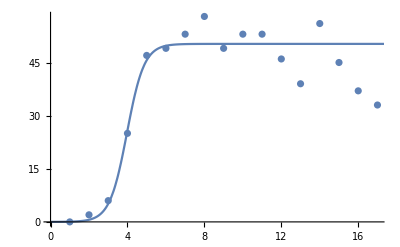

```mathematica
Show[ListPlot@myBlueNumber,Plot[nlm@x,{x,0,20}]]
```

```mathematica
myBlue10per=Solve[nlm@x==0.1*nlm["BestFitParameters"]⟦1,2⟧,x]⟦1,1,2⟧
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

2.99049

```mathematica
nlm>>(analysisFolder<>"_blueFit.dat");
myBlue10per>>(analysisFolder<>"_blue10per.dat");
```

## Combining results

```mathematica
myDirectory=DirectoryName@analysisFolder;
```

```mathematica
myAllBlueSpots=(Get/@FileNames["*bluespots*",myDirectory]);
myAllRedSpots=(Get/@FileNames["*redspotsFiltered*",myDirectory]);
myAllYellowSpots=(Get/@FileNames["*yellowspots*",myDirectory]);
myAllPurpleSpots=(Get/@FileNames["*_purplespots*",myDirectory]);
myAllTransPurpleSpots=(Get/@FileNames["*transpurplespots*",myDirectory]);
myAllGreenSpots=(Get/@FileNames["*greenspotsFiltered*",myDirectory]);
myOffset=(Get/@FileNames["*_blue10per*",myDirectory]);
```

```mathematica
myAllBlueNum=Length/@#&/@myAllBlueSpots;
myAllRedNum=Length/@#&/@myAllRedSpots;
myAllYellowNum=Length/@#&/@myAllYellowSpots;
myAllPurpleNum=Length/@#&/@myAllPurpleSpots;
myAllTransPurpleNum=Length/@#&/@myAllTransPurpleSpots;
myAllGreenNum=Length/@#&/@myAllGreenSpots;
```

```mathematica
(*{Max@#,Min@#}&@(Length/@myAllBlueNum)*)
```

```mathematica
(*maxBlue=Max@(Length/@myAllBlueNum);
myAllBlueNum=Table[If[Length@myAllBlueNum⟦i⟧<maxBlue,Flatten[Append[myAllBlueNum⟦i⟧,ConstantArray[Last@myAllBlueNum⟦i⟧,maxBlue-Length@myAllBlueNum⟦i⟧]],1],myAllBlueNum⟦i⟧],{i,1,Length@myAllBlueNum,1}];
maxRed=Max@(Length/@myAllRedNum);
myAllRedNum=Table[If[Length@myAllRedNum⟦i⟧<maxRed,Flatten[Append[myAllRedNum⟦i⟧,ConstantArray[Last@myAllRedNum⟦i⟧,maxRed-Length@myAllRedNum⟦i⟧]],1],myAllRedNum⟦i⟧],{i,1,Length@myAllRedNum,1}];
maxYellow=Max@(Length/@myAllYellowNum);
myAllYellowNum=Table[If[Length@myAllYellowNum⟦i⟧<maxYellow,Flatten[Append[myAllYellowNum⟦i⟧,ConstantArray[Last@myAllYellowNum⟦i⟧,maxYellow-Length@myAllYellowNum⟦i⟧]],1],myAllYellowNum⟦i⟧],{i,1,Length@myAllYellowNum,1}];
maxPurple=Max@(Length/@myAllPurpleNum);
myAllPurpleNum=Table[If[Length@myAllPurpleNum⟦i⟧<maxPurple,Flatten[Append[myAllPurpleNum⟦i⟧,ConstantArray[Last@myAllPurpleNum⟦i⟧,maxPurple-Length@myAllPurpleNum⟦i⟧]],1],myAllPurpleNum⟦i⟧],{i,1,Length@myAllPurpleNum,1}];
maxTransPurple=Max@(Length/@myAllTransPurpleNum);
myAllTransPurpleNum=Table[If[Length@myAllTransPurpleNum⟦i⟧<maxTransPurple,Flatten[Append[myAllTransPurpleNum⟦i⟧,ConstantArray[Last@myAllTransPurpleNum⟦i⟧,maxTransPurple-Length@myAllTransPurpleNum⟦i⟧]],1],myAllTransPurpleNum⟦i⟧],{i,1,Length@myAllTransPurpleNum,1}];
maxGreen=Max@(Length/@myAllGreenNum);
myAllGreenNum=Table[If[Length@myAllGreenNum⟦i⟧<maxGreen,Flatten[Append[myAllGreenNum⟦i⟧,ConstantArray[Last@myAllGreenNum⟦i⟧,maxGreen-Length@myAllGreenNum⟦i⟧]],1],myAllGreenNum⟦i⟧],{i,1,Length@myAllGreenNum,1}];*)
```

```mathematica
myAllBlueShift=(ShiftingDataPointsMean[myAllBlueNum,myOffset,10,1]);
myAllRedShift=(ShiftingDataPointsMean[myAllRedNum,myOffset,10,1]);
myAllYellowShift=(ShiftingDataPointsMean[myAllYellowNum,myOffset,10,1]);
myAllPurpleShift=(ShiftingDataPointsMean[myAllPurpleNum,myOffset,10,1]);
myAllTransPurpleShift=(ShiftingDataPointsMean[myAllTransPurpleNum,myOffset,10,1]);
myAllGreenShift=(ShiftingDataPointsMean[myAllGreenNum,myOffset,10,1]);
```

```mathematica
myOffset
```

{2.46588,2.2053,2.60489,1.97353,1.48598,2.26324,4.04097,2.99049,4.10957,0.959341}

#### SG

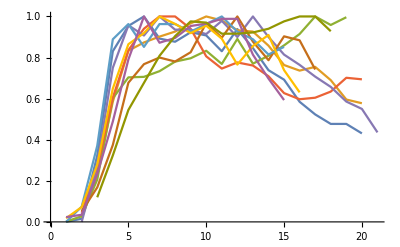

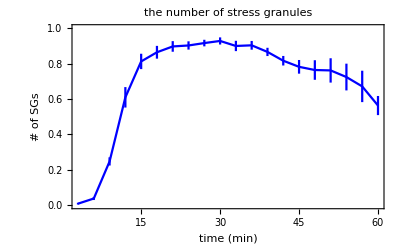

```mathematica
myAllBlueShiftNorm=#/Max@#&/@myAllBlueShift;
myBlueMeanSEM=N@{Mean@#,ErrorBar@((StandardDeviation@#)/(Sqrt@Length@#))}&/@DeleteCases[Flatten/@Thread@myAllBlueShiftNorm,x_/;Length@x<2];
myBlueMeanSEM={{#⟦1⟧,#⟦2⟧},#⟦3⟧}&/@Flatten/@Thread@{3*(Range@Length@myBlueMeanSEM),myBlueMeanSEM};
DeleteCases[#,x_/;x⟦2⟧=={}]&/@(Thread@{Range@Length@myAllBlueShiftNorm⟦1⟧,#}&/@myAllBlueShiftNorm)//ListLinePlot
ErrorListPlot[myBlueMeanSEM,Joined->True,PlotRange->{All,{0,1}},PlotStyle->Blue,Frame->True,BaseStyle->{FontFamily->"Helvetica",FontSize->15},PlotLabel->"the number of stress granules",FrameLabel->{"time (min)","# of SGs"},ImageSize->400]
```

#### All mRNA

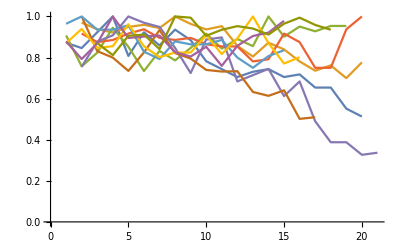

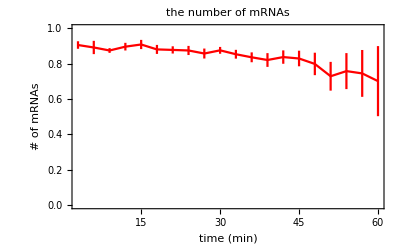

```mathematica
myAllRedShiftNorm=#/Max@#&/@myAllRedShift;
myRedMeanSEM=N@{Mean@#,ErrorBar@((StandardDeviation@#)/(Sqrt@Length@#))}&/@DeleteCases[Flatten/@Thread@myAllRedShiftNorm⟦2;;⟧,x_/;Length@x<2];
myRedMeanSEM={{#⟦1⟧,#⟦2⟧},#⟦3⟧}&/@Flatten/@Thread@{3*Range@Length@myRedMeanSEM,myRedMeanSEM};
DeleteCases[#,x_/;x⟦2⟧=={}]&/@(Thread@{Range@Length@myAllRedShiftNorm⟦1⟧,#}&/@myAllRedShiftNorm)//ListLinePlot
ErrorListPlot[myRedMeanSEM,Joined->True,PlotRange->{All,{0,1}},PlotStyle->Red,Frame->True,BaseStyle->{FontFamily->"Helvetica",FontSize->15},PlotLabel->"the number of mRNAs",FrameLabel->{"time (min)","# of mRNAs"},ImageSize->400]
```

#### Translating mRNA in Cytoplasm

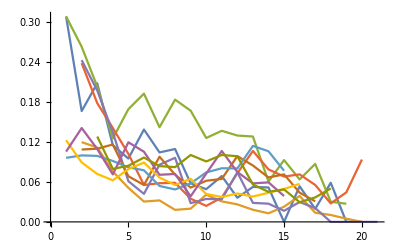

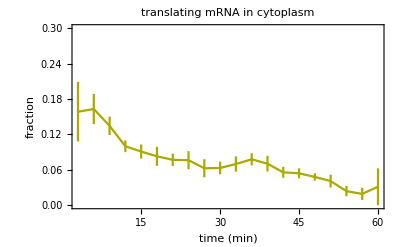

```mathematica
myAllTransCytoPercentage=(myAllYellowShift-myAllTransPurpleShift)/myAllRedShift;
myTransCytoPerMeanSEM=N@{Mean@#,ErrorBar@((StandardDeviation@#)/(Sqrt@Length@#))}&/@DeleteCases[Flatten/@Thread@myAllTransCytoPercentage⟦2;;⟧,x_/;Length@x<2];
myTransCytoPerMeanSEM={{#⟦1⟧,#⟦2⟧},#⟦3⟧}&/@Flatten/@Thread@{3*Range@Length@myTransCytoPerMeanSEM,myTransCytoPerMeanSEM};
DeleteCases[#,x_/;x⟦2⟧=={}]&/@(Thread@{Range@Length@myAllTransCytoPercentage⟦1⟧,#}&/@myAllTransCytoPercentage)//ListLinePlot
ErrorListPlot[myTransCytoPerMeanSEM,Joined->True,PlotRange->{All,{0,0.3}},PlotStyle->Darker@Yellow,Frame->True,BaseStyle->{FontFamily->"Helvetica",FontSize->15},PlotLabel->"translating mRNA in cytoplasm",FrameLabel->{"time (min)","fraction"},ImageSize->400]
```

#### Non-Translating mRNA in Cytoplasm

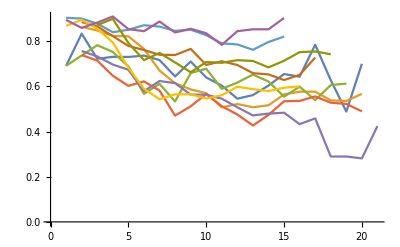

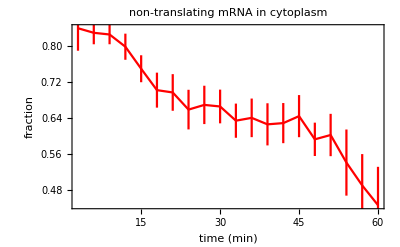

```mathematica
myAllNonTransCytoPercentage=(myAllRedShift-myAllPurpleShift-myAllYellowShift+myAllTransPurpleShift)/myAllRedShift;
myNonTransCytoPerMeanSEM=N@{Mean@#,ErrorBar@((StandardDeviation@#)/(Sqrt@Length@#))}&/@DeleteCases[Flatten/@Thread@myAllNonTransCytoPercentage⟦2;;⟧,x_/;Length@x<2];
myNonTransCytoPerMeanSEM={{#⟦1⟧,#⟦2⟧},#⟦3⟧}&/@Flatten/@Thread@{3*Range@Length@myNonTransCytoPerMeanSEM,myNonTransCytoPerMeanSEM};
DeleteCases[#,x_/;x⟦2⟧=={}]&/@(Thread@{Range@Length@myAllNonTransCytoPercentage⟦1⟧,#}&/@myAllNonTransCytoPercentage)//ListLinePlot
ErrorListPlot[myNonTransCytoPerMeanSEM,Joined->True,PlotRange->{All,All},PlotStyle->Red,Frame->True,BaseStyle->{FontFamily->"Helvetica",FontSize->15},PlotLabel->"non-translating mRNA in cytoplasm",FrameLabel->{"time (min)","fraction"},ImageSize->400]
```

#### Translating mRNA in SG

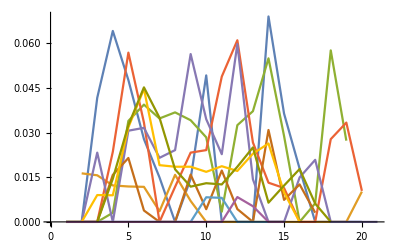

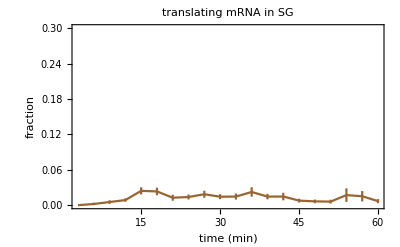

```mathematica
myAllTransPurpleShiftPercentage=myAllTransPurpleShift/myAllRedShift;
myTransPurplePerMeanSEM=N@{Mean@#,ErrorBar@((StandardDeviation@#)/(Sqrt@Length@#))}&/@DeleteCases[Flatten/@Thread@myAllTransPurpleShiftPercentage⟦2;;⟧,x_/;Length@x<2];
myTransPurplePerMeanSEM={{#⟦1⟧,#⟦2⟧},#⟦3⟧}&/@Flatten/@Thread@{3*Range@Length@myTransPurplePerMeanSEM,myTransPurplePerMeanSEM};
DeleteCases[#,x_/;x⟦2⟧=={}]&/@(Thread@{Range@Length@myAllTransPurpleShiftPercentage⟦1⟧,#}&/@myAllTransPurpleShiftPercentage)//ListLinePlot
ErrorListPlot[myTransPurplePerMeanSEM,Joined->True,PlotRange->{All,{0,0.3}},PlotStyle->Brown,Frame->True,BaseStyle->{FontFamily->"Helvetica",FontSize->15},PlotLabel->"translating mRNA in SG",FrameLabel->{"time (min)","fraction"},ImageSize->400]
```

#### Non-Translating mRNA in SG

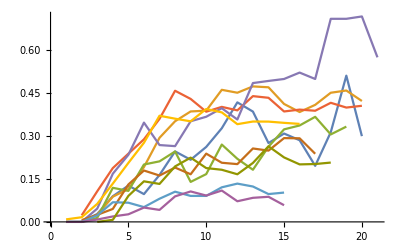

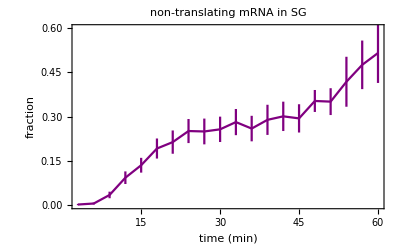

```mathematica
myAllPurpleShiftPercentage=(myAllPurpleShift-myAllTransPurpleShift)/myAllRedShift;
myNonTransPurplePerMeanSEM=N@{Mean@#,ErrorBar@((StandardDeviation@#)/(Sqrt@Length@#))}&/@DeleteCases[Flatten/@Thread@myAllPurpleShiftPercentage⟦2;;⟧,x_/;Length@x<2];
myNonTransPurplePerMeanSEM={{#⟦1⟧,#⟦2⟧},#⟦3⟧}&/@Flatten/@Thread@{3*Range@Length@myNonTransPurplePerMeanSEM,myNonTransPurplePerMeanSEM};
DeleteCases[#,x_/;x⟦2⟧=={}]&/@(Thread@{Range@Length@myAllPurpleShiftPercentage⟦1⟧,#}&/@myAllPurpleShiftPercentage)//ListLinePlot
ErrorListPlot[myNonTransPurplePerMeanSEM,Joined->True,PlotRange->{All,{0,0.6}},PlotStyle->Purple,Frame->True,BaseStyle->{FontFamily->"Helvetica",FontSize->15},PlotLabel->"non-translating mRNA in SG",FrameLabel->{"time (min)","fraction"},ImageSize->400]
```

### Adding pre-stress translation percentage with the data from 20170927 KDM5B pre-stress - Reanalyzed

```mathematica
{FileNameSetter[Dynamic@myDirectory,"Directory"],Dynamic@myDirectory}
```

{$CellContext`myDirectoryDirectoryAll,}

```mathematica
myPreAllRedSpots=Get/@FileNames["*redspotsFiltered*",myDirectory];
myPreAllYellowSpots=Get/@FileNames["*yellowspots*",myDirectory];
myPreAllGreenSpots=Get/@FileNames["*greenspotsFiltered*",myDirectory];
```

```mathematica
myPreTranslationSEM={{0,Mean@#},ErrorBar@((StandardDeviation@#)/(Sqrt@Length@#))}&@(Length@@@myPreAllYellowSpots / Length@@@myPreAllRedSpots//N)
```

{{0,0.314833},ErrorBar[0.0327837]}

```mathematica
myPreNonTranslationSEM={{0,Mean@#},ErrorBar@((StandardDeviation@#)/(Sqrt@Length@#))}&@(1-Length@@@myPreAllYellowSpots / Length@@@myPreAllRedSpots//N)
```

{{0,0.685167},ErrorBar[0.0327837]}

#### Adding pre-stress translation percentage

```mathematica
myBlueMeanSEMwithPre=Prepend[myBlueMeanSEM,{{0,0},ErrorBar@0}];
myBlueMeanSEMwithPre⟦2;;,1,1⟧+=7;
myTransCytoPerMeanSEMwithPre=Prepend[myTransCytoPerMeanSEM,myPreTranslationSEM];
myTransCytoPerMeanSEMwithPre⟦2;;,1,1⟧+=7;
myNonTransCytoPerMeanSEMwithPre=Prepend[myNonTransCytoPerMeanSEM,myPreNonTranslationSEM];
myNonTransCytoPerMeanSEMwithPre⟦2;;,1,1⟧+=7;
myTransPurplePerMeanSEMwithPre=Prepend[myTransPurplePerMeanSEM,{{0,0},ErrorBar@0}];
myTransPurplePerMeanSEMwithPre⟦2;;,1,1⟧+=7;
myNonTransPurplePerMeanSEMwithPre=Prepend[myNonTransPurplePerMeanSEM,{{0,0},ErrorBar@0}];
myNonTransPurplePerMeanSEMwithPre⟦2;;,1,1⟧+=7;
```

```mathematica
myFig1aEnd=19;
```

```mathematica
myFig1aPlot=ErrorListPlot[{myBlueMeanSEMwithPre⟦;;myFig1aEnd⟧,myNonTransCytoPerMeanSEMwithPre⟦;;myFig1aEnd⟧,myNonTransPurplePerMeanSEMwithPre⟦;;myFig1aEnd⟧,myTransCytoPerMeanSEMwithPre⟦;;myFig1aEnd⟧,myTransPurplePerMeanSEMwithPre⟦;;myFig1aEnd⟧},
PlotRange->{All,{-0.03,1.03}},Joined->True,BaseStyle->{FontFamily->"Helvetica",FontSize->20},Frame->True,PlotMarkers->Automatic,
PlotStyle->{Blue,Red,Purple,Darker@Yellow,Brown},
PlotLegends->{"SG","Non-translating RNA in Cytoplasm","Non-translating RNA in SG","Translating RNA in Cytoplasm","Translating RNA in SG"},
PlotLabel->"Translation shutoff during stress (10 cells)",FrameLabel->{"time after stress induction (min)","fraction"},ImageSize->600]
```

-Graphics-

#### Plotting bar chart at time point 40

```mathematica
Position[#,40]&/@{myNonTransCytoPerMeanSEMwithPre,myNonTransPurplePerMeanSEMwithPre,myTransCytoPerMeanSEMwithPre,myTransPurplePerMeanSEMwithPre}
```

{{{12,1,1}},{{12,1,1}},{{12,1,1}},{{12,1,1}}}

```mathematica
myAllData4Bar={myNonTransCytoPerMeanSEMwithPre,myNonTransPurplePerMeanSEMwithPre,myTransCytoPerMeanSEMwithPre,myTransPurplePerMeanSEMwithPre}⟦All,12⟧;
myAllData4Bar=Table[{{i,#⟦1,2⟧},ErrorBar@{#⟦2,1⟧,-#⟦2,1⟧}}&@myAllData4Bar⟦i⟧,{i,1,Length@myAllData4Bar,1}]
```

{{{1,0.633798},ErrorBar[{0.0379928,-0.0379928}]},{{2,0.281772},ErrorBar[{0.0443897,-0.0443897}]},{{3,0.0698182},ErrorBar[{0.0128621,-0.0128621}]},{{4,0.0146121},ErrorBar[{0.00507729,-0.00507729}]}}

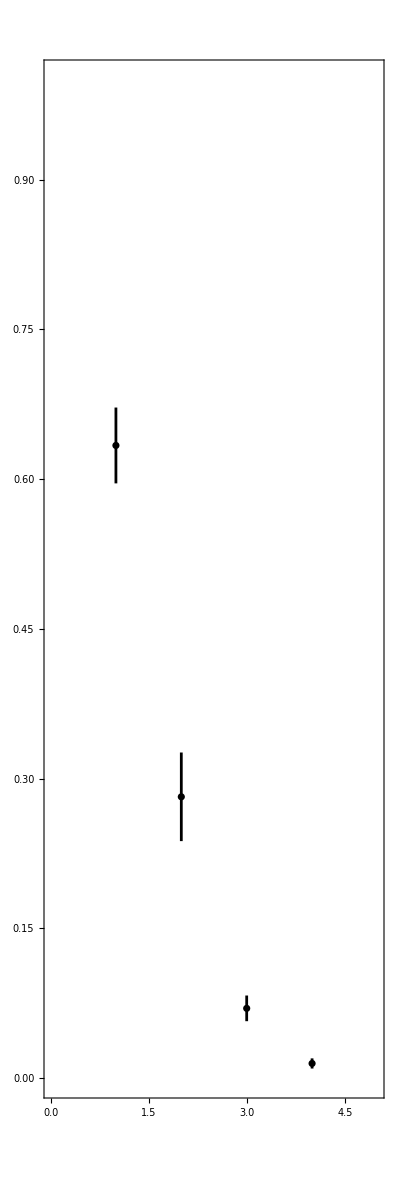

```mathematica
p1=ErrorListPlot[myAllData4Bar,PlotRange->{{0,5},{0,1}},Frame->True,AspectRatio->3,PlotStyle->{Black,Thickness[0.005]},PlotMarkers->None]
```

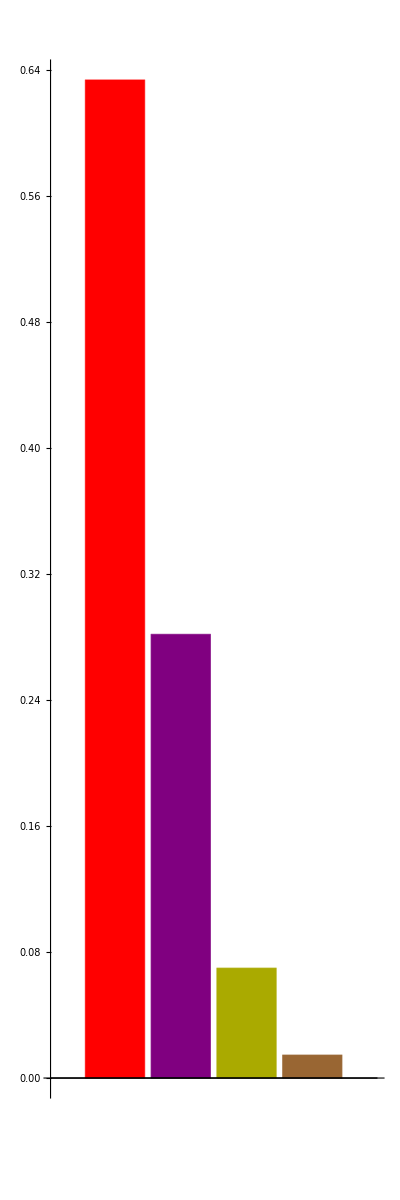

```mathematica
p2=BarChart[myAllData4Bar⟦All,1,2⟧,ChartStyle->{Red,Purple,Darker@Yellow,Brown}(*{Darker[Gray,0.5],Gray,Lighter[Gray,0.5],White}*),(*ChartLabels->{"Cyto","SG","Cyto","SG"},*)BaseStyle->{FontFamily->"Arial",FontSize->25},AspectRatio->3]
```

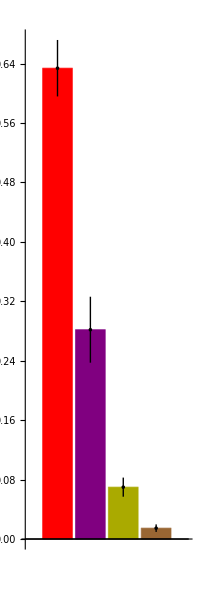

```mathematica
myFig1aBar=Show[p2,p1(*,ImageSize->200*)]
```

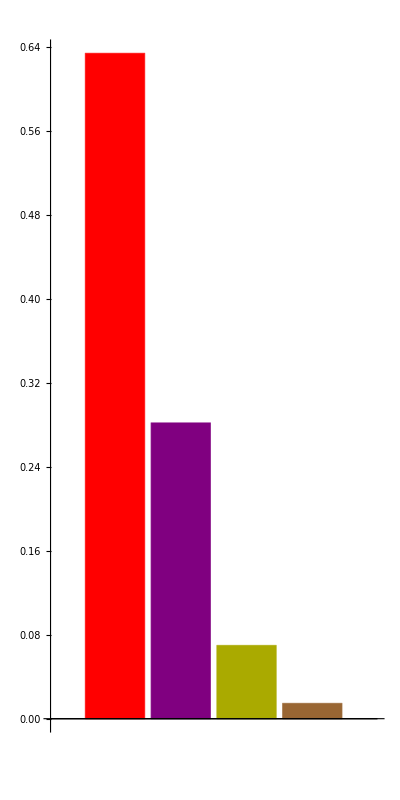

```mathematica
p3=BarChart[myAllData4Bar⟦All,1,2⟧,ChartStyle->{Red,Purple,Darker@Yellow,Brown}(*{Darker[Gray,0.5],Gray,Lighter[Gray,0.5],White}*),(*ChartLabels->{"Cyto","SG","Cyto","SG"},*)BaseStyle->{FontFamily->"Arial",FontSize->10},AspectRatio->2]
```

```mathematica
myNonCyto=Thread@{1,myAllNonTransCytoPercentage⟦All,11⟧//N};
myNonSG=Thread@{2,myAllPurpleShiftPercentage⟦All,11⟧//N};
myTransCyto=Thread@{3,myAllTransCytoPercentage⟦All,11⟧//N};
myTransSG=Thread@{4,myAllTransPurpleShiftPercentage⟦All,11⟧//N};
```

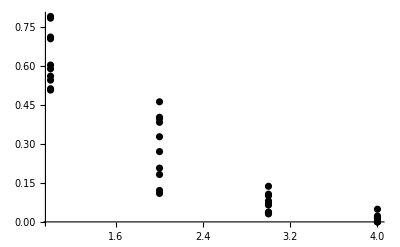

```mathematica
p4=ListPlot[Flatten[{myNonCyto,myNonSG,myTransCyto,myTransSG},1],PlotStyle->Black]
```

```mathematica
myFig1aBarNew=Show[p3,p1,p4,ImageSize->100]
```

-Graphics-

## Figure 1c, 1d, and S1 - translation shut off (single molecules)

## pre-processing each data

### Reading in Images

```mathematica
{FileNameSetter[Dynamic[mymovie]],Dynamic[mymovie]}
```

{$CellContext`mymovieOpenAll,}

```mathematica
myColMovie=Import[mymovie]//Partition[#,3]&//Transpose;
If[DirectoryQ@(DirectoryName[mymovie]<>"Analysis\\")==False,CreateDirectory@(DirectoryName[mymovie]<>"Analysis\\")];
analysisFolder=DirectoryName[mymovie]<>"Analysis\\"<>StringDrop[StringDelete[mymovie,DirectoryName[mymovie]],-4];
```

### Reading in Parameters (if parameters exist)

#### basic parameters

```mathematica
myTfFunc=<<(DirectoryName@mymovie<>"TransformationFunction.m");
```

```mathematica
mymask=Import@(analysisFolder<>"_mask.tif");
```

```mathematica
avgFrameN=<<(analysisFolder<>"_avgFrameN.dat");
myMaxN=Length@myColMovie⟦1⟧-avgFrameN+1;
myColMovieRunAv=If[avgFrameN==1,myColMovie,MovingAverage[#,avgFrameN]&/@myColMovie];
```

#### basic color parameters

```mathematica
thred=<<(analysisFolder<>"_thred.dat");
{mymaxred,thred2,bandpassred,dotsizered}=<<(analysisFolder<>"_thred2.dat");
```

```mathematica
thgreen=<<(analysisFolder<>"_thgreen.dat");
{mymaxgreen,thgreen2,bandpassgreen,dotsizegreen}=<<(analysisFolder<>"_thgreen2.dat");
```

```mathematica
thblue=<<(analysisFolder<>"_thblue.dat");
{mymaxblue,thblue2,bandpassblue,dotsizeblue}=<<(analysisFolder<>"_thblue2.dat");
```

#### processed data

```mathematica
myRNA1Track=<<(analysisFolder<>"_myTrack_red_1.dat");
myRNA2Track=<<(analysisFolder<>"_myTrack_red_2.dat");
```

```mathematica
myRNA1fit=<<(analysisFolder<>"_myRNA1fit.dat");
myRNA2fit=<<(analysisFolder<>"_myRNA2fit.dat");
```

```mathematica
{myDiskSize,myDonutSize}=<<(analysisFolder<>"_DiskDonutSize");
```

```mathematica
myProtein1Int=<<(analysisFolder<>"_myProtein1Int.dat");
myProtein1BG=<<(analysisFolder<>"_myProtein1BG.dat");
```

```mathematica
myProtein1IntBGcor=MovingAverage[myProtein1Int,20]-MovingAverage[myProtein1BG,20];
```

```mathematica
myProtein2Int=<<(analysisFolder<>"_myProtein2Int.dat");
myProtein2BG=<<(analysisFolder<>"_myProtein2BG.dat");
```

```mathematica
myProtein2IntBGcor=MovingAverage[myProtein2Int,20]-MovingAverage[myProtein2BG,20];
```

### Make Mask

```mathematica
If[FileExistsQ[analysisFolder<>"_avg.tif"]==True,
avgImg=Import[analysisFolder<>"_avg.tif"];,
avgImg=Mean/@myColMovie;
Export[analysisFolder<>"_avg.tif",avgImg]];
If[FileExistsQ[analysisFolder<>"_max.tif"]==True,
maxImg=Import[analysisFolder<>"_max.tif"],
maxImg=ImageApply[Max,#]&/@myColMovie;
Export[analysisFolder<>"_max.tif",maxImg]];
```

```mathematica
Manipulate[maxImg⟦3⟧//ImageAdjust[#,{0,0,1},{threshold1,threshold2}]&,
Button["Choose threshold such that the shape of the cell can be visualized and CLICK",thtemp={threshold1,threshold2}],
{threshold1,0,0.2,0.001},{{threshold2,0.1},0,0.2,0.001}]
```

```mathematica
ImageAdjust[maxImg⟦3⟧,{0,0,1},thtemp]
```

```mathematica
mymask=-Graphics-;
Export[analysisFolder<>"_mask.tif",mymask];
```

```mathematica
(*mymask=Image@ConstantArray[1,ImageDimensions@avgImg];
Export[analysisFolder<>"_mask.tif",mymask];*)
```

### Running z-average

```mathematica
avgFrameN=1;
avgFrameN>>analysisFolder<>"_avgFrameN.dat";
myMaxN=Length@myColMovie⟦1⟧-avgFrameN+1;
```

```mathematica
myColMovieRunAv=If[avgFrameN==1,myColMovie,MovingAverage[#,avgFrameN]&/@myColMovie];
```

```mathematica
Manipulate[myColMovieRunAv⟦channel,frame⟧//ImageAdjust[#,{0,0,1},{0,threshold}]&,{channel,Range@Length@myColMovieRunAv},{frame,1,myMaxN,1},{threshold,0,0.3,0.001}]
```

### Setting Threshold

```mathematica
MyThresholding[myColMovieRunAv,analysisFolder]
```

### Setting Threshold for Binarization

```mathematica
MyBinarization[myColMovieRunAv,analysisFolder]
```

### Tracking each particles w/ Click-and-Track function

```mathematica
ClickAndTrack[myColMovie,myColMovieRunAv,analysisFolder]
```

### Fitting Particles

```mathematica
myRNA1Track=<<(analysisFolder<>"_myTrack_red_1.dat");
myRNA1Track = DeleteCases[myRNA1Track,x_/;x⟦3,1⟧=={0.,0.}];
```

```mathematica
{myRNA1fit,myRedCroppedData,myRedCenters}=MyParticleFitter[myColMovie,1,{myRNA1Track},5,avgFrameN];
myRNA1fit=myRNA1fit⟦1⟧;
```

```mathematica
{myRNA1fitFiltered}=FilterFitOutlier[{myRNA1fit},5,20];
```

```mathematica
myRNA1fit>>(analysisFolder<>"_myRNA1fit.dat");
myRNA1fitFiltered>>(analysisFolder<>"_myRNA1fitFiltered.dat");
```

```mathematica
myRNA2Track=<<(analysisFolder<>"_myTrack_red_2.dat");
```

```mathematica
{myRNA2fit,myRedCroppedData,myRedCenters}=MyParticleFitter[myColMovie,1,{myRNA2Track},5,avgFrameN];
myRNA2fit=myRNA2fit⟦1⟧;
```

```mathematica
myRNA2fit>>(analysisFolder<>"_myRNA2fit.dat");
```

### Calculating Intensities in Protein Channel

```mathematica
Manipulate[
diskMask=DiskMatrix@disk;
donutMask=DiskMatrix@donut-ArrayPad[DiskMatrix@(donut-1),1];
Image[ArrayPad[0.7*ArrayPad[diskMask,donut-disk]+0.3*donutMask,1],ImageSize->300],Button["Save these parameters",myDiskSize=disk;myDonutSize=donut;myDiskMask=diskMask;myDonutMask=donutMask;{myDiskSize,myDonutSize}>>(analysisFolder<>"_DiskDonutSize")],{{disk,1},1,5,1},{{donut,3},1,5,1}]
```

```mathematica
myProtein1Position={#⟦1⟧,#⟦2⟧,#⟦4,1⟧}&/@myRNA1fit;
myProtein1Position⟦All,3⟧=myTfFunc@myProtein1Position⟦All,3⟧;
myProtein1Position⟦All,3⟧=Img2DataCoord[ImageDimensions@myColMovie⟦1,1⟧,#]&/@myProtein1Position⟦All,3⟧;
{myDiskMaskList,myDonutMaskList}=ConstantArray[ConstantArray[ConstantArray[0,ImageDimensions@myColMovie⟦1,1⟧],Length@myColMovie⟦1⟧],2];
Table[myDiskMaskList⟦myProtein1Position⟦i,2⟧,myProtein1Position⟦i,3,1⟧-myDiskSize;;myProtein1Position⟦i,3,1⟧+myDiskSize,myProtein1Position⟦i,3,2⟧-myDiskSize;;myProtein1Position⟦i,3,2⟧+myDiskSize⟧=myDiskMask;,{i,1,Length@myColMovie⟦1⟧,1}];
Table[myDonutMaskList⟦myProtein1Position⟦i,2⟧,myProtein1Position⟦i,3,1⟧-myDonutSize;;myProtein1Position⟦i,3,1⟧+myDonutSize,myProtein1Position⟦i,3,2⟧-myDonutSize;;myProtein1Position⟦i,3,2⟧+myDonutSize⟧=myDonutMask;,{i,1,Length@myColMovie⟦1⟧,1}];
myDiskMaskList=Image/@myDiskMaskList;myDonutMaskList=Image/@myDonutMaskList;
myProtein1Int=(ComponentMeasurements[#,"MeanIntensity"]&/@ImageMultiply/@Thread@{myColMovie⟦2⟧,myDiskMaskList})⟦All,1,2⟧;
myProtein1BG=(ComponentMeasurements[#,"MeanIntensity"]&/@ImageMultiply/@Thread@{myColMovie⟦2⟧,myDonutMaskList})⟦All,1,2⟧;
```

```mathematica
myProtein1Int>>analysisFolder<>"_myProtein1Int.dat";
myProtein1BG>>analysisFolder<>"_myProtein1BG.dat";
```

```mathematica
myProtein1IntBGcor=MovingAverage[myProtein1Int,20]-MovingAverage[myProtein1BG,20];
```

```mathematica
myProtein2Position={#⟦1⟧,#⟦2⟧,#⟦4,1⟧}&/@myRNA2fit;
myProtein2Position⟦All,3⟧=myTfFunc@myProtein2Position⟦All,3⟧;
myProtein2Position⟦All,3⟧=Img2DataCoord[ImageDimensions@myColMovie⟦1,1⟧,#]&/@myProtein2Position⟦All,3⟧;
{myDiskMaskList,myDonutMaskList}=ConstantArray[ConstantArray[ConstantArray[0,ImageDimensions@myColMovie⟦1,1⟧],Length@myColMovie⟦1⟧],2];
Table[myDiskMaskList⟦myProtein2Position⟦i,2⟧,myProtein2Position⟦i,3,1⟧-myDiskSize;;myProtein2Position⟦i,3,1⟧+myDiskSize,myProtein2Position⟦i,3,2⟧-myDiskSize;;myProtein2Position⟦i,3,2⟧+myDiskSize⟧=myDiskMask;,{i,1,Length@myColMovie⟦1⟧,1}];
Table[myDonutMaskList⟦myProtein2Position⟦i,2⟧,myProtein2Position⟦i,3,1⟧-myDonutSize;;myProtein2Position⟦i,3,1⟧+myDonutSize,myProtein2Position⟦i,3,2⟧-myDonutSize;;myProtein2Position⟦i,3,2⟧+myDonutSize⟧=myDonutMask;,{i,1,Length@myColMovie⟦1⟧,1}];
myDiskMaskList=Image/@myDiskMaskList;myDonutMaskList=Image/@myDonutMaskList;
myProtein2Int=(ComponentMeasurements[#,"MeanIntensity"]&/@ImageMultiply/@Thread@{myColMovie⟦2⟧,myDiskMaskList})⟦All,1,2⟧;
myProtein2BG=(ComponentMeasurements[#,"MeanIntensity"]&/@ImageMultiply/@Thread@{myColMovie⟦2⟧,myDonutMaskList})⟦All,1,2⟧;
```

```mathematica
myProtein2Int>>analysisFolder<>"_myProtein2Int.dat";
myProtein2BG>>analysisFolder<>"_myProtein2BG.dat";
```

```mathematica
myProtein2IntBGcor=MovingAverage[myProtein2Int,20]-MovingAverage[myProtein2BG,20];
```

## Plotting data

```mathematica
myViewPoint={1,-2.5,1.5};
```

#### Track 1

```mathematica
myRNA1fit=<<(analysisFolder<>"_myRNA1fit.dat");
```

```mathematica
{myRNA1fitFiltered}=FilterFitOutlier[{myRNA1fit},5,20];
```

```mathematica
mySG1=<<(analysisFolder<>"_myTrack_blue_1.dat");
```

```mathematica
myProtein1Int=<<(analysisFolder<>"_myProtein1Int.dat");
myProtein1BG=<<(analysisFolder<>"_myProtein1BG.dat");
```

```mathematica
myProtein1IntBGcor=MovingAverage[myProtein1Int,20]-MovingAverage[myProtein1BG,20];
```

```mathematica
mySG1outlinePlot=<<(analysisFolder<>"_SG1outlinePlot.dat");
mySG1outlinePlotRings=<<(analysisFolder<>"_SG1outlinePlotRings.dat");
```

```mathematica
mySG1centerPlot=ListPointPlot3D[mySG1center,PlotStyle->Blue];
```

```mathematica
mySG1center=Flatten/@({#⟦2⟧,#⟦3,1⟧}&/@mySG1);
mySG1outline=Table[Flatten/@Thread@{mySG1⟦i,2⟧,mySG1⟦i,3,10⟧},{i,1,Length@mySG1,1}];
```

```mathematica
mySG1outlinePlot=ListSurfacePlot3D[Flatten[mySG1outline,1],MaxPlotPoints->500,PlotStyle->None,MeshStyle->Lighter[Blue,0.7]];
mySG1outlinePlotRings=ListSurfacePlot3D[Flatten[mySG1outline,1],MaxPlotPoints->500,Mesh->{30,0,0},PlotStyle->None,MeshStyle->Blue];
```

```mathematica
mySG1centerPlot=ListPointPlot3D[mySG1center,PlotStyle->{Blue,PointSize@0.007}];
```

```mathematica
mySG1outlinePlot>>(analysisFolder<>"_SG1outlinePlot.dat");
mySG1outlinePlotRings>>(analysisFolder<>"_SG1outlinePlotRings.dat");
```

```mathematica
myRNA2Dcord=Thread@{#⟦All,2⟧,#⟦All,4,1⟧}&@myRNA1fitFiltered;
```

```mathematica
TrackFiller[tracksList_]:=Module[{filledTracksList,myIdx,missingStart,missingNum,missingStartShifted,spotEnd,spotStart,fillingNum,fillingPos,fillingSpots},
filledTracksList=tracksList;
Table[
myIdx=Differences@filledTracksList⟦i,All,1⟧;
missingStart=Position[myIdx,x_/;x>1]+1//Flatten;
missingNum=Cases[myIdx,x_/;x>1]-1;
If[missingStart≠{},
missingStartShifted=missingStart;
missingStartShifted⟦2;;⟧=missingStart⟦2;;⟧+(FoldList[Plus,missingNum])⟦;;Length@missingNum-1⟧;
Table[
spotEnd=(filledTracksList⟦i,missingStartShifted⟦j⟧-1⟧);
spotStart=filledTracksList⟦i,missingStartShifted⟦j⟧⟧;
fillingNum=Range[spotEnd⟦1⟧+1,spotStart⟦1⟧-1];
fillingPos=Plus[#,spotEnd⟦2⟧]&/@Outer[Times,Range@missingNum⟦j⟧/(missingNum⟦j⟧+1),spotStart⟦2⟧-spotEnd⟦2⟧];
fillingSpots=Thread@{fillingNum,fillingPos};
Table[filledTracksList⟦i⟧=Insert[filledTracksList⟦i⟧,fillingSpots⟦k⟧,missingStartShifted⟦j⟧+k-1],{k,1,missingNum⟦j⟧,1}];
,{j,1,Length@missingStart,1}];];
,{i,1,Length@filledTracksList,1}];
filledTracksList]
```

```mathematica
{myRNA2DcordFilled}=TrackFiller@{myRNA2Dcord};
```

```mathematica
myRNA1Shift=Flatten/@myRNA2DcordFilled;
myRNA1Shift⟦All,{2,3}⟧=myTfFunc@myRNA1Shift⟦All,{2,3}⟧;
myRNA1Plot=ListPointPlot3D[myRNA1Shift,PlotStyle->Red];
myRNA1Line=Graphics3D[{Red,Line@myRNA1Shift}];
```

```mathematica
(*for smaller marker*)
```

```mathematica
myRNA1Plot=ListPointPlot3D[myRNA1Shift,PlotStyle->{Red,PointSize@0.007}];
myRNA1Line=Graphics3D[{Red,Line@myRNA1Shift}];
```

```mathematica
myProtein1Plot=Table[ListPointPlot3D[{myRNA1Shift⟦i+5⟧+{0,3,3}},PlotStyle->{Lighter[Green,(Max@#-#⟦i⟧)/Max@#]&@myProtein1IntBGcor,PointSize@0.008}],{i,1,Length@myProtein1IntBGcor,1}];
```

```mathematica
myTranslationShutoff1=Show[myRNA1Plot,myRNA1Line,mySG1centerPlot,myProtein1Plot,mySG1outlinePlotRings,mySG1outlinePlot,BoxRatios-> {4,1,1},PlotRange->All,BaseStyle->{FontFamily->"Helvetica",FontSize->20},ViewPoint->myViewPoint,ImageSize->600,ImageResolution-> 300]
```

```mathematica
Table[{i,ToString@Round@((i-380)*pixelSize)},{i,380,450,2/pixelSize}]
```

{{380.,0},{395.385,2},{410.769,4},{426.154,6},{441.538,8}}

```mathematica
myTranslationShutoff1=Show[myRNA1Plot,myRNA1Line,mySG1centerPlot,myProtein1Plot,mySG1outlinePlotRings,mySG1outlinePlot,BoxRatios-> {4,1,1},PlotRange->All,Ticks->{Table[{i,ToString@(intervTime*i)},{i,0,300,150}],Table[{i,ToString@Round@((i-180)*pixelSize)},{i,180,220,5/pixelSize}],Table[{i,ToString@Round@((i-380)*pixelSize)},{i,380,450,4/pixelSize}]},BaseStyle->{FontFamily->"Helvetica",FontSize->20},ViewPoint->myViewPoint,ImageSize->600,ImageResolution-> 300]
```

```mathematica
Export[myDirectoryFig<>"fig1b1.png",myTranslationShutoff1,ImageResolution->300];
```

```mathematica
(* plotting up to ~8.5 min (260 frames) *)
```

```mathematica
myNonTransltingRNA=Show[myRNA1Plot,myRNA1Line,mySG1centerPlot,myProtein1Plot,mySG1outlinePlotRings,mySG1outlinePlot,PlotRange->{{0,260},All,All},BoxRatios-> {4,1,1},PlotRange->All,BaseStyle->{FontFamily->"Helvetica",FontSize->20},ViewPoint->myViewPoint,ImageSize->600,ImageResolution-> 300]
```

```mathematica
myNonTransltingRNA=Show[myRNA1Plot,myRNA1Line,mySG1centerPlot,myProtein1Plot,mySG1outlinePlotRings,mySG1outlinePlot,PlotRange->{{0,260},{175,240},{370,450}},BoxRatios-> {4,1,1},PlotRange->All,Ticks->{Table[{i,ToString@(intervTime*i)},{i,0,260,60}],Table[{i,ToString@Round@((i-180)*pixelSize)},{i,180,240,3/pixelSize}],Table[{i,ToString@Round@((i-380)*pixelSize)},{i,380,450,4/pixelSize}]},BaseStyle->{FontFamily->"Helvetica",FontSize->20},ViewPoint->myViewPoint,ImageSize->600,ImageResolution-> 300]
```

```mathematica
Export[myDirectoryFig<>"fig1c_translatingRNAinSG_upto9min.png",myNonTransltingRNA,Background->None,ImageResolution->300];
```

#### Track 2

```mathematica
myRNA2fit=<<(analysisFolder<>"_myRNA2fit.dat");
```

```mathematica
mySG2=<<(analysisFolder<>"_myTrack_blue_2.dat");
```

```mathematica
myProtein2Int=<<(analysisFolder<>"_myProtein2Int.dat");
myProtein2BG=<<(analysisFolder<>"_myProtein2BG.dat");
```

```mathematica
myProtein2IntBGcor=MovingAverage[myProtein2Int,20]-MovingAverage[myProtein2BG,20];
```

```mathematica
mySG2center=Flatten/@({#⟦2⟧,#⟦3,1⟧}&/@mySG2);
mySG2outline=Table[Flatten/@Thread@{mySG2⟦i,2⟧,mySG2⟦i,3,10⟧},{i,1,Length@mySG2,1}];
```

```mathematica
mySG2outlinePlot=ListSurfacePlot3D[Flatten[mySG2outline,1],MaxPlotPoints->500,PlotStyle->None,MeshStyle->Lighter[Blue,0.7]];
mySG2outlinePlotRings=ListSurfacePlot3D[Flatten[mySG2outline,1],MaxPlotPoints->500,Mesh->{30,0,0},PlotStyle->None,MeshStyle->Blue];
mySG2centerPlot=ListPointPlot3D[mySG2center,PlotStyle->Blue];
```

```mathematica
mySG2centerPlot=ListPointPlot3D[mySG2center,PlotStyle->{Blue,PointSize@0.007}];
```

```mathematica
mySG2outlinePlot=<<(analysisFolder<>"_SG2outlinePlot.dat");
mySG2outlinePlotRings=<<(analysisFolder<>"_SG2outlinePlotRings.dat");
mySG2centerPlot=ListPointPlot3D[mySG2center,PlotStyle->Blue];
```

```mathematica
mySG2outlinePlot>>(analysisFolder<>"_SG2outlinePlot.dat");
mySG2outlinePlotRings>>(analysisFolder<>"_SG2outlinePlotRings.dat");
```

```mathematica
{myRNA2fitFiltered}=FilterFitOutlier[{myRNA2fit},5,20];
myRNA2Dcord=Thread@{#⟦All,2⟧,#⟦All,4,1⟧}&@myRNA2fitFiltered;
```

```mathematica
TrackFiller[tracksList_]:=Module[{filledTracksList,myIdx,missingStart,missingNum,missingStartShifted,spotEnd,spotStart,fillingNum,fillingPos,fillingSpots},
filledTracksList=tracksList;
Table[
myIdx=Differences@filledTracksList⟦i,All,1⟧;
missingStart=Position[myIdx,x_/;x>1]+1//Flatten;
missingNum=Cases[myIdx,x_/;x>1]-1;
If[missingStart≠{},
missingStartShifted=missingStart;
missingStartShifted⟦2;;⟧=missingStart⟦2;;⟧+(FoldList[Plus,missingNum])⟦;;Length@missingNum-1⟧;
Table[
spotEnd=(filledTracksList⟦i,missingStartShifted⟦j⟧-1⟧);
spotStart=filledTracksList⟦i,missingStartShifted⟦j⟧⟧;
fillingNum=Range[spotEnd⟦1⟧+1,spotStart⟦1⟧-1];
fillingPos=Plus[#,spotEnd⟦2⟧]&/@Outer[Times,Range@missingNum⟦j⟧/(missingNum⟦j⟧+1),spotStart⟦2⟧-spotEnd⟦2⟧];
fillingSpots=Thread@{fillingNum,fillingPos};
Table[filledTracksList⟦i⟧=Insert[filledTracksList⟦i⟧,fillingSpots⟦k⟧,missingStartShifted⟦j⟧+k-1],{k,1,missingNum⟦j⟧,1}];
,{j,1,Length@missingStart,1}];];
,{i,1,Length@filledTracksList,1}];
filledTracksList]
```

```mathematica
{myRNA2DcordFilled}=TrackFiller@{myRNA2Dcord};
```

```mathematica
myRNA2Shift=Flatten/@myRNA2DcordFilled;
myRNA2Shift⟦All,{2,3}⟧=myTfFunc/@myRNA2Shift⟦All,{2,3}⟧;
myRNA2Plot=ListPointPlot3D[myRNA2Shift,PlotStyle->Red];
myRNA2Line=Graphics3D[{Red,Line@myRNA2Shift}];
```

```mathematica
myRNA2Plot=ListPointPlot3D[myRNA2Shift,PlotStyle->{Red,PointSize@0.007}];
myRNA2Line=Graphics3D[{Red,Line@myRNA2Shift}];
```

```mathematica
myProtein2Plot=Table[ListPointPlot3D[{myRNA2Shift⟦i+5⟧+{0,3,3}},PlotStyle->{Lighter[Green,(Max@#-#⟦i⟧)/Max@#]&@myProtein2IntBGcor,PointSize@0.008}],{i,1,Length@myProtein2IntBGcor,1}];
```

```mathematica
myTranslationShutoff2=Show[myRNA2Plot,myRNA2Line,mySG2centerPlot,myProtein2Plot,mySG2outlinePlotRings,mySG2outlinePlot,BoxRatios-> {4,1,1},PlotRange->All,BaseStyle->{FontFamily->"Helvetica",FontSize->20},ViewPoint->myViewPoint,ImageSize->600,ImageResolution-> 300]
```

```mathematica
myTranslationShutoff2=Show[myRNA2Plot,myRNA2Line,mySG2centerPlot,myProtein2Plot,mySG2outlinePlotRings,mySG2outlinePlot,BoxRatios-> {4,1,1},PlotRange->All,Ticks->{Table[{i,ToString@(intervTime*i)},{i,0,300,150}],Table[{i,ToString@Round@((i-340)*pixelSize)},{i,340,420,5/pixelSize}],Table[{i,ToString@Round@((i-280)*pixelSize)},{i,280,380,4/pixelSize}]},BaseStyle->{FontFamily->"Helvetica",FontSize->20},ViewPoint->myViewPoint,ImageSize->600,ImageResolution-> 300]
```

```mathematica
Export[myDirectoryFig<>"fig1b2.png",myTranslationShutoff2,ImageResolution->300];
```

```mathematica
(* plotting up to ~8.5 min (260 frames) *)
```

```mathematica
myTransltingRNA=Show[myRNA2Plot,myRNA2Line,mySG2centerPlot,myProtein2Plot,mySG2outlinePlotRings,mySG2outlinePlot,PlotRange->{{0,260},All,All},BoxRatios-> {4,1,1},PlotRange->All,BaseStyle->{FontFamily->"Helvetica",FontSize->20},ViewPoint->myViewPoint,ImageSize->600,ImageResolution-> 300]
```

```mathematica
myTransltingRNA=Show[myRNA2Plot,myRNA2Line,mySG2centerPlot,myProtein2Plot,mySG2outlinePlotRings,mySG2outlinePlot,PlotRange->{{0,260},{330,420},{270,390}},BoxRatios-> {4,1,1},PlotRange->All,Ticks->{Table[{i,ToString@(intervTime*i)},{i,0,260,60}],Table[{i,ToString@Round@((i-340)*pixelSize)},{i,340,420,4/pixelSize}],Table[{i,ToString@Round@((i-280)*pixelSize)},{i,280,390,6/pixelSize}]},BaseStyle->{FontFamily->"Helvetica",FontSize->20},ViewPoint->myViewPoint,ImageSize->600,ImageResolution-> 300]
```

```mathematica
Export[myDirectoryFig<>"fig1c_translatingRNAinSGtransient_upto9min.png",myTransltingRNA,Background->None,ImageResolution->300];
```

#### non translating RNA (cell04_pos40)

```mathematica
mySG1=<<(analysisFolder<>"_myTrack_blue_1.dat");
```

```mathematica
mySG1center=Flatten/@({#⟦2⟧,#⟦3,1⟧}&/@mySG1);
mySG1outline=Table[Flatten/@Thread@{mySG1⟦i,2⟧,mySG1⟦i,3,10⟧},{i,1,Length@mySG1,1}];
```

```mathematica
mySG1outlinePlot=ListSurfacePlot3D[Flatten[mySG1outline,1],MaxPlotPoints->500,PlotStyle->None,MeshStyle->Lighter[Blue,0.7]];
mySG1outlinePlotRings=ListSurfacePlot3D[Flatten[mySG1outline,1],MaxPlotPoints->500,Mesh->{30,0,0},PlotStyle->None,MeshStyle->Blue];
mySG1centerPlot=ListPointPlot3D[mySG1center,PlotStyle->Blue];
```

```mathematica
mySG1outlinePlot>>(analysisFolder<>"_SG1outlinePlot.dat");
mySG1outlinePlotRings>>(analysisFolder<>"_SG1outlinePlotRings.dat");
```

```mathematica
myRNA1fit=<<(analysisFolder<>"_myRNA1fit.dat");
```

```mathematica
{myRNA1fitFiltered}=FilterFitOutlier[{myRNA1fit},5,20];
```

```mathematica
myRNA2Dcord=Thread@{#⟦All,2⟧,#⟦All,4,1⟧}&@myRNA1fitFiltered;
```

```mathematica
TrackFiller[tracksList_]:=Module[{filledTracksList,myIdx,missingStart,missingNum,missingStartShifted,spotEnd,spotStart,fillingNum,fillingPos,fillingSpots},
filledTracksList=tracksList;
Table[
myIdx=Differences@filledTracksList⟦i,All,1⟧;
missingStart=Position[myIdx,x_/;x>1]+1//Flatten;
missingNum=Cases[myIdx,x_/;x>1]-1;
If[missingStart≠{},
missingStartShifted=missingStart;
missingStartShifted⟦2;;⟧=missingStart⟦2;;⟧+(FoldList[Plus,missingNum])⟦;;Length@missingNum-1⟧;
Table[
spotEnd=(filledTracksList⟦i,missingStartShifted⟦j⟧-1⟧);
spotStart=filledTracksList⟦i,missingStartShifted⟦j⟧⟧;
fillingNum=Range[spotEnd⟦1⟧+1,spotStart⟦1⟧-1];
fillingPos=Plus[#,spotEnd⟦2⟧]&/@Outer[Times,Range@missingNum⟦j⟧/(missingNum⟦j⟧+1),spotStart⟦2⟧-spotEnd⟦2⟧];
fillingSpots=Thread@{fillingNum,fillingPos};
Table[filledTracksList⟦i⟧=Insert[filledTracksList⟦i⟧,fillingSpots⟦k⟧,missingStartShifted⟦j⟧+k-1],{k,1,missingNum⟦j⟧,1}];
,{j,1,Length@missingStart,1}];];
,{i,1,Length@filledTracksList,1}];
filledTracksList]
```

```mathematica
{myRNA2DcordFilled}=TrackFiller@{myRNA2Dcord};
```

```mathematica
myRNA1Shift=Flatten/@myRNA2DcordFilled;
myRNA1Shift⟦All,{2,3}⟧=myTfFunc@myRNA1Shift⟦All,{2,3}⟧;
myRNA1Plot=ListPointPlot3D[myRNA1Shift,PlotStyle->Red];
myRNA1Line=Graphics3D[{Red,Line@myRNA1Shift}];
```

```mathematica
myNonTransltingRNA=Show[myRNA1Plot,myRNA1Line,mySG1centerPlot,mySG1outlinePlotRings,mySG1outlinePlot,BoxRatios-> {4,1,1},PlotRange->All,BaseStyle->{FontFamily->"Helvetica",FontSize->20},ViewPoint->myViewPoint,ImageSize->600,ImageResolution-> 300]
```

```mathematica
Table[{i,ToString@Round@((i-380)*pixelSize)},{i,380,450,2/pixelSize}]
```

{{380.,0},{395.385,2},{410.769,4},{426.154,6},{441.538,8}}

```mathematica
5/0.13
```

38.4615

```mathematica
pixelSize = 0.13;
intervTime = 2/60;
```

```mathematica
myNonTransltingRNA=Show[myRNA1Plot,myRNA1Line,mySG1centerPlot,mySG1outlinePlotRings,mySG1outlinePlot,BoxRatios-> {4,1,1},PlotRange->All,Ticks->{Table[{i,ToString@(intervTime*i)},{i,0,300,150}],Table[{i,ToString@Round@((i-320)*pixelSize)},{i,320,350,3/pixelSize}],Table[{i,ToString@Round@((i-300)*pixelSize)},{i,300,360,3/pixelSize}]},BaseStyle->{FontFamily->"Helvetica",FontSize->20},ViewPoint->myViewPoint,ImageSize->600,ImageResolution-> 300]
```

```mathematica
Export[myDirectoryFig<>"fig1c_nonTranslatingRNAinSG.png",myNonTransltingRNA,Background->None,ImageResolution->300];
```

```mathematica
Length@myRNA1Shift
```

265

```mathematica
2*Length@myRNA1Shift/60//N
```

8.83333

```mathematica
(* plotting up to ~8.5 min (260 frames) *)
```

```mathematica
myNonTransltingRNA=Show[myRNA1Plot,myRNA1Line,mySG1centerPlot,mySG1outlinePlotRings,mySG1outlinePlot,PlotRange->{{0,260},All,All},BoxRatios-> {4,1,1},PlotRange->All,BaseStyle->{FontFamily->"Helvetica",FontSize->20},ViewPoint->myViewPoint,ImageSize->600,ImageResolution-> 300]
```

```mathematica
myNonTransltingRNA=Show[myRNA1Plot,myRNA1Line,mySG1centerPlot,mySG1outlinePlotRings,mySG1outlinePlot,PlotRange->{{0,260},{310,350},{295,355}},BoxRatios-> {4,1,1},PlotRange->All,Ticks->{Table[{i,ToString@(intervTime*i)},{i,0,260,60}],Table[{i,ToString@Round@((i-315)*pixelSize)},{i,315,350,2/pixelSize}],Table[{i,ToString@Round@((i-300)*pixelSize)},{i,300,355,3/pixelSize}]},BaseStyle->{FontFamily->"Helvetica",FontSize->20},ViewPoint->myViewPoint,ImageSize->600,ImageResolution-> 300]
```

```mathematica
Export[myDirectoryFig<>"fig1c_nonTranslatingRNAinSG_upto9min.png",myNonTransltingRNA,Background->None,ImageResolution->300];
```

## Making crop images for figure

### translating RNA (stable interaction)

```mathematica
myColMovie=Import[mymovie]//Partition[#,3]&//Transpose;
```

```mathematica
myRNA1fit=<<(analysisFolder<>"_myRNA1fit.dat");
```

```mathematica
myTfFunc=<<(DirectoryName@mymovie<>"TransformationFunction.m");
```

```mathematica
myRNA1Shift=Flatten/@({#⟦2⟧,#⟦4,1⟧}&/@myRNA1fit);
myRNA1Shift⟦All,{2,3}⟧=myTfFunc@myRNA1Shift⟦All,{2,3}⟧;
```

#### RNA

```mathematica
myRNA1crop=Table[ImageTrim[myColMovie⟦1,frame⟧,{Ceiling@myRNA1fit⟦frame,4,1⟧-10,Ceiling@myRNA1fit⟦frame,4,1⟧+9.9}],{frame,1,Length@myRNA1fit,1}];
```

```mathematica
myRNA1cropRunAve=MovingAverage[myRNA1crop,3];
```

```mathematica
ImageAdjust/@myRNA1cropRunAve
```

```mathematica
Manipulate[ImageAdjust[#,{0,0,1},{thlow,thhigh}]&/@myRNA1cropRunAve,{thlow,0,1,0.001},{thhigh,0,1,0.001}]
```

```mathematica
(* threshold for RNA croping *)
```

```mathematica
thRedCrop1={0.025,0.043};
```

```mathematica
myRNA1cropImgAdj=ImageAdjust[#,{0,0,1},thRedCrop1]&/@myRNA1cropRunAve;
```

```mathematica
myRNA1cropImgAdj=ImageAdjust/@myRNA1cropRunAve;
```

#### protein

```mathematica
myProtein1crop=Table[ImageTrim[myColMovie⟦2,frame⟧,{Ceiling@myRNA1Shift⟦frame,{2,3}⟧-10,Ceiling@myRNA1Shift⟦frame,{2,3}⟧+9.9}],{frame,1,Length@myRNA1Shift,1}];
```

```mathematica
myProtein1cropRunAve=MovingAverage[myProtein1crop,3];
```

```mathematica
Manipulate[ImageAdjust[#,{0,0,1},{thlow,thhigh}]&/@myProtein1cropRunAve,{thlow,0,1,0.001},{thhigh,0,1,0.001}]
```

```mathematica
(* threshold for protein croping *)
```

```mathematica
thGreenCrop1={0.02,0.031};
```

```mathematica
myProtein1cropImgAdj=ImageAdjust[#,{0,0,1},thGreenCrop1]&/@myProtein1cropRunAve;
```

```mathematica
Thread@{Range@Length@myProtein1cropImgAdj,myProtein1cropImgAdj}
```

#### SG

```mathematica
mySGcrop1=Table[ImageTrim[myColMovie⟦3,frame⟧,{Ceiling@myRNA1Shift⟦frame,{2,3}⟧-10,Ceiling@myRNA1Shift⟦frame,{2,3}⟧+9.9}],{frame,1,Length@myRNA1Shift,1}];
```

```mathematica
ImageAdjust/@mySGcrop1
```

```mathematica
Manipulate[ImageAdjust[#,{0,0,1},{thlow,thhigh}]&/@mySGcrop1,{thlow,0,1,0.001},{thhigh,0,1,0.001}]
```

```mathematica
(* threshold for SG croping *)
```

```mathematica
thBlueCrop1={0.04,0.16};
```

```mathematica
mySGcrop1ImgAdj=ImageAdjust[#,{0,0,1},thBlueCrop1]&/@mySGcrop1;
```

#### ColorCombine

```mathematica
myCombinedCrop1=ColorCombine/@Thread@{myRNA1cropImgAdj,myProtein1cropImgAdj,mySGcrop1ImgAdj⟦2;;Length@mySGcrop1-1⟧};
```

```mathematica
Thread@{Range@Length@myRNA1cropImgAdj,myCombinedCrop1}
```

```mathematica
myList={2,24,50,116,164};
```

```mathematica
myList={2,35,41,50,115,170};
```

```mathematica
Thread@{IntegerPart@(myList*2/60),Mod[myList*2,60]}
```

{{0,4},{1,10},{1,22},{1,40},{3,50},{5,40}}

```mathematica
myRNAforFig=myRNA1cropImgAdj⟦myList⟧;
myProteinforFig=myProtein1cropImgAdj⟦myList⟧;
mySGforFig=mySGcrop1ImgAdj⟦myList+1⟧;
myMergeforFig=myCombinedCrop1⟦myList⟧
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
mytranslatingRNAinSGcrop=GraphicsGrid@{myRNAforFig,myProteinforFig,mySGforFig,myMergeforFig}
```

-Graphics-

```mathematica
Export[myDirectoryFig<>"fig1c_translatingRNAinSG_crop.png",mytranslatingRNAinSGcrop,Background->None,ImageResolution->300]
```

Z:\Our Papers\TranslationDuringStress\fig1c_translatingRNAinSG_crop.png

### translating RNA (transient interaction)

```mathematica
myColMovie=Import[mymovie]//Partition[#,3]&//Transpose;
```

```mathematica
myRNA2fit=<<(analysisFolder<>"_myRNA2fit.dat");
```

```mathematica
myTfFunc=<<(DirectoryName@mymovie<>"TransformationFunction.m");
```

```mathematica
myRNA2Shift=Flatten/@({#⟦2⟧,#⟦4,1⟧}&/@myRNA2fit);
myRNA2Shift⟦All,{2,3}⟧=myTfFunc@myRNA2Shift⟦All,{2,3}⟧;
```

#### RNA

```mathematica
myRNA2crop=Table[ImageTrim[myColMovie⟦1,frame⟧,{Ceiling@myRNA2fit⟦frame,4,1⟧-10,Ceiling@myRNA2fit⟦frame,4,1⟧+9.9}],{frame,1,Length@myRNA2fit,1}];
```

```mathematica
myRNA2cropRunAve=MovingAverage[myRNA2crop,3];
```

```mathematica
ImageAdjust/@myRNA2cropRunAve
```

```mathematica
Manipulate[ImageAdjust[#,{0,0,1},{thlow,thhigh}]&/@myRNA2cropRunAve,{thlow,0,1,0.001},{thhigh,0,1,0.001}]
```

```mathematica
(* threshold for RNA croping *)
```

```mathematica
thRedCrop2={0.019,0.035};
```

```mathematica
myRNA2cropImgAdj=ImageAdjust[#,{0,0,1},thRedCrop2]&/@myRNA2cropRunAve;
```

#### protein

```mathematica
myProtein2crop=Table[ImageTrim[myColMovie⟦2,frame⟧,{Ceiling@myRNA2Shift⟦frame,{2,3}⟧-10,Ceiling@myRNA2Shift⟦frame,{2,3}⟧+9.9}],{frame,1,Length@myRNA2Shift,1}];
```

```mathematica
myProtein2cropRunAve=MovingAverage[myProtein2crop,3];
```

```mathematica
Manipulate[ImageAdjust[#,{0,0,1},{thlow,thhigh}]&/@myProtein2cropRunAve,{thlow,0,1,0.001},{thhigh,0,1,0.001}]
```

```mathematica
(* threshold for protein croping *)
```

```mathematica
thGreenCrop2={0.015,0.025};
```

```mathematica
myProtein2cropImgAdj=ImageAdjust[#,{0,0,1},thGreenCrop2]&/@myProtein2cropRunAve
```

#### SG

```mathematica
mySGcrop2=Table[ImageTrim[myColMovie⟦3,frame⟧,{Ceiling@myRNA2Shift⟦frame,{2,3}⟧-10,Ceiling@myRNA2Shift⟦frame,{2,3}⟧+9.9}],{frame,1,Length@myRNA2Shift,1}];
```

```mathematica
ImageAdjust/@mySGcrop2
```

```mathematica
Manipulate[ImageAdjust[#,{0,0,1},{thlow,thhigh}]&/@mySGcrop2,{thlow,0,1,0.001},{thhigh,0,1,0.001}]
```

```mathematica
(* threshold for SG croping *)
```

```mathematica
thBlueCrop2={0.025,0.15};
```

```mathematica
mySGcrop2ImgAdj=ImageAdjust[#,{0,0,1},thBlueCrop2]&/@mySGcrop2;
```

#### ColorCombine

```mathematica
myCombinedCrop2=ColorCombine/@Thread@{myRNA1cropImgAdj,myProtein1cropImgAdj,mySGcrop2ImgAdj⟦2;;Length@mySGcrop2-1⟧};
```

```mathematica
Thread@{Range@Length@myRNA1cropImgAdj,myCombinedCrop2}
```

```mathematica
myRNAforFig=myRNA2cropImgAdj⟦myList⟧;
myProteinforFig=myProtein2cropImgAdj⟦myList⟧;
mySGforFig=mySGcrop2ImgAdj⟦myList+1⟧;
myMergeforFig=myCombinedCrop2⟦myList⟧
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
mytranslatingRNAinSGcrop=GraphicsGrid@{myRNAforFig,myProteinforFig,mySGforFig,myMergeforFig}
```

-Graphics-

```mathematica
Export[myDirectoryFig<>"fig1c_translatingRNAinSGtransient_crop.png",mytranslatingRNAinSGcrop,Background->None,ImageResolution->300]
```

Z:\Our Papers\TranslationDuringStress\fig1c_translatingRNAinSGtransient_crop.png

### non-translating RNA

```mathematica
myColMovie=Import[mymovie]//Partition[#,3]&//Transpose;
```

```mathematica
myRNA1fit=<<(analysisFolder<>"_myRNA1fit.dat");
```

```mathematica
{myRNA1fitFiltered}=FilterFitOutlier[{myRNA1fit},5,20];
```

```mathematica
myRNA2Dcord=Thread@{#⟦All,2⟧,#⟦All,4,1⟧}&@myRNA1fitFiltered;
```

```mathematica
TrackFiller[tracksList_]:=Module[{filledTracksList,myIdx,missingStart,missingNum,missingStartShifted,spotEnd,spotStart,fillingNum,fillingPos,fillingSpots},
filledTracksList=tracksList;
Table[
myIdx=Differences@filledTracksList⟦i,All,1⟧;
missingStart=Position[myIdx,x_/;x>1]+1//Flatten;
missingNum=Cases[myIdx,x_/;x>1]-1;
If[missingStart≠{},
missingStartShifted=missingStart;
missingStartShifted⟦2;;⟧=missingStart⟦2;;⟧+(FoldList[Plus,missingNum])⟦;;Length@missingNum-1⟧;
Table[
spotEnd=(filledTracksList⟦i,missingStartShifted⟦j⟧-1⟧);
spotStart=filledTracksList⟦i,missingStartShifted⟦j⟧⟧;
fillingNum=Range[spotEnd⟦1⟧+1,spotStart⟦1⟧-1];
fillingPos=Plus[#,spotEnd⟦2⟧]&/@Outer[Times,Range@missingNum⟦j⟧/(missingNum⟦j⟧+1),spotStart⟦2⟧-spotEnd⟦2⟧];
fillingSpots=Thread@{fillingNum,fillingPos};
Table[filledTracksList⟦i⟧=Insert[filledTracksList⟦i⟧,fillingSpots⟦k⟧,missingStartShifted⟦j⟧+k-1],{k,1,missingNum⟦j⟧,1}];
,{j,1,Length@missingStart,1}];];
,{i,1,Length@filledTracksList,1}];
filledTracksList]
```

```mathematica
{myRNA2DcordFilled}=TrackFiller@{myRNA2Dcord};
```

```mathematica
myRNA1Shift=Flatten/@myRNA2DcordFilled;
myRNA1Shift⟦All,{2,3}⟧=myTfFunc@myRNA1Shift⟦All,{2,3}⟧;
```

#### RNA

```mathematica
myNonTransRNA1crop=Table[ImageTrim[myColMovie⟦1,frame⟧,{Ceiling@myRNA2DcordFilled⟦frame,2⟧-10,Ceiling@myRNA2DcordFilled⟦frame,2⟧+9.9}],{frame,1,Length@myRNA2DcordFilled,1}];
```

```mathematica
myNonTransRNA1cropRunAve=MovingAverage[myNonTransRNA1crop,3];
```

```mathematica
ConstantImage[0,ImageDimensions@myNonTransRNA1cropRunAve⟦1⟧];
```

```mathematica
Flatten@Position[Head/@myRNA1cropRunAve,Times]
```

{}

```mathematica
myNonTransRNA1cropRunAve⟦Flatten@Position[Head/@myNonTransRNA1cropRunAve,Times]⟧=ConstantImage[0,ImageDimensions@myNonTransRNA1cropRunAve⟦1⟧];
```

```mathematica
ImageAdjust/@myNonTransRNA1cropRunAve
```

```mathematica
Manipulate[ImageAdjust[#,{0,0,1},{thlow,thhigh}]&/@myNonTransRNA1cropRunAve,{thlow,0,1,0.001},{thhigh,0,1,0.001}]
```

```mathematica
(* threshold for RNA croping *)
```

```mathematica
thRedCrop3={0.04,0.08};
```

```mathematica
myNonTransRNA1cropImgAdj=ImageAdjust[#,{0,0,1},thRedCrop3]&/@myNonTransRNA1cropRunAve
```

#### protein

```mathematica
myNonTransProtein1crop=Table[ImageTrim[myColMovie⟦2,frame⟧,{Ceiling@myRNA1Shift⟦frame,{2,3}⟧-10,Ceiling@myRNA1Shift⟦frame,{2,3}⟧+9.9}],{frame,1,Length@myRNA1Shift,1}];
```

```mathematica
myNonTransProtein1cropRunAve=MovingAverage[myNonTransProtein1crop,3];
```

```mathematica
Flatten@Position[Head/@myNonTransProtein1cropRunAve,Times]
```

{}

```mathematica
myNonTransProtein1cropRunAve⟦Flatten@Position[Head/@myNonTransProtein1cropRunAve,Times]⟧=ConstantImage[0,ImageDimensions@myNonTransProtein1cropRunAve⟦1⟧];
```

```mathematica
Manipulate[ImageAdjust[#,{0,0,1},{thlow,thhigh}]&/@myNonTransProtein1cropRunAve,{thlow,0,1,0.001},{thhigh,0,1,0.001}]
```

```mathematica
(* threshold for protein croping *)
```

```mathematica
thGreenCrop3={0.035,0.1};
```

```mathematica
myNonTransProtein1cropImgAdj=ImageAdjust[#,{0,0,1},thGreenCrop3]&/@myNonTransProtein1cropRunAve;
```

```mathematica
Thread@{Range@Length@myNonTransProtein1cropImgAdj,myNonTransProtein1cropImgAdj}
```

#### SG

```mathematica
mySGcrop3=Table[ImageTrim[myColMovie⟦3,frame⟧,{Ceiling@myRNA1Shift⟦frame,{2,3}⟧-10,Ceiling@myRNA1Shift⟦frame,{2,3}⟧+9.9}],{frame,1,Length@myRNA1Shift,1}];
```

```mathematica
ImageAdjust/@mySGcrop3
```

```mathematica
Manipulate[ImageAdjust[#,{0,0,1},{thlow,thhigh}]&/@mySGcrop3,{thlow,0,1,0.001},{thhigh,0,1,0.001}]
```

```mathematica
(* threshold for SG croping *)
```

```mathematica
thBlueCrop3={0.05,0.22};
```

```mathematica
mySGcrop3ImgAdj=ImageAdjust[#,{0,0,1},thBlueCrop3]&/@mySGcrop3
```

#### ColorCombine

```mathematica
myCombinedCrop3=ColorCombine/@Thread@{myNonTransRNA1cropImgAdj,myNonTransProtein1cropImgAdj,mySGcrop3ImgAdj⟦2;;Length@mySGcrop3-1⟧};
```

```mathematica
Flatten@Position[Head/@myCombinedCrop3,ColorCombine]
```

{}

```mathematica
myCombinedCrop3⟦Flatten@Position[Head/@myCombinedCrop3,ColorCombine]⟧=ConstantImage[0,ImageDimensions@myNonTransProtein1cropRunAve⟦1⟧];
```

```mathematica
Thread@{Range@Length@myNonTransRNA1cropImgAdj,myCombinedCrop3}
```

```mathematica
myList={2,24,50,116,164};
```

```mathematica
myList*2/60//N
```

{0.0666667,0.8,1.66667,3.86667,5.46667}

```mathematica
myRNAforFig=myNonTransRNA1cropImgAdj⟦myList⟧;
myProteinforFig=myNonTransProtein1cropImgAdj⟦myList⟧;
mySGforFig=mySGcrop3ImgAdj⟦myList+1⟧;
myMergeforFig=myCombinedCrop3⟦myList⟧
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
mynontranslatingRNAinSGcrop=GraphicsGrid@{myRNAforFig,myProteinforFig,mySGforFig,myMergeforFig}
```

-Graphics-

```mathematica
Export[myDirectoryFig<>"fig1c_nontranslatingRNAinSG_crop.png",mynontranslatingRNAinSGcrop,Background->None,ImageResolution->300]
```

Z:\Our Papers\TranslationDuringStress\fig1c_nontranslatingRNAinSG_crop.png

## Figure 1e - SG growth

## number of SGs and size as a function of time

### Combining All Results

```mathematica
(*Choose the analysis folder for Fig1b*)
```

```mathematica
{FileNameSetter[Dynamic@myDirectory,"Directory"],Dynamic@myDirectory}
```

{$CellContext`myDirectoryDirectoryAll,}

```mathematica
myAllBlueSpots=Get/@FileNames["*bluespots*",myDirectory];
```

```mathematica
myOffset=Get/@FileNames["*_blue10per*",myDirectory];
```

```mathematica
myAllBlueNum=Length/@#&/@myAllBlueSpots;
```

#### Area of each SG

```mathematica
myAllBlueAreaEach=myAllBlueSpots⟦All,All,All,3,3⟧;
myAllBlueAreaEach=myAllBlueAreaEach/.{}->{0};
myAllBlueAreaMean=Mean/@#&/@myAllBlueAreaEach;
myAllBlueAreaSEM=Table[(StandardDeviation@#)/(Sqrt@Length@#)&/@myAllBlueAreaEach⟦i⟧,{i,1,Length@myAllBlueAreaEach,1}];myIdx=Flatten@Position[NumberQ/@#&/@myAllBlueAreaSEM//Flatten,False];
yo=Flatten@myAllBlueAreaSEM;
yo⟦myIdx⟧=0;
myAllBlueAreaSEM=Partition[yo,Length@myAllBlueAreaSEM⟦1⟧];
```

```mathematica
myFig1eEnd=60;(* min *)
```

```mathematica
myPixelSize = 0.13; (* µm *)
```

```mathematica
myAllBlueAreaMeanShift=(ShiftingDataPointsMean[myAllBlueAreaMean,myOffset,10,1]);
myAllBlueAreaSEMShift=ErrorBar/@#&/@((ShiftingDataPointsMean[myAllBlueAreaSEM,myOffset,10,1]));
myAreaEachCurveData=Prepend[#,{{0,0},ErrorBar@0}]&/@({{#⟦1⟧,#⟦2⟧},#⟦3⟧}&/@Flatten/@DeleteCases[#,x_/;x⟦2,1⟧=={}]&/@(Thread@{7+3*Range@Length@myAllBlueAreaSEMShift⟦1⟧,#}&/@(Thread@#&/@Thread@{myAllBlueAreaMeanShift,myAllBlueAreaSEMShift})));
myAreaEachCurveData⟦All,All,1,2⟧*=myPixelSize^2;
myAreaEachCurveData⟦All,All,2,1⟧*=myPixelSize^2;
```

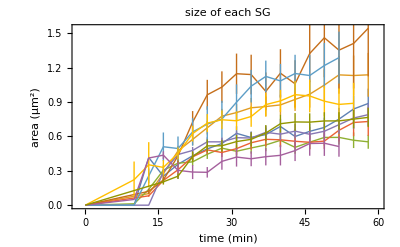

```mathematica
myAreaEachCurves=ErrorListPlot[DeleteCases[#,x_/;x⟦1,1⟧>myFig1eEnd]&/@myAreaEachCurveData,Joined->True,PlotRange->{{-1.5,60},All},PlotStyle->Thin,Frame->True,BaseStyle->{FontFamily->"Helvetica",FontSize->15},PlotLabel->"size of each SG",FrameLabel->{"time (min)","area (µm^2)"},ImageSize->400]
```

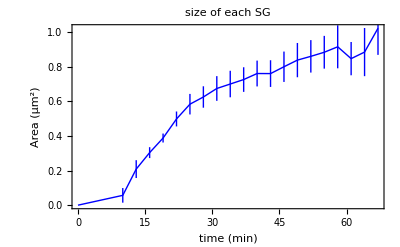

```mathematica
mySGAreaMeanSEM=N@{Mean@#,ErrorBar@((StandardDeviation@#)/(Sqrt@Length@#))}&/@DeleteCases[Flatten/@Thread@myAllBlueAreaMeanShift,x_/;Length@x<2];
mySGAreaMeanSEM=Prepend[{{#⟦1⟧,#⟦2⟧},#⟦3⟧}&/@Flatten/@Thread@{7+3*(Range@Length@mySGAreaMeanSEM),mySGAreaMeanSEM},{{0,0},ErrorBar@0}];
mySGAreaMeanSEM⟦All,1,2⟧*=myPixelSize^2;
mySGAreaMeanSEM⟦All,2,1⟧*=myPixelSize^2;
ErrorListPlot[mySGAreaMeanSEM,Joined->True,PlotRange->All,PlotStyle->Directive[Blue,Thick],Frame->True,BaseStyle->{FontFamily->"Helvetica",FontSize->15},PlotLabel->"size of each SG",FrameLabel->{"time (min)","Area (µm^2)"},ImageSize->400]
```

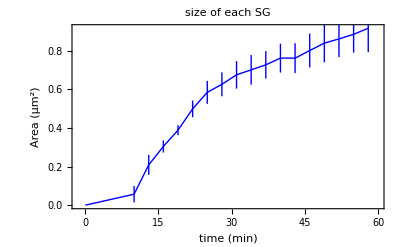

```mathematica
myAreaMeanCurve=ErrorListPlot[DeleteCases[mySGAreaMeanSEM,x_/;x⟦1,1⟧>myFig1eEnd],Joined->True,PlotRange->{{-1.5,60},All},PlotStyle->Directive[Blue,Thick],Frame->True,BaseStyle->{FontFamily->"Helvetica",FontSize->15},PlotLabel->"size of each SG",FrameLabel->{"time (min)","Area (µm^2)"},ImageSize->400]
```

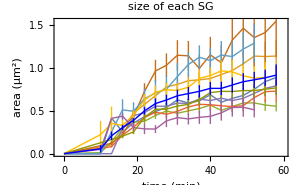

```mathematica
myFig1cSize=Show[myAreaEachCurves,myAreaMeanCurve,Background->None,ImageSize->300]
```

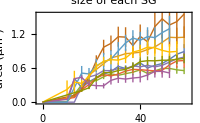

```mathematica
myAreaEachCurvesNew=ErrorListPlot[DeleteCases[#,x_/;x⟦1,1⟧>myFig1eEnd]&/@myAreaEachCurveData,Joined->True,PlotRange->{{-1.5,60},All},PlotStyle->Thin,Frame->True,BaseStyle->{FontFamily->"Helvetica",FontSize->7.5},PlotLabel->"size of each SG",FrameLabel->{"time (min)","area (µm^2)"},ImageSize->200]
```

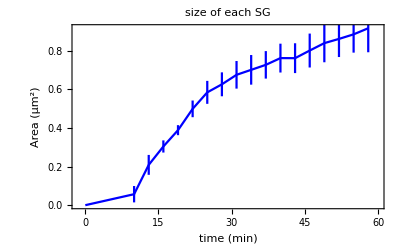

```mathematica
myAreaMeanCurveNew=ErrorListPlot[DeleteCases[mySGAreaMeanSEM,x_/;x⟦1,1⟧>myFig1eEnd],Joined->True,PlotRange->{{-1.5,60},All},PlotStyle->Directive[Blue],Frame->True,BaseStyle->{FontFamily->"Helvetica",FontSize->15},PlotLabel->"size of each SG",FrameLabel->{"time (min)","Area (µm^2)"},ImageSize->400]
```

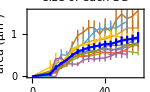

```mathematica
myFig1cSizeNew=Show[myAreaEachCurvesNew,myAreaMeanCurveNew,Background->None,ImageSize->150]
```

#### Total Intensity

```mathematica
myAllBlueIntEach=myAllBlueSpots⟦All,All,All,3,4⟧;
myAllBlueIntEach=myAllBlueIntEach/.{}->{0};
myAllBlueIntMean23=Mean/@#&/@myAllBlueIntEach23;
myAllBlueIntSEM=Table[(StandardDeviation@#)/(Sqrt@Length@#)&/@myAllBlueIntEach⟦i⟧,{i,1,Length@myAllBlueIntEach,1}];
myIdx=Flatten@Position[NumberQ/@#&/@myAllBlueIntSEM//Flatten,False];
yo=Flatten@myAllBlueIntSEM;
yo⟦myIdx⟧=0;
myAllBlueIntSEM=Partition[yo,Length@myAllBlueIntSEM⟦1⟧];
```

```mathematica
myAllBlueIntMeanShift=(ShiftingDataPointsMean[myAllBlueIntMean,myOffset,10,1]);
myAllBlueIntSEMShift=ErrorBar/@#&/@((ShiftingDataPointsMean[myAllBlueIntSEM,myOffset,10,1]));
myIntEachCurveData=Prepend[#,{{0,0},ErrorBar@0}]&/@({{#⟦1⟧,#⟦2⟧},#⟦3⟧}&/@Flatten/@DeleteCases[#,x_/;x⟦2,1⟧=={}]&/@(Thread@{7+3*Range@Length@myAllBlueIntSEMShift⟦1⟧,#}&/@(Thread@#&/@Thread@{myAllBlueIntMeanShift,myAllBlueIntSEMShift})));
```

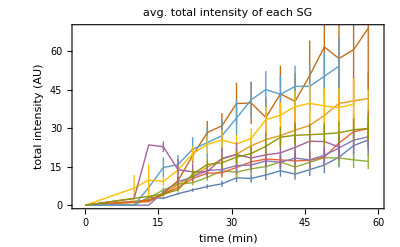

```mathematica
myIntEachCurves=ErrorListPlot[DeleteCases[#,x_/;x⟦1,1⟧>myFig1eEnd]&/@myIntEachCurveData,Joined->True,PlotRange->{{-1.5,60},All},PlotStyle->Thin,Frame->True,BaseStyle->{FontFamily->"Helvetica",FontSize->15},PlotLabel->"avg. total intensity of each SG",FrameLabel->{"time (min)","total intensity (AU)"},ImageSize->400]
```

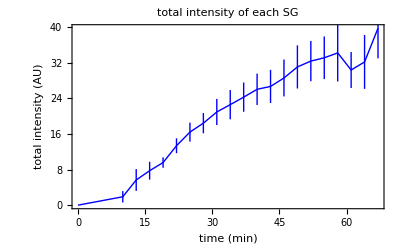

```mathematica
mySGIntMeanSEM=N@{Mean@#,ErrorBar@((StandardDeviation@#)/(Sqrt@Length@#))}&/@DeleteCases[Flatten/@Thread@myAllBlueIntMeanShift,x_/;Length@x<2];
mySGIntMeanSEM=Prepend[{{#⟦1⟧,#⟦2⟧},#⟦3⟧}&/@Flatten/@Thread@{7+3*(Range@Length@mySGIntMeanSEM),mySGIntMeanSEM},{{0,0},ErrorBar@0}];
myIntMeanCurve=ErrorListPlot[mySGIntMeanSEM,Joined->True,PlotRange->{All,All},PlotStyle->Directive[Blue,Thick],Frame->True,BaseStyle->{FontFamily->"Helvetica",FontSize->15},PlotLabel->"total intensity of each SG",FrameLabel->{"time (min)","total intensity (AU)"},ImageSize->400]
```

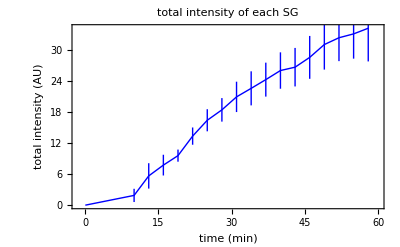

```mathematica
myIntMeanCurve=ErrorListPlot[DeleteCases[mySGIntMeanSEM,x_/;x⟦1,1⟧>myFig1eEnd],Joined->True,PlotRange->{{-1.5,60},All},PlotStyle->Directive[Blue,Thick],Frame->True,BaseStyle->{FontFamily->"Helvetica",FontSize->15},PlotLabel->"total intensity of each SG",FrameLabel->{"time (min)","total intensity (AU)"},ImageSize->400]
```

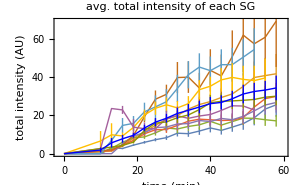

```mathematica
myFig1cInt=Show[myIntEachCurves,myIntMeanCurve,Background->None,ImageSize->300]
```

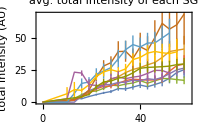

```mathematica
myIntEachCurvesNew=ErrorListPlot[DeleteCases[#,x_/;x⟦1,1⟧>myFig1eEnd]&/@myIntEachCurveData,Joined->True,PlotRange->{{-1.5,60},All},PlotStyle->Thin,Frame->True,BaseStyle->{FontFamily->"Helvetica",FontSize->7.5},PlotLabel->"avg. total intensity of each SG",FrameLabel->{"time (min)","total intensity (AU)"},ImageSize->200]
```

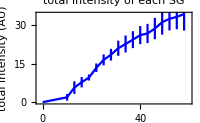

```mathematica
myIntMeanCurveNew=ErrorListPlot[DeleteCases[mySGIntMeanSEM,x_/;x⟦1,1⟧>myFig1eEnd],Joined->True,PlotRange->{{-1.5,60},All},PlotStyle->Directive[Blue],Frame->True,BaseStyle->{FontFamily->"Helvetica",FontSize->7.5},PlotLabel->"total intensity of each SG",FrameLabel->{"time (min)","total intensity (AU)"},ImageSize->200]
```

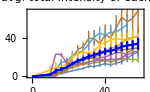

```mathematica
myFig1cIntNew=Show[myIntEachCurvesNew,myIntMeanCurveNew,Background->None,ImageSize->150]
```

## click and track for SGs

```mathematica
{FileNameSetter[Dynamic[mymovie]],Dynamic[mymovie]}
```

{$CellContext`mymovieOpenAll,}

```mathematica
myColMovie=Import[mymovie]//Partition[#,3]&//Transpose;
If[DirectoryQ@(DirectoryName[mymovie]<>"Analysis\\")==False,CreateDirectory@(DirectoryName[mymovie]<>"Analysis\\")];
analysisFolder=DirectoryName[mymovie]<>"Analysis\\"<>StringDrop[StringDelete[mymovie,DirectoryName[mymovie]],-4];
```

### Make Mask

```mathematica
If[FileExistsQ[analysisFolder<>"_avg.tif"]==True,
avgImg=Import[analysisFolder<>"_avg.tif"];,
avgImg=Mean/@myColMovie;
Export[analysisFolder<>"_avg.tif",avgImg]];
If[FileExistsQ[analysisFolder<>"_max.tif"]==True,
maxImg=Import[analysisFolder<>"_max.tif"],
maxImg=ImageApply[Max,#]&/@myColMovie;
Export[analysisFolder<>"_max.tif",maxImg]];
```

```mathematica
Manipulate[maxImg⟦3⟧//ImageAdjust[#,{0,0,1},{threshold1,threshold2}]&,
Button["Choose threshold such that the shape of the cell can be visualized and CLICK",thtemp={threshold1,threshold2}],
{threshold1,0,0.2,0.001},{{threshold2,0.1},0,0.2,0.001}]
```

```mathematica
ImageAdjust[maxImg⟦2⟧,{0,0,1},thtemp]
```

```mathematica
mymask=-Graphics-;
Export[analysisFolder<>"_mask.tif",mymask];
```

```mathematica
(*mymask=ConstantImage[1,ImageDimensions@avgImg⟦1⟧];
Export[analysisFolder<>"_mask.tif",mymask];*)
```

```mathematica
avgFrameN=1;
avgFrameN>>analysisFolder<>"_avgFrameN.dat";myMaxN=Length@myColMovie⟦1⟧-avgFrameN+1;
```

```mathematica
myColMovieRunAv=If[avgFrameN==1,myColMovie,MovingAverage[#,avgFrameN]&/@myColMovie];
```

```mathematica
Manipulate[myColMovieRunAv⟦channel,frame⟧//ImageAdjust[#,{0,0,1},{0,threshold}]&,{channel,Range@Length@myColMovieRunAv},{frame,1,myMaxN,1},{threshold,0,0.3,0.001}]
```

```mathematica
MyThresholding[myColMovieRunAv,analysisFolder]
```

```mathematica
MyBinarization[myColMovieRunAv,analysisFolder]
```

```mathematica
(* trim size > 30 *)
```

```mathematica
ClickAndTrack[myColMovie,myColMovieRunAv,analysisFolder]
```

```mathematica
(*{"IntensityCentroid","Centroid","Area","TotalIntensity","MeanIntensity","MedianIntensity","Elongation","MaxCentroidDistance","BoundingBox","ConvexVertices"}*)
```

```mathematica
myTrackedSGs=Get/@FileNames[FileNameTake@analysisFolder<>"_myTrack_blue*",FileNameDrop[analysisFolder,-1]];
```

```mathematica
myTrackedSGs⟦6,3,3⟧={{109,130},0,0,0,0,0,0,0,0,0}
```

{{109,130},0,0,0,0,0,0,0,0,0}

```mathematica
myTrackedSGsIntTime=Flatten[#,1]&/@Thread@{13+3*Range@Length@#,#}&/@myTrackedSGs⟦All,3;;,3,4⟧;
```

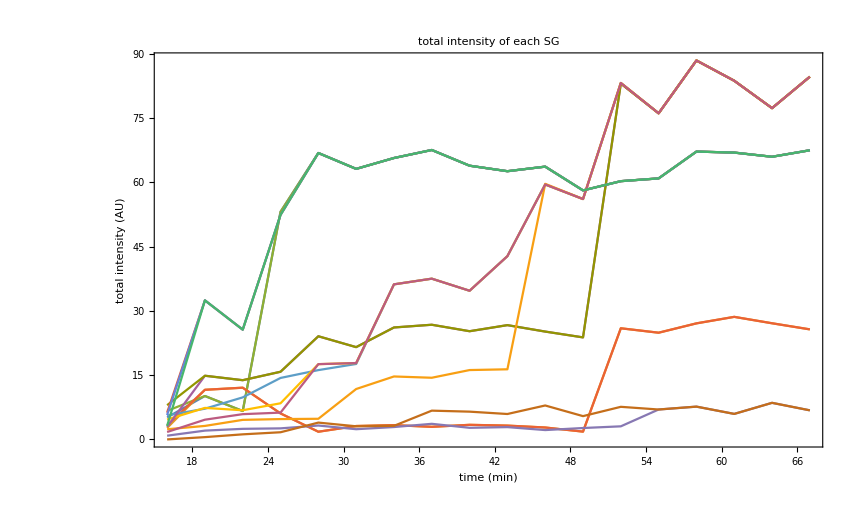

```mathematica
myFig1cEachInt=ListLinePlot[myTrackedSGsIntTime,Frame->True,BaseStyle->{FontFamily->"Helvetica",FontSize->15},PlotLabel->"total intensity of each SG",FrameLabel->{"time (min)","total intensity (AU)"},ImageSize->300]
```

```mathematica
3*(Range@20-1)+10
```

{10,13,16,19,22,25,28,31,34,37,40,43,46,49,52,55,58,61,64,67}

```mathematica
Export[myDirectoryFig<>"myFig1cEachInt.png",myFig1cEachInt,ImageResolution->300];
```

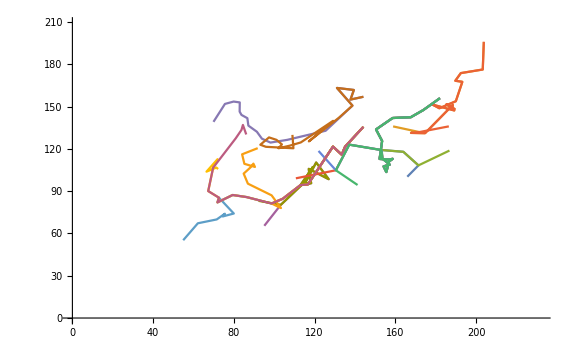

```mathematica
ListLinePlot[myTrackedSGs⟦All,3;;,3,1⟧,PlotRange->{{0,232},{0,209}}]
```

```mathematica
Manipulate[Show[ImageAdjust[myColMovieRunAv⟦3,frame⟧,{0,0,1},thblue],Graphics[{Blue,Disk[#,2]&/@myTrackedSGs⟦All,frame,3,1⟧,Green,Line[#]&/@myTrackedSGs⟦All,3;;frame,3,1⟧}],ImageSize->600],{frame,3,Length@myColMovieRunAv⟦1⟧,1}]
```

```mathematica
myTrackedSGsCenters=Flatten[#,1]&/@Thread@{13+3*Range@Length@#,#}&/@myTrackedSGs⟦All,3;;,3,1⟧;
```

```mathematica
intervTime=2/60;(*min*)
pixelSize=0.13;(*nm/pixel*)
```

```mathematica
p1=Show[ListPointPlot3D[myTrackedSGsCenters,PlotStyle->PointSize@Medium],Graphics3D[{Gray,Line@#}&/@myTrackedSGsCenters],PlotRange->All,BaseStyle->{FontFamily->"Helvetica",FontSize->20},Ticks->{Automatic(*Table[{i,ToString@(intervTime*i)},{i,0,300,150}]*),Table[{i,ToString@Round@((i-50)*pixelSize)},{i,50,200,5/pixelSize}],Table[{i,ToString@Round@((i-50)*pixelSize)},{i,50,200,5/pixelSize}]},BoxRatios->{4,1,1}]
```

-Graphics3D-

```mathematica
myTrackedSGsOutLine=myTrackedSGs⟦All,3;;,3,10⟧;
myTrackedSGsOutLine=Table[Table[Flatten/@Thread@{myTrackedSGsCenters⟦myi,i,1⟧,myTrackedSGsOutLine⟦myi,i⟧},{i,1,Length@myTrackedSGsOutLine⟦myi⟧,1}],{myi,1,Length@myTrackedSGsOutLine,1}];
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[16].

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[0].

```mathematica
tempCent=myTrackedSGsCenters⟦6,1,{2,3}⟧;
```

```mathematica
{#+{-1,-1},#+{-1,1},#+{1,-1},#+{1,1}}&@tempCent
```

```mathematica
myTrackedSGsOutLine⟦6,1⟧=Flatten/@Thread@{myTrackedSGsCenters⟦6,1,1⟧,{{108,129},{108,131},{110,129},{110,131}}}
```

{{16,108,129},{16,108,131},{16,110,129},{16,110,131}}

```mathematica
myIdx=Table[FindCurvePath@#&/@myTrackedSGsOutLine⟦i,All,All,{2,3}⟧,{i,1,Length@myTrackedSGsOutLine,1}];
```

```mathematica
myTrackedSGsOutLineSort=Table[Table[(myTrackedSGsOutLine⟦j,i⟧)⟦myIdx⟦j,i,1⟧⟧,{i,1,Length@myIdx⟦j⟧,1}],{j,1,Length@myIdx,1}];
```

```mathematica
p2=Show@Table[Graphics3D[{Blue,Line@#}&/@myTrackedSGsOutLineSort⟦i⟧,BoxRatios->{4,1,1}],{i,1,Length@myTrackedSGsOutLineSort,1}]
```

-Graphics3D-

```mathematica
mySGformation3D=Show[p1,p2,PlotRange->All,BaseStyle->{FontFamily->"Helvetica",FontSize->20},ViewPoint->myViewPoint,ImageSize->600,ImageResolution-> 300]
```

-Graphics3D-

## Figure 1f and S2 - translation resumption

## pre-processing each data

### Reading in Images

```mathematica
{FileNameSetter[Dynamic[mymovie]],Dynamic[mymovie]}
```

{$CellContext`mymovieOpenAll,}

```mathematica
myColMovie=Import[mymovie]//Partition[#,3]&//Transpose;
If[DirectoryQ@(DirectoryName[mymovie]<>"Analysis\\")==False,CreateDirectory@(DirectoryName[mymovie]<>"Analysis\\")];
analysisFolder=DirectoryName[mymovie]<>"Analysis\\"<>StringDrop[StringDelete[mymovie,DirectoryName[mymovie]],-4];
```

### Creating Transformation Function

```mathematica
dirBeads=DirectoryName[mymovie]<>"Beads";
```

```mathematica
myFiles=FileNames["*.tif",dirBeads];
myBeadsImgs=Table[Import@myFiles⟦i⟧,{i,1,Length[myFiles],1}];
myDims=ImageDimensions@myBeadsImgs⟦1,1⟧;
Manipulate[ColorCombine[{myBeadsImgs⟦data,1⟧,myBeadsImgs⟦data,2⟧,ConstantImage[0,myDims]}]//ImageAdjust,
Button["Choose an image to calculate the transformation function and CLICK",nRefImg=data],
{data,1,Length[myFiles],1}]
```

```mathematica
myRefBeadsRedImg=myBeadsImgs⟦nRefImg,1⟧;
myRefBeadsGreenImg=myBeadsImgs⟦nRefImg,2⟧;
Manipulate[GraphicsRow[{myRefBeadsRedImg//Binarize[#,thresholdRed]&,myRefBeadsGreenImg//Binarize[#,thresholdGreen]&},ImageSize->1000],
Button["Choose thresholds and CLICK",{thRed=thresholdRed,thGreen=thresholdGreen}],
{thresholdRed,0.01,0.5,0.005},{thresholdGreen,0.01,0.5,0.001}]
```

```mathematica
myRedPosGuess=ComponentMeasurements[ImageMultiply[myRefBeadsRedImg,Binarize[myRefBeadsRedImg,thRed]],{"IntensityCentroid"}]⟦All,2,1⟧;
myGreenPosGuess=ComponentMeasurements[ImageMultiply[myRefBeadsGreenImg,Binarize[myRefBeadsGreenImg,thGreen]],{"IntensityCentroid"}]⟦All,2,1⟧;
StringForm["   `` red particles and `` green particles were found.",Length@myRedPosGuess,Length@myGreenPosGuess]
```

21 red particles and 19 green particles were found.

```mathematica
myRedAbsPos=BeadsFitting[myRefBeadsRedImg,myRedPosGuess,7];
myGreenAbsPos=BeadsFitting[myRefBeadsGreenImg,myGreenPosGuess,7];
{myTfFuncError,myTfFunc,distanceRaw,distanceCorrected}=BeadsTransform[myRedAbsPos,myGreenAbsPos,5];
{myTfFuncError,myTfFunc,Insert[{distanceRaw,distanceCorrected}//Transpose,{"Distance Before Correction","Distance After Correction"},1]//TableForm}
```

{0.0818679,TransformationFunction[(0.999136 | -0.00795425 | 5.64993
0.00507735 | 0.999355 | -4.08208
-7.05039×10^-7 | -4.76116×10^-6 | 1.)],Distance Before Correction | Distance After Correction
2.78392 | 0.110419
2.97465 | 0.170599
3.59869 | 0.0595111
3.30613 | 0.0866071
3.43785 | 0.0569559
3.68431 | 0.0425697
4.17258 | 0.110514
4.87581 | 0.00774334
4.70945 | 0.0719716
4.55286 | 0.101788}

```mathematica
Export[DirectoryName[mymovie]<>"TransformationFunction.m",myTfFunc];
```

### Checking Transformation Function

```mathematica
Manipulate[ColorCombine[{myBeadsImgs⟦data,1⟧,myBeadsImgs⟦data,2⟧,ConstantImage[0,myDims]}]//ImageAdjust,
Button["Choose an image to check the transformation function and CLICK",nCheckImg=data],
{data,1,Length[myFiles],1}]
```

```mathematica
myCheckBeadsRedImg=myBeadsImgs⟦nCheckImg,1⟧;
myCheckBeadsGreenImg=myBeadsImgs⟦nCheckImg,2⟧;
Manipulate[GraphicsRow[{myCheckBeadsRedImg//Binarize[#,thresholdRed]&,myCheckBeadsGreenImg//Binarize[#,thresholdGreen]&},ImageSize->1000],
Button["Choose thresholds and CLICK",{thcRed=thresholdRed,thcGreen=thresholdGreen}],
{thresholdRed,0.01,0.5,0.005},{thresholdGreen,0.01,0.5,0.005}]
```

```mathematica
myRedCheckPosGuess=ComponentMeasurements[ImageMultiply[myCheckBeadsRedImg,Binarize[myCheckBeadsRedImg,thcRed]],{"IntensityCentroid"}]⟦All,2,1⟧;
myGreenCheckPosGuess=ComponentMeasurements[ImageMultiply[myCheckBeadsGreenImg,Binarize[myCheckBeadsGreenImg,thcGreen]],{"IntensityCentroid"}]⟦All,2,1⟧;
StringForm["   `` red particles and `` green particles were found.",Length@myRedCheckPosGuess,Length@myGreenCheckPosGuess]
```

12 red particles and 11 green particles were found.

```mathematica
myRedCheckAbsPos=BeadsFitting[myCheckBeadsRedImg,myRedCheckPosGuess,7];
myGreenCheckAbsPos=BeadsFitting[myCheckBeadsGreenImg,myGreenCheckPosGuess,7];
BeadsCheck[myRedCheckAbsPos,myGreenCheckAbsPos,5]
```

Distance Before Correction | Distance After Correction
3.52268 | 0.237004
3.70134 | 0.247094
4.08483 | 0.257585
3.68448 | 0.335007
4.65206 | 0.0545717
4.57442 | 0.204865
4.32711 | 0.0882966
4.46865 | 0.123609

### Reading in Parameters (if parameters exist)

```mathematica
myTfFunc=<<(DirectoryName@mymovie<>"TransformationFunction.m");
```

```mathematica
mymask=Import@(analysisFolder<>"_mask.tif");
```

```mathematica
avgFrameN=<<(analysisFolder<>"_avgFrameN.dat");
myMaxN=Length@myColMovie⟦1⟧-avgFrameN+1;
myColMovieRunAv=If[avgFrameN==1,myColMovie,Table[Image@Mean@(ImageData/@myColMovie⟦i,j;;j+avgFrameN-1⟧),{i,1,2,1},{j,1,myMaxN,1}]];
```

### Make Mask

```mathematica
If[FileExistsQ[analysisFolder<>"_avg.tif"]==True,
avgImg=Import[analysisFolder<>"_avg.tif"];,
avgImg=Mean/@myColMovie;
Export[analysisFolder<>"_avg.tif",avgImg]];
If[FileExistsQ[analysisFolder<>"_max.tif"]==True,
maxImg=Import[analysisFolder<>"_max.tif"],
maxImg=ImageApply[Max,#]&/@myColMovie;
Export[analysisFolder<>"_max.tif",maxImg]];
```

```mathematica
Manipulate[ImageAdjust[maxImg⟦3⟧,{0,0,1},{threshold1,threshold2}],
Button["Choose threshold such that the shape of the cell can be visualized and CLICK",thtemp={threshold1,threshold2}],
{threshold1,0,0.2,0.001},{{threshold2,0.1},0,0.2,0.001}]
```

```mathematica
ImageAdjust[maxImg⟦3⟧,{0,0,1},thtemp]
```

```mathematica
mymask=-Graphics-;
Export[analysisFolder<>"_mask.tif",mymask];
```

```mathematica
(*mymask=Image@ConstantArray[1,ImageDimensions@avgImg];
Export[analysisFolder<>"_mask.tif",mymask];*)
```

### Running z-average

```mathematica
avgFrameN=1;
avgFrameN>>analysisFolder<>"_avgFrameN.dat";myMaxN=Length@myColMovie⟦1⟧-avgFrameN+1;
```

```mathematica
myColMovieRunAv=If[avgFrameN==1,myColMovie,Table[Image@Mean@(ImageData/@myColMovie⟦i,j;;j+avgFrameN-1⟧),{i,1,2,1},{j,1,myMaxN,1}]];
```

```mathematica
Manipulate[ImageAdjust[myColMovieRunAv⟦channel,frame⟧,{0,0,1},{0,threshold}],{channel,Range@Length@myColMovieRunAv},{frame,1,myMaxN,1},{threshold,0,0.3,0.001}]
```

### Setting Threshold

```mathematica
MyThresholding[myColMovieRunAv,analysisFolder]
```

### Setting Threshold for Binarization

```mathematica
MyBinarization[myColMovieRunAv,analysisFolder]
```

### Finding Particles

```mathematica
(* {
track number,
frame number,
{"IntensityCentroid","Centroid","Area","TotalIntensity","MeanIntensity","MedianIntensity","Elongation","MaxCentroidDistance","BoundingBox","ConvexVertices"}
} *)
```

```mathematica
{myRedSpots,myGreenSpots,myBlueSpots}=Table[MyParticleFinder[myColMovieRunAv,i,analysisFolder],{i,1,3,1}];
```

```mathematica
myBlueMasks=myGranuleMaskFinder[myColMovieRunAv,3,analysisFolder];
```

```mathematica
SpotLocationOnCell[myColMovieRunAv,thred,myRedSpots⟦All,All,3,1⟧,thgreen,myGreenSpots⟦All,All,3,1⟧,thblue,myBlueSpots⟦All,All,3,1⟧]
```

```mathematica
myRedSpots>>(analysisFolder<>"_redspots.dat");
myGreenSpots>>(analysisFolder<>"_greenspots.dat");
myBlueSpots>>(analysisFolder<>"_bluespots.dat");
myBlueMasks>>(analysisFolder<>"_bluemasks.dat");
```

### Fitting Particles

```mathematica
(* {
"track number",
"frame number",
{"IntensityCentroid","Centroid","Area","TotalIntensity","MeanIntensity","MedianIntensity","Elongation","MaxCentroidDistance","BoundingBox","ConvexVertices"},
{{x, y},{int, BG},{sigmaX, sigmaY}},
{{x90Conf, y90Conf},{int90Conf, BG90Conf},{sigmaX90Conf,sigmaY90Conf}}
} *)
```

```mathematica
{myRedSpotsFit,myRedCroppedData,myRedCenters}=MyParticleFitter[myColMovie,1,myRedSpots,5,avgFrameN];
{myGreenSpotsFit,myGreenCroppedData,myGreenCenters}=MyParticleFitter[myColMovie,2,myGreenSpots,5,avgFrameN];
```

```mathematica
SpotLocationOnCell[myColMovieRunAv,thred,myRedSpotsFit⟦All,All,4,1⟧,thgreen,myGreenSpotsFit⟦All,All,4,1⟧,thblue,myBlueSpots⟦All,All,3,1⟧]
```

```mathematica
{myRedSpotsFit,myRedCroppedData,myRedCenters}>>(analysisFolder<>"_redspotsFit.dat"); 
{myGreenSpotsFit,myGreenCroppedData,myGreenCenters}>>(analysisFolder<>"_greenspotsFit.dat");
```

### Filtering Outliers from Fitting

```mathematica
myRedSpotsFiltered=FilterFitOutlier[myRedSpotsFit,5,20];
myGreenSpotsFiltered=FilterFitOutlier[myGreenSpotsFit,5,20];
```

```mathematica
SpotLocationOnCell[myColMovieRunAv,thred,myRedSpotsFiltered⟦All,All,4,1⟧,thgreen,myGreenSpotsFiltered⟦All,All,4,1⟧,thblue,myBlueSpots⟦All,All,3,1⟧]
```

```mathematica
myGreenSpotsFiltered>>(analysisFolder<>"_greenspotsFiltered.dat")
```

## Combining results

#### Stress

```mathematica
myDirectory=DirectoryName@mymovie;
```

```mathematica
myAllBlueSpots=Get/@FileNames["*bluespots*",myDirectory];
myAllGreenSpots=Get/@FileNames["*greenspotsFiltered*",myDirectory];
```

```mathematica
myAllBlueNum=Length/@#&/@myAllBlueSpots;
myAllGreenNum=Length/@#&/@myAllGreenSpots;
```

```mathematica
Table[ListLinePlot[{myAllBlueNum⟦i⟧,myAllGreenNum⟦i⟧},PlotStyle->{Blue,Green,Darker@Yellow}],{i,1,Length@myAllBlueNum,1}]
```

```mathematica
myAllBlueNumPre=myAllBlueNum;
myAllGreenNumPre=myAllGreenNum;
```

#### recovery

```mathematica
myDirectory="directoryName";
```

```mathematica
myAllBlueSpots=Get/@FileNames["*bluespots*",myDirectory];
myAllGreenSpots=Get/@FileNames["*greenspotsFiltered*",myDirectory];
```

```mathematica
myAllBlueNum=Length/@#&/@myAllBlueSpots;
myAllGreenNum=Length/@#&/@myAllGreenSpots;
```

```mathematica
Table[ListLinePlot[{myAllBlueNum⟦i⟧,myAllGreenNum⟦i⟧},PlotStyle->{Blue,Green,Darker@Yellow}],{i,1,Length@myAllBlueNum,1}]
```

```mathematica
myAllBlueNumPost=myAllBlueNum;
myAllGreenNumPost=myAllGreenNum;
```

#### Combine

```mathematica
preBlue=Thread@{7+3*Range@Length@#,#}&/@myAllBlueNumPre;
preGreen=Thread@{7+3*Range@Length@#,#}&/@myAllGreenNumPre;
```

```mathematica
postBlue=Thread@{67+3*Range@Length@#,#}&/@myAllBlueNumPost;
postGreen=Thread@{67+3*Range@Length@#,#}&/@myAllGreenNumPost;
```

```mathematica
Table[ListLinePlot[{preBlue⟦i⟧,preGreen⟦i⟧,postBlue⟦i⟧,postGreen⟦i⟧},PlotRange->All,PlotStyle->{Blue,Darker@Yellow,Green,Blue,Darker@Yellow,Green},Frame->True,BaseStyle->{FontFamily->"Helvetica",FontSize->15},PlotLabel->myTitles⟦i⟧,FrameLabel->{"time (min)","number of spots"},ImageSize->400],{i,1,Length@preBlue,1}]
```

#### Making fig1F

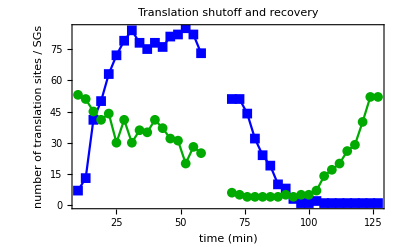

```mathematica
ListLinePlot[{preBlue⟦2⟧,preGreen⟦2⟧,postBlue⟦2⟧,postGreen⟦2⟧},PlotRange->All,PlotMarkers->{{"■",10},{"●",10},{"■",10},{"●",10}},PlotStyle->{Blue,Darker@Green,Blue,Darker@Green,Darker@Yellow,Green},Frame->True,BaseStyle->{FontFamily->"Helvetica",FontSize->15},PlotLabel->"Translation shutoff and recovery",FrameLabel->{"time (min)","number of translation sites / SGs"},ImageSize->400]
```

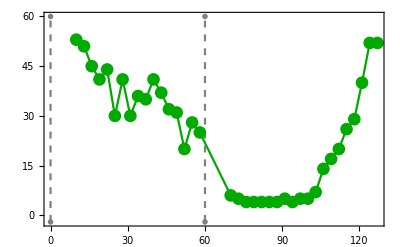

```mathematica
plot1=ListLinePlot[{Flatten[{preGreen⟦2⟧,postGreen⟦2⟧},1],{{0,-2},{0,60}},{{60,-2},{60,60}}},PlotRange->{Automatic,{-2,60
}},PlotMarkers->{{"●", 13},{"",0},{"",0}},PlotStyle->{Darker@Green,{Dashed,Gray},{Dashed,Gray}},ImagePadding->30,Frame->{True,True,True,False},BaseStyle->{FontFamily->"Helvetica",FontSize->15},FrameStyle->{Automatic,Darker@Green,Automatic,Automatic},ImageSize->400]
```

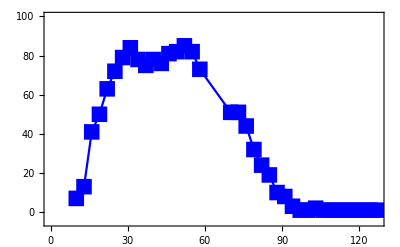

```mathematica
plot2=ListLinePlot[Flatten[{preBlue⟦2⟧,postBlue⟦2⟧},1],PlotRange->{Automatic,{-5,100}},PlotMarkers->{"■", 16},PlotStyle->Blue,ImagePadding->30,Axes->False,Frame->{False,False,False,True},BaseStyle->{FontFamily->"Helvetica",FontSize->15},FrameTicks->All,FrameStyle->{Automatic,Automatic,Automatic,Blue},ImageSize->400]
```

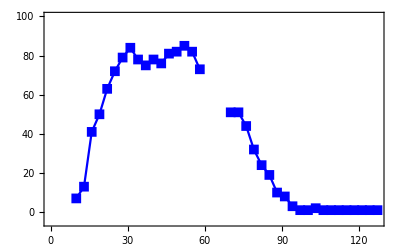

```mathematica
plot2=ListLinePlot[{preBlue⟦2⟧,postBlue⟦2⟧},PlotRange->{Automatic,{-5,100}},PlotMarkers->{"■", 10},PlotStyle->Blue,ImagePadding->30,Axes->False,Frame->{False,False,False,True},BaseStyle->{FontFamily->"Helvetica",FontSize->15},FrameTicks->All,FrameStyle->{Automatic,Automatic,Automatic,Blue},ImageSize->400]
```

```mathematica
recoveryPlot=Overlay@{plot1,plot2}
```

-Graphics--Graphics-

#### Making sup movie

```mathematica
analysisFolder="FolderName";
```

```mathematica
mypremovie=Transpose@Partition[Import@"moviename",3];
```

```mathematica
mypostmovie=Transpose@Partition[Import@"moviename",3];
```

```mathematica
myblackImg=ConstantImage[0,ImageDimensions@mypremovie⟦1,1⟧];
Manipulate[ColorCombine[{myblackImg,ImageAdjust[mypremovie⟦2,i⟧,{0,0,1},{greenlo,greenhi}],ImageAdjust[mypremovie⟦3,i⟧,{0,0,1},{bluelo,bluehi}]}],{i,1,Length@mypremovie⟦1⟧,1},{greenlo,0,1,0.001},{greenhi,0,1,0.001},{bluelo,0,1,0.001},{bluehi,0,1,0.001}]
```

```mathematica
greenth={0.016,0.127};blueth={0.018,0.053};
```

```mathematica
Manipulate[ColorCombine[{myblackImg,ImageAdjust[mypostmovie⟦2,i⟧,{0,0,1},greenth],ImageAdjust[mypostmovie⟦3,i⟧,{0,0,1},blueth]}],{i,1,Length@mypostmovie⟦1⟧,1}]
```

```mathematica
Length@mypremovie⟦1⟧
```

17

```mathematica
Length@mypostmovie⟦1⟧
```

20

```mathematica
myPreColMov=Table[ColorCombine[{myblackImg,ImageAdjust[mypremovie⟦2,i⟧,{0,0,1},greenth],ImageAdjust[mypremovie⟦3,i⟧,{0,0,1},blueth]}],{i,1,Length@mypremovie⟦1⟧,1}];
```

```mathematica
myPostColMov=Table[ColorCombine[{myblackImg,ImageAdjust[mypostmovie⟦2,i⟧,{0,0,1},greenth],ImageAdjust[mypostmovie⟦3,i⟧,{0,0,1},blueth]}],{i,1,Length@mypostmovie⟦1⟧,1}];
```

```mathematica
whitetimeStamp1=Table[Graphics[Text[Style[ToString@((i-1)*3+10)<>" min post-stress",Large,Bold,White],{380,470}]],{i,1,Length@mypremovie⟦1⟧,1}];
```

```mathematica
whitetimeStamp2=Table[Graphics[{Text[Style[ToString@((i-1)*3+70)<>" min post-stress",Medium,Bold,White],{430,440}],Text[Style[ToString@((i-1)*3+10)<>" min post-wash",Large,Bold,White],{380,470}]}],{i,1,Length@mypostmovie⟦1⟧,1}];
```

```mathematica
scaleBar=Graphics[{Thick,White,Line[{{400,30},{400+10000/130,30}}],Text[Style["10 µm",Large,Bold,White],{400+5000/130,50}]}];
```

```mathematica
Manipulate[Show[myPreColMov⟦i⟧,whitetimeStamp1⟦i⟧,scaleBar],{i,1,Length@myPreColMov,1}]
```

```mathematica
Manipulate[Show[myPostColMov⟦i⟧,whitetimeStamp2⟦i⟧,whitetimeStamp3⟦i⟧,scaleBar],{i,1,Length@myPreColMov,1}]
```

```mathematica
yo=Flatten@{myPreColMov,myPostColMov};
yoo=Flatten@{whitetimeStamp1,whitetimeStamp2};
```

```mathematica
Length/@{yo,yoo}
```

{37,37}

```mathematica
Manipulate[Show[yo⟦i⟧,yoo⟦i⟧,scaleBar],{i,1,Length@yo,1}]
```

```mathematica
supMovieFig1F=Table[Show[yo⟦i⟧,yoo⟦i⟧,scaleBar],{i,1,Length@yo,1}];
```

## Figure 2c, 2d, 2e, 3a, and 3b - RNA interaction w/ SGs or PBs

## pre-processing each data

### Reading in Images

```mathematica
{FileNameSetter[Dynamic[mymovie]],Dynamic[mymovie]}
```

{$CellContext`mymovieOpenAll,}

```mathematica
myColMovie=Import[mymovie]//Partition[#,3]&//Transpose;
If[DirectoryQ@(DirectoryName[mymovie]<>"Analysis\\")==False,CreateDirectory@(DirectoryName[mymovie]<>"Analysis\\")];
analysisFolder=DirectoryName[mymovie]<>"Analysis\\"<>StringDrop[StringDelete[mymovie,DirectoryName[mymovie]],-4];
```

### Make Masks

```mathematica
tempImg=myColMovie[[3,1;;All]]//Mean;
Manipulate[tempImg//ImageAdjust[#,{0,0,1},{threshold1a,threshold2a}]&,
Button["Choose threshold such that the shape of the cell can be visualized and CLICK",thtemp={threshold1a,threshold2a}],
{threshold1a,0,0.5,0.001},{threshold2a,0,0.5,0.001}]
```

```mathematica
ImageAdjust[tempImg,{0,0,1},thtemp]
```

```mathematica
mymask=-Graphics-;
Export[analysisFolder<>"_mask.tif",mymask];
```

### Running z-average

```mathematica
avgFrameN=1;
avgFrameN>>analysisFolder<>"_avgFrameN.dat";myMaxN=Length@myColMovie⟦1⟧-avgFrameN+1;
myColMovieRunAv=If[avgFrameN==1,myColMovie,MovingAverage[#,avgFrameN]&/@myColMovie];
```

### Setting Threshold

```mathematica
MyThresholding[myColMovieRunAv,analysisFolder]
```

### Setting Threshold for Binarization

```mathematica
MyBinarization[myColMovieRunAv,analysisFolder]
```

## Batch process

```mathematica
myDirectory=DirectoryName@mymovie;
```

```mathematica
myFiles=FileNames["*.tif",myDirectory];
Table[
(* reading in a movie *)
mymovie=myFiles⟦j⟧;
myColMovie=Import[mymovie]//Partition[#,3]&//Transpose;
analysisFolder=DirectoryName[mymovie]<>"Analysis\\"<>StringDrop[StringDelete[mymovie,DirectoryName[mymovie]],-4];
(* reading in general parameters *)
myTfFunc=Import[DirectoryName[mymovie]<>"TransformationFunction.m"];
myTfFuncInv=InverseFunction@myTfFunc;
avgFrameN=<<(analysisFolder<>"_avgFrameN.dat");
myMaxN=Length[myColMovie⟦1⟧]-avgFrameN+1;
myColMovieRunAv=If[avgFrameN==1,myColMovie,MovingAverage[#,avgFrameN]&/@myColMovie];
mymask=Import@(analysisFolder<>"_mask.tif");
(* reading in red parameters *)
thred=<<(analysisFolder<>"_thred.dat");
{mymaxred,thred2,bandpassred,dotsizered}=<<(analysisFolder<>"_thred2.dat");
(* finding red particles and masks *)
redRunAvp=Table[FindParticlesWeighted[myColMovieRunAv⟦1,i⟧//ImageAdjust[#,{0,0,1},thred]&,bandpassred,mymaxred,thred2,mymask,dotsizered],{i,1,myMaxN,1}];
redComponentMask=Table[ImageTransformation[FindParticlesWeightedMask[myColMovieRunAv⟦1,i⟧//ImageAdjust[#,{0,0,1},thred]&,bandpassred,mymaxred,thred2,mymask,dotsizered],myTfFuncInv,DataRange->Full],{i,1,myMaxN,1}];
redRunAvp>>analysisFolder<>"_redspots.dat";
Export[analysisFolder<>"_redComponentMask.tif",redComponentMask];
(* reading in green parameters *)
thgreen=<<(analysisFolder<>"_thgreen.dat");
{mymaxgreen,thgreen2,bandpassgreen,dotsizegreen}=<<(analysisFolder<>"_thgreen2.dat");
(* finding green particles and masks *)
greenRunAvp=Table[FindParticlesWeighted[myColMovieRunAv⟦2,i⟧//ImageAdjust[#,{0,0,1},thgreen]&,bandpassgreen,mymaxgreen,thgreen2,mymask,dotsizegreen],{i,1,myMaxN,1}];
greenComponentMask=Table[FindParticlesWeightedMask[myColMovieRunAv⟦2,i⟧//ImageAdjust[#,{0,0,1},thgreen]&,bandpassgreen,mymaxgreen,thgreen2,mymask,dotsizegreen],{i,1,myMaxN,1}];
greenRunAvp>>analysisFolder<>"_greenspots.dat";Export[analysisFolder<>"_greenComponentMask.tif",greenComponentMask];
(* linking green particles *)
maxJumpDistGreen=10;
mygreentracks=LinkTracks2[greenRunAvp,maxJumpDistGreen];
mygreentracks>>analysisFolder<>"_greentracks.dat";
(* reading in blue parameters *)
thblue=<<(analysisFolder<>"_thblue.dat");
{mymaxblue,thblue2,bandpassblue,dotsizeblue}=<<(analysisFolder<>"_thblue2.dat");
(* finding blue particles and masks *)
blueRunAvp=Table[FindParticlesWeighted[myColMovieRunAv⟦3,i⟧//ImageAdjust[#,{0,0,1},thblue]&,bandpassblue,mymaxblue,thblue2,mymask,dotsizeblue],{i,1,myMaxN,1}];
blueComponentMask=Table[FindParticlesWeightedMask[myColMovieRunAv⟦3,i⟧//ImageAdjust[#,{0,0,1},thblue]&,bandpassblue,mymaxblue,thblue2,mymask,dotsizeblue],{i,1,myMaxN,1}];
blueRunAvp>>analysisFolder<>"_bluespots.dat";Export[analysisFolder<>"_blueComponentMask.tif",blueComponentMask];
(* linking blue particles *)
maxJumpDistBlue=15;
mybluetracks=LinkTracks2[blueRunAvp,maxJumpDistBlue];
mybluetracks>>analysisFolder<>"_bluetracks.dat";
(* overlapping analysis *)
shortestTrackBlue=100;
shortestTrackGreen=100;
listHead={"TrackN_Blue","FrameN","I_Red","I_Green","I_Blue","Count_Red","Count_Green","Count_Blue","TotCount","Area","X_Centroid","Y_Centroid","Box_X1","Box_Y1","Box_X2","BoxY2","Elongation","MaxCentroidDistance"};

myColMask=ColorCombine/@Thread@{redComponentMask,greenComponentMask,blueComponentMask};
mylongbluetracks=mybluetracks//DeleteCases[#,x_/;Length[x]<shortestTrackBlue]&;
myBlueSpots=mylongbluetracks//Flatten//Partition[#,4]&//SplitBy[#,First]&;
myout=Table[
myts=myBlueSpots⟦myTrackN⟧⟦All,2⟧;
Table[{myTrackN,myts⟦k⟧,ComponentMeasurements[myColMask⟦myts⟦k⟧⟧,{"Mean","Total","Count","Area","Centroid","BoundingBox","Elongation","MaxCentroidDistance"},EuclideanDistance[#Centroid,myBlueSpots⟦myTrackN,k,3;;4⟧]<#MaxCentroidDistance&,CornerNeighbors->False]},{k,1,Length[myts],1}],
{myTrackN,1,Length[myBlueSpots],1}]//Flatten[#,1]&;
myNearestSpots=Table[
myt=Position[myBlueSpots⟦myout⟦k,1⟧⟧,myout⟦k,2⟧]⟦1,1⟧;
Position[myout⟦k⟧,Nearest[myout⟦k,3,1;;All,2,5⟧,myBlueSpots⟦myout⟦k,1⟧,myt,3;;4⟧]⟦1⟧]⟦1,2⟧,{k,1,Length[myout],1}];
myout2=Table[{myout⟦k,1⟧,myout⟦k,2⟧,{myout[[k,3,myNearestSpots⟦k⟧]]}},{k,1,Length[myout],1}];
blueComponentAnalysis=Prepend[Table[{myout2⟦k,1;;2⟧,If[myout2⟦k,3⟧=={},Table["",{k,1,Length[listHead]-2,1}],myout2⟦k,3,1,2⟧]}//Flatten,{k,1,Length[myout2],1}],listHead];
blueComponentAnalysis>>analysisFolder<>"_blueComponentAnalysis.dat";

mylonggreentracks=mygreentracks//DeleteCases[#,x_/;Length[x]<shortestTrackGreen]&;
myGreenSpots=mylonggreentracks//Flatten//Partition[#,4]&//SplitBy[#,First]&;
myoutg=Table[
mytsg=myGreenSpots⟦myTrackN⟧⟦All,2⟧;
Table[{myTrackN,mytsg⟦k⟧,ComponentMeasurements[myColMask⟦mytsg⟦k⟧⟧,{"Mean","Total","Count","Area","Centroid","BoundingBox","Elongation","MaxCentroidDistance"},EuclideanDistance[#Centroid,myGreenSpots⟦myTrackN,k,3;;4⟧]<#MaxCentroidDistance&,CornerNeighbors->False]},{k,1,Length[mytsg],1}],
{myTrackN,1,Length[myGreenSpots],1}]//Flatten[#,1]&;
myNearestSpotsg=Table[
mytg=Position[myGreenSpots⟦myoutg⟦k,1⟧⟧,myoutg⟦k,2⟧]⟦1,1⟧;
Position[myoutg⟦k⟧,Nearest[myoutg⟦k,3,1;;All,2,5⟧,myGreenSpots⟦myoutg⟦k,1⟧,mytg,3;;4⟧]⟦1⟧]⟦1,2⟧,{k,1,Length[myoutg],1}];
myout2g=Table[{myoutg⟦k,1⟧,myoutg⟦k,2⟧,{myoutg[[k,3,myNearestSpotsg⟦k⟧]]}},{k,1,Length[myoutg],1}];
greenComponentAnalysis=Prepend[Table[{myout2g⟦k,1;;2⟧,If[myout2g⟦k,3⟧=={},Table["",{k,1,Length[listHead]-2,1}],myout2g⟦k,3,1,2⟧]}//Flatten,{k,1,Length[myout2g],1}],listHead];
greenComponentAnalysis>>analysisFolder<>"_greenComponentAnalysis.dat";

,{j,1,Length@myFiles,1}];
```

## Combining data for Fig 2 - mRNA interaction w/ SGs

```mathematica
myP300sNoPB=FileNames["*p300_SGTR*blueComponentAnalysis.dat",myDirectory];
myKDM5Bst=FileNames["*KDM5B_SGTR*blueComponentAnalysis.dat",myDirectory];
myP300sPB=FileNames["*p300_SGPB*blueComponentAnalysis.dat",myDirectory];
myKDM5Bs=FileNames["*KDM5B_SGPB*blueComponentAnalysis.dat",myDirectory];
myH2Bs=FileNames[{"*H2B_SGTR*blueComponentAnalysis.dat","*H2B_SGPB*blueComponentAnalysis.dat"},myDirectory];
```

```mathematica
myns=(IntegerPart/@Table[ⅇ^(.09 t),{t,1,50,1}]//Union)[[3;;All]]
maxt=245;
dt=2;
```

{3,4,5,6,7,8,9,10,11,12,13,14,16,17,19,21,23,25,27,30,33,36,40,43,47,52,57,62,68,75,82,90}

```mathematica
myr1s={0,30,86,139};
myr2s={29,85,138,10000};
```

```mathematica
myP300NoPB=RNAInteractionAnalysis[myP300sNoPB,3 (*Channel*),2 (*ChannelB*),dt,maxt,myns,myr1s,myr2s];
```

```mathematica
myKDM5BNoPB=RNAInteractionAnalysis[myKDM5Bst,3 (*Channel*),2 (*ChannelB*),dt,maxt,myns,myr1s,myr2s];
```

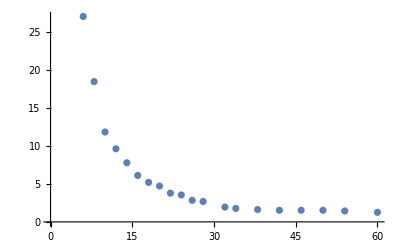

```mathematica
myKDM5BNoPB[[3,2,1;;20,1]]//ListPlot
```

```mathematica
myKDM5BNoPB[[3,2,1;;20,1]]//ListPlot
```

-Graphics-

```mathematica
myKDM5BNoPB//Length
```

9

```mathematica
Dimensions/@myKDM5BNoPB[[9]]
```

{{31},{26},{65},{38},{26},{33},{26},{45},{36}}

```mathematica
Total@Flatten@(Dimensions/@myKDM5BNoPB[[9]])
```

326

```mathematica
Dimensions/@myP300NoPB[[9]]
```

{{48},{21},{45},{38},{28},{39},{27},{33},{38},{19}}

```mathematica
Total@Flatten@(Dimensions/@myP300NoPB[[9]])
```

336

```mathematica
myf1=NonlinearModelFit[myKDM5BNoPB[[3,2,1;;20,1]],A ⅇ^(-t/t1)+B ⅇ^(-t/t2),{{A,50},{B,50},{t1,1},{t2,200}},t]
```

FittedModel[99.3305 ⅇ^(-0.264789 t)+8.4784 ⅇ^(-0.0394728 t)]

```mathematica
myf2=NonlinearModelFit[myP300NoPB[[3,2,1;;20,1]],A ⅇ^(-t/t1)+B ⅇ^(-t/t2),{{A,50},{B,50},{t1,1},{t2,200}},t]
```

FittedModel[90.1673 ⅇ^(-0.291969 t)+12.3825 ⅇ^(-0.059943 t)]

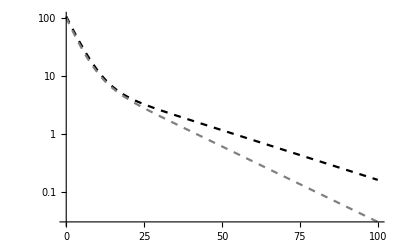

```mathematica
p0=LogPlot[{myf1[t],myf2[t]},{t,0,100},PlotStyle->{{Black,Dashed},{Gray,Dashed}}]
```

```mathematica
myKDM5BNoPB[[3,2]][[1;;22,1]]
```

{{6,26.9954},{8,18.4346},{10,11.8154},{12,9.60686},{14,7.76947},{16,6.1097},{18,5.19323},{20,4.71344},{22,3.77623},{24,3.53944},{26,2.83318},{28,2.68502},{32,1.94732},{34,1.76541},{38,1.61918},{42,1.5292},{46,1.5292},{50,1.5292},{54,1.43921},{60,1.25311},{66,0.870442},{72,0.814201}}

```mathematica
myinset1=myKDM5BNoPB[[3,2]][[1;;25,1]]//ListLogPlot[#,Frame->True,ImageSize->155,AspectRatio->1.5,PlotRange->{{0,115},{0.3,60}},PlotMarkers->{Graphics`PlotMarkers[]⟦1,1⟧,10},PlotStyle->Black,Joined->True,FrameTicks->{{Automatic,None},{{0,50,100},None}},BaseStyle->{FontFamily->"Arial",FontSize->14}]&;
```

```mathematica
myinset2=myP300NoPB[[3,2]][[1;;22,1]]//ListLogPlot[#,Frame->True,ImageSize->155,AspectRatio->1.5,PlotRange->{{0,115},{0.3,60}},PlotMarkers->{Graphics`PlotMarkers[]⟦1,1⟧,10},PlotStyle->Black,Joined->True,FrameTicks->{{Automatic,None},{{0,50,100},None}},BaseStyle->{FontFamily->"Arial",FontSize->14}]&;
```

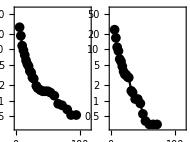

```mathematica
ins=GraphicsRow[{myinset1,myinset2},ImageSize->380/2,Spacings->0]
```

```mathematica
p1={myKDM5BNoPB[[3,2]][[1;;22]]}//ErrorListLogPlot[#,PlotRange->{{0,100},{3,200.5}},Frame->True,ImageSize->250,AspectRatio->1.5,PlotStyle->{Lighter[Black,0.5],Lighter[Gray,0.5]},BaseStyle->{FontFamily->"Arial",FontSize->14}]&;
p2={myKDM5BNoPB[[3,2]][[1;;22]]}//ErrorListLogPlot[#,PlotRange->{{0,100},{3,200.5}},Frame->True,ImageSize->250,AspectRatio->1.5,PlotMarkers->{{Graphics`PlotMarkers[]⟦1,1⟧,15},{Graphics`PlotMarkers[]⟦2,1⟧,20}},PlotStyle->{Black,Gray}]&;
out4a=Show[p1,p2,p0,Epilog->Inset[Show[myinset1,ImageSize->380/3],{140,4.}],PlotRange->{{0,210},{1,5.3}},BaseStyle->{FontFamily->"Arial",FontSize->14}]
```

-Graphics-

```mathematica
p1={myP300NoPB[[3,2]][[1;;22]]}//ErrorListLogPlot[#,PlotRange->{{0,100},{3,200.5}},Frame->True,ImageSize->250,AspectRatio->1.5,PlotStyle->{Lighter[Black,0.5],Lighter[Black,0.5]},BaseStyle->{FontFamily->"Arial",FontSize->14}]&;
p2={myP300NoPB[[3,2]][[1;;22]]}//ErrorListLogPlot[#,PlotRange->{{0,100},{3,200.5}},Frame->True,ImageSize->250,AspectRatio->1.5,PlotMarkers->{{Graphics`PlotMarkers[]⟦1,1⟧,15},{Graphics`PlotMarkers[]⟦2,1⟧,20}},PlotStyle->{Black,Black}]&;
out4b=Show[p1,p2,p0,Epilog->Inset[Show[myinset2,ImageSize->380/3],{140,4.}],PlotRange->{{0,210},{1,5.3}},BaseStyle->{FontFamily->"Arial",FontSize->14}]
```

-Graphics-

```mathematica
myinset1=myKDM5BNoPB[[3,2]][[1;;25,1]]//ListLogPlot[#,Frame->True,ImageSize->155,AspectRatio->1.5,PlotRange->{{0,115},{0.3,60}},PlotMarkers->{Graphics`PlotMarkers[]⟦1,1⟧,10},PlotStyle->Black,Joined->True,FrameTicks->{{Automatic,None},{{0,50,100},None}},BaseStyle->{FontFamily->"Arial",FontSize->14}]&;
```

```mathematica
myinset2=myP300NoPB[[3,2]][[1;;22,1]]//ListLogPlot[#,Frame->True,ImageSize->155,AspectRatio->1.5,PlotRange->{{0,115},{0.3,60}},PlotMarkers->{Graphics`PlotMarkers[]⟦2,1⟧,12},PlotStyle->Gray,Joined->True,FrameTicks->{{Automatic,None},{{0,50,100},None}},BaseStyle->{FontFamily->"Arial",FontSize->14}]&;
```

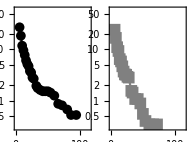

```mathematica
ins=GraphicsRow[{myinset1,myinset2},ImageSize->380/2,Spacings->0]
```

```mathematica
p1={myKDM5BNoPB[[3,2]][[1;;22]],myP300NoPB[[3,2]][[1;;22]]}//ErrorListLogPlot[#,PlotRange->{{0,100},{3,200.5}},Frame->True,ImageSize->250,AspectRatio->1.5,PlotStyle->{Lighter[Black,0.5],Lighter[Gray,0.5]},BaseStyle->{FontFamily->"Arial",FontSize->14}]&;
p2={myKDM5BNoPB[[3,2]][[1;;22]],myP300NoPB[[3,2]][[1;;22]]}//ErrorListLogPlot[#,PlotRange->{{0,100},{3,200.5}},Frame->True,ImageSize->250,AspectRatio->1.5,PlotMarkers->{{Graphics`PlotMarkers[]⟦1,1⟧,15},{Graphics`PlotMarkers[]⟦2,1⟧,20}},PlotStyle->{Black,Gray}]&;
out4=Show[p1,p2,p0,Epilog->Inset[ins,{114,4.2}],PlotRange->{{0,210},{1,5.3}},BaseStyle->{FontFamily->"Arial",FontSize->14}]
```

-Graphics-

```mathematica
myns=(IntegerPart/@Table[ⅇ^(.09 t),{t,1,63,1}]//Union)[[3;;All]]
maxt=245;
dt=2;
```

{3,4,5,6,7,8,9,10,11,12,13,14,16,17,19,21,23,25,27,30,33,36,40,43,47,52,57,62,68,75,82,90,98,107,117,129,141,154,169,184,202,221,242,265,290}

```mathematica
myns//Length
```

45

```mathematica
myr1s={0,30,86,139};
myr2s={29,85,138,10000};
```

```mathematica
myP300AllPB=RNAInteractionAnalysis[myP300sPB,3,dt,maxt,myns,myr1s,myr2s];
```

```mathematica
h2bAll=RNAInteractionAnalysis[myH2Bs,3,dt,maxt,myns,myr1s,myr2s];
```

```mathematica
kdm5bAll=RNAInteractionAnalysis[myKDM5Bs,3,dt,maxt,myns,myr1s,myr2s];
```

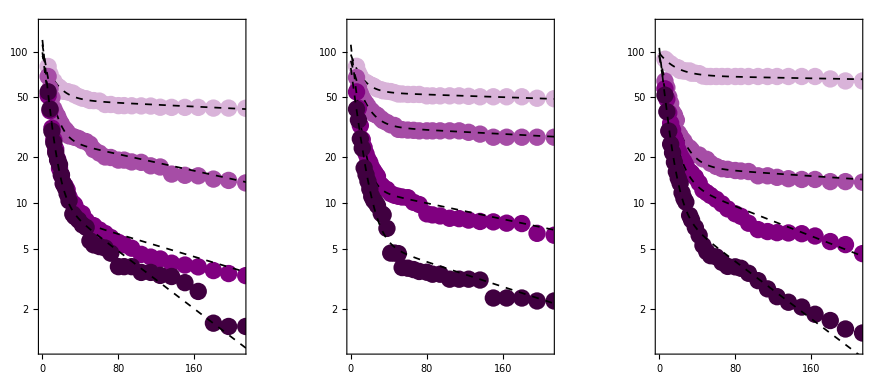

```mathematica
sp=51;
out1b=GraphicsRow[{Show[h2bAll[[15]],ImageSize->250],Show[kdm5bAll[[15]],ImageSize->250],Show[myP300AllPB[[15]],ImageSize->250]},Spacings->{{0,sp,sp},0},Frame->True,FrameStyle->White]
```

```mathematica
h2bAll[[9,1;;All,2,All,1]]//Export["C:\\Users\\tim_s\\OneDrive - Colostate\\Stasevich Lab\\Our papers\\StressGranules\\Fig2cData.xls",#]&
```

C:\Users\tim_s\OneDrive - Colostate\Stasevich Lab\Our papers\StressGranules\Fig2cData.xls

```mathematica
kdm5bAll[[9,1;;All,2,All,1]]//Export["C:\\Users\\tim_s\\OneDrive - Colostate\\Stasevich Lab\\Our papers\\StressGranules\\Fig2cKDM5BData.xls",#]&
```

C:\Users\tim_s\OneDrive - Colostate\Stasevich Lab\Our papers\StressGranules\Fig2cKDM5BData.xls

```mathematica
myP300AllPB[[9,1;;All,2,All,1]]//Export["C:\\Users\\tim_s\\OneDrive - Colostate\\Stasevich Lab\\Our papers\\StressGranules\\Fig2cP300Data.xls",#]&
```

C:\Users\tim_s\OneDrive - Colostate\Stasevich Lab\Our papers\StressGranules\Fig2cP300Data.xls

```mathematica
sp=-10;
out1c=GraphicsRow[{out2,Show[out4a,ImageSize->250],Show[out4b,ImageSize->250]},Spacings->{{10,55,-45},0},Frame->True,FrameStyle->White]
```

-Graphics-

```mathematica
outAg=GraphicsColumn[{out1b,out1c}]
```

-Graphics-

```mathematica
mycolors=Reverse@{Darker[Purple,0.5],Purple,Lighter[Purple,0.3],Lighter[Purple,0.7]}
```

{RGBColor[0.85, 0.7, 0.85],RGBColor[0.65, 0.3, 0.65],RGBColor[0.5, 0, 0.5],RGBColor[0.25, 0., 0.25]}

```mathematica
myar=.37;is=150;
myi=5;
test={({{5.4,0},0}+{{-#[[1,1,1]],#[[1,1,2]]},#[[1,2]]})&/@Reverse[myP300AllPB[[myi,2]]],({{5.4+4.4,0},0}+{{-#[[1,1,1]],#[[1,1,2]]},#[[1,2]]})&/@Reverse[kdm5bAll[[myi,2]]],({{5.4+8.8,0},0}+{{-#[[1,1,1]],#[[1,1,2]]},#[[1,2]]})&/@Reverse[h2bAll[[myi,2]]]}//ErrorListPlot[#,PlotStyle->{{Gray,PointSize->0.00001}}]&;mybars1=Show[{Reverse@myP300AllPB[[myi,2,All,1,1,2]],Reverse@kdm5bAll[[myi,2,All,1,1,2]],Reverse@h2bAll[[myi,2,All,1,1,2]]}//BarChart[#,ChartStyle->Table[mycolors[[i]],{i,1,4,1}]]&,test,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{All,{0,4500}},AspectRatio->myar,ImageSize->{Automatic,is},Frame->True];
myi=6;
test={({{5.4,0},0}+{{-#[[1,1,1]],#[[1,1,2]]},#[[1,2]]})&/@Reverse[myP300AllPB[[myi,2]]],({{5.4+4.4,0},0}+{{-#[[1,1,1]],#[[1,1,2]]},#[[1,2]]})&/@Reverse[kdm5bAll[[myi,2]]],({{5.4+8.8,0},0}+{{-#[[1,1,1]],#[[1,1,2]]},#[[1,2]]})&/@Reverse[h2bAll[[myi,2]]]}//ErrorListPlot[#,PlotStyle->{{Gray,PointSize->0.00001}}]&;mybars2=Show[{Reverse@myP300AllPB[[myi,2,All,1,1,2]],Reverse@kdm5bAll[[myi,2,All,1,1,2]],Reverse@h2bAll[[myi,2,All,1,1,2]]}//BarChart[#,ChartStyle->Table[mycolors[[i]],{i,1,4,1}]]&,test,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{All,{0,20}},AspectRatio->myar,ImageSize->{Automatic,is},Frame->True];
myi=7;
test={({{5.4,0},0}+{{-#[[1,1,1]],#[[1,1,2]]},#[[1,2]]})&/@Reverse[myP300AllPB[[myi,2]]],({{5.4+4.4,0},0}+{{-#[[1,1,1]],#[[1,1,2]]},#[[1,2]]})&/@Reverse[kdm5bAll[[myi,2]]],({{5.4+8.8,0},0}+{{-#[[1,1,1]],#[[1,1,2]]},#[[1,2]]})&/@Reverse[h2bAll[[myi,2]]]}//ErrorListPlot[#,PlotStyle->{{Gray,PointSize->0.00001}}]&;mybars3=Show[{Reverse@myP300AllPB[[myi,2,All,1,1,2]],Reverse@kdm5bAll[[myi,2,All,1,1,2]],Reverse@h2bAll[[myi,2,All,1,1,2]]}//BarChart[#,ChartStyle->Table[mycolors[[i]],{i,1,4,1}]]&,test,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{All,{0,85}},AspectRatio->myar,ImageSize->{Automatic,is},Frame->True];
```

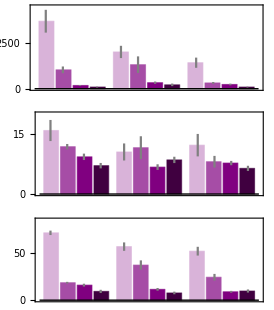

```mathematica
csize=245;
out2=GraphicsColumn[{Show[mybars1,ImageSize->csize*1.021],Show[mybars2,ImageSize->csize],Show[mybars3,ImageSize->csize]},Alignment->Right,Frame->True,FrameStyle->White]
```

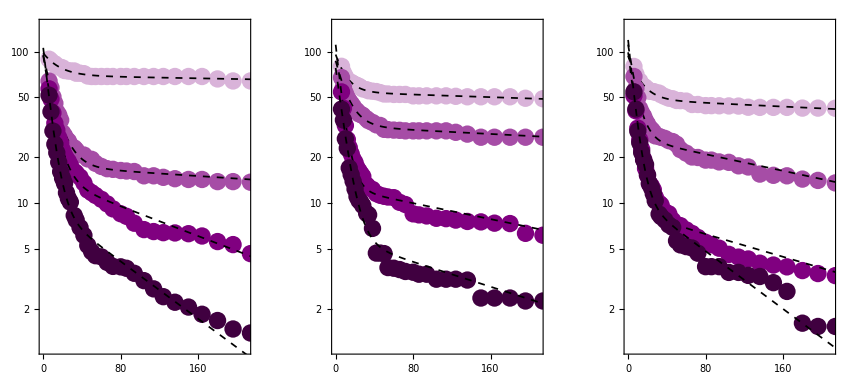

```mathematica
sp=30;
out1b=GraphicsRow[{Show[myP300AllPB[[15]],ImageSize->250],Show[kdm5bAll[[15]],ImageSize->250],Show[h2bAll[[15]],ImageSize->250]},Spacings->{{sp,sp,sp},0},Frame->True,FrameStyle->White]
```

```mathematica
sp=7;
out1c=GraphicsRow[{Show[Show[out4b,ImageSize->250],ImageSize->250],Show[out4a,ImageSize->250],out2},Spacings->{{sp*5,sp,sp},0},Frame->True,FrameStyle->White]
```

-Graphics-

```mathematica
outAg=GraphicsColumn[{out1b,out1c}]
```

-Graphics-

## Combining data for Fig 3 - mRNA interaction w/ PBs

```mathematica
myP300sGCA=FileNames["*p300_SGPB*greenComponentAnalysis.dat",myDirectory];
myKDM5Bsgcas=FileNames["*KDM5B_SGPB*greenComponentAnalysis.dat",myDirectory];
myH2Bsgcas=FileNames["*H2B_SGPB*greenComponentAnalysis.dat",myDirectory];
```

```mathematica
myns=(IntegerPart/@Table[ⅇ^(.09 t),{t,1,52,1}]//Union)[[5;;All]]
maxt=101;
dt=2;
```

{5,6,7,8,9,10,11,12,13,14,16,17,19,21,23,25,27,30,33,36,40,43,47,52,57,62,68,75,82,90,98,107}

```mathematica
myns//Length
```

32

```mathematica
h2bsgAll=RNAInteractionAnalysis[myH2Bsgcas,2,dt,maxt,myns,{0,51,71},{50,70,120}];
```

```mathematica
kdm5bsgAll=RNAInteractionAnalysis[myKDM5Bsgcas,2,dt,maxt,myns,{0,51,71},{50,70,120}];
```

```mathematica
oldbound={0,51,71},{50,70,120};
```

```mathematica
myns=(IntegerPart/@Table[ⅇ^(.09 t),{t,1,55,1}]//Union)[[5;;All]]
maxt=101;
dt=2;
```

{5,6,7,8,9,10,11,12,13,14,16,17,19,21,23,25,27,30,33,36,40,43,47,52,57,62,68,75,82,90,98,107,117,129,141}

```mathematica
P300gAll=RNAInteractionAnalysis[myP300sGCA,2,dt,maxt,myns,{0,51,66},{50,65,12000}];
```

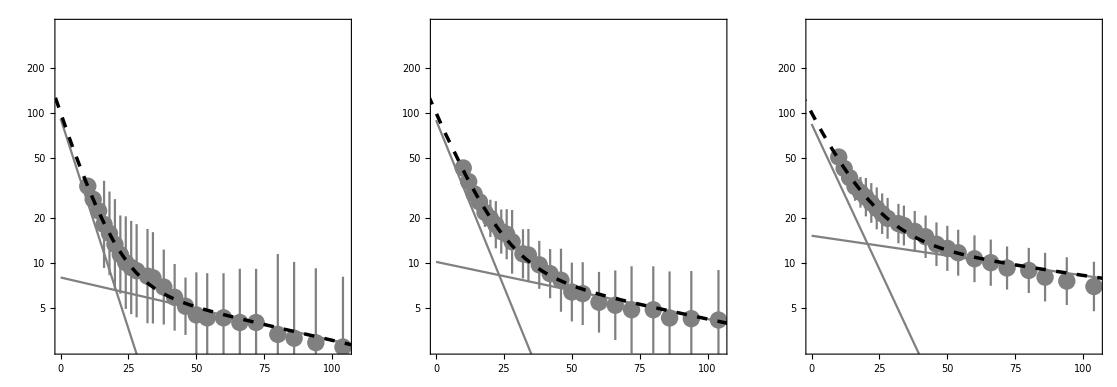

```mathematica
sp=-45;
outyb=GraphicsRow[{Show[h2bsgAll[[3,2]]],Show[kdm5bsgAll[[3,2]]],Show[P300gAll[[3,2]]],out2},Spacings->{{sp,sp,sp,0},0},Frame->True,FrameStyle->White]
```

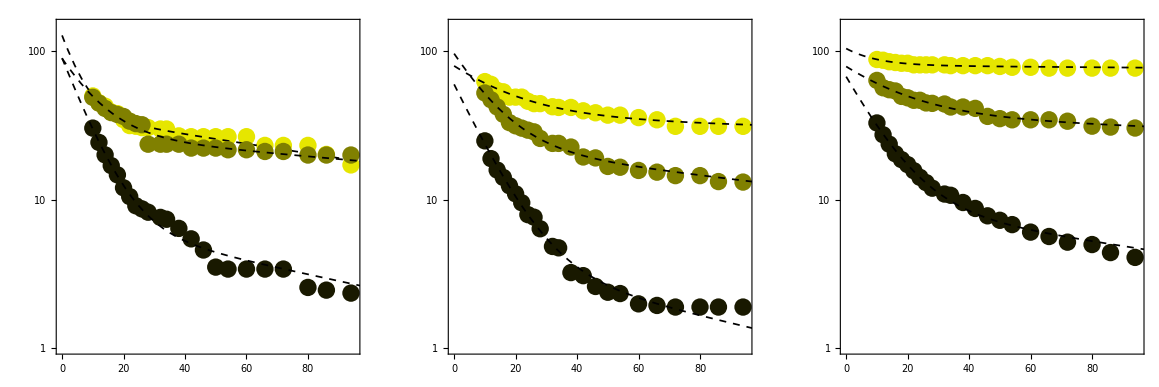

```mathematica
sp=-40;
outyb2=GraphicsRow[{Show[h2bsgAll[[15]],ImageSize->250],Show[kdm5bsgAll[[15]],ImageSize->250],Show[P300gAll[[15]],ImageSize->250],out2},Spacings->{{sp,sp,sp,30},0},Frame->True,FrameStyle->White]
```

```mathematica
mycolors=Reverse@{Darker[Yellow,0.9],Darker[Yellow,0.5],Darker[Yellow,0.1]}
```

{RGBColor[0.9, 0.9, 0.],RGBColor[0.5, 0.5, 0.],RGBColor[0.09999999999999998, 0.09999999999999998, 0.]}

```mathematica
myar=.37;is=150;
myi=5;
test={({{4.4,0},0}+{{-#[[1,1,1]],#[[1,1,2]]},#[[1,2]]})&/@Reverse[P300gAll[[myi,2]]],({{4.4+3.3,0},0}+{{-#[[1,1,1]],#[[1,1,2]]},#[[1,2]]})&/@Reverse[kdm5bsgAll[[myi,2]]],({{4.4+6.6,0},0}+{{-#[[1,1,1]],#[[1,1,2]]},#[[1,2]]})&/@Reverse[h2bsgAll[[myi,2]]]}//ErrorListPlot[#,PlotStyle->{{Gray,PointSize->0.00001}}]&;mybars1=Show[{Reverse@P300gAll[[myi,2,All,1,1,2]],Reverse@kdm5bsgAll[[myi,2,All,1,1,2]],Reverse@h2bsgAll[[myi,2,All,1,1,2]]}//BarChart[#,ChartStyle->Table[mycolors[[i]],{i,1,3,1}]]&,test,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{All,{0,4100}},AspectRatio->myar,ImageSize->{Automatic,is},Frame->True];
myi=6;
test={({{4.4,0},0}+{{-#[[1,1,1]],#[[1,1,2]]},#[[1,2]]})&/@Reverse[P300gAll[[myi,2]]],({{4.4+3.3,0},0}+{{-#[[1,1,1]],#[[1,1,2]]},#[[1,2]]})&/@Reverse[kdm5bsgAll[[myi,2]]],({{4.4+6.6,0},0}+{{-#[[1,1,1]],#[[1,1,2]]},#[[1,2]]})&/@Reverse[h2bsgAll[[myi,2]]]}//ErrorListPlot[#,PlotStyle->{{Gray,PointSize->0.00001}}]&;mybars2=Show[{Reverse@P300gAll[[myi,2,All,1,1,2]],Reverse@kdm5bsgAll[[myi,2,All,1,1,2]],Reverse@h2bsgAll[[myi,2,All,1,1,2]]}//BarChart[#,ChartStyle->Table[mycolors[[i]],{i,1,3,1}]]&,test,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{All,{0,25}},AspectRatio->myar,ImageSize->{Automatic,is},Frame->True];
myi=7;
test={({{4.4,0},0}+{{-#[[1,1,1]],#[[1,1,2]]},#[[1,2]]})&/@Reverse[P300gAll[[myi,2]]],({{4.4+3.3,0},0}+{{-#[[1,1,1]],#[[1,1,2]]},#[[1,2]]})&/@Reverse[kdm5bsgAll[[myi,2]]],({{4.4+6.6,0},0}+{{-#[[1,1,1]],#[[1,1,2]]},#[[1,2]]})&/@Reverse[h2bsgAll[[myi,2]]]}//ErrorListPlot[#,PlotStyle->{{Gray,PointSize->0.00001}}]&;mybars3=Show[{Reverse@P300gAll[[myi,2,All,1,1,2]],Reverse@kdm5bsgAll[[myi,2,All,1,1,2]],Reverse@h2bsgAll[[myi,2,All,1,1,2]]}//BarChart[#,ChartStyle->Table[mycolors[[i]],{i,1,3,1}]]&,test,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{All,{0,105}},AspectRatio->myar,ImageSize->{Automatic,is},Frame->True];
```

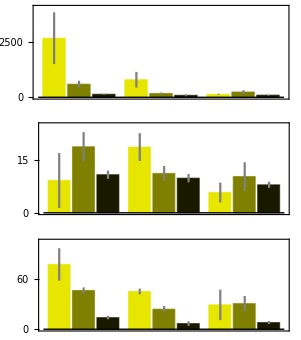

```mathematica
csize=270;
out2=GraphicsColumn[{Show[mybars1,ImageSize->csize*1.021],Show[mybars2,ImageSize->csize],Show[mybars3,ImageSize->csize]},Alignment->Right,Frame->True,FrameStyle->White]
```

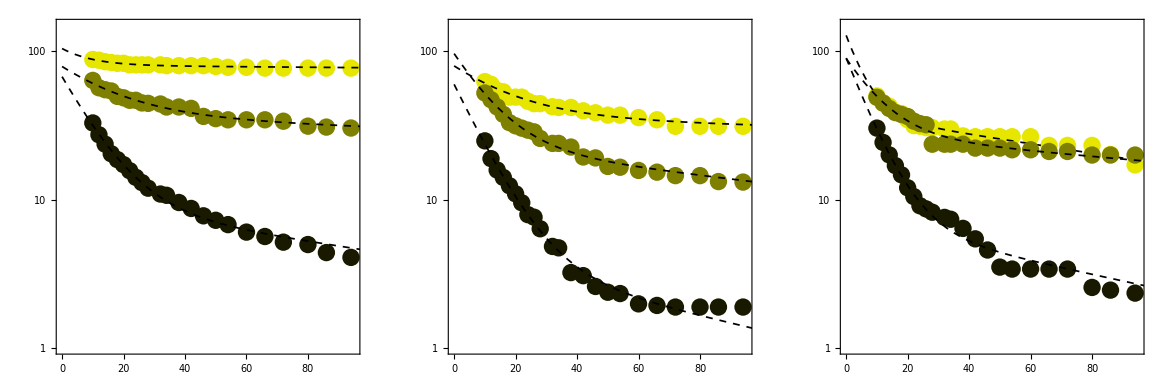

```mathematica
sp=-40;
outyb2=GraphicsRow[{Show[P300gAll[[15]],ImageSize->250],Show[kdm5bsgAll[[15]],ImageSize->250],Show[h2bsgAll[[15]],ImageSize->250],out2},Spacings->{{sp,sp,sp,30},0},Frame->True,FrameStyle->White]
```

## Figure 3c - promiscuous RNA

## Registering Red Images

```mathematica
{FileNameSetter[Dynamic[mymovie]],Dynamic[mymovie]}
```

{$CellContext`mymovieOpenAll,}

```mathematica
myColMovie=Import[mymovie]//Partition[#,3]&//Transpose;
If[DirectoryQ@(DirectoryName[mymovie]<>"Analysis\\")==False,CreateDirectory@(DirectoryName[mymovie]<>"Analysis\\")];
analysisFolder=DirectoryName[mymovie]<>"Analysis\\"<>StringDrop[StringDelete[mymovie,DirectoryName[mymovie]],-4];
```

```mathematica
myTfFunc=<<(DirectoryName[mymovie]<>"TransformationFunction.m");
```

```mathematica
myRedCorrImgs=Table[ImagePerspectiveTransformation[myColMovie⟦1,i⟧,myTfFunc,DataRange->Full],{i,1,Length@myColMovie⟦1⟧,1}];
```

```mathematica
myColCorrMovie=myColMovie;
myColCorrMovie⟦1⟧=myRedCorrImgs;
```

```mathematica
Export[StringReplace[mymovie,"MAX"->"Registered_MAX"],Flatten@Transpose@myColCorrMovie];
```

## Track mRNA in a cropped movie

```mathematica
{FileNameSetter[Dynamic[mymovie]],Dynamic[mymovie]}
```

{$CellContext`mymovieOpenAll,}

```mathematica
myColMovie=Import[mymovie]//Partition[#,3]&//Transpose;
If[DirectoryQ@(DirectoryName[mymovie]<>"Analysis\\")==False,CreateDirectory@(DirectoryName[mymovie]<>"Analysis\\")];
analysisFolder=DirectoryName[mymovie]<>"Analysis\\"<>StringDrop[StringDelete[mymovie,DirectoryName[mymovie]],-4];
```

#### Running z-average

```mathematica
avgFrameN=1;
avgFrameN>>analysisFolder<>"_avgFrameN.dat";myMaxN=Length@myColMovie⟦1⟧-avgFrameN+1;
```

```mathematica
myColMovieRunAv=If[avgFrameN==1,myColMovie,Table[Image@Mean@(ImageData/@myColMovie⟦i,j;;j+avgFrameN-1⟧),{i,1,2,1},{j,1,myMaxN,1}]];
```

```mathematica
Manipulate[ImageAdjust[myColMovieRunAv⟦channel,frame⟧,{0,0,1},{0,threshold}],{channel,Range@Length@myColMovieRunAv},{frame,1,myMaxN,1},{threshold,0,0.3,0.001}]
```

#### Make Mask

```mathematica
mymask=Image@ConstantArray[1,ImageDimensions@myColMovie⟦1,1⟧];
Export[analysisFolder<>"_mask.tif",mymask];
```

#### Setting Threshold

```mathematica
MyThresholding[myColMovieRunAv,analysisFolder]
```

#### Setting Threshold for Binarization

```mathematica
MyBinarization[myColMovieRunAv,analysisFolder]
```

#### Finding Particles

```mathematica
(* {
track number,
frame number,
{"IntensityCentroid","Centroid","Area","TotalIntensity","MeanIntensity","MedianIntensity","Elongation","MaxCentroidDistance","BoundingBox","ConvexVertices"}
} *)
```

```mathematica
{myRedSpots,myGreenSpots,myBlueSpots}=Table[MyParticleFinder[myColMovieRunAv,i,analysisFolder],{i,1,3,1}];
```

```mathematica
myBlueMasks=myGranuleMaskFinder[myColMovieRunAv,3,analysisFolder];
```

```mathematica
SpotLocationOnCell[myColMovieRunAv,thred,myRedSpots⟦All,All,3,1⟧,thgreen,myGreenSpots⟦All,All,3,1⟧,thblue,myBlueSpots⟦All,All,3,1⟧]
```

```mathematica
myRedSpots>>(analysisFolder<>"_redspots.dat");
myGreenSpots>>(analysisFolder<>"_greenspots.dat");
myBlueSpots>>(analysisFolder<>"_bluespots.dat");
myBlueMasks>>(analysisFolder<>"_bluemasks.dat");
```

#### Fitting Particles

```mathematica
(* {
"track number",
"frame number",
{"IntensityCentroid","Centroid","Area","TotalIntensity","MeanIntensity","MedianIntensity","Elongation","MaxCentroidDistance","BoundingBox","ConvexVertices"},
{{x, y},{int, BG},{sigmaX, sigmaY}},
{{x90Conf, y90Conf},{int90Conf, BG90Conf},{sigmaX90Conf,sigmaY90Conf}}
} *)
```

```mathematica
myRedSpots⟦1⟧
```

{{0,1,{{14.9675,14.4613},{15.,14.5},16.5,10.9844,0.686527,0.635996,0.183503,2.06155,{{13.,12.},{17.,17.}},{{13.,13.},{13.,16.},{14.,12.},{14.,17.},{16.,12.},{16.,17.},{17.,13.},{17.,16.}}}}}

```mathematica
{myRedSpotsFit,myRedCroppedData,myRedCenters}=MyParticleFitter[myColMovie,1,myRedSpots,5,avgFrameN];
{myGreenSpotsFit,myGreenCroppedData,myGreenCenters}=MyParticleFitter[myColMovie,2,myGreenSpots,5,avgFrameN];
```

```mathematica
SpotLocationOnCell[myColMovieRunAv,thred,myRedSpotsFit⟦All,All,4,1⟧,thgreen,myGreenSpotsFit⟦All,All,4,1⟧,thblue,myBlueSpots⟦All,All,3,1⟧]
```

```mathematica
{myRedSpotsFit,myRedCroppedData,myRedCenters}>>(analysisFolder<>"_redspotsFit.dat"); 
{myGreenSpotsFit,myGreenCroppedData,myGreenCenters}>>(analysisFolder<>"_greenspotsFit.dat");
```

```mathematica
Position[myRedSpotsFit⟦All,1,4,1⟧,{}]
```

{{155},{163}}

```mathematica
myRedFilledCenters=myRedSpotsFit⟦All,1,4,1⟧;
myRedFilledCenters⟦155⟧=myRedSpotsFit⟦{154,156},1,4,1⟧//Mean;
myRedFilledCenters⟦163⟧=myRedSpotsFit⟦{162,164},1,4,1⟧//Mean;
```

#### Plotting trajectory

```mathematica
Manipulate[Show[myColMovie⟦1,i⟧//ImageAdjust,Graphics[{White,Line@{{0,0},{0,60},{60,60},{60,0}},White,Line@myRedFilledCenters⟦;;i⟧}]],{i,1,Length@myColMovie⟦1⟧,1}]
```

```mathematica
i=148;
myTrajectory=Graphics[{White,Line@{{0,0},{0,60},{60,60},{60,0}},White,Line@myRedFilledCenters⟦;;i⟧}];
```

#### Make video

```mathematica
Manipulate[Show[ColorCombine@{ImageAdjust[myColMovie⟦1,i⟧,{0,0,1},thred],ImageAdjust[myColMovie⟦2,i⟧,{0,0,1},thgreen],ImageAdjust[myColMovie⟦3,i⟧,{0,0,1},thblue]},Graphics[{White,Line@myRedFilledCenters⟦;;i⟧}]],{i,1,Length@myColMovie⟦1⟧,1}]
```

```mathematica
myMagFactor=3;myColMoviewTrajectory=Flatten@{Table[ImageResize[ColorCombine@{ImageAdjust[myColMovie⟦1,i⟧,{0,0,1},thred],ImageAdjust[myColMovie⟦2,i⟧,{0,0,1},thgreen],ImageAdjust[myColMovie⟦3,i⟧,{0,0,1},thblue]},myMagFactor*ImageDimensions@myColMovie⟦1,1⟧],{i,1,Length@myColMovie⟦1⟧,1}],Table[Show[ImageResize[ColorCombine@{ImageAdjust[myColMovie⟦1,i⟧,{0,0,1},thred],ImageAdjust[myColMovie⟦2,i⟧,{0,0,1},thgreen],ImageAdjust[myColMovie⟦3,i⟧,{0,0,1},thblue]},myMagFactor*ImageDimensions@myColMovie⟦1,1⟧],Graphics[{White,Line@(myMagFactor*myRedFilledCenters⟦;;i⟧)}]],{i,1,Length@myColMovie⟦1⟧,1}]};
```

## Figure 3d - promiscuous RNA 2

## pre-processing data

### Reading in Images

```mathematica
{FileNameSetter[Dynamic[mymovie]],Dynamic[mymovie]}
```

{$CellContext`mymovieOpenAll,}

```mathematica
myColMovie=Import[mymovie]//Partition[#,3]&//Transpose;
If[DirectoryQ@(DirectoryName[mymovie]<>"Analysis\\")==False,CreateDirectory@(DirectoryName[mymovie]<>"Analysis\\")];
analysisFolder=DirectoryName[mymovie]<>"Analysis\\"<>StringDrop[StringDelete[mymovie,DirectoryName[mymovie]],-4];
```

### Reading in Parameters (if parameters exist)

#### basic parameters

```mathematica
myTfFunc=<<(DirectoryName@mymovie<>"TransformationFunction.m");
```

```mathematica
mymask=Import@(analysisFolder<>"_mask.tif");
```

```mathematica
avgFrameN=<<(analysisFolder<>"_avgFrameN.dat");
myMaxN=Length@myColMovie⟦1⟧-avgFrameN+1;
myColMovieRunAv=If[avgFrameN==1,myColMovie,MovingAverage[#,avgFrameN]&/@myColMovie];
```

#### basic color parameters

```mathematica
thred=<<(analysisFolder<>"_thred.dat");
{mymaxred,thred2,bandpassred,dotsizered}=<<(analysisFolder<>"_thred2.dat");
```

```mathematica
thgreen=<<(analysisFolder<>"_thgreen.dat");
{mymaxgreen,thgreen2,bandpassgreen,dotsizegreen}=<<(analysisFolder<>"_thgreen2.dat");
```

```mathematica
thblue=<<(analysisFolder<>"_thblue.dat");
{mymaxblue,thblue2,bandpassblue,dotsizeblue}=<<(analysisFolder<>"_thblue2.dat");
```

#### processed data

```mathematica
myRNA1Track=<<(analysisFolder<>"_myTrack_red_1.dat");
myRNA2Track=<<(analysisFolder<>"_myTrack_red_2.dat");
```

```mathematica
myRNA1fit=<<(analysisFolder<>"_myRNA1fit.dat");
myRNA2fit=<<(analysisFolder<>"_myRNA2fit.dat");
```

```mathematica
{myDiskSize,myDonutSize}=<<(analysisFolder<>"_DiskDonutSize");
```

```mathematica
myProtein1Int=<<(analysisFolder<>"_myProtein1Int.dat");
myProtein1BG=<<(analysisFolder<>"_myProtein1BG.dat");
```

```mathematica
myProtein1IntBGcor=MovingAverage[myProtein1Int,20]-MovingAverage[myProtein1BG,20];
```

```mathematica
myProtein2Int=<<(analysisFolder<>"_myProtein2Int.dat");
myProtein2BG=<<(analysisFolder<>"_myProtein2BG.dat");
```

```mathematica
myProtein2IntBGcor=MovingAverage[myProtein2Int,20]-MovingAverage[myProtein2BG,20];
```

### Make Mask

```mathematica
If[FileExistsQ[analysisFolder<>"_avg.tif"]==True,
avgImg=Import[analysisFolder<>"_avg.tif"];,
avgImg=Mean/@myColMovie;
Export[analysisFolder<>"_avg.tif",avgImg]];
If[FileExistsQ[analysisFolder<>"_max.tif"]==True,
maxImg=Import[analysisFolder<>"_max.tif"],
maxImg=ImageApply[Max,#]&/@myColMovie;
Export[analysisFolder<>"_max.tif",maxImg]];
```

```mathematica
Manipulate[maxImg⟦3⟧//ImageAdjust[#,{0,0,1},{threshold1,threshold2}]&,
Button["Choose threshold such that the shape of the cell can be visualized and CLICK",thtemp={threshold1,threshold2}],
{threshold1,0,0.2,0.001},{{threshold2,0.1},0,0.2,0.001}]
```

```mathematica
ImageAdjust[maxImg⟦3⟧,{0,0,1},thtemp]
```

```mathematica
mymask=-Graphics-;
Export[analysisFolder<>"_mask.tif",mymask];
```

```mathematica
(*mymask=Image@ConstantArray[1,ImageDimensions@avgImg];
Export[analysisFolder<>"_mask.tif",mymask];*)
```

### Running z-average

```mathematica
avgFrameN=1;
avgFrameN>>analysisFolder<>"_avgFrameN.dat";
myMaxN=Length@myColMovie⟦1⟧-avgFrameN+1;
```

```mathematica
myColMovieRunAv=If[avgFrameN==1,myColMovie,MovingAverage[#,avgFrameN]&/@myColMovie];
```

```mathematica
Manipulate[myColMovieRunAv⟦channel,frame⟧//ImageAdjust[#,{0,0,1},{0,threshold}]&,{channel,Range@Length@myColMovieRunAv},{frame,1,myMaxN,1},{threshold,0,0.3,0.001}]
```

### Setting Threshold

```mathematica
MyThresholding[myColMovieRunAv,analysisFolder]
```

### Setting Threshold for Binarization

```mathematica
MyBinarization[myColMovieRunAv,analysisFolder]
```

### Tracking each particles w/ Click-and-Track function

```mathematica
ClickAndTrack[myColMovie,myColMovieRunAv,analysisFolder]
```

### Fitting Particles

```mathematica
myRNA1Track=<<(analysisFolder<>"_myTrack_red_1.dat");
```

```mathematica
{myRNA1fit,myRedCroppedData,myRedCenters}=MyParticleFitter[myColMovie,1,{myRNA1Track},5,avgFrameN];
myRNA1fit=myRNA1fit⟦1⟧;
```

```mathematica
myRNA1fit>>(analysisFolder<>"_myRNA1fit.dat");
```

## Plotting data

```mathematica
myViewPoint={2,-2.5,0.5};
```

```mathematica
myViewPoint={1,-2.5,1.5};
```

```mathematica
intervTime=2/60;(*min*)
pixelSize=0.13;(*nm/pixel*)
```

#### Track 1

```mathematica
mySG1=<<(analysisFolder<>"_myTrack_blue_1.dat");
```

```mathematica
mySG1center=Flatten/@({#⟦2⟧,#⟦3,1⟧}&/@mySG1);
mySG1outline=Table[Flatten/@Thread@{mySG1⟦i,2⟧,mySG1⟦i,3,10⟧},{i,1,Length@mySG1,1}];
```

```mathematica
mySG1outlinePlot=ListSurfacePlot3D[Flatten[mySG1outline,1],MaxPlotPoints->500,PlotStyle->None,MeshStyle->Lighter[Blue,0.7]];
mySG1outlinePlotRings=ListSurfacePlot3D[Flatten[mySG1outline,1],MaxPlotPoints->500,Mesh->{30,0,0},PlotStyle->None,MeshStyle->Blue];
mySG1centerPlot=ListPointPlot3D[mySG1center,PlotStyle->Blue];
```

```mathematica
mySG1outlinePlot>>(analysisFolder<>"_SG1outlinePlot.dat");
mySG1outlinePlotRings>>(analysisFolder<>"_SG1outlinePlotRings.dat");
```

```mathematica
mySG1outlinePlot=<<(analysisFolder<>"_SG1outlinePlot.dat");
mySG1outlinePlotRings=<<(analysisFolder<>"_SG1outlinePlotRings.dat");
```

```mathematica
mySG2=<<(analysisFolder<>"_myTrack_blue_2.dat");
```

```mathematica
mySG2center=Flatten/@({#⟦2⟧,#⟦3,1⟧}&/@mySG2);
mySG2outline=Table[Flatten/@Thread@{mySG2⟦i,2⟧,mySG2⟦i,3,10⟧},{i,1,Length@mySG2,1}];
```

```mathematica
mySG2outlinePlot=ListSurfacePlot3D[Flatten[mySG2outline,1],MaxPlotPoints->500,PlotStyle->None,MeshStyle->Lighter[Blue,0.7]];
mySG2outlinePlotRings=ListSurfacePlot3D[Flatten[mySG2outline,1],MaxPlotPoints->500,Mesh->{30,0,0},PlotStyle->None,MeshStyle->Blue];
mySG2centerPlot=ListPointPlot3D[mySG2center,PlotStyle->Blue];
```

```mathematica
mySG2outlinePlot>>(analysisFolder<>"_SG2outlinePlot.dat");
mySG2outlinePlotRings>>(analysisFolder<>"_SG2outlinePlotRings.dat");
```

```mathematica
mySG2outlinePlot=<<(analysisFolder<>"_SG2outlinePlot.dat");
mySG2outlinePlotRings=<<(analysisFolder<>"_SG2outlinePlotRings.dat");
```

```mathematica
myPB1=<<(analysisFolder<>"_myTrack_green_1.dat");
```

```mathematica
myPB1center=Flatten/@({#⟦2⟧,#⟦3,1⟧}&/@myPB1);
myPB1outline=Table[Flatten/@Thread@{myPB1⟦i,2⟧,myPB1⟦i,3,10⟧},{i,1,Length@myPB1,1}];
```

```mathematica
myPB1outlinePlot=ListSurfacePlot3D[Flatten[myPB1outline,1],MaxPlotPoints->500,PlotStyle->None,MeshStyle->Lighter[Darker@Green,0.7]];
myPB1outlinePlotRings=ListSurfacePlot3D[Flatten[myPB1outline,1],MaxPlotPoints->500,Mesh->{30,0,0},PlotStyle->None,MeshStyle->Darker@Green];
myPB1centerPlot=ListPointPlot3D[myPB1center,PlotStyle->Darker@Green];
```

```mathematica
myPB1outlinePlot>>(analysisFolder<>"_PB1outlinePlot.dat");
myPB1outlinePlotRings>>(analysisFolder<>"_PB1outlinePlotRings.dat");
```

```mathematica
myPB1outlinePlot=<<(analysisFolder<>"_PB1outlinePlot.dat");
myPB1outlinePlotRings=<<(analysisFolder<>"_PB1outlinePlotRings.dat");
```

```mathematica
myRNA1fit=<<(analysisFolder<>"_myRNA1fit.dat");
```

```mathematica
myRNA1Shift=Flatten/@({#⟦2⟧,#⟦3,1⟧}&/@myRNA1fit);
myRNA1Shift⟦All,{2,3}⟧=myTfFunc@myRNA1Shift⟦All,{2,3}⟧;
myRNA1Plot=ListPointPlot3D[myRNA1Shift,PlotStyle->Red];
myRNA1Line=Graphics3D[{Red,Line@myRNA1Shift}];
```

```mathematica
myRNA1Plot=ListPointPlot3D[myRNA1Shift,PlotStyle->{Red,PointSize@0.007}];
```

```mathematica
myRNAtranslocation=Show[myRNA1Plot,myRNA1Line,mySG1centerPlot,mySG1outlinePlotRings,mySG1outlinePlot,mySG2centerPlot,mySG2outlinePlotRings,mySG2outlinePlot,myPB1centerPlot,myPB1outlinePlotRings,myPB1outlinePlot,BoxRatios-> {4,1,1},PlotRange->All,BaseStyle->{FontFamily->"Helvetica",FontSize->20},ViewPoint->myViewPoint,ImageSize->600,ImageResolution-> 300]
```

```mathematica
Table[{i,ToString@Round@((i-380)*pixelSize)},{i,380,450,2/pixelSize}]
```

{{380.,0},{395.385,2},{410.769,4},{426.154,6},{441.538,8}}

```mathematica
myRNAtranslocation=Show[myRNA1Plot,myRNA1Line,mySG1centerPlot,myProtein1Plot,mySG1outlinePlotRings,mySG1outlinePlot,BoxRatios-> {4,1,1},PlotRange->All,Ticks->{Table[{i,ToString@(intervTime*i)},{i,0,300,150}],Table[{i,ToString@Round@((i-180)*pixelSize)},{i,180,220,5/pixelSize}],Table[{i,ToString@Round@((i-380)*pixelSize)},{i,380,450,4/pixelSize}]},BaseStyle->{FontFamily->"Helvetica",FontSize->20},ViewPoint->myViewPoint,ImageSize->600,ImageResolution-> 300]
```

```mathematica
Export[myDirectoryFig<>"fig1b1.png",myTranslationShutoff1,ImageResolution->300];
```

#### draw granules with 3D graphics

```mathematica
myIdxSG1=FindCurvePath@#&/@mySG1outline⟦All,All,{2,3}⟧;
```

```mathematica
mySG1graphic=Show@(Graphics3D[{Lighter[Blue,0.7],Line@#}]&/@Table[(mySG1outline⟦i⟧)⟦myIdxSG1⟦i,1⟧⟧,{i,1,Length@myIdxSG1,1}]);
```

```mathematica
myIdxSG2=FindCurvePath@#&/@mySG2outline⟦All,All,{2,3}⟧;
```

```mathematica
mySG2graphic=Show@(Graphics3D[{Lighter[Blue,0.7],Line@#}]&/@Table[(mySG2outline⟦i⟧)⟦myIdxSG2⟦i,1⟧⟧,{i,1,Length@myIdxSG2,1}]);
```

```mathematica
myIdxPB1=FindCurvePath@#&/@myPB1outline⟦All,All,{2,3}⟧;
```

```mathematica
myPB1graphic=Show@(Graphics3D[{Lighter[Darker@Green,0.7],Line@#}]&/@Table[(myPB1outline⟦i⟧)⟦myIdxPB1⟦i,1⟧⟧,{i,1,Length@myIdxPB1,1}]);
```

```mathematica
myRNAtranslocation=Show[myRNA1Plot,myRNA1Line,mySG1graphic,mySG2graphic,myPB1graphic,BoxRatios-> {4,1,1},PlotRange->All,BaseStyle->{FontFamily->"Helvetica",FontSize->20},ViewPoint->myViewPoint,ImageSize->600,ImageResolution-> 300]
```

```mathematica
myRNAtranslocation=Show[myRNA1Plot,myRNA1Line,mySG1graphic,mySG2graphic,myPB1graphic,BoxRatios-> {4,1,1},PlotRange->All,Ticks->{Table[{i,ToString@(intervTime*i)},{i,0,300,150}],Table[{i,ToString@Round@((i-365)*pixelSize)},{i,365,420,5/pixelSize}],Table[{i,ToString@Round@((i-310)*pixelSize)},{i,310,365,5/pixelSize}]},BaseStyle->{FontFamily->"Helvetica",FontSize->20},ViewPoint->myViewPoint,ImageSize->600,ImageResolution-> 300]
```

#### draw granules with 3D graphics - sparce

```mathematica
myIdxSG1=FindCurvePath@#&/@mySG1outline⟦All,All,{2,3}⟧;
```

```mathematica
mySG1graphic=Show@(Graphics3D[{Lighter[Blue,0.3],Line@#}]&/@Table[(mySG1outline⟦i⟧)⟦myIdxSG1⟦i,1⟧⟧,{i,1,Length@myIdxSG1,1}])⟦;;All;;3⟧;
```

```mathematica
myIdxSG2=FindCurvePath@#&/@mySG2outline⟦All,All,{2,3}⟧;
```

```mathematica
mySG2graphic=Show@(Graphics3D[{Lighter[Blue,0.3],Line@#}]&/@Table[(mySG2outline⟦i⟧)⟦myIdxSG2⟦i,1⟧⟧,{i,1,Length@myIdxSG2,1}])⟦;;All;;3⟧;
```

```mathematica
myIdxPB1=FindCurvePath@#&/@myPB1outline⟦All,All,{2,3}⟧;
```

```mathematica
myPB1graphic=Show@(Graphics3D[{Lighter[Darker@Green,0.3],Line@#}]&/@Table[(myPB1outline⟦i⟧)⟦myIdxPB1⟦i,1⟧⟧,{i,1,Length@myIdxPB1,1}])⟦;;All;;3⟧;
```

```mathematica
myRNA1Plot=ListPointPlot3D[myRNA1Shift,PlotStyle->{Red,PointSize@0.015}]
myRNA1Line=Graphics3D[{Red,Line@myRNA1Shift}]
```

```mathematica
myRNAtranslocation=Show[myRNA1Plot,myRNA1Line,mySG1graphic,mySG2graphic,myPB1graphic,BoxRatios-> {4,1,1},PlotRange->All,BaseStyle->{FontFamily->"Helvetica",FontSize->20},ViewPoint->myViewPoint,ImageSize->600,ImageResolution-> 300]
```

```mathematica
myRNAtranslocation=Show[myRNA1Plot,myRNA1Line,mySG1graphic,mySG2graphic,myPB1graphic,BoxRatios-> {4,1,1},PlotRange->All,Ticks->{Table[{i,ToString@(intervTime*i)},{i,0,300,150}],Table[{i,ToString@Round@((i-365)*pixelSize)},{i,365,420,5/pixelSize}],Table[{i,ToString@Round@((i-310)*pixelSize)},{i,310,365,5/pixelSize}]},BaseStyle->{FontFamily->"Helvetica",FontSize->20},ViewPoint->myViewPoint,ImageSize->600,ImageResolution-> 300]
```

```mathematica
myRNAtranslocation=Show[myRNA1Plot,myRNA1Line,mySG1graphic,mySG2graphic,myPB1graphic,BoxRatios-> {4,1,1},PlotRange->All,BaseStyle->{FontFamily->"Helvetica",FontSize->10},ViewPoint->myViewPoint,ImageSize->300,ImageResolution-> 300]
```

-Graphics3D-

```mathematica
myRNAtranslocation=Show[myRNA1Plot,myRNA1Line,mySG1graphic,mySG2graphic,myPB1graphic,BoxRatios-> {4,1,1},PlotRange->All,Ticks->{Table[{i,ToString@(intervTime*i)},{i,0,300,150}],Table[{i,ToString@Round@((i-380)*pixelSize)},{i,380,410,3/pixelSize}],Table[{i,ToString@Round@((i-310)*pixelSize)},{i,310,365,5/pixelSize}]},BaseStyle->{FontFamily->"Helvetica",FontSize->10},ViewPoint->myViewPoint,ImageSize->300,ImageResolution-> 300]
```

-Graphics3D-

```mathematica
myRNAtranslocation=-Graphics3D-;
```

```mathematica
myRNAtranslocationNew=-Graphics3D-
```

## Figure 4a - MSD analysis

## pre-processing data

### Reading in Images

```mathematica
{FileNameSetter[Dynamic[mymovie]],Dynamic[mymovie]}
```

{$CellContext`mymovieOpenAll,}

```mathematica
mymovie=If[StringTake[FileBaseName[mymovie],4]=="AVG_",StringReplace[mymovie,"AVG_"->""],mymovie];
```

```mathematica
myColMovie=Import[mymovie]//Partition[#,3]&//Transpose;
analysisFolder=DirectoryName[mymovie]<>"Analysis\\"<>StringDrop[StringDelete[mymovie,DirectoryName[mymovie]],-4];
```

### Make Masks

```mathematica
tempImg=myColMovie[[3,1;;All]]//Mean;
Manipulate[tempImg//ImageAdjust[#,{0,0,1},{threshold1a,threshold2a}]&,
Button["Choose threshold such that the shape of the cell can be visualized and CLICK",thtemp={threshold1a,threshold2a}],
{threshold1a,0,0.5,0.001},{threshold2a,0,0.5,0.001}]
```

```mathematica
mymask=-Graphics-;
```

```mathematica
myCytMask=mymask;
```

```mathematica
myNucMask=-Graphics-;
```

```mathematica
mymask//ImageDimensions
```

{512,512}

```mathematica
myCytMask//ImageDimensions
```

{512,512}

```mathematica
myNucMask//ImageDimensions
```

{512,512}

```mathematica
myCytMask>>analysisFolder<>"_myCytMask.dat";
```

```mathematica
myNucMask>>analysisFolder<>"_myNucMask.dat";
```

### Creating Transformation Function

```mathematica
DirectoryName[mymovie]
```

C:\Users\tim_s\Documents\_mirroredX\_Fixie\Moon-Revision-Analysis\20180830\

```mathematica
dirBeads=DirectoryName[mymovie]<>"Beads";
```

```mathematica
myFiles=FileNames["*.tif",dirBeads];
myBeadsImgs=Table[Import@myFiles⟦i⟧,{i,1,Length[myFiles],1}];
myDims=ImageDimensions@myBeadsImgs⟦1,1⟧;
Manipulate[ColorCombine[{myBeadsImgs⟦data,1⟧,myBeadsImgs⟦data,2⟧,ConstantImage[0,myDims]}]//ImageAdjust,
Button["Choose an image to calculate the transformation function and CLICK",nRefImg=data],
{data,1,Length[myFiles],1}]
```

```mathematica
myRefBeadsRedImg=myBeadsImgs⟦nRefImg,1⟧;
myRefBeadsGreenImg=myBeadsImgs⟦nRefImg,2⟧;
Manipulate[GraphicsRow[{myRefBeadsRedImg//Binarize[#,thresholdRed]&,myRefBeadsGreenImg//Binarize[#,thresholdGreen]&},ImageSize->500],
Button["Choose thresholds and CLICK",{thRed=thresholdRed,thGreen=thresholdGreen}],
{thresholdRed,0.01,0.5,0.005},{thresholdGreen,0.01,0.5,0.001}]
```

```mathematica
myRedPosGuess=ComponentMeasurements[ImageMultiply[myRefBeadsRedImg,Binarize[myRefBeadsRedImg,thRed]],{"IntensityCentroid"}]⟦All,2,1⟧;
myGreenPosGuess=ComponentMeasurements[ImageMultiply[myRefBeadsGreenImg,Binarize[myRefBeadsGreenImg,thGreen]],{"IntensityCentroid"}]⟦All,2,1⟧;
StringForm["   `` red particles and `` green particles were found.",Length@myRedPosGuess,Length@myGreenPosGuess]
```

34 red particles and 35 green particles were found.

```mathematica
myRedAbsPos=BeadsFitting[myRefBeadsRedImg,myRedPosGuess,7];
myGreenAbsPos=BeadsFitting[myRefBeadsGreenImg,myGreenPosGuess,7];
{myTfFuncError,myTfFunc,distanceRaw,distanceCorrected}=BeadsTransform[myRedAbsPos,myGreenAbsPos,5];
{myTfFuncError,myTfFunc,Insert[{distanceRaw,distanceCorrected}//Transpose,{"Distance Before Correction","Distance After Correction"},1]//TableForm}
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{0.138036,TransformationFunction[(1.00104 | -0.00438366 | 2.06353
0.00215747 | 1.00373 | -2.41443
-7.81604×10^-7 | 1.01349×10^-6 | 1.)],Distance Before Correction | Distance After Correction
0.504248 | 0.062526
0.483218 | 0.153938
0.756954 | 0.134295
0.62683 | 0.0404636
0.940753 | 0.168567
0.904647 | 0.0458467
1.02556 | 0.0680188
0.897194 | 0.129964
1.09905 | 0.0857957
1.09996 | 0.120079
0.979548 | 0.125261
1.06209 | 0.148381
1.29783 | 0.122236
1.1972 | 0.0994174
1.37635 | 0.174946
1.33716 | 0.213036
1.62716 | 0.260515
1.65708 | 0.0794466
1.85612 | 0.116087
1.79426 | 0.0366966
1.9151 | 0.204019
1.66714 | 0.13385
1.74936 | 0.120323
2.00594 | 0.215686
2.13729 | 0.138394
2.18411 | 0.0549592
1.96651 | 0.0999845
2.13802 | 0.280537
2.45381 | 0.200558
2.46715 | 0.181795
2.33005 | 0.190512
2.52246 | 0.148405
2.7132 | 0.105829
2.93959 | 0.232871}

```mathematica
Export[DirectoryName[mymovie]<>"TransformationFunction.m",myTfFunc];
```

```mathematica
myTfFuncInv=InverseFunction@myTfFunc;
```

### Checking Transformation Function

```mathematica
Manipulate[ColorCombine[{myBeadsImgs⟦data,1⟧,myBeadsImgs⟦data,2⟧,ConstantImage[0,myDims]}]//ImageAdjust,
Button["Choose an image to check the transformation function and CLICK",nCheckImg=data],
{data,1,Length[myFiles],1}]
```

```mathematica
myCheckBeadsRedImg=myBeadsImgs⟦nCheckImg,1⟧;
myCheckBeadsGreenImg=myBeadsImgs⟦nCheckImg,2⟧;
Manipulate[GraphicsRow[{myCheckBeadsRedImg//Binarize[#,thresholdRed]&,myCheckBeadsGreenImg//Binarize[#,thresholdGreen]&},ImageSize->500],
Button["Choose thresholds and CLICK",{thcRed=thresholdRed,thcGreen=thresholdGreen}],
{thresholdRed,0.01,0.5,0.005},{thresholdGreen,0.01,0.5,0.005}]
```

```mathematica
myRedCheckPosGuess=ComponentMeasurements[ImageMultiply[myCheckBeadsRedImg,Binarize[myCheckBeadsRedImg,thcRed]],{"IntensityCentroid"}]⟦All,2,1⟧;
myGreenCheckPosGuess=ComponentMeasurements[ImageMultiply[myCheckBeadsGreenImg,Binarize[myCheckBeadsGreenImg,thcGreen]],{"IntensityCentroid"}]⟦All,2,1⟧;
StringForm["   `` red particles and `` green particles were found.",Length@myRedCheckPosGuess,Length@myGreenCheckPosGuess]
```

12 red particles and 11 green particles were found.

```mathematica
myRedCheckAbsPos=BeadsFitting[myCheckBeadsRedImg,myRedCheckPosGuess,7];
myGreenCheckAbsPos=BeadsFitting[myCheckBeadsGreenImg,myGreenCheckPosGuess,7];
BeadsCheck[myRedCheckAbsPos,myGreenCheckAbsPos,5]
```

Distance Before Correction | Distance After Correction
3.52268 | 0.237036
3.70134 | 0.24712
4.08483 | 0.257613
3.68448 | 0.334984
4.65206 | 0.0545464
4.57443 | 0.204799
4.32711 | 0.0882253
4.46865 | 0.123524

### Reading in Parameters (only if parameters exist)

```mathematica
myTfFunc=Import[DirectoryName[mymovie]<>"TransformationFunction.m"];
```

```mathematica
myTfFuncInv=InverseFunction@myTfFunc;
```

```mathematica
myParameters=<<(analysisFolder<>"_allParameters.dat");
{avgFrameN,thred,thred2,bandpassred,dotsizered,maxJumpDistRed,shortestTrackRed,thgreen,thgreen2,bandpassgreen,dotsizegreen,maxJumpDistGreen,shortestTrackGreen,thblue,thblue2,bandpassblue,dotsizeblue,maxJumpDistBlue,shortestTrackBlue,pad}=myParameters⟦{1,2,3,4,5,7,10,13,14,15,16,18,21,24,25,26,27,29,32,35},2⟧;
```

```mathematica
myMaxN=Length[myColMovie⟦1⟧]-avgFrameN+1;
myColMovieRunAv=Table[ImageMultiply[ImageAdd[myColMovie⟦i,j;;j+avgFrameN-1⟧],1/avgFrameN],{i,1,3,1},{j,1,myMaxN,1}];
```

```mathematica
redRunAvp=<<(analysisFolder<>"_redspots.dat");
greenRunAvp=<<(analysisFolder<>"_greenspots.dat");
blueRunAvp=<<(analysisFolder<>"_bluespots.dat");
```

```mathematica
myredtracks=<<(analysisFolder<>"_redtracks.dat");
mygreentracks=<<(analysisFolder<>"_greentracks.dat");
mybluetracks=<<(analysisFolder<>"_bluetracks.dat");
```

```mathematica
newTracksr=<<(analysisFolder<>"_RedTracksColorLinked.dat");
newTracksg=<<(analysisFolder<>"_GreenTracksColorLinked.dat");
newTracksb=<<(analysisFolder<>"_BlueTracksColorLinked.dat");
```

```mathematica
myHandCheckedTracksr=<<(analysisFolder<>"_RedTracksHandChecked.dat");
myHandCheckedTracksg=<<(analysisFolder<>"_GreenTracksHandChecked.dat");
myHandCheckedTracksb=<<(analysisFolder<>"_BlueTracksHandChecked.dat");
```

Get::noopen: Cannot open C:\Users\tim_s\Documents\_mirroredX\_Fixie\Moon-Revision-Analysis\20180830\Analysis\BG_MAX_Pos1_post_stress_p300_RedTracksHandChecked.dat.

Get::noopen: Cannot open C:\Users\tim_s\Documents\_mirroredX\_Fixie\Moon-Revision-Analysis\20180830\Analysis\BG_MAX_Pos1_post_stress_p300_GreenTracksHandChecked.dat.

Get::noopen: Cannot open C:\Users\tim_s\Documents\_mirroredX\_Fixie\Moon-Revision-Analysis\20180830\Analysis\BG_MAX_Pos1_post_stress_p300_BlueTracksHandChecked.dat.

```mathematica
{myBlueAllParameters,myBluePos,myBlueData}=<<(analysisFolder<>"_bluefits.dat");
```

Get::noopen: Cannot open C:\Users\tim_s\Documents\_mirroredX\_Fixie\Moon-Revision-Analysis\20180830\Analysis\BG_MAX_Pos1_post_stress_p300_bluefits.dat.

Set::shape: Lists {myBlueAllParameters,myBluePos,myBlueData} and $Failed are not the same shape.

```mathematica
{myRedAllParameters,myRedPos,myRedData}=<<(analysisFolder<>"_redfits.dat");
```

Get::noopen: Cannot open C:\Users\tim_s\Documents\_mirroredX\_Fixie\Moon-Revision-Analysis\20180830\Analysis\BG_MAX_Pos1_post_stress_p300_redfits.dat.

Set::shape: Lists {myRedAllParameters,myRedPos,myRedData} and $Failed are not the same shape.

```mathematica
{myGreenAllParameters,myGreenPos,myGreenData}=<<(analysisFolder<>"_greenfits.dat");
```

Get::noopen: Cannot open C:\Users\tim_s\Documents\_mirroredX\_Fixie\Moon-Revision-Analysis\20180830\Analysis\BG_MAX_Pos1_post_stress_p300_greenfits.dat.

Set::shape: Lists {myGreenAllParameters,myGreenPos,myGreenData} and $Failed are not the same shape.

```mathematica
myTfFunc=Import[DirectoryName[mymovie]<>"TransformationFunction.m"];
```

```mathematica
myTfFuncInv=InverseFunction@myTfFunc;
```

```mathematica
mylongredtracks=myredtracks//DeleteCases[#,x_/;Length[x]<shortestTrackRed]&;
StringForm["   `` red tracks are longer than ``, and the average length of the long tracks is ``",mylongredtracks//Length,shortestTrackRed,(Length/@mylongredtracks)//Mean//N]
mylongredtracksf=mylongredtracks⟦All,All,2⟧//Flatten[#,1]&//Sort//SplitBy[#,First]&;
```

174 red tracks are longer than 10, and the average length of the long tracks is 34.1552

```mathematica
mylonggreentracks=mygreentracks//DeleteCases[#,x_/;Length[x]<shortestTrackGreen]&;
StringForm["   `` green tracks are longer than ``, and the average length of the long tracks is ``",mylonggreentracks//Length,shortestTrackGreen,(Length/@mylonggreentracks)//Mean//N]
mylonggreentracksf=mylonggreentracks⟦All,All,2⟧//Flatten[#,1]&//Sort//SplitBy[#,First]&;
```

21 green tracks are longer than 5, and the average length of the long tracks is 14.1905

```mathematica
mylongbluetracks=mybluetracks//DeleteCases[#,x_/;Length[x]<shortestTrackBlue]&;
StringForm["   `` green tracks are longer than ``, and the average length of the long tracks is ``",mylongbluetracks//Length,shortestTrackBlue,(Length/@mylongbluetracks)//Mean//N]
mylongbluetracksf=mylongbluetracks⟦All,All,2⟧//Flatten[#,1]&//Sort//SplitBy[#,First]&;
```

169 green tracks are longer than 10, and the average length of the long tracks is 91.7692

```mathematica
mymask=<<(analysisFolder<>"_mymask.dat");
```

Get::noopen: Cannot open C:\Users\tim_s\Documents\_mirroredX\_Fixie\Moon-Revision-Analysis\20180830\Analysis\BG_MAX_Pos1_post_stress_p300_mymask.dat.

```mathematica
myNucMask=<<(analysisFolder<>"_myNucMask.dat");
```

```mathematica
myCytMask=<<(analysisFolder<>"_myCytMask.dat");
```

```mathematica
mymask=myCytMask;
```

```mathematica
analysisFolder
```

C:\Users\tim_s\Documents\_mirroredX\_Fixie\Moon-Revision-Analysis\20180830\Analysis\BG_MAX_Pos1_post_stress_p300

```mathematica
(*mymask=Import[analysisFolder<>"_nucleus_mask.tif"];*)
```

```mathematica
myNucMask=<<(analysisFolder<>"_myNucMask.dat");
```

```mathematica
myCytMask=<<(analysisFolder<>"_myCytMask.dat");
```

```mathematica
myCytImg=myCytMask;
```

```mathematica
myNucImg=myNucMask;
```

```mathematica
redComponentMask=Import[analysisFolder<>"_redComponentMask.tif"];
```

```mathematica
analysisFolder<>"_greenComponentMask.tif"
```

C:\Users\tim_s\Documents\_mirroredX\_Fixie\20170321\Analysis\BG_MAX_Cell03_greenComponentMask.tif

```mathematica
greenComponentMask=Import[analysisFolder<>"_greenComponentMask.tif"];
```

```mathematica
blueComponentMask=Import[analysisFolder<>"_blueComponentMask.tif"];
```

```mathematica
whitePlot=<<(analysisFolder<>"_whitePlot.dat");
purplePlot=<<(analysisFolder<>"_purplePlot.dat");
yellowPlot=<<(analysisFolder<>"_yellowPlot.dat");
cyanPlot=<<(analysisFolder<>"_cyanPlot.dat");
redPlot=<<(analysisFolder<>"_redPlot.dat");
greenPlot=<<(analysisFolder<>"_greenPlot.dat");
bluePlot=<<(analysisFolder<>"_bluePlot.dat");
```

```mathematica
myWhiteColorParameters=<<(analysisFolder<>"_FixedSigmaWhiteColorParameters.dat");
```

```mathematica
myYellowColorParameters=<<(analysisFolder<>"_FixedSigmaYellowColorParameters.dat");
```

```mathematica
myPurpleColorParameters=<<(analysisFolder<>"_FixedSigmaPurpleColorParameters.dat");
```

```mathematica
myCyanColorParameters=<<(analysisFolder<>"_FixedSigmaCyanColorParameters.dat");
```

```mathematica
myRedOnlyColorParameters=<<(analysisFolder<>"_FixedSigmaRedOnlyColorParameters.dat");
```

```mathematica
myGreenOnlyColorParameters=<<(analysisFolder<>"_FixedSigmaGreenOnlyColorParameters.dat");
```

```mathematica
myBlueOnlyColorParameters=<<(analysisFolder<>"_FixedSigmaBlueOnlyColorParameters.dat");
```

```mathematica
minOverlapTime=5; (*in frames*)
maxOverlapDistance=3;(*in pixels*)
```

```mathematica
listHead={"TrackN_Red","TrackN_Green","TrackN_Blue","FrameN","I_Red","I_Green","I_Blue","Dist_RG", "Dist_RB","Dist_GB","Step","MSD","X_Red","Y_Red","X_Green","Y_Green","X_Blue","Y_Blue","(dx_Red^2+dy_Red^2)^1/2","(dx_Green^2+dy_Green^2)^1/2","(dx_Blue^2+dy_Blue^2)^1/2"};
```

### Running z-average

```mathematica
avgFrameN=1;
myMaxN=Length[myColMovie⟦1⟧]-avgFrameN+1;
```

```mathematica
myColMovieRunAv=Table[ImageMultiply[ImageAdd[myColMovie⟦i,j;;j+avgFrameN-1⟧],1/avgFrameN],{i,1,3,1},{j,1,myMaxN,1}];
```

```mathematica
Manipulate[myColMovieRunAv⟦channel,frame⟧//ImageAdjust[#,{0,0,1},{0,threshold}]&,{channel,1,Length[myColMovieRunAv],1},{frame,1,myMaxN,1},{threshold,0,0.2,0.001}];
```

### Find Red Particles from Running z - averaged Movie (Red laser)

```mathematica
(* redRunAvp is list of {{x1,y1},{x2,y2}....{xn,yn}} in each frame *)
```

```mathematica
Manipulate[myColMovieRunAv⟦1,frame⟧//ImageAdjust[#,{0,0,1},{threshold1,threshold2}]&,
Button["Choose threshold such that the dots appear nicely and CLICK",thred={threshold1,threshold2}],
{frame,1,Length[myColMovieRunAv⟦1⟧],1},{{threshold1,0.001},0,0.4,0.001},{{threshold2,0.03},0,0.4,0.001}]
```

```mathematica
Manipulate[
max=BandPass[ImageMultiply[myColMovieRunAv⟦1, 1⟧ // ImageAdjust[#, {0, 0, 1}, thred] &,mymask],{lowpass,hipass}]//ImageData//Max;
imgb=BandPass[myColMovieRunAv⟦1, frame⟧ // ImageAdjust[#, {0, 0, 1}, thred] &,{lowpass,hipass}];
GraphicsRow[{myColMovieRunAv⟦1,frame⟧// ImageAdjust[#, {0, 0, 1}, thred]&,
SelectComponents[ImageMultiply[Binarize[imgb,max threshold],mymask],"Count",lo<#<hi&]},ImageSize->1000],
Button["Choose parameters and CLICK",{mymaxred=max,bandpassred={lowpass,hipass},thred2=threshold,dotsizered={lo,hi}}],
{frame,1,myMaxN,1},{{threshold,0.1},0,0.4,0.01},{{lowpass,1},0,10,1},{{hipass,7},0,50,1},{{lo,5},0,20,1},{{hi,100},20,2000,1}]
```

```mathematica
redRunAvp=Table[FindParticlesWeighted[myColMovieRunAv⟦1,i⟧//ImageAdjust[#,{0,0,1},thred]&,bandpassred,mymaxred,thred2,mymask,dotsizered],{i,1,myMaxN,1}];
StringForm["   `` red particles were found.",redRunAvp//Flatten[#,1]&//Length]
```

33966 red particles were found.

```mathematica
redComponentMask=Table[ImageTransformation[FindParticlesWeightedMask[myColMovieRunAv⟦1,i⟧//ImageAdjust[#,{0,0,1},thred]&,bandpassred,mymaxred,thred2,mymask,dotsizered],myTfFuncInv,DataRange->Full],{i,1,myMaxN,1}];
```

```mathematica
Manipulate[Show[myColMovieRunAv⟦1,frame⟧//ImageAdjust[#,{0,0,1},thred]&,Graphics[{Red,Circle[#,7]&/@(redRunAvp⟦frame⟧)}]],
Button["CLICK if you want to save this dataset",redRunAvp>>analysisFolder<>"_redspots.dat";Export[analysisFolder<>"_redComponentMask.tif",redComponentMask];],
{frame,1,myMaxN,1}]
```

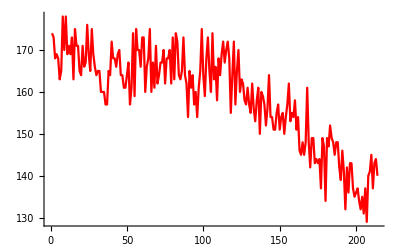

```mathematica
rSpotNPlot=Length/@redRunAvp//ListLinePlot[#,PlotStyle->Red]&
```

### Linking red tracks

```mathematica
maxJumpDistRed=10;
```

```mathematica
myredtracks=LinkTracks2[redRunAvp,maxJumpDistRed];
StringForm["`` red tracks were found by allowing `` pixel jump, and the average length of the tracks is ``",myredtracks//Length,maxJumpDistRed,(Length/@myredtracks)//Mean//N]
```

1940 red tracks were found by allowing 10 pixel jump, and the average length of the tracks is 15.7237

```mathematica
myredtracks>>analysisFolder<>"_redtracks.dat";
```

```mathematica
shortestTrackRed=10;
```

```mathematica
mylongredtracks=myredtracks//DeleteCases[#,x_/;Length[x]<shortestTrackRed]&;
StringForm["   `` red tracks are longer than ``, and the average length of the long tracks is ``",mylongredtracks//Length,shortestTrackRed,(Length/@mylongredtracks)//Mean//N]
```

688 red tracks are longer than 10, and the average length of the long tracks is 35.5058

```mathematica
mylongredtracksf=mylongredtracks⟦All,All,2⟧//Flatten[#,1]&//Sort//SplitBy[#,First]&;
```

```mathematica
Manipulate[Show[myColMovieRunAv⟦1,frame⟧//ImageAdjust[#,{0,0,1},thred]&,Graphics[{Red,Circle[#,7]&/@(mylongredtracksf⟦frame,All,2;;3⟧)}]],{frame,1,myMaxN,1}];
```

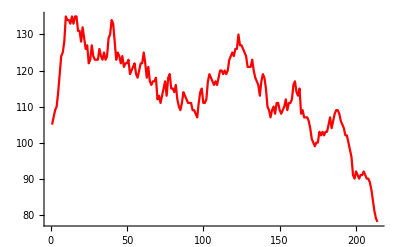

```mathematica
rSpotNPlot=Length/@mylongredtracksf//ListLinePlot[#,PlotStyle->Red]&
```

### Find Green Particles from Running z-averaged Movie (Green laser)

```mathematica
Manipulate[myColMovieRunAv⟦2,frame⟧//ImageAdjust[#,{0,0,1},{threshold1,threshold2}]&,
Button["Choose threshold such that the dots appear nicely and CLICK",thgreen={threshold1,threshold2}],
{frame,1,Length[myColMovieRunAv⟦2⟧],1},{{threshold1,0.001},0,0.4,0.001},{{threshold2,0.03},0,1,0.001}]
```

```mathematica
Manipulate[
max=BandPass[ImageMultiply[myColMovieRunAv⟦2, 1⟧ // ImageAdjust[#, {0, 0, 1}, thgreen] &,mymask],{lowpass,hipass}]//ImageData//Max;
imgb=BandPass[myColMovieRunAv⟦2, frame⟧ // ImageAdjust[#, {0, 0, 1}, thgreen] &,{lowpass,hipass}];
GraphicsRow[{myColMovieRunAv⟦2,frame⟧// ImageAdjust[#, {0, 0, 1}, thgreen]&,
SelectComponents[ImageMultiply[Binarize[imgb,max threshold],mymask],"Count",lo<#<hi&]},ImageSize->1000],
Button["Choose parameters and CLICK",{mymaxgreen=max,bandpassgreen={lowpass,hipass},thgreen2=threshold,dotsizegreen={lo,hi}}],
{frame,1,myMaxN,1},{{threshold,0.1},0,0.4,0.01},{{lowpass,1},0,10,1},{{hipass,7},0,30,1},{{lo,5},0,20,1},{{hi,100},50,500,1}]
```

```mathematica
greenRunAvp=Table[FindParticlesWeighted[myColMovieRunAv⟦2,i⟧//ImageAdjust[#,{0,0,1},thgreen]&,bandpassgreen,mymaxgreen,thgreen2,mymask,dotsizegreen],{i,1,myMaxN,1}];
StringForm["`` green particles were found.",greenRunAvp//Flatten[#,1]&//Length]
```

9535 green particles were found.

```mathematica
greenComponentMask=Table[FindParticlesWeightedMask[myColMovieRunAv⟦2,i⟧//ImageAdjust[#,{0,0,1},thgreen]&,bandpassgreen,mymaxgreen,thgreen2,mymask,dotsizegreen],{i,1,myMaxN,1}];
```

```mathematica
Manipulate[Show[myColMovieRunAv⟦2,frame⟧//ImageAdjust[#,{0,0,1},thgreen]&,Graphics[{Green,Circle[#,7]&/@(greenRunAvp⟦frame⟧)}]],
Button["CLICK if you want to save this dataset",greenRunAvp>>analysisFolder<>"_greenspots.dat";Export[analysisFolder<>"_greenComponentMask.tif",greenComponentMask];],
{frame,1,myMaxN,1}]
```

### Linking green tracks

```mathematica
maxJumpDistGreen=10;
```

```mathematica
mygreentracks=LinkTracks2[greenRunAvp,maxJumpDistGreen];
StringForm["   `` green tracks were found by allowing `` pixel jump, and the average length of the tracks is ``",mygreentracks//Length,maxJumpDistGreen,(Length/@mygreentracks)//Mean//N]
```

483 green tracks were found by allowing 10 pixel jump, and the average length of the tracks is 15.5839

```mathematica
mygreentracks>>analysisFolder<>"_greentracks.dat";
```

```mathematica
mylonggreentracksf=mylonggreentracks⟦All,All,2⟧//Flatten[#,1]&//Sort//SplitBy[#,First]&;
```

```mathematica
shortestTrackGreen=5;
```

```mathematica
mylonggreentracks=mygreentracks//DeleteCases[#,x_/;Length[x]<shortestTrackGreen]&;
StringForm["   `` green tracks are longer than ``, and the average length of the long tracks is ``",mylonggreentracks//Length,shortestTrackGreen,(Length/@mylonggreentracks)//Mean//N]
```

238 green tracks are longer than 5, and the average length of the long tracks is 28.1891

```mathematica
Manipulate[Show[myColMovieRunAv⟦2,frame⟧//ImageAdjust[#,{0,0,1},thgreen]&,Graphics[{Red,Circle[#,7]&/@(mylongredtracksf⟦frame,All,2;;3⟧)}],Graphics[{Green,Circle[#,7]&/@(mylonggreentracksf⟦frame,All,2;;3⟧)}]],{frame,1,myMaxN,1}];
```

```mathematica
mylonggreentracksf=mylonggreentracks⟦All,All,2⟧//Flatten[#,1]&//Sort//SplitBy[#,First]&;
```

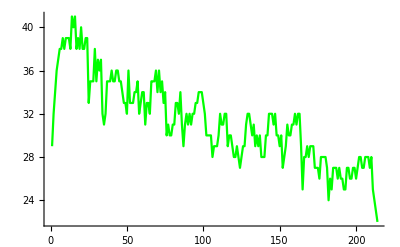

```mathematica
gSpotNPlot=Length/@mylonggreentracksf//ListLinePlot[#,PlotStyle->Green]&
```

```mathematica
(*Manipulate[Show[myColMovieRunAv⟦2,frame⟧//ImageAdjust[#,{0,0,1},thgreen]&,Graphics[{Green,PointSize[0.001],Point[#]&/@(mylonggreentracksf⟦1;;frame,All,2;;3⟧//Flatten[#,1]&)}],Graphics[{Red,Circle[#,7]&/@(mylonggreentracksf⟦frame,All,2;;3⟧)}]],{frame,1,myMaxN,1}]*)
```

### Find Blue Particles from Running z-averaged Movie (Blue laser)

```mathematica
Manipulate[myColMovieRunAv⟦3,frame⟧//ImageAdjust[#,{0,0,1},{threshold1,threshold2}]&,
Button["Choose threshold such that the dots appear nicely and CLICK",thblue={threshold1,threshold2}],
{frame,1,Length[myColMovieRunAv⟦3⟧],1},{{threshold1,0.001},0,0.4,0.001},{{threshold2,0.03},0,0.4,0.001}]
```

```mathematica
Manipulate[
max=BandPass[ImageMultiply[myColMovieRunAv⟦3, 1⟧ // ImageAdjust[#, {0, 0, 1}, thblue] &,mymask],{lowpass,hipass}]//ImageData//Max;
imgb=BandPass[myColMovieRunAv⟦3, frame⟧ // ImageAdjust[#, {0, 0, 1}, thblue] &,{lowpass,hipass}];
GraphicsRow[{myColMovieRunAv⟦3,frame⟧// ImageAdjust[#, {0, 0, 1}, thblue]&,
SelectComponents[ImageMultiply[Binarize[imgb,max threshold],mymask],"Count",lo<#<hi&]},ImageSize->1000],
Button["Choose parameters and CLICK",{mymaxblue=max,bandpassblue={lowpass,hipass},thblue2=threshold,dotsizeblue={lo,hi}}],
{frame,1,myMaxN,1},{{threshold,0.1},0,0.4,0.01},{{lowpass,1},0,10,1},{{hipass,6},0,10,1},{{lo,3},0,20,1},{{hi,200},50,1000,1}]
```

```mathematica
blueRunAvp=Table[FindParticlesWeighted[myColMovieRunAv⟦3,i⟧//ImageAdjust[#,{0,0,1},thblue]&,bandpassblue,mymaxblue,thblue2,mymask,dotsizeblue],{i,1,myMaxN,1}];
StringForm["`` blue particles were found.",blueRunAvp//Flatten[#,1]&//Length]
```

20958 blue particles were found.

```mathematica
blueComponentMask=Table[FindParticlesWeightedMask[myColMovieRunAv⟦3,i⟧//ImageAdjust[#,{0,0,1},thblue]&,bandpassblue,mymaxblue,thblue2,mymask,dotsizeblue],{i,1,myMaxN,1}];
```

```mathematica
Manipulate[Show[myColMovieRunAv⟦3,frame⟧//ImageAdjust[#,{0,0,1},thblue]&,Graphics[{Blue,Circle[#,7]&/@(blueRunAvp⟦frame⟧)}]],
Button["CLICK if you want to save this dataset",blueRunAvp>>analysisFolder<>"_bluespots.dat";Export[analysisFolder<>"_blueComponentMask.tif",blueComponentMask];],
{frame,1,myMaxN,1}]
```

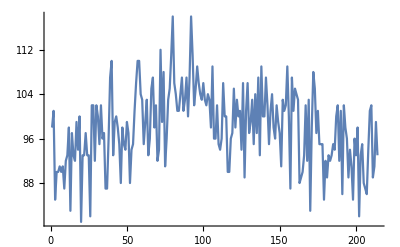

```mathematica
Length/@blueRunAvp//ListLinePlot
```

### Linking blue tracks

```mathematica
maxJumpDistBlue=15;
```

```mathematica
mybluetracks=LinkTracks2[blueRunAvp,maxJumpDistBlue];
StringForm["   `` blue tracks were found by allowing `` pixel jump, and the average length of the tracks is ``",mybluetracks//Length,maxJumpDistBlue,(Length/@mybluetracks)//Mean//N]
```

995 blue tracks were found by allowing 15 pixel jump, and the average length of the tracks is 16.9849

```mathematica
mybluetracks>>analysisFolder<>"_bluetracks.dat";
```

```mathematica
shortestTrackBlue=10;
```

```mathematica
mylongbluetracks=mybluetracks//DeleteCases[#,x_/;Length[x]<shortestTrackBlue]&;
StringForm["   `` blue tracks are longer than ``, and the average length of the long tracks is ``",mylongbluetracks//Length,shortestTrackBlue,(Length/@mylongbluetracks)//Mean//N]
```

266 blue tracks are longer than 10, and the average length of the long tracks is 51.3383

```mathematica
mylongbluetracksf=mylongbluetracks⟦All,All,2⟧//Flatten[#,1]&//Sort//SplitBy[#,First]&;
```

```mathematica
Manipulate[Show[myColMovieRunAv⟦3,frame⟧//ImageAdjust[#,{0,0,1},thblue]&,Graphics[{Red,Circle[#,7]&/@(mylongredtracksf⟦frame,All,2;;3⟧)}],
Graphics[{Green,Circle[#,5]&/@(mylonggreentracksf⟦frame,All,2;;3⟧)}],Graphics[{Blue,Circle[#,7]&/@(mylongbluetracksf⟦frame,All,2;;3⟧)}]],{frame,1,myMaxN,1}];
```

```mathematica
mylongbluetracksf=mylongbluetracks⟦All,All,2⟧//Flatten[#,1]&//Sort//SplitBy[#,First]&;
```

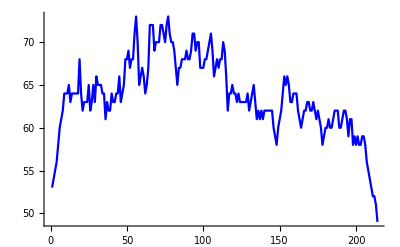

```mathematica
bSpotNPlot=Length/@mylongbluetracksf//ListLinePlot[#,PlotStyle->Blue]&
```

### Check all tracks (and double-check transformation function)

```mathematica
mylongredtracksColReg=mylongredtracks;
mylongredtracksColReg⟦All,All,2,2;;⟧=myTfFunc/@mylongredtracksColReg⟦All,All,2,2;;⟧;
```

```mathematica
mylongredtracksColReg//Dimensions
```

{688}

```mathematica
Clear[mylongredtracksColRegf]
```

```mathematica
mylongredtracksColRegf=mylongredtracksColReg⟦All,All,2⟧//Flatten[#,1]&//Sort//SplitBy[#,First]&;
```

```mathematica
Manipulate[Show[
ColorCombine[{redComponentMask⟦frame⟧,greenComponentMask⟦frame⟧,blueComponentMask⟦frame⟧}],Graphics[{Red,Circle[#,5]&/@(mylongredtracksColRegf⟦frame,All,2;;3⟧)}],
Graphics[{Green,Circle[#,6]&/@(mylonggreentracksf⟦frame,All,2;;3⟧)}],Graphics[{Blue,Circle[#,7]&/@(mylongbluetracksf⟦frame,All,2;;3⟧)}]],{frame,1,myMaxN,1}]
```

```mathematica
thred=thblue
```

{0.001,0.046}

```mathematica
Manipulate[Show[{myColMovieRunAv⟦3,frame⟧//ImageAdjust[#,{0,0,1},thred*2]&,Graphics[{Blue,Circle[#,7]&/@(mylongbluetracksf⟦frame,All,2;;3⟧)}]}],{frame,1,myMaxN,1}];
```

```mathematica
(*Manipulate[Show[myColMovieRunAv⟦3,frame⟧//ImageAdjust[#,{0,0,1},thblue]&,Graphics[{Blue,PointSize[0.001],Point[#]&/@(mylongbluetracksf⟦1;;frame,All,2;;3⟧//Flatten[#,1]&)}],Graphics[{Red,Circle[#,7]&/@(mylongbluetracksf⟦frame,All,2;;3⟧)}]],{frame,1,myMaxN,1}]*)
```

### Linking red, blue, and green tracks

```mathematica
tracksr=Map[Append[#,{1,0,0}]&,mylongredtracksColReg,{2}];
tracksr⟦All,All,1⟧=Range@Length@tracksr;
tracksg=Map[Append[#,{0,1,0}]&,mylonggreentracks,{2}];
tracksg⟦All,All,1⟧=Range@Length@tracksg;
tracksb=Map[Append[#,{0,0,1}]&,mylongbluetracks,{2}];
tracksb⟦All,All,1⟧=Range@Length@tracksb;
```

```mathematica
minOverlapTime=5;
maxOverlapDistance=3;(*in pixels*)
```

```mathematica
{newTracksr,newTracksg,newTracksb}=Connect3Colors[tracksr,tracksg,tracksb,minOverlapTime,maxOverlapDistance];
```

$Aborted

```mathematica
Prepend[Thread@{{"Red","Green","Blue"},Length/@{tracksr,tracksg,tracksb},Length/@{newTracksr,newTracksg,newTracksb}},{"The # of Tracks","Before Linking","After Linking"}]//MatrixForm
```

(The # of Tracks | Before Linking | After Linking
Red | 91 | 82
Green | 1 | 1
Blue | 110 | 109)

```mathematica
newTracksr>>analysisFolder<>"_RedTracksColorLinked.dat";
newTracksg>>analysisFolder<>"_GreenTracksColorLinked.dat";
newTracksb>>analysisFolder<>"_BlueTracksColorLinked.dat";
```

### Hand Checking

#### Setting Parameters and Creating Inverse Function of Transformation Function

```mathematica
dist=15;time=10;
```

```mathematica
myTfFuncInv=InverseFunction@myTfFunc;
```

#### Hand Checking Red

```mathematica
myHandCheckedTracksr=newTracksr;
myHandCheckedTracksr⟦All,All,2,2;;⟧=myTfFuncInv/@myHandCheckedTracksr⟦All,All,2,2;;⟧;
```

```mathematica
Manipulate[
{listConnectTracks,posiConnectTracks}=FindConnectableTracks2[myHandCheckedTracksr,myMaxN,dist,time,trackN];
Column@{Show[myColMovieRunAv⟦channel,frame⟧//ImageAdjust[#,{0,0,1},If[channel==1,thred,If[channel==2,thgreen,thblue]]]&,
Graphics[{Red,Circle[#,7]&/@(posiConnectTracks⟦frame,2,All,{2,3}⟧),Green,Inset[#⟦1⟧,#⟦2⟧-{10,10}]&/@(Thread@{posiConnectTracks⟦frame,2,All,1⟧,posiConnectTracks⟦frame,2,All,{2,3}⟧})}]],
"",
Prepend[Prepend[Thread@{"track "<>#&/@CharacterRange["A","F"]⟦;;Length@listConnectTracks-1⟧,
"track " <>#&/@ToString/@listConnectTracks⟦2;;⟧,myHandCheckedTracksr⟦listConnectTracks⟦2;;⟧,1,2,1⟧,(Last/@myHandCheckedTracksr⟦listConnectTracks⟦2;;⟧⟧)⟦All,2,1⟧},{"Current track","track " <>ToString@trackN,myHandCheckedTracksr⟦trackN,1,2,1⟧,(Last@myHandCheckedTracksr⟦trackN⟧)⟦2,1⟧}],{"track","track number","Start","End"}]//TableForm,
"",
"The number of all tracks is "<>ToString@Length@myHandCheckedTracksr},
Button["Click to Connect",
chosenTracks=Prepend[listConnectTracks⟦1+Position[{trackA,trackB,trackC,trackD,trackE,trackF},True]//Flatten⟧,trackN];
myHandCheckedTracksr=ConnectTracksFilled[myHandCheckedTracksr,chosenTracks];
(*Print@Position[Dynamic/@(ToExpression/@("track"<>#&/@CharacterRange["A","F"])),True]*)],
Button["Remove This Point"],
Button["Split Tracks from This Frame"],
Button["Delete This Track",myHandCheckedTracksr=Delete[myHandCheckedTracksr,trackN]],
{{channel,1},{1,2,3}},{trackN,1,Length@myHandCheckedTracksr,1},{frame,1,myMaxN,1},{trackA,{False,True}},{trackB,{False,True}},{trackC,{False,True}},{trackD,{False,True}},{trackE,{False,True}},{trackF,{False,True}}]
```

Set::shape: Lists {listConnectTracks,posiConnectTracks} and FindConnectableTracks2[myHandCheckedTracksr,myMaxN,dist,time,1] are not the same shape.

Part::partd: Part specification myColMovieRunAv⟦1,1⟧ is longer than depth of object.

ImageAdjust::imginv: Expecting an image or graphics instead of myColMovieRunAv⟦1,1⟧.

Part::partd: Part specification posiConnectTracks⟦1,2,All,{2,3}⟧ is longer than depth of object.

Part::pkspec1: The expression Circle[1,7] cannot be used as a part specification.

Part::partd: Part specification posiConnectTracks⟦1,2,All,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ImageAdjust[myColMovieRunAv⟦1,1⟧,{0,0,1},thred],].

Part::take: Cannot take positions 2 through -1 in listConnectTracks.

Part::pspec1: Part specification 2 ;; All is not applicable.

Part::pspec1: Part specification track 2 ;; All is not applicable.

Part::take: Cannot take positions 2 through -1 in listConnectTracks.

Part::pkspec1: The expression listConnectTracks⟦2;;All⟧ cannot be used as a part specification.

Part::take: Cannot take positions 2 through -1 in listConnectTracks.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::pkspec1: The expression listConnectTracks⟦2;;All⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Last::normal: Nonatomic expression expected at position 1 in Last[myHandCheckedTracksr].

Last::argt: Last called with 0 arguments; 1 or 2 arguments are expected.

```mathematica
□_□
```

□_□

```mathematica
myHandCheckedTracksr>>analysisFolder<>"_RedTracksHandChecked.dat";
```

#### Hand Checking Green

```mathematica
myHandCheckedTracksg=newTracksg;
```

```mathematica
Manipulate[
{listConnectTracks,posiConnectTracks}=FindConnectableTracks2[myHandCheckedTracksg,myMaxN,dist,time,trackN];
Column@{Show[myColMovieRunAv⟦channel,frame⟧//ImageAdjust[#,{0,0,1},If[channel==1,thred,If[channel==2,thgreen,thblue]]]&,
Graphics[{Red,Circle[#,7]&/@(posiConnectTracks⟦frame,2,All,{2,3}⟧),Green,Inset[#⟦1⟧,#⟦2⟧-{10,10}]&/@(Thread@{posiConnectTracks⟦frame,2,All,1⟧,posiConnectTracks⟦frame,2,All,{2,3}⟧})}]],
"",
Prepend[Prepend[Thread@{"track "<>#&/@CharacterRange["A","F"]⟦;;Length@listConnectTracks-1⟧,
"track " <>#&/@ToString/@listConnectTracks⟦2;;⟧,myHandCheckedTracksg⟦listConnectTracks⟦2;;⟧,1,2,1⟧,(Last/@myHandCheckedTracksg⟦listConnectTracks⟦2;;⟧⟧)⟦All,2,1⟧},{"Current track","track " <>ToString@trackN,myHandCheckedTracksg⟦trackN,1,2,1⟧,(Last@myHandCheckedTracksg⟦trackN⟧)⟦2,1⟧}],{"track","track number","Start","End"}]//TableForm,
"",
"The number of all tracks is "<>ToString@Length@myHandCheckedTracksg},
Button["Click to Connect",
chosenTracks=Prepend[listConnectTracks⟦1+Position[{trackA,trackB,trackC,trackD,trackE,trackF},True]//Flatten⟧,trackN];
myHandCheckedTracksg=ConnectTracksFilled[myHandCheckedTracksg,chosenTracks];
(*Print@Position[Dynamic/@(ToExpression/@("track"<>#&/@CharacterRange["A","F"])),True]*)],
Button["Remove This Point"],
Button["Split Tracks from This Frame"],
Button["Delete This Track",myHandCheckedTracksg=Delete[myHandCheckedTracksg,trackN]],
{{channel,2},{1,2,3}},{trackN,1,Length@myHandCheckedTracksg,1},{frame,1,myMaxN,1},{trackA,{False,True}},{trackB,{False,True}},{trackC,{False,True}},{trackD,{False,True}},{trackE,{False,True}},{trackF,{False,True}}]
```

Set::shape: Lists {listConnectTracks,posiConnectTracks} and FindConnectableTracks2[myHandCheckedTracksg,myMaxN,dist,time,1] are not the same shape.

Part::partd: Part specification myColMovieRunAv⟦2,1⟧ is longer than depth of object.

ImageAdjust::imginv: Expecting an image or graphics instead of myColMovieRunAv⟦2,1⟧.

Part::partd: Part specification posiConnectTracks⟦1,2,All,{2,3}⟧ is longer than depth of object.

Part::pkspec1: The expression Circle[1,7] cannot be used as a part specification.

Part::partd: Part specification posiConnectTracks⟦1,2,All,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ImageAdjust[myColMovieRunAv⟦2,1⟧,{0,0,1},thgreen],].

Part::take: Cannot take positions 2 through -1 in listConnectTracks.

Part::pspec1: Part specification 2 ;; All is not applicable.

Part::pspec1: Part specification track 2 ;; All is not applicable.

Part::take: Cannot take positions 2 through -1 in listConnectTracks.

Part::pkspec1: The expression listConnectTracks⟦2;;All⟧ cannot be used as a part specification.

Part::take: Cannot take positions 2 through -1 in listConnectTracks.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::pkspec1: The expression listConnectTracks⟦2;;All⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Last::normal: Nonatomic expression expected at position 1 in Last[myHandCheckedTracksg].

Last::argt: Last called with 0 arguments; 1 or 2 arguments are expected.

```mathematica
myHandCheckedTracksg>>analysisFolder<>"_GreenTracksHandChecked.dat";
```

#### Hand Checking Blue

```mathematica
myHandCheckedTracksb=newTracksb;
```

```mathematica
Manipulate[
{listConnectTracks,posiConnectTracks}=FindConnectableTracks2[myHandCheckedTracksb,myMaxN,dist,time,trackN];
Column@{Show[myColMovieRunAv⟦channel,frame⟧//ImageAdjust[#,{0,0,1},If[channel==1,thred,If[channel==2,thgreen,thblue]]]&,
Graphics[{Red,Circle[#,7]&/@(posiConnectTracks⟦frame,2,All,{2,3}⟧),Green,Inset[#⟦1⟧,#⟦2⟧-{10,10}]&/@(Thread@{posiConnectTracks⟦frame,2,All,1⟧,posiConnectTracks⟦frame,2,All,{2,3}⟧})}]],
"",
Prepend[Prepend[Thread@{"track "<>#&/@CharacterRange["A","F"]⟦;;Length@listConnectTracks-1⟧,
"track " <>#&/@ToString/@listConnectTracks⟦2;;⟧,myHandCheckedTracksb⟦listConnectTracks⟦2;;⟧,1,2,1⟧,(Last/@myHandCheckedTracksb⟦listConnectTracks⟦2;;⟧⟧)⟦All,2,1⟧},{"Current track","track " <>ToString@trackN,myHandCheckedTracksb⟦trackN,1,2,1⟧,(Last@myHandCheckedTracksb⟦trackN⟧)⟦2,1⟧}],{"track","track number","Start","End"}]//TableForm,
"",
"The number of all tracks is "<>ToString@Length@myHandCheckedTracksb},
Button["Click to Connect",
chosenTracks=Prepend[listConnectTracks⟦1+Position[{trackA,trackB,trackC,trackD,trackE,trackF},True]//Flatten⟧,trackN];
myHandCheckedTracksb=ConnectTracksFilled[myHandCheckedTracksb,chosenTracks];
(*Print@Position[Dynamic/@(ToExpression/@("track"<>#&/@CharacterRange["A","F"])),True]*)],
Button["Remove This Point"],
Button["Split Tracks from This Frame"],
Button["Delete This Track",myHandCheckedTracksb=Delete[myHandCheckedTracksb,trackN]],
{{channel,3},{1,2,3}},{trackN,1,Length@myHandCheckedTracksb,1},{frame,1,myMaxN,1},{trackA,{False,True}},{trackB,{False,True}},{trackC,{False,True}},{trackD,{False,True}},{trackE,{False,True}},{trackF,{False,True}}]
```

Set::shape: Lists {listConnectTracks,posiConnectTracks} and FindConnectableTracks2[myHandCheckedTracksb,myMaxN,dist,time,1] are not the same shape.

Part::partd: Part specification myColMovieRunAv⟦3,1⟧ is longer than depth of object.

ImageAdjust::imginv: Expecting an image or graphics instead of myColMovieRunAv⟦3,1⟧.

Part::partd: Part specification posiConnectTracks⟦1,2,All,{2,3}⟧ is longer than depth of object.

Part::pkspec1: The expression Circle[1,7] cannot be used as a part specification.

Part::partd: Part specification posiConnectTracks⟦1,2,All,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ImageAdjust[myColMovieRunAv⟦3,1⟧,{0,0,1},thblue],].

Part::take: Cannot take positions 2 through -1 in listConnectTracks.

Part::pspec1: Part specification 2 ;; All is not applicable.

Part::pspec1: Part specification track 2 ;; All is not applicable.

Part::take: Cannot take positions 2 through -1 in listConnectTracks.

Part::pkspec1: The expression listConnectTracks⟦2;;All⟧ cannot be used as a part specification.

Part::take: Cannot take positions 2 through -1 in listConnectTracks.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::pkspec1: The expression listConnectTracks⟦2;;All⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Last::normal: Nonatomic expression expected at position 1 in Last[myHandCheckedTracksb].

Last::argt: Last called with 0 arguments; 1 or 2 arguments are expected.

```mathematica
myHandCheckedTracksb>>analysisFolder<>"_BlueTracksHandChecked.dat";
```

### Fitting Tracks with Gaussian

#### Setting Parameters

```mathematica
pad=5;
myTrimSize=2*pad+1;
```

#### Fitting red tracks with Gaussian

```mathematica
{myRedAllParameters,myRedPos,myRedData}=ParticleFittingFixedSigma[myColMovie,1,myHandCheckedTracksr,pad,myTrimSize,1.5,avgFrameN];
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NonlinearModelFit::cvmit will be suppressed during this calculation.

$Aborted

```mathematica
{myRedAllParameters,myRedPos,myRedData}>>analysisFolder<>"_redfits.dat";
```

```mathematica
{myRedAllParameters,myRedPos,myRedData}=<<(analysisFolder<>"_redfits.dat");
```

```mathematica
myRedAllParametersColReg=myRedAllParameters;
myRedAllParametersColReg⟦All,3;;4⟧=myTfFunc/@myRedAllParameters⟦All,3;;4⟧;
```

```mathematica
mylabel={"TrackN","FrameN","X (130 nm pixels)","Y (130 nm pixels)","Peak intensity","Background intensity","SigmaX (130 nm pixels)", "SigmaY (130 nm pixels)","X min 90% confidence interval (130 nm pixels)","X max 90% confidence interval (130 nm pixels)","Y min 90% confidence interval (130 nm pixels)","Y max 90% confidence interval (130 nm pixels)","Peak intensity min 90% confidence interval","Peak intensity max 90% confidence interval","Background intensity min 90% confidence interval","Background max 90% confidence interval","SigmaX min 90% confidence interval (130 nm pixels)","SigmaX max 90% confidence interval (130 nm pixels)","SigmaY min 90% confidence interval (130 nm pixels)","SigmaY max 90% confidence interval (130 nm pixels)","R","G","B"};
myRedAllParametersColRegLabeled=Insert[myRedAllParametersColReg,mylabel,1];
```

```mathematica
Export[analysisFolder<>"_FixedSigmaRedAllParameters.xls",myRedAllParametersColRegLabeled];
```

#### Fitting green tracks with Gaussian

```mathematica
mylabel={"TrackN","FrameN","X (130 nm pixels)","Y (130 nm pixels)","Peak intensity","Background intensity","SigmaX (130 nm pixels)", "SigmaY (130 nm pixels)","X min 90% confidence interval (130 nm pixels)","X max 90% confidence interval (130 nm pixels)","Y min 90% confidence interval (130 nm pixels)","Y max 90% confidence interval (130 nm pixels)","Peak intensity min 90% confidence interval","Peak intensity max 90% confidence interval","Background intensity min 90% confidence interval","Background max 90% confidence interval","SigmaX min 90% confidence interval (130 nm pixels)","SigmaX max 90% confidence interval (130 nm pixels)","SigmaY min 90% confidence interval (130 nm pixels)","SigmaY max 90% confidence interval (130 nm pixels)","R","G","B"};
```

```mathematica
{myGreenAllParameters,myGreenPos,myGreenData}=ParticleFittingFixedSigma[myColMovie,2,myHandCheckedTracksg,pad,myTrimSize,1.5,avgFrameN];
```

```mathematica
{myGreenAllParameters,myGreenPos,myGreenData}>>analysisFolder<>"_greenfits.dat";
```

```mathematica
{myGreenAllParameters,myGreenPos,myGreenData}=<<(analysisFolder<>"_greenfits.dat");
```

```mathematica
myGreenAllParametersLabeled=Insert[myGreenAllParameters,mylabel,1];
```

```mathematica
Export[analysisFolder<>"_FixedSigmaGreenAllParameters.xls",myGreenAllParametersLabeled];
```

#### Fitting blue tracks with Gaussian

```mathematica
mylabel={"TrackN","FrameN","X (130 nm pixels)","Y (130 nm pixels)","Peak intensity","Background intensity","SigmaX (130 nm pixels)", "SigmaY (130 nm pixels)","X min 90% confidence interval (130 nm pixels)","X max 90% confidence interval (130 nm pixels)","Y min 90% confidence interval (130 nm pixels)","Y max 90% confidence interval (130 nm pixels)","Peak intensity min 90% confidence interval","Peak intensity max 90% confidence interval","Background intensity min 90% confidence interval","Background max 90% confidence interval","SigmaX min 90% confidence interval (130 nm pixels)","SigmaX max 90% confidence interval (130 nm pixels)","SigmaY min 90% confidence interval (130 nm pixels)","SigmaY max 90% confidence interval (130 nm pixels)","R","G","B"};
```

```mathematica
{myBlueAllParameters,myBluePos,myBlueData}=ParticleFittingFixedSigma[myColMovie,3,myHandCheckedTracksb,pad,myTrimSize,1.5,avgFrameN];
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NonlinearModelFit::cvmit will be suppressed during this calculation.

```mathematica
{myBlueAllParameters,myBluePos,myBlueData}>>analysisFolder<>"_bluefits.dat";
```

```mathematica
{myBlueAllParameters,myBluePos,myBlueData}=<<(analysisFolder<>"_bluefits.dat");
```

```mathematica
myBlueAllParametersLabeled=Insert[myBlueAllParameters,mylabel,1];
```

```mathematica
Export[analysisFolder<>"_FixedSigmaBlueAllParameters.xls",myBlueAllParametersLabeled];
```

### Saving parameters

```mathematica
mylabelParameters4xls={"Running Average Size","Lower Threshold Red #1","Higher Threshold Red #1","Threshold Red #2","Lower BandPass Red","Higher BandPass Red","Lower Excluded Particle Size Red","Higher Excluded Particle Size Red","Detected Red Particles","Maximum Jump Distance for Red","Detected Red Tracks","Average Length of Red Tracks","Shortest Length for Red Long Tracks","Detected Red Long Tracks","Average Length of Red Long Tracks","Lower Threshold Green #1","Higher Threshold Green #1","Threshold Green #2","Lower BandPass Green","Higher BandPass Green","Lower Excluded Particle Size Green","Higher Excluded Particle Size Green","Detected Green Particles","Maximum Jump Distance for Green","Detected Green Tracks","Average Length of Green Tracks","Shortest Length for Green Long Tracks","Detected Green Long Tracks","Average Length of Green Long Tracks","Lower Threshold Blue #1","Higher Threshold Blue #1","Threshold Blue #2","Lower BandPass Blue","Higher BandPass Blue","Lower Excluded Particle Size Blue","Higher Excluded Particle Size Blue","Detected Blue Particles","Maximum Jump Distance for Blue","Detected Blue Tracks","Average Length of Blue Tracks","Shortest Length for Blue Long Tracks","Detected Blue Long Tracks","Average Length of Blue Long Tracks","Pad Size for Fitting"
};
myParameters={avgFrameN,thred⟦1⟧,thred⟦2⟧,thred2,bandpassred⟦1⟧,bandpassred⟦2⟧,dotsizered⟦1⟧,dotsizered⟦2⟧,redRunAvp//Flatten[#,1]&//Length,maxJumpDistRed,myredtracks//Length,(Length/@myredtracks)//Mean//N,shortestTrackRed,mylongredtracks//Length,(Length/@mylongredtracks)//Mean//N,thgreen⟦1⟧,thgreen⟦2⟧,thgreen2,bandpassgreen⟦1⟧,bandpassgreen⟦2⟧,dotsizegreen⟦1⟧,dotsizegreen⟦2⟧,greenRunAvp//Flatten[#,1]&//Length,maxJumpDistGreen,mygreentracks//Length,(Length/@mygreentracks)//Mean//N,shortestTrackGreen,mylonggreentracks//Length,(Length/@mylonggreentracks)//Mean//N,thblue⟦1⟧,thblue⟦2⟧,thblue2,bandpassblue⟦1⟧,bandpassblue⟦2⟧,dotsizeblue⟦1⟧,dotsizeblue⟦2⟧,blueRunAvp//Flatten[#,1]&//Length,maxJumpDistBlue,mybluetracks//Length,(Length/@mybluetracks)//Mean//N,shortestTrackBlue,mylongbluetracks//Length,(Length/@mylongbluetracks)//Mean//N,pad};
Export[analysisFolder<>"_allParameters.xls",Thread@{mylabelParameters4xls,myParameters}];
```

```mathematica
mylabelParameters={"Running Average Size","Threshold Red #1","Threshold Red #2","BandPass Red","Excluded Particle Size Red","Detected Red Particles","Maximum Jump Distance for Red","Detected Red Tracks","Average Length of Red Tracks","Shortest Length for Red Long Tracks","Detected Red Long Tracks","Average Length of Red Long Tracks","Threshold Green #1","Threshold Green #2","BandPass Green","Excluded Particle Size Green","Detected Green Particles","Maximum Jump Distance for Green","Detected Green Tracks","Average Length of Green Tracks","Shortest Length for Green Long Tracks","Detected Green Long Tracks","Average Length of Green Long Tracks","Threshold Blue #1","Threshold Blue #2","BandPass Blue","Excluded Particle Size Blue","Detected Blue Particles","Maximum Jump Distance for Blue","Detected Blue Tracks","Average Length of Blue Tracks","Shortest Length for Blue Long Tracks","Detected Blue Long Tracks","Average Length of Blue Long Tracks","Pad Size for Fitting"};
myParameters={avgFrameN,thred,thred2,bandpassred,dotsizered,redRunAvp//Flatten[#,1]&//Length,maxJumpDistRed,myredtracks//Length,(Length/@myredtracks)//Mean//N,shortestTrackRed,mylongredtracks//Length,(Length/@mylongredtracks)//Mean//N,thgreen,thgreen2,bandpassgreen,dotsizegreen,greenRunAvp//Flatten[#,1]&//Length,maxJumpDistGreen,mygreentracks//Length,(Length/@mygreentracks)//Mean//N,shortestTrackGreen,mylonggreentracks//Length,(Length/@mylonggreentracks)//Mean//N,thblue,thblue2,bandpassblue,dotsizeblue,blueRunAvp//Flatten[#,1]&//Length,maxJumpDistBlue,mybluetracks//Length,(Length/@mybluetracks)//Mean//N,shortestTrackBlue,mylongbluetracks//Length,(Length/@mylongbluetracks)//Mean//N,pad};
Thread@{mylabelParameters,myParameters}>>analysisFolder<>"_allParameters.dat";
Export[DirectoryName[mymovie]<>"TransformationFunction.m",myTfFunc];
```

```mathematica
mylabelParameters={"Running Average Size","Threshold Red #1","Threshold Red #2","BandPass Red","Excluded Particle Size Red","Detected Red Particles","Maximum Jump Distance for Red","Detected Red Tracks","Average Length of Red Tracks","Shortest Length for Red Long Tracks","Detected Red Long Tracks","Average Length of Red Long Tracks","Threshold Green #1","Threshold Green #2","BandPass Green","Excluded Particle Size Green","Detected Green Particles","Maximum Jump Distance for Green","Detected Green Tracks","Average Length of Green Tracks","Shortest Length for Green Long Tracks","Detected Green Long Tracks","Average Length of Green Long Tracks","Threshold Blue #1","Threshold Blue #2","BandPass Blue","Excluded Particle Size Blue","Detected Blue Particles","Maximum Jump Distance for Blue","Detected Blue Tracks","Average Length of Blue Tracks","Shortest Length for Blue Long Tracks","Detected Blue Long Tracks","Average Length of Blue Long Tracks","Pad Size for Fitting"};
myParameters={avgFrameN,thred,thred2,bandpassred,dotsizered,redRunAvp//Flatten[#,1]&//Length,maxJumpDistRed,myredtracks//Length,(Length/@myredtracks)//Mean//N,shortestTrackRed,mylongredtracks//Length,(Length/@mylongredtracks)//Mean//N,thgreen,thgreen2,bandpassgreen,dotsizegreen,greenRunAvp//Flatten[#,1]&//Length,maxJumpDistGreen,mygreentracks//Length,(Length/@mygreentracks)//Mean//N,shortestTrackGreen,mylonggreentracks//Length,(Length/@mylonggreentracks)//Mean//N,thblue,thblue2,bandpassblue,dotsizeblue,blueRunAvp//Flatten[#,1]&//Length,maxJumpDistBlue,mybluetracks//Length,(Length/@mybluetracks)//Mean//N,shortestTrackBlue,mylongbluetracks//Length,(Length/@mylongbluetracks)//Mean//N,pad};
Thread@{mylabelParameters,myParameters}//TableForm
```

Running Average Size | 1
Threshold Red #1 | 0.001
0.046
Threshold Red #2 | 0.07
BandPass Red | 1
7
Excluded Particle Size Red | 5
100
Detected Red Particles | 33966
Maximum Jump Distance for Red | 10
Detected Red Tracks | 1940
Average Length of Red Tracks | 15.7237
Shortest Length for Red Long Tracks | 10
Detected Red Long Tracks | 688
Average Length of Red Long Tracks | 35.5058
Threshold Green #1 | 0.001
0.023
Threshold Green #2 | 0.14
BandPass Green | 1
7
Excluded Particle Size Green | 5
100
Detected Green Particles | 9535
Maximum Jump Distance for Green | 10
Detected Green Tracks | 483
Average Length of Green Tracks | 15.5839
Shortest Length for Green Long Tracks | 5
Detected Green Long Tracks | 238
Average Length of Green Long Tracks | 28.1891
Threshold Blue #1 | 0.001
0.046
Threshold Blue #2 | 0.1
BandPass Blue | 1
6
Excluded Particle Size Blue | 3
1000
Detected Blue Particles | 20958
Maximum Jump Distance for Blue | 15
Detected Blue Tracks | 995
Average Length of Blue Tracks | 16.9849
Shortest Length for Blue Long Tracks | 10
Detected Blue Long Tracks | 266
Average Length of Blue Long Tracks | 51.3383
Pad Size for Fitting | 5

```mathematica
tracksr111=Sort[Cases[newTracksr,x_/;x⟦1,3⟧=={1,1,1}&&Length@x>150],#1⟦1,2,2⟧<#2⟦1,2,2⟧&];tracksg111=Sort[Cases[newTracksg,x_/;x⟦1,3⟧=={1,1,1}&&Length@x>150],#1⟦1,2,2⟧<#2⟦1,2,2⟧&];
tracksb111=Sort[Cases[newTracksb,x_/;x⟦1,3⟧=={1,1,1}&&Length@x>150],#1⟦1,2,2⟧<#2⟦1,2,2⟧&];
```

```mathematica
Thread@{tracksg111⟦All,1,2,2;;⟧,tracksb111⟦All,1,2,2;;⟧,tracksr111⟦All,1,2,2;;⟧}//MatrixForm
```

{}

### Make Colors Files (uses Gaussian fit)

#### Parameters

```mathematica
minOverlapTime=5; (*in frames*)
maxOverlapDistance=3;(*in pixels*)
```

#### White File

```mathematica
redTracksWOff=myRedAllParameters//Cases[#,x_/;x[[21]]==1&&x[[22]]==1&&x[[23]]==1]&//SplitBy[#,First]&;
greenTracksW=myGreenAllParameters//Cases[#,x_/;x[[21]]==1&&x[[22]]==1&&x[[23]]==1]&//SplitBy[#,First]&;
blueTracksW=myBlueAllParameters//Cases[#,x_/;x[[21]]==1&&x[[22]]==1&&x[[23]]==1]&//SplitBy[#,First]&;
```

```mathematica
redTracksW=redTracksWOff;
redTracksW⟦All,All,3;;4⟧=myTfFunc/@redTracksW⟦All,All,3;;4⟧;
```

Find Green/Blue links:

```mathematica
myWGBLink=Table[
tempTrack1=greenTracksW⟦i,All,1;;7⟧;
tempTrack2=blueTracksW⟦j,All,1;;7⟧;
FindOverlapDist[tempTrack1,tempTrack2,minOverlapTime],{i,1,Length@greenTracksW,1},{j,1,Length@blueTracksW,1}];
myWGBLinkList=CrossPairFinder[Position[myWGBLink,x_/;0≤x<maxOverlapDistance]];
```

Find Green/Red links:

```mathematica
myWGRLink=Table[
tempTrack1=greenTracksW⟦i,All,1;;7⟧;
tempTrack2=redTracksW⟦j,All,1;;7⟧;
FindOverlapDist[tempTrack1,tempTrack2,minOverlapTime],{i,1,Length@greenTracksW,1},{j,1,Length@redTracksW,1}];
myWGRLinkList=CrossPairFinder[Position[myWGRLink,x_/;0≤x<maxOverlapDistance]];
```

Find Red/Green/Blue Links by linking Green/Red and Green/Blue:

```mathematica
(*RGBLinks=Table[{myWGRLinkList[[i,2,1]],myWGBLinkList[[i,1,1]],myWGBLinkList[[i,2,1]]},{i,1,Length[myWGBLinkList],1}] Old code fixed by Ken*)
```

```mathematica
If[Length@myWGBLinkList<Length@myWGRLinkList,myWGRLinkList=myWGRLinkList[[DeleteCases[myWGBLinkList[[All,1]],myWGRLinkList[[All,1]]]//Flatten]],myWGBLinkList=myWGBLinkList[[DeleteCases[myWGRLinkList[[All,1]],myWGBLinkList[[All,1]]]//Flatten]]];
RGBLinks=Table[{myWGRLinkList[[i,2,1]],myWGBLinkList[[i,1,1]],myWGBLinkList[[i,2,1]]},{i,1,Length[myWGBLinkList],1}](*Input an If statement that will delete the cases missing from either WGRLinkList or WGBLinkList, whichever one is longer*)
```

{}

```mathematica
Clear[minTR,minTG,minTB,maxTR,maxTG,maxTB,myTRange,startRed,endRed,curRed,curGreen,curBlue];
listHead={"TrackN_Red","TrackN_Green","TrackN_Blue","FrameN","I_Red","I_Green","I_Blue","Dist_RG", "Dist_RB","Dist_GB","Step","MSD","X_Red","Y_Red","X_Green","Y_Green","X_Blue","Y_Blue","(dx_Red^2+dy_Red^2)^1/2","(dx_Green^2+dy_Green^2)^1/2","(dx_Blue^2+dy_Blue^2)^1/2"};
(*i is the White Track Number iterator*)
(*j is the Frame Number iterator, i.e. time*)
(*This is the range of frames that all tracks have*)
myWhiteColorParameters=Table[
minTR=Min[redTracksW⟦RGBLinks⟦i,1⟧,All,2⟧];
minTG=Min[greenTracksW⟦RGBLinks⟦i,2⟧,All,2⟧];
minTB=Min[blueTracksW⟦RGBLinks⟦i,3⟧,All,2⟧];
maxTR=Max[redTracksW⟦RGBLinks⟦i,1⟧,All,2⟧];
maxTG=Max[greenTracksW⟦RGBLinks⟦i,2⟧,All,2⟧];
maxTB=Max[blueTracksW⟦RGBLinks⟦i,3⟧,All,2⟧];
myTRange={Max[{minTR,minTG,minTB}],Min[{maxTR,maxTG,maxTB}]}; (*This is the range of frames that all tracks have*)
startRed=Cases[redTracksW⟦RGBLinks⟦i,1⟧⟧,x_/;x⟦2⟧==myTRange⟦1⟧];(*First frame*)
endRed=Cases[redTracksW⟦RGBLinks⟦i,1⟧⟧,x_/;x⟦2⟧==myTRange⟦2⟧]; (*Last frame*)
Table[
curRed=Cases[redTracksW⟦RGBLinks⟦i,1⟧⟧,x_/;j≤x⟦2⟧≤j+1]; (*current frame*)
curGreen=Cases[greenTracksW⟦RGBLinks⟦i,2⟧⟧,x_/;j≤x⟦2⟧≤j+1]; (*current frame*)
curBlue=Cases[blueTracksW⟦RGBLinks⟦i,3⟧⟧,x_/;j≤x⟦2⟧≤j+1]; (*current frame*)
(*Just in case red/green/blue couldn't be tracked or blinked in this frame*)
If[curRed≠{}&&curGreen≠{}&&curBlue≠{},  
(*OUTPUT COLUMNS FOR FILE*)
{curRed⟦1,1⟧,
curGreen⟦1,1⟧,
curBlue⟦1,1⟧,curRed⟦1,2⟧, curRed⟦1,5⟧,curGreen⟦1,5⟧,curBlue⟦1,5⟧, EuclideanDistance[curRed⟦1,3;;4⟧,curGreen⟦1,3;;4⟧],EuclideanDistance[curRed⟦1,3;;4⟧,curBlue⟦1,3;;4⟧],EuclideanDistance[curGreen⟦1,3;;4⟧,curBlue⟦1,3;;4⟧],If[Length[curRed]==2, EuclideanDistance[curRed⟦1,3;;4⟧,curRed⟦2,3;;4⟧],""],EuclideanDistance[curRed⟦1,3;;4⟧,startRed⟦1,3;;4⟧]^2,curRed⟦1,3⟧,curRed⟦1,4⟧,curGreen⟦1,3⟧,curGreen⟦1,4⟧,curBlue⟦1,3⟧,curBlue⟦1,4⟧,
√((curRed⟦1,10⟧-curRed⟦1,9⟧)^2+(curRed⟦1,12⟧-curRed⟦1,11⟧)^2)//N,
√((curGreen⟦1,10⟧-curGreen⟦1,9⟧)^2+(curGreen⟦1,12⟧-curGreen⟦1,11⟧)^2)//N,√((curBlue⟦1,10⟧-curBlue⟦1,9⟧)^2+(curBlue⟦1,12⟧-curBlue⟦1,11⟧)^2)//N
}],{j,myTRange⟦1⟧,myTRange⟦2⟧,1}]//DeleteCases[#,Null]&,{i,1,Length[RGBLinks],1}];
```

```mathematica
myWhiteColorParameters>>analysisFolder<>"_FixedSigmaWhiteColorParameters.dat";
```

```mathematica
Export[analysisFolder<>"_FixedSigmaWhiteColorParameters.xlsx",Prepend[myWhiteColorParameters//Flatten[#,1]&,listHead]]
```

C:\Users\tim_s\Documents\_mirroredX\_Fixie\20170929_G3BP1_U2OS_SG\KDM5B\Plate 3\Post-stress plus DBeQ\Analysis\MAX_Cell07_stressDBeQ_FixedSigmaWhiteColorParameters.xlsx

```mathematica
ListPlot[Mean/@(DeleteCases[#,""]&/@Transpose[(PadRight[#,100,""]&/@myWhiteColorParameters[[All,All,12]])])]
```

Transpose::nmtx: The first two levels of {} cannot be transposed.

ListPlot::lpn: Transpose[Mean[{}]] is not a list of numbers or pairs of numbers.

ListPlot[Transpose[Mean[{}]]]

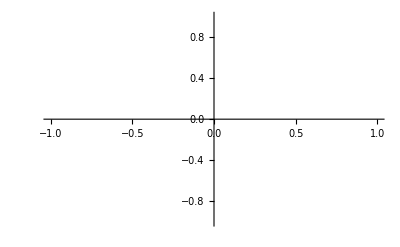

```mathematica
whitePlot=If[myWhiteColorParameters≠{},Show[Table[{myWhiteColorParameters[[myt,All,13;;14]],myWhiteColorParameters[[myt,All,15;;16]],myWhiteColorParameters[[myt,All,17;;18]]}//ListPlot[#,Joined->True,PlotStyle->{LightGray}]&,{myt,1,Length[myWhiteColorParameters],1}],PlotRange->{{0,512},{0,512}},Frame->True,AxesOrigin->{0,0},AspectRatio->{1,1}],
{{0,0}}//ListPlot[#,Joined->True,PlotStyle->{LightGray}]&
]
```

```mathematica
whitePlot>>analysisFolder<>"_whitePlot.dat";
```

#### Yellow File

```mathematica
redTracksWOff=myRedAllParameters//Cases[#,x_/;x[[21]]==1&&x[[22]]==1&&x[[23]]==0]&//SplitBy[#,First]&;
greenTracksW=myGreenAllParameters//Cases[#,x_/;x[[21]]==1&&x[[22]]==1&&x[[23]]==0]&//SplitBy[#,First]&;
```

```mathematica
redTracksW=redTracksWOff;
redTracksW⟦All,All,3;;4⟧=myTfFunc/@redTracksW⟦All,All,3;;4⟧;
```

Find Green/Red links:

```mathematica
myWGRLink=Table[
tempTrack1=greenTracksW⟦i,All,1;;7⟧;
tempTrack2=redTracksW⟦j,All,1;;7⟧;
FindOverlapDist[tempTrack1,tempTrack2,minOverlapTime],{i,1,Length@greenTracksW,1},{j,1,Length@redTracksW,1}];
myWGRLinkList=CrossPairFinder[Position[myWGRLink,x_/;0≤x<maxOverlapDistance]];
```

```mathematica
myWGRLinkList
```

{{{1},{1}},{{2},{2}}}

Find Red/Green/Blue Links by linking Green/Red and Green/Blue:

```mathematica
RGBLinks=Table[{myWGRLinkList[[i,2,1]],myWGRLinkList[[i,1,1]],""},{i,1,Length[myWGRLinkList],1}]
```

{{1,1,},{2,2,}}

```mathematica
Clear[minTR,minTG,minTB,maxTR,maxTG,maxTB,myTRange,startRed,endRed,curRed,curGreen,curBlue];
listHead={"TrackN_Red","TrackN_Green","TrackN_Blue","FrameN","I_Red","I_Green","I_Blue","Dist_RG", "Dist_RB","Dist_GB","Step","MSD","X_Red","Y_Red","X_Green","Y_Green","X_Blue","Y_Blue","(dx_Red^2+dy_Red^2)^1/2","(dx_Green^2+dy_Green^2)^1/2","(dx_Blue^2+dy_Blue^2)^1/2"};
(*i is the White Track Number iterator*)
(*j is the Frame Number iterator, i.e. time*)
(*This is the range of frames that all tracks have*)
myYellowColorParameters=Table[
minTR=Min[redTracksW⟦RGBLinks⟦i,1⟧,All,2⟧];
minTG=Min[greenTracksW⟦RGBLinks⟦i,2⟧,All,2⟧];
maxTR=Max[redTracksW⟦RGBLinks⟦i,1⟧,All,2⟧];
maxTG=Max[greenTracksW⟦RGBLinks⟦i,2⟧,All,2⟧];
myTRange={Max[{minTR,minTG}],Min[{maxTR,maxTG}]}; (*This is the range of frames that all tracks have*)
startRed=Cases[redTracksW⟦RGBLinks⟦i,1⟧⟧,x_/;x⟦2⟧==myTRange⟦1⟧];(*First frame*)
endRed=Cases[redTracksW⟦RGBLinks⟦i,1⟧⟧,x_/;x⟦2⟧==myTRange⟦2⟧]; (*Last frame*)
Table[
curRed=Cases[redTracksW⟦RGBLinks⟦i,1⟧⟧,x_/;j≤x⟦2⟧≤j+1]; (*current frame*)
curGreen=Cases[greenTracksW⟦RGBLinks⟦i,2⟧⟧,x_/;j≤x⟦2⟧≤j+1]; (*current frame*)
(*Just in case red/green/blue couldn't be tracked or blinked in this frame*)
If[curRed≠{}&&curGreen≠{},  
(*OUTPUT COLUMNS FOR FILE*)
{curRed⟦1,1⟧,
curGreen⟦1,1⟧,
"",curRed⟦1,2⟧, curRed⟦1,5⟧,curGreen⟦1,5⟧,0, EuclideanDistance[curRed⟦1,3;;4⟧,curGreen⟦1,3;;4⟧],"","",If[Length[curRed]==2, EuclideanDistance[curRed⟦1,3;;4⟧,curRed⟦2,3;;4⟧],""],EuclideanDistance[curRed⟦1,3;;4⟧,startRed⟦1,3;;4⟧]^2,curRed⟦1,3⟧,curRed⟦1,4⟧,curGreen⟦1,3⟧,curGreen⟦1,4⟧,"","",
√((curRed⟦1,10⟧-curRed⟦1,9⟧)^2+(curRed⟦1,12⟧-curRed⟦1,11⟧)^2)//N,
√((curGreen⟦1,10⟧-curGreen⟦1,9⟧)^2+(curGreen⟦1,12⟧-curGreen⟦1,11⟧)^2)//N,""
}],{j,myTRange⟦1⟧,myTRange⟦2⟧,1}]//DeleteCases[#,Null]&,{i,1,Length[RGBLinks],1}];
```

```mathematica
myYellowColorParameters>>analysisFolder<>"_FixedSigmaYellowColorParameters.dat";
```

```mathematica
Export[analysisFolder<>"_FixedSigmaYellowColorParameters.xlsx",Prepend[myYellowColorParameters//Flatten[#,1]&,listHead]]
```

C:\Users\tim_s\Documents\_mirroredX\_Fixie\20170929_G3BP1_U2OS_SG\KDM5B\Plate 3\Post-stress plus DBeQ\Analysis\MAX_Cell07_stressDBeQ_FixedSigmaYellowColorParameters.xlsx

```mathematica
mycutoff=90;
(DeleteCases[myYellowColorParameters,x_/;Length[x]<mycutoff])[[1;;All,1;;mycutoff,12]]//ListLogPlot[#,Joined->True,PlotRange->{All,All}]&
```

ListLogPlot::argx: ListLogPlot called with 0 arguments; 1 argument is expected.

General::stop: Further output of ListLogPlot::argx will be suppressed during this calculation.

ListLogPlot[{},Joined→True,PlotRange→{All,All}]

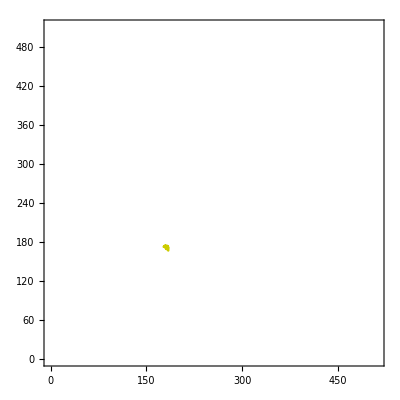

```mathematica
yellowPlot=If[myYellowColorParameters≠{},Show[Table[{myYellowColorParameters[[myt,All,13;;14]],myYellowColorParameters[[myt,All,15;;16]]}//ListPlot[#,Joined->True,PlotStyle->{Darker[Yellow,0.2]}]&,{myt,1,Length[myYellowColorParameters],1}],PlotRange->{{0,512},{0,512}},Frame->True,AxesOrigin->{0,0},AspectRatio->{1,1}],
{{0,0}}//ListPlot[#,Joined->True,PlotStyle->{Yellow}]&
]
```

```mathematica
yellowPlot>>analysisFolder<>"_yellowPlot.dat";
```

#### Purple File

```mathematica
redTracksWOff=myRedAllParameters//Cases[#,x_/;x[[21]]==1&&x[[22]]==0&&x[[23]]==1]&//SplitBy[#,First]&;
blueTracksW=myBlueAllParameters//Cases[#,x_/;x[[21]]==1&&x[[22]]==0&&x[[23]]==1]&//SplitBy[#,First]&;
```

```mathematica
redTracksW=redTracksWOff;
redTracksW⟦All,All,3;;4⟧=myTfFunc/@redTracksW⟦All,All,3;;4⟧;
```

Find Red/Blue links:

```mathematica
myWRBLink=Table[
tempTrack1=redTracksW⟦i,All,1;;7⟧;
tempTrack2=blueTracksW⟦j,All,1;;7⟧;
FindOverlapDist[tempTrack1,tempTrack2,minOverlapTime],{i,1,Length@redTracksW,1},{j,1,Length@blueTracksW,1}];
myWRBLinkList=CrossPairFinder[Position[myWRBLink,x_/;0≤x<maxOverlapDistance]];
```

```mathematica
RGBLinks=Table[{myWRBLinkList[[i,1,1]],"",myWRBLinkList[[i,2,1]]},{i,1,Length[myWRBLinkList],1}]
```

{}

```mathematica
Clear[minTR,minTG,minTB,maxTR,maxTG,maxTB,myTRange,startRed,endRed,curRed,curGreen,curBlue];
listHead={"TrackN_Red","TrackN_Green","TrackN_Blue","FrameN","I_Red","I_Green","I_Blue","Dist_RG", "Dist_RB","Dist_GB","Step","MSD","X_Red","Y_Red","X_Green","Y_Green","X_Blue","Y_Blue","(dx_Red^2+dy_Red^2)^1/2","(dx_Green^2+dy_Green^2)^1/2","(dx_Blue^2+dy_Blue^2)^1/2"};
(*i is the White Track Number iterator*)
(*j is the Frame Number iterator, i.e. time*)
(*This is the range of frames that all tracks have*)
myPurpleColorParameters=Table[
minTR=Min[redTracksW⟦RGBLinks⟦i,1⟧,All,2⟧];
minTB=Min[blueTracksW⟦RGBLinks⟦i,3⟧,All,2⟧];
maxTR=Max[redTracksW⟦RGBLinks⟦i,1⟧,All,2⟧];
maxTB=Max[blueTracksW⟦RGBLinks⟦i,3⟧,All,2⟧];
myTRange={Max[{minTR,minTB}],Min[{maxTR,maxTB}]}; (*This is the range of frames that all tracks have*)
startRed=Cases[redTracksW⟦RGBLinks⟦i,1⟧⟧,x_/;x⟦2⟧==myTRange⟦1⟧];(*First frame*)
endRed=Cases[redTracksW⟦RGBLinks⟦i,1⟧⟧,x_/;x⟦2⟧==myTRange⟦2⟧]; (*Last frame*)
Table[
curRed=Cases[redTracksW⟦RGBLinks⟦i,1⟧⟧,x_/;j≤x⟦2⟧≤j+1]; (*current frame*)
curBlue=Cases[blueTracksW⟦RGBLinks⟦i,3⟧⟧,x_/;j≤x⟦2⟧≤j+1]; (*current frame*)
(*Just in case red/green/blue couldn't be tracked or blinked in this frame*)
If[curRed≠{}&&curBlue≠{},  
(*OUTPUT COLUMNS FOR FILE*)
{curRed⟦1,1⟧,
"",
curBlue⟦1,1⟧,curRed⟦1,2⟧, curRed⟦1,5⟧,0,curBlue⟦1,5⟧,"",EuclideanDistance[curRed⟦1,3;;4⟧,curBlue⟦1,3;;4⟧],"",If[Length[curRed]==2, EuclideanDistance[curRed⟦1,3;;4⟧,curRed⟦2,3;;4⟧],""],EuclideanDistance[curRed⟦1,3;;4⟧,startRed⟦1,3;;4⟧]^2,curRed⟦1,3⟧,curRed⟦1,4⟧,"","",curBlue⟦1,3⟧,curBlue⟦1,4⟧,
√((curRed⟦1,10⟧-curRed⟦1,9⟧)^2+(curRed⟦1,12⟧-curRed⟦1,11⟧)^2)//N,
"",√((curBlue⟦1,10⟧-curBlue⟦1,9⟧)^2+(curBlue⟦1,12⟧-curBlue⟦1,11⟧)^2)//N
}],{j,myTRange⟦1⟧,myTRange⟦2⟧,1}]//DeleteCases[#,Null]&,{i,1,Length[RGBLinks],1}];
```

```mathematica
myPurpleColorParameters>>analysisFolder<>"_FixedSigmaPurpleColorParameters.dat";
```

```mathematica
Export[analysisFolder<>"_FixedSigmaPurpleColorParameters.xlsx",Prepend[myPurpleColorParameters//Flatten[#,1]&,listHead]]
```

C:\Users\tim_s\Documents\_mirroredX\_Fixie\20170929_G3BP1_U2OS_SG\KDM5B\Plate 3\Post-stress plus DBeQ\Analysis\MAX_Cell07_stressDBeQ_FixedSigmaPurpleColorParameters.xlsx

```mathematica
(DeleteCases[myPurpleColorParameters,x_/;Length[x]<100])[[1;;All,1;;All,12]]//ListPlot[#,Joined->True,PlotRange->All]&
```

-Graphics-

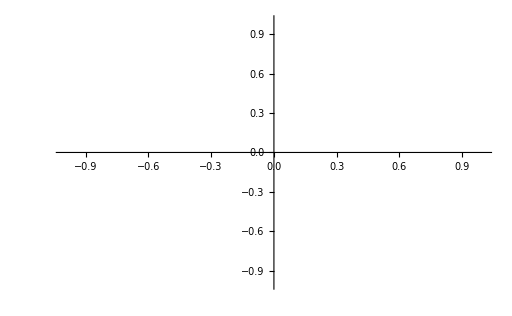

```mathematica
purplePlot=If[myPurpleColorParameters≠{},Show[Table[{myPurpleColorParameters[[myt,All,13;;14]],myPurpleColorParameters[[myt,All,17;;18]]}//ListPlot[#,Joined->True,PlotStyle->{Purple}]&,{myt,1,Length[myPurpleColorParameters],1}],PlotRange->{{0,512},{0,512}},Frame->True,AxesOrigin->{0,0},AspectRatio->{1,1}],
{{0,0}}//ListPlot[#,Joined->True,PlotStyle->{Purple}]&
]
```

```mathematica
purplePlot>>analysisFolder<>"_purplePlot.dat";
```

#### Cyan File

```mathematica
greenTracksW=myGreenAllParameters//Cases[#,x_/;x[[21]]==0&&x[[22]]==1&&x[[23]]==1]&//SplitBy[#,First]&;
blueTracksW=myBlueAllParameters//Cases[#,x_/;x[[21]]==0&&x[[22]]==1&&x[[23]]==1]&//SplitBy[#,First]&;
```

Find Green/Blue links:

```mathematica
myWGBLink=Table[
tempTrack1=greenTracksW⟦i,All,1;;7⟧;
tempTrack2=blueTracksW⟦j,All,1;;7⟧;
FindOverlapDist[tempTrack1,tempTrack2,minOverlapTime],{i,1,Length@greenTracksW,1},{j,1,Length@blueTracksW,1}];
myWGBLinkList=CrossPairFinder[Position[myWGBLink,x_/;0≤x<maxOverlapDistance]]
```

{}

```mathematica
RGBLinks=Table[{"",myWGBLinkList[[i,1,1]],myWGBLinkList[[i,2,1]]},{i,1,Length[myWGBLinkList],1}]
```

{}

```mathematica
Clear[minTR,minTG,minTB,maxTR,maxTG,maxTB,myTRange,startRed,endRed,curRed,curGreen,curBlue];
listHead={"TrackN_Red","TrackN_Green","TrackN_Blue","FrameN","I_Red","I_Green","I_Blue","Dist_RG", "Dist_RB","Dist_GB","Step","MSD","X_Red","Y_Red","X_Green","Y_Green","X_Blue","Y_Blue","(dx_Red^2+dy_Red^2)^1/2","(dx_Green^2+dy_Green^2)^1/2","(dx_Blue^2+dy_Blue^2)^1/2"};
(*i is the White Track Number iterator*)
(*j is the Frame Number iterator, i.e. time*)
(*This is the range of frames that all tracks have*)
myCyanColorParameters=Table[
minTG=Min[greenTracksW⟦RGBLinks⟦i,2⟧,All,2⟧];
minTB=Min[blueTracksW⟦RGBLinks⟦i,3⟧,All,2⟧];
maxTG=Max[greenTracksW⟦RGBLinks⟦i,2⟧,All,2⟧];
maxTB=Max[blueTracksW⟦RGBLinks⟦i,3⟧,All,2⟧];
myTRange={Max[{minTG,minTB}],Min[{maxTG,maxTB}]}; (*This is the range of frames that all tracks have*)
startBlue=Cases[blueTracksW⟦RGBLinks⟦i,3⟧⟧,x_/;x⟦2⟧==myTRange⟦1⟧];(*First frame*)
endBlue=Cases[blueTracksW⟦RGBLinks⟦i,3⟧⟧,x_/;x⟦2⟧==myTRange⟦2⟧]; (*Last frame*)
Table[
curGreen=Cases[greenTracksW⟦RGBLinks⟦i,2⟧⟧,x_/;j≤x⟦2⟧≤j+1]; (*current frame*)
curBlue=Cases[blueTracksW⟦RGBLinks⟦i,3⟧⟧,x_/;j≤x⟦2⟧≤j+1]; (*current frame*)
(*Just in case red/green/blue couldn't be tracked or blinked in this frame*)
If[curGreen≠{}&&curBlue≠{},  
(*OUTPUT COLUMNS FOR FILE*)
{"",
curGreen⟦1,1⟧,
curBlue⟦1,1⟧,curBlue⟦1,2⟧,0,curGreen⟦1,5⟧,curBlue⟦1,5⟧, "","",EuclideanDistance[curGreen⟦1,3;;4⟧,curBlue⟦1,3;;4⟧],If[Length[curBlue]==2, EuclideanDistance[curBlue⟦1,3;;4⟧,curBlue⟦2,3;;4⟧],""],EuclideanDistance[curBlue⟦1,3;;4⟧,startBlue⟦1,3;;4⟧]^2,"","",curGreen⟦1,3⟧,curGreen⟦1,4⟧,curBlue⟦1,3⟧,curBlue⟦1,4⟧,
"",
√((curGreen⟦1,10⟧-curGreen⟦1,9⟧)^2+(curGreen⟦1,12⟧-curGreen⟦1,11⟧)^2)//N,√((curBlue⟦1,10⟧-curBlue⟦1,9⟧)^2+(curBlue⟦1,12⟧-curBlue⟦1,11⟧)^2)//N
}],{j,myTRange⟦1⟧,myTRange⟦2⟧,1}]//DeleteCases[#,Null]&,{i,1,Length[RGBLinks],1}];
```

```mathematica
myCyanColorParameters>>analysisFolder<>"_FixedSigmaCyanColorParameters.dat";
```

```mathematica
Export[analysisFolder<>"_FixedSigmaCyanColorParameters.xlsx",Prepend[myCyanColorParameters//Flatten[#,1]&,listHead]]
```

C:\Users\tim_s\Documents\_mirroredX\_Fixie\20170929_G3BP1_U2OS_SG\KDM5B\Plate 3\Post-stress plus DBeQ\Analysis\MAX_Cell07_stressDBeQ_FixedSigmaCyanColorParameters.xlsx

```mathematica
(DeleteCases[myCyanColorParameters,x_/;Length[x]<10])[[1;;All,1;;All,12]]//ListLogPlot[#,Joined->True,PlotRange->All]&
```

ListLogPlot::argx: ListLogPlot called with 0 arguments; 1 argument is expected.

General::stop: Further output of ListLogPlot::argx will be suppressed during this calculation.

ListLogPlot[{},Joined→True,PlotRange→All]

```mathematica
cyanPlot=If[myCyanColorParameters≠{},Show[Table[{myCyanColorParameters[[myt,All,15;;16]],myCyanColorParameters[[myt,All,17;;18]]}//ListPlot[#,Joined->True,PlotStyle->{Cyan}]&,{myt,1,Length[myCyanColorParameters],1}],PlotRange->{{0,512},{0,512}},Frame->True,AxesOrigin->{0,0},AspectRatio->{1,1}],
{{0,0}}//ListPlot[#,Joined->True,PlotStyle->{Cyan}]&
]
```

-Graphics-

```mathematica
cyanPlot>>analysisFolder<>"_cyanPlot.dat";
```

#### Red Only File

```mathematica
redTracksWOff=myRedAllParameters//Cases[#,x_/;x[[21]]==1&&x[[22]]==0&&x[[23]]==0]&//SplitBy[#,First]&;
```

```mathematica
redTracksW=redTracksWOff;
redTracksW⟦All,All,3;;4⟧=myTfFunc/@redTracksW⟦All,All,3;;4⟧;
```

```mathematica
Clear[minTR,minTG,minTB,maxTR,maxTG,maxTB,myTRange,startRed,endRed,curRed,curGreen,curBlue];
listHead={"TrackN_Red","TrackN_Green","TrackN_Blue","FrameN","I_Red","I_Green","I_Blue","Dist_RG", "Dist_RB","Dist_GB","Step","MSD","X_Red","Y_Red","X_Green","Y_Green","X_Blue","Y_Blue","(dx_Red^2+dy_Red^2)^1/2","(dx_Green^2+dy_Green^2)^1/2","(dx_Blue^2+dy_Blue^2)^1/2"};
(*i is the White Track Number iterator*)
(*j is the Frame Number iterator, i.e. time*)
(*This is the range of frames that all tracks have*)
myRedOnlyColorParameters=Table[
minTR=Min[redTracksW⟦i,All,2⟧];
maxTR=Max[redTracksW⟦i,All,2⟧];
myTRange={Max[{minTR}],Min[{maxTR}]}; (*This is the range of frames that all tracks have*)
startRed=Cases[redTracksW⟦i⟧,x_/;x⟦2⟧==myTRange⟦1⟧];(*First frame*)
endRed=Cases[redTracksW⟦i⟧,x_/;x⟦2⟧==myTRange⟦2⟧]; (*Last frame*)
Table[
curRed=Cases[redTracksW⟦i⟧,x_/;j≤x⟦2⟧≤j+1]; (*current frame*)
(*Just in case red/green/blue couldn't be tracked or blinked in this frame*)
If[curRed≠{},  
(*OUTPUT COLUMNS FOR FILE*)
{curRed⟦1,1⟧,
"",
"",curRed⟦1,2⟧, curRed⟦1,5⟧,0,0,"","","",If[Length[curRed]==2, EuclideanDistance[curRed⟦1,3;;4⟧,curRed⟦2,3;;4⟧],""],EuclideanDistance[curRed⟦1,3;;4⟧,startRed⟦1,3;;4⟧]^2,curRed⟦1,3⟧,curRed⟦1,4⟧,"","","","",
√((curRed⟦1,10⟧-curRed⟦1,9⟧)^2+(curRed⟦1,12⟧-curRed⟦1,11⟧)^2)//N,
"",""
}],{j,myTRange⟦1⟧,myTRange⟦2⟧,1}]//DeleteCases[#,Null]&,{i,1,Length[redTracksW],1}];
```

```mathematica
myRedOnlyColorParameters>>analysisFolder<>"_FixedSigmaRedOnlyColorParameters.dat";
```

```mathematica
Export[analysisFolder<>"_FixedRedOnlyColorParameters.xlsx",Prepend[myRedOnlyColorParameters//Flatten[#,1]&,listHead]]
```

C:\Users\tim_s\Documents\_mirroredX\_Fixie\20170929_G3BP1_U2OS_SG\KDM5B\Plate 3\Post-stress plus DBeQ\Analysis\MAX_Cell07_stressDBeQ_FixedRedOnlyColorParameters.xlsx

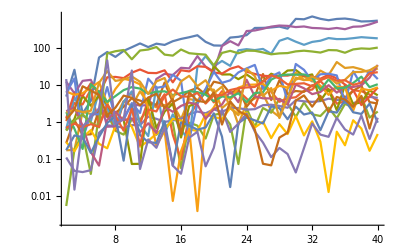

```mathematica
(DeleteCases[myRedOnlyColorParameters,x_/;Length[x]<40])[[1;;All,1;;40,12]]//ListLogPlot[#,Joined->True,PlotRange->All]&
```

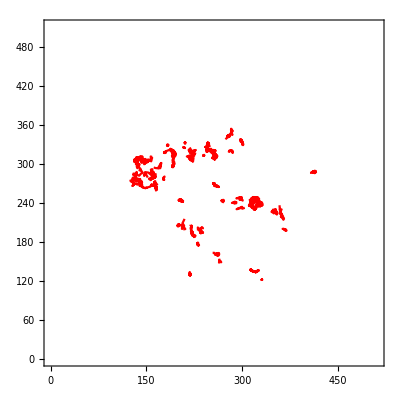

```mathematica
redPlot=If[myRedOnlyColorParameters≠{},Show[Table[{myRedOnlyColorParameters[[myt,All,13;;14]],myRedOnlyColorParameters[[myt,All,15;;16]],myRedOnlyColorParameters[[myt,All,17;;18]]}//ListPlot[#,Joined->True,PlotStyle->{Red}]&,{myt,1,Length[myRedOnlyColorParameters],1}],PlotRange->{{0,512},{0,512}},Frame->True,AxesOrigin->{0,0},AspectRatio->{1,1}],
{{0,0}}//ListPlot[#,Joined->True,PlotStyle->{Red}]&
]
```

```mathematica
redPlot>>analysisFolder<>"_redPlot.dat";
```

#### Green Only File

Using red as a dummy variable here, so a little confusing:

```mathematica
redTracksWOff=myGreenAllParameters//Cases[#,x_/;x[[21]]==0&&x[[22]]==1&&x[[23]]==0]&//SplitBy[#,First]&;
```

```mathematica
redTracksW=redTracksWOff;
redTracksW⟦All,All,3;;4⟧=redTracksW⟦All,All,3;;4⟧;
```

```mathematica
Clear[minTR,minTG,minTB,maxTR,maxTG,maxTB,myTRange,startRed,endRed,curRed,curGreen,curBlue];
listHead={"TrackN_Red","TrackN_Green","TrackN_Blue","FrameN","I_Red","I_Green","I_Blue","Dist_RG", "Dist_RB","Dist_GB","Step","MSD","X_Red","Y_Red","X_Green","Y_Green","X_Blue","Y_Blue","(dx_Red^2+dy_Red^2)^1/2","(dx_Green^2+dy_Green^2)^1/2","(dx_Blue^2+dy_Blue^2)^1/2"};
(*i is the White Track Number iterator*)
(*j is the Frame Number iterator, i.e. time*)
(*This is the range of frames that all tracks have*)
myGreenOnlyColorParameters=Table[
minTR=Min[redTracksW⟦i,All,2⟧];
maxTR=Max[redTracksW⟦i,All,2⟧];
myTRange={Max[{minTR}],Min[{maxTR}]}; (*This is the range of frames that all tracks have*)
startRed=Cases[redTracksW⟦i⟧,x_/;x⟦2⟧==myTRange⟦1⟧];(*First frame*)
endRed=Cases[redTracksW⟦i⟧,x_/;x⟦2⟧==myTRange⟦2⟧]; (*Last frame*)
Table[
curRed=Cases[redTracksW⟦i⟧,x_/;j≤x⟦2⟧≤j+1]; (*current frame*)
(*Just in case red/green/blue couldn't be tracked or blinked in this frame*)
If[curRed≠{},  
(*OUTPUT COLUMNS FOR FILE*)
{"",
curRed⟦1,1⟧,
"",curRed⟦1,2⟧,0,curRed⟦1,5⟧,0,"","","",If[Length[curRed]==2, EuclideanDistance[curRed⟦1,3;;4⟧,curRed⟦2,3;;4⟧],""],EuclideanDistance[curRed⟦1,3;;4⟧,startRed⟦1,3;;4⟧]^2,"","",curRed⟦1,3⟧,curRed⟦1,4⟧,"","",
"",
√((curRed⟦1,10⟧-curRed⟦1,9⟧)^2+(curRed⟦1,12⟧-curRed⟦1,11⟧)^2)//N,""
}],{j,myTRange⟦1⟧,myTRange⟦2⟧,1}]//DeleteCases[#,Null]&,{i,1,Length[redTracksW],1}];
```

```mathematica
myGreenOnlyColorParameters>>analysisFolder<>"_FixedSigmaGreenOnlyColorParameters.dat";
```

```mathematica
Export[analysisFolder<>"_FixedGreenOnlyColorParameters.xlsx",Prepend[myGreenOnlyColorParameters//Flatten[#,1]&,listHead]]
```

C:\Users\tim_s\Documents\_mirroredX\_Fixie\20170929_G3BP1_U2OS_SG\KDM5B\Plate 3\Post-stress plus DBeQ\Analysis\MAX_Cell07_stressDBeQ_FixedGreenOnlyColorParameters.xlsx

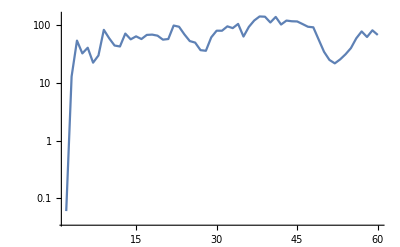

```mathematica
(DeleteCases[myGreenOnlyColorParameters,x_/;Length[x]<60])[[1;;All,1;;60,12]]//ListLogPlot[#,Joined->True,PlotRange->All]&
```

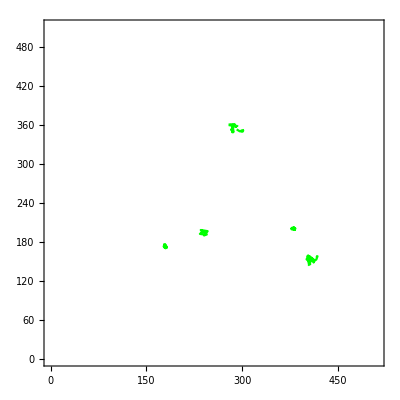

```mathematica
greenPlot=If[myGreenOnlyColorParameters≠{},Show[Table[{myGreenOnlyColorParameters[[myt,All,13;;14]],myGreenOnlyColorParameters[[myt,All,15;;16]],myGreenOnlyColorParameters[[myt,All,17;;18]]}//ListPlot[#,Joined->True,PlotStyle->{Green}]&,{myt,1,Length[myGreenOnlyColorParameters],1}],PlotRange->{{0,512},{0,512}},Frame->True,AxesOrigin->{0,0},AspectRatio->{1,1}],
{{0,0}}//ListPlot[#,Joined->True,PlotStyle->{Green}]&
]
```

```mathematica
greenPlot>>analysisFolder<>"_greenOnlyPlot.dat";
```

#### Blue Only File

Using red as a dummy variable here, so a little confusing:

```mathematica
redTracksWOff=myBlueAllParameters//Cases[#,x_/;x[[21]]==0&&x[[22]]==0&&x[[23]]==1]&//SplitBy[#,First]&;
```

```mathematica
redTracksW=redTracksWOff;
redTracksW⟦All,All,3;;4⟧=redTracksW⟦All,All,3;;4⟧;
```

```mathematica
Clear[minTR,minTG,minTB,maxTR,maxTG,maxTB,myTRange,startRed,endRed,curRed,curGreen,curBlue];
listHead={"TrackN_Red","TrackN_Green","TrackN_Blue","FrameN","I_Red","I_Green","I_Blue","Dist_RG", "Dist_RB","Dist_GB","Step","MSD","X_Red","Y_Red","X_Green","Y_Green","X_Blue","Y_Blue","(dx_Red^2+dy_Red^2)^1/2","(dx_Green^2+dy_Green^2)^1/2","(dx_Blue^2+dy_Blue^2)^1/2"};
(*i is the White Track Number iterator*)
(*j is the Frame Number iterator, i.e. time*)
(*This is the range of frames that all tracks have*)
myBlueOnlyColorParameters=Table[
minTR=Min[redTracksW⟦i,All,2⟧];
maxTR=Max[redTracksW⟦i,All,2⟧];
myTRange={Max[{minTR}],Min[{maxTR}]}; (*This is the range of frames that all tracks have*)
startRed=Cases[redTracksW⟦i⟧,x_/;x⟦2⟧==myTRange⟦1⟧];(*First frame*)
endRed=Cases[redTracksW⟦i⟧,x_/;x⟦2⟧==myTRange⟦2⟧]; (*Last frame*)
Table[
curRed=Cases[redTracksW⟦i⟧,x_/;j≤x⟦2⟧≤j+1]; (*current frame*)
(*Just in case red/green/blue couldn't be tracked or blinked in this frame*)
If[curRed≠{},  
(*OUTPUT COLUMNS FOR FILE*)
{"",
"",
curRed⟦1,1⟧,curRed⟦1,2⟧,0,0,curRed⟦1,5⟧,"","","",If[Length[curRed]==2, EuclideanDistance[curRed⟦1,3;;4⟧,curRed⟦2,3;;4⟧],""],EuclideanDistance[curRed⟦1,3;;4⟧,startRed⟦1,3;;4⟧]^2,"","","","",curRed⟦1,3⟧,curRed⟦1,4⟧,
"",
"",√((curRed⟦1,10⟧-curRed⟦1,9⟧)^2+(curRed⟦1,12⟧-curRed⟦1,11⟧)^2)//N
}],{j,myTRange⟦1⟧,myTRange⟦2⟧,1}]//DeleteCases[#,Null]&,{i,1,Length[redTracksW],1}];
```

```mathematica
myBlueOnlyColorParameters>>analysisFolder<>"_FixedSigmaBlueOnlyColorParameters.dat";
```

```mathematica
Export[analysisFolder<>"_FixedBlueOnlyColorParameters.xlsx",Prepend[myBlueOnlyColorParameters//Flatten[#,1]&,listHead]]
```

C:\Users\tim_s\Documents\_mirroredX\_Fixie\20170929_G3BP1_U2OS_SG\KDM5B\Plate 3\Post-stress plus DBeQ\Analysis\MAX_Cell07_stressDBeQ_FixedBlueOnlyColorParameters.xlsx

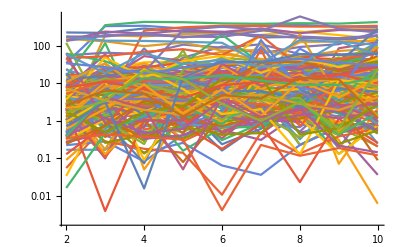

```mathematica
(DeleteCases[myBlueOnlyColorParameters,x_/;Length[x]<10])[[1;;All,1;;10,12]]//ListLogPlot[#,Joined->True,PlotRange->All]&
```

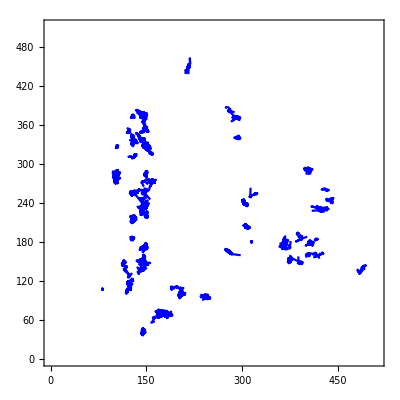

```mathematica
bluePlot=If[myBlueOnlyColorParameters≠{},Show[Table[{myBlueOnlyColorParameters[[myt,All,13;;14]],myBlueOnlyColorParameters[[myt,All,15;;16]],myBlueOnlyColorParameters[[myt,All,17;;18]]}//ListPlot[#,Joined->True,PlotStyle->{Blue}]&,{myt,1,Length[myBlueOnlyColorParameters],1}],PlotRange->{{0,512},{0,512}},Frame->True,AxesOrigin->{0,0},AspectRatio->{1,1}],
{{0,0}}//ListPlot[#,Joined->True,PlotStyle->{Blue}]&
]
```

86

```mathematica
bluePlot>>analysisFolder<>"_blueOnlyPlot.dat";
```

#### Summary

```mathematica
myRainbowPlot=Show[{myCytMask-myNucMask,greenPlot,bluePlot,redPlot,whitePlot,purplePlot,cyanPlot,yellowPlot},ImageSize->300]
```

-Graphics-

```mathematica
Export[analysisFolder<>"_rainbowPlot.tif",myRainbowPlot];
```

```mathematica
myColorParametersList={myWhiteColorParameters,myRedOnlyColorParameters,myGreenOnlyColorParameters,myBlueOnlyColorParameters,myWhiteColorParameters,myYellowColorParameters,myPurpleColorParameters,myCyanColorParameters};
```

```mathematica
myColorsList={"White","Red","Green","Blue","LightGray","Darker[Yellow,0.2]","Purple","Cyan"};
```

```mathematica
myColorsListb={White,Red,Green,Blue,LightGray,Darker[Yellow,0.2],Purple,Cyan};
```

Part::partd: Part specification Null⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

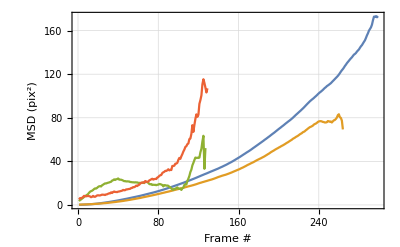
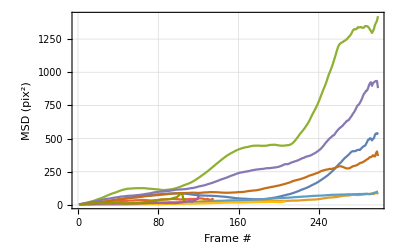
Null⟦2⟧ | -Graphics- | Null⟦2⟧ | -Graphics-
Null⟦2⟧ | Null⟦2⟧ | Null⟦2⟧ | Null⟦2⟧

```mathematica
Grid[Partition[tt=DeleteCases[Table[MyMSDPlotter[Cases[myColorParametersList⟦i⟧,x_/;Length[x]>100],myColorsList⟦i⟧][[2]],{i,1,Length[myColorsList],1}],Null],4]]
```

Part::partd: Part specification Null⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

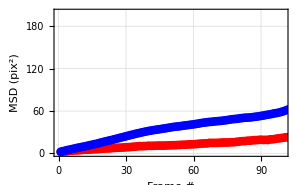

```mathematica
Show[DeleteCases[Table[MyMSDPlotter[Cases[myColorParametersList⟦i⟧,x_/;Length[x]>100],myColorsList⟦i⟧][[1]],{i,1,Length[myColorsList],1}],Null[[1]]],PlotRange->{{0,100},{0, 200}},ImageSize->300]
```

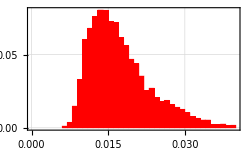
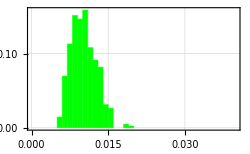
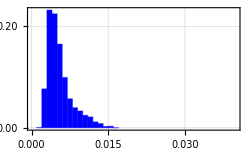
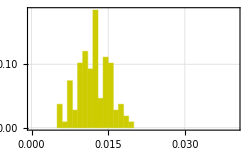
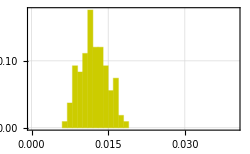
-Graphics- |  | 
 | -Graphics- | 
 |  | -Graphics-
 |  | 
-Graphics- | -Graphics- | 
 |  | 
 |  |

```mathematica
{Table[MyHistogramPlotter[myColorParametersList⟦i⟧,listHead,5,myColorsListb⟦i⟧,Table[i,{i,0,0.04,0.001}]],{i,2,Length[myColorsListb],1}],
Table[MyHistogramPlotter[myColorParametersList⟦i⟧,listHead,6,myColorsListb⟦i⟧,Table[i,{i,0,0.04,0.001}]],{i,2,Length[myColorsListb],1}],
Table[MyHistogramPlotter[myColorParametersList⟦i⟧,listHead,7,myColorsListb⟦i⟧,Table[i,{i,0,0.04,0.001}]],{i,2,Length[myColorsListb],1}]
}//Transpose//Grid
```

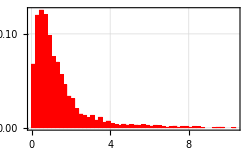
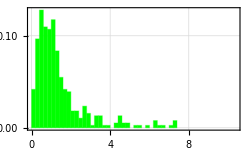
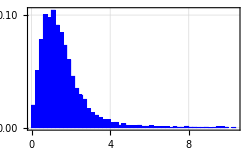
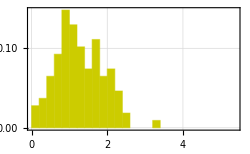
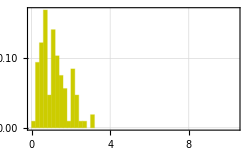
|  |  | -Graphics-
 |  |  | -Graphics-
 |  |  | -Graphics-
 |  |  | 
-Graphics- |  |  | -Graphics-
 |  |  | 
 |  |  |

```mathematica
{Table[MyHistogramPlotter[myColorParametersList⟦i⟧,listHead,8,myColorsListb⟦i⟧,Table[i,{i,0,5.5,0.2}]],{i,2,Length[myColorsListb],1}],
Table[MyHistogramPlotter[myColorParametersList⟦i⟧,listHead,9,myColorsListb⟦i⟧,Table[i,{i,0,10.5,0.2}]],{i,2,Length[myColorsListb],1}],
Table[MyHistogramPlotter[myColorParametersList⟦i⟧,listHead,10,myColorsListb⟦i⟧,Table[i,{i,0,5.5,0.2}]],{i,2,Length[myColorsListb],1}],
Table[MyHistogramPlotter[myColorParametersList⟦i⟧,listHead,11,myColorsListb⟦i⟧,Table[i,{i,0,10.5,0.2}]],{i,2,Length[myColorsListb],1}]
}//Transpose//Grid
```

```mathematica
out=Table[Table[Show[Table[MyCrossCorrelatePlotter[myColorParametersList⟦i⟧,listHead,j,k,myColorsList⟦i⟧],{i,1,Length[myColorsList],1}]],{k,j+1,11}],{j,5,9}]//TableForm;
```

## Plotting data

```mathematica
(* choose the directory for all curves except for the green curve *)
{FileNameSetter[Dynamic[myDirectory1],"Directory"],Dynamic[myDirectory1]}
```

{$CellContext`mymovieOpenAll,}

```mathematica
(* choose the directory for the green curve *)
{FileNameSetter[Dynamic[myDirectory2],"Directory"],Dynamic[myDirectory2]}
```

{$CellContext`mymovieOpenAll,}

```mathematica
kpurple=FileNames["*_FixedSigmaPurpleColorParameters.dat",myDirectory1];
kblue=FileNames["*_FixedSigmaBlueOnlyColorParameters.dat",myDirectory1];
kred=FileNames["*_FixedSigmaRedOnlyColorParameters.dat",myDirectory1];
kgreentr=FileNames["*_FixedSigmaGreenOnlyColorParameters.dat",myDirectory2];
kyellow=FileNames["*_FixedSigmaYellowColorParameters.dat",myDirectory1];
```

```mathematica
listHead={"TrackN_Red","TrackN_Green","TrackN_Blue","FrameN","I_Red","I_Green","I_Blue","Dist_RG", "Dist_RB","Dist_GB","Step","MSD","X_Red","Y_Red","X_Green","Y_Green","X_Blue","Y_Blue","(dx_Red^2+dy_Red^2)^1/2","(dx_Green^2+dy_Green^2)^1/2","(dx_Blue^2+dy_Blue^2)^1/2"};
```

```mathematica
listHead[[{4,13,14,17,18,19,21}]]
```

{FrameN,X_Red,Y_Red,X_Blue,Y_Blue,(dx_Red^2+dy_Red^2)^1/2,(dx_Blue^2+dy_Blue^2)^1/2}

```mathematica
rerr=1.5;
berr=1.5;
gerr=1.5;
maxMSDT=200;
```

```mathematica
myCh1=1;
myCh2=7;
hps=DeleteCases[(Cases[#,x_/;x[[4]]<maxMSDT&&x[[21]]<berr]&/@Flatten[Table[<<(kpurple⟦i⟧),{i,myCh1,myCh2,1}],1]),x_/;Dimensions[x]=={0}];
```

```mathematica
hbs=DeleteCases[(Cases[#,x_/;x[[4]]<maxMSDT&&x[[21]]<berr]&/@Flatten[Table[<<(kblue⟦i⟧),{i,myCh1,myCh2,1}],1]),x_/;Dimensions[x]=={0}];
```

```mathematica
hrs=DeleteCases[(Cases[#,x_/;x[[4]]<maxMSDT&&x[[19]]<rerr]&/@Flatten[Table[<<(kred⟦i⟧),{i,myCh1,myCh2,1}],1]),x_/;Dimensions[x]=={0}];
```

```mathematica
hgs=DeleteCases[(Cases[#,x_/;x[[4]]<maxMSDT&&x[[20]]<berr]&/@Flatten[Table[<<(kgreentr⟦i⟧),{i,myCh1,myCh2,1}],1]),x_/;Dimensions[x]=={0}];
```

```mathematica
hys=DeleteCases[(Cases[#,x_/;x[[4]]<maxMSDT&&x[[20]]<berr]&/@Flatten[Table[<<(kyellow⟦i⟧),{i,myCh1,myCh2,1}],1]),x_/;Dimensions[x]=={0}];
```

```mathematica
hpurps=TXYDiffusionPlotter[Union/@hps⟦All,All,{4,17,18}⟧,100,Purple,6,17];
```

```mathematica
hblues=TXYDiffusionPlotter[Union/@hbs⟦All,All,{4,17,18}⟧,100,Blue,2,20];
```

```mathematica
hreds=TXYDiffusionPlotter[Union/@hrs⟦All,All,{4,13,14}⟧,100,Red,1,14];
```

```mathematica
hgreens=TXYDiffusionPlotter[Union/@hgs⟦All,All,{4,15,16}⟧,100,Green,4,20];
```

```mathematica
hyellows=TXYDiffusionPlotter[Union/@hys⟦All,All,{4,15,16}⟧,100,Darker[Yellow,0.4],7,25];
```

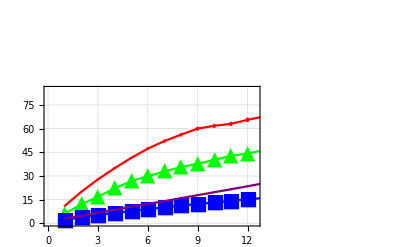

```mathematica
pMSDp={Show[{hgreens[[4]],(*hyellows[[4]],*)hblues[[4]],hreds[[4]],hpurps[[4]]},PlotRange->{{0.01,12.5},{0,85}},ImageSize->400]}
```

```mathematica
{{#⟦1,1⟧ 2, #⟦1,2⟧(.130)^2},ErrorBar[#⟦2,1⟧(.130)^2]}&/@hpurps[[2,2;;10]]
```

{{{4,0.0797914},ErrorBar[0.00445681]},{{6,0.112475},ErrorBar[0.00466334]},{{8,0.14327},ErrorBar[0.00502755]},{{10,0.17834},ErrorBar[0.00601314]},{{12,0.207945},ErrorBar[0.00603209]},{{14,0.236808},ErrorBar[0.00637831]},{{16,0.27007},ErrorBar[0.00714129]},{{18,0.300793},ErrorBar[0.00769605]},{{20,0.333025},ErrorBar[0.00834136]}}

Reading in RNA distances intra-stress granule:
myRNAtracks12dtdxdydz, myRNAtracks23dtdxdydz, and myRNAtracks13dtdxdydz acquired in the below section “Figure 4b, 4c, S3 and S4 - SG rigidity” > “Cell01 - Fig 4b, 4c and S3” > “Distance between each RNA” should be read in as d1, d2, and d3, respectively.

```mathematica
d1=<<("####_RNAtracks12_tdxdydz.m");
d2=<<("####_RNAtracks13_tdxdydz.m");
d3=<<("####_RNAtracks23_tdxdydz.m");
```

```mathematica
in1=TXYDiffusionPlotter[Union@{d1⟦All,{1,2,3}⟧,d2⟦All,{1,2,3}⟧,d3⟦All,{1,2,3}⟧},100,Darker[Gray,0.],8,25];
```

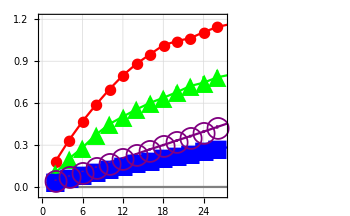

```mathematica
out3A={
(msddata1={{#⟦1,1⟧ 2, #⟦1,2⟧(.130)^2},ErrorBar[#⟦2,1⟧(.130)^2]}&/@hreds[[2,1;;All]]),(msddata1b={{#⟦1,1⟧ 2, #⟦1,2⟧(.130)^2},ErrorBar[#⟦2,1⟧(.130)^2]}&/@hgreens[[2,1;;All]]),(msddata2={{#⟦1,1⟧ 2, #⟦1,2⟧(.130)^2},ErrorBar[#⟦2,1⟧(.130)^2]}&/@hblues[[2,1;;All]]),
(msddata3={{#⟦1,1⟧ 2, #⟦1,2⟧(.130)^2},ErrorBar[#⟦2,1⟧(.130)^2]}&/@hpurps[[2,1;;All]]),(msddata4={{#⟦1,1⟧ 2, (#⟦1,2⟧(.130)^2)/2},ErrorBar[(#⟦2,1⟧(.130)^2)/2]}&/@in1[[2,1;;All]])
}//ErrorListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->{{0,27},{-.05,1.21}},PlotMarkers->{{Graphics`PlotMarkers[]⟦1,1⟧,15},{Graphics`PlotMarkers[]⟦4,1⟧,24},{Graphics`PlotMarkers[]⟦2,1⟧,24},{Graphics`PlotMarkers[]⟦6,1⟧,30},{Graphics`PlotMarkers[]⟦7,1⟧,30}},PlotLegends->{"mRNA","translating mRNA","SG","SG + mRNA","mRNA inside SG"}
,FrameLabel->{"Time (sec)","MSD (μm^2)"},BaseStyle->{FontFamily->"Arial",FontSize->14},PlotStyle->{Red,Green,Blue,Purple,Gray},ImageSize->350]&
```

```mathematica
myfits={LinearModelFit[msddata1[[1;;5,1]],x,x],LinearModelFit[msddata1b[[1;;5,1]],x,x],LinearModelFit[msddata2[[1;;5,1]],x,x],LinearModelFit[msddata3[[1;;5,1]],x,x],LinearModelFit[msddata4[[1;;5,1]],x,x]}
```

{FittedModel[0.0714391+0.0640954 x],FittedModel[0.0210823+0.0435988 x],FittedModel[0.0173055+0.0115474 x],FittedModel[0.0166576+0.0160167 x],FittedModel[0.000214364+0.0000412384 x]}

```mathematica
Dimensions/@hgreens
```

{{142,99},{120,2},{2},{2}}

```mathematica
Dimensions/@hreds
```

{{1376,99},{169,2},{2},{2}}

```mathematica
Dimensions/@hblues
```

{{1103,99},{192,2},{2},{2}}

```mathematica
Dimensions/@hpurps
```

{{93,99},{194,2},{2},{2}}

All data from 7 cells 

mRNA only: 0.016 +/- 0.004 (N=1376 tracks; not sure how many distinct mRNA)
translating mRNA: 0.011 +/- 0.002 (N=142 tracks; not sure how many distinct mRNA)
SG: 0.003 +/- 0.0006 (N = 1103 tracks)
SG + mRNA: 0.004 +/- 0.0004 (N=93 tracks)

Fitted slopes are 4D:

```mathematica
i=4;
{myfits[[i]]["ParameterConfidenceIntervals"],myfits[[i]]["ParameterConfidenceIntervals"]/4,Mean@myfits[[i]]["ParameterConfidenceIntervals"][[2]]/4,Differences@myfits[[i]]["ParameterConfidenceIntervals"][[2]]/4}
```

{{{0.0115406,0.0217746},{0.0152453,0.0167881}},{{0.00288514,0.00544365},{0.00381132,0.00419703}},0.00400417,{0.000385709}}

```mathematica
i=3;
{myfits[[i]]["ParameterConfidenceIntervals"],myfits[[i]]["ParameterConfidenceIntervals"]/4,Mean@myfits[[i]]["ParameterConfidenceIntervals"][[2]]/4,Differences@myfits[[i]]["ParameterConfidenceIntervals"][[2]]/4}
```

{{{0.00913072,0.0254803},{0.010315,0.0127798}},{{0.00228268,0.00637007},{0.00257875,0.00319495}},0.00288685,{0.000616198}}

```mathematica
i=2;
{myfits[[i]]["ParameterConfidenceIntervals"],myfits[[i]]["ParameterConfidenceIntervals"]/4,Mean@myfits[[i]]["ParameterConfidenceIntervals"][[2]]/4,Differences@myfits[[i]]["ParameterConfidenceIntervals"][[2]]/4}
```

{{{-0.00536394,0.0475285},{0.0396118,0.0475857}},{{-0.00134099,0.0118821},{0.00990296,0.0118964}},0.0108997,{0.00199346}}

```mathematica
i=1;
{myfits[[i]]["ParameterConfidenceIntervals"],myfits[[i]]["ParameterConfidenceIntervals"]/4,Mean@myfits[[i]]["ParameterConfidenceIntervals"][[2]]/4,Differences@myfits[[i]]["ParameterConfidenceIntervals"][[2]]/4}
```

{{{0.0216888,0.121189},{0.0565952,0.0715955}},{{0.00542219,0.0302974},{0.0141488,0.0178989}},0.0160238,{0.00375007}}

```mathematica
SetDirectory["C:\\Users\\tim_s\\OneDrive - Colostate\\Stasevich Lab\\Our papers\\StressGranules"]
```

C:\Users\tim_s\OneDrive - Colostate\Stasevich Lab\Our papers\StressGranules

```mathematica
Export["UpdatedKDM5B-MSD-analysis-with-translating-mRNA.emf",out3A,ImageResolution->500]
```

UpdatedKDM5B-MSD-analysis-with-translating-mRNA.emf

```mathematica
Length@hpurpleAll
```

11

```mathematica
Length@hblueAll
```

11

```mathematica
Length@hredAll
```

11

```mathematica
Length@hgs
```

10

```mathematica
Length@hps
```

13

```mathematica
Length@hbs
```

250

```mathematica
Length@hrs
```

163

## Figure 4b, 4c, S3 and S4 - SG rigidity

## Cell01 - Fig 4b, 4c and S3

### Reading in Images

```mathematica
{FileNameSetter[Dynamic[mymovie]],Dynamic[mymovie]}
```

{$CellContext`mymovieOpenAll,}

```mathematica
myColMovie=Import[mymovie]//Partition[#,3]&//Transpose;
If[DirectoryQ@(DirectoryName[mymovie]<>"Analysis\\")==False,CreateDirectory@(DirectoryName[mymovie]<>"Analysis\\")];
analysisFolder=DirectoryName[mymovie]<>"Analysis\\"<>StringDrop[StringDelete[mymovie,DirectoryName[mymovie]],-4];
```

```mathematica
my3Ddirectory=StringDelete[mymovie,"MAX_"|".tif"]<>"\\";
```

### Reading in Parameters (if parameters exist)

#### basic parameters

```mathematica
myTfFunc=<<(DirectoryName@mymovie<>"TransformationFunction.m");
```

```mathematica
mymask=Import@(analysisFolder<>"_mask.tif");
```

```mathematica
avgFrameN=<<(analysisFolder<>"_avgFrameN.dat");
myMaxN=Length@myColMovie⟦1⟧-avgFrameN+1;
myColMovieRunAv=If[avgFrameN==1,myColMovie,MovingAverage[#,avgFrameN]&/@myColMovie];
```

#### basic color parameters

```mathematica
thred=<<(analysisFolder<>"_thred.dat");
{mymaxred,thred2,bandpassred,dotsizered}=<<(analysisFolder<>"_thred2.dat");
```

```mathematica
thgreen=<<(analysisFolder<>"_thgreen.dat");
{mymaxgreen,thgreen2,bandpassgreen,dotsizegreen}=<<(analysisFolder<>"_thgreen2.dat");
```

```mathematica
thblue=<<(analysisFolder<>"_thblue.dat");
{mymaxblue,thblue2,bandpassblue,dotsizeblue}=<<(analysisFolder<>"_thblue2.dat");
```

### Make Mask

```mathematica
If[FileExistsQ[analysisFolder<>"_avg.tif"]==True,
avgImg=Import[analysisFolder<>"_avg.tif"];,
avgImg=Mean/@myColMovie;
Export[analysisFolder<>"_avg.tif",avgImg]];
If[FileExistsQ[analysisFolder<>"_max.tif"]==True,
maxImg=Import[analysisFolder<>"_max.tif"],
maxImg=ImageApply[Max,#]&/@myColMovie;
Export[analysisFolder<>"_max.tif",maxImg]];
```

```mathematica
Manipulate[maxImg⟦1⟧//ImageAdjust[#,{0,0,1},{threshold1,threshold2}]&,
Button["Choose threshold such that the shape of the cell can be visualized and CLICK",thtemp={threshold1,threshold2}],
{threshold1,0,0.2,0.001},{{threshold2,0.1},0,0.2,0.001}]
```

```mathematica
ImageAdjust[maxImg⟦2⟧,{0,0,1},thtemp]
```

```mathematica
mymask=-Graphics-;
Export[analysisFolder<>"_mask.tif",mymask];
```

```mathematica
(*mymask=Image@ConstantArray[1,ImageDimensions@avgImg⟦1⟧];
Export[analysisFolder<>"_mask.tif",mymask];*)
```

### Running z-average

```mathematica
avgFrameN=1;
avgFrameN>>analysisFolder<>"_avgFrameN.dat";myMaxN=Length@myColMovie⟦1⟧-avgFrameN+1;
```

```mathematica
myColMovieRunAv=If[avgFrameN==1,myColMovie,MovingAverage[#,avgFrameN]&/@myColMovie];
```

```mathematica
Manipulate[myColMovieRunAv⟦channel,frame⟧//ImageAdjust[#,{0,0,1},{0,threshold}]&,{channel,Range@Length@myColMovieRunAv},{frame,1,myMaxN,1},{threshold,0,0.3,0.001}]
```

### Setting Threshold

```mathematica
MyThresholding[myColMovieRunAv,analysisFolder]
```

### Setting Threshold for Binarization

```mathematica
MyBinarization[myColMovieRunAv,analysisFolder]
```

### Tracking each particles w/ Click-and-Track function

```mathematica
ClickAndTrack[myColMovie,myColMovieRunAv,analysisFolder]
```

### Fitting Particles

```mathematica
myRNAtrackFiles=FileNames["*myTrack_red*",DirectoryName@analysisFolder];
TableForm@myRNAtrackFiles
```

C:\Users\Tatsuya Morisaki\Documents\_mirroredX\collaboration\Stephanie\20170324_U2OS_G3BP1-GFP_Stress_Experiments\SM_KDM5B_MS2 Plate\Post-stress\Analysis\MAX_Cell05_nopreImage_Crop_x279_y309_w50_h50_myTrack_red_1.dat
C:\Users\Tatsuya Morisaki\Documents\_mirroredX\collaboration\Stephanie\20170324_U2OS_G3BP1-GFP_Stress_Experiments\SM_KDM5B_MS2 Plate\Post-stress\Analysis\MAX_Cell05_nopreImage_Crop_x279_y309_w50_h50_myTrack_red_2.dat
C:\Users\Tatsuya Morisaki\Documents\_mirroredX\collaboration\Stephanie\20170324_U2OS_G3BP1-GFP_Stress_Experiments\SM_KDM5B_MS2 Plate\Post-stress\Analysis\MAX_Cell05_nopreImage_Crop_x279_y309_w50_h50_myTrack_red_3.dat

```mathematica
myRNAtracks=Get/@myRNAtrackFiles;
myRNAtracks=DeleteCases[#,x_/;x⟦3,1⟧=={0.,0.}]&/@myRNAtracks;
```

```mathematica
{myRNAfits,myRedCenters,myRedCroppedData}=MyParticleFitter[myColMovie,1,myRNAtracks,5,avgFrameN];
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NonlinearModelFit::cvmit will be suppressed during this calculation.

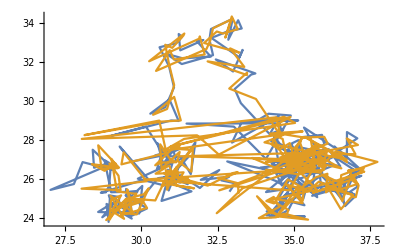
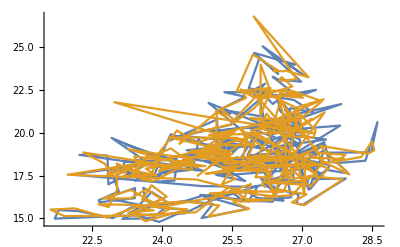
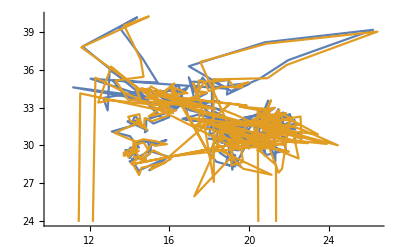

```mathematica
Table[ListLinePlot@{#⟦myi,All,3,1⟧,#⟦myi,All,4,1⟧}&@myRNAfits,{myi,1,3,1}]
```

```mathematica
myRNAfiltered=FilterFitOutlier[myRNAfits,5,20];
```

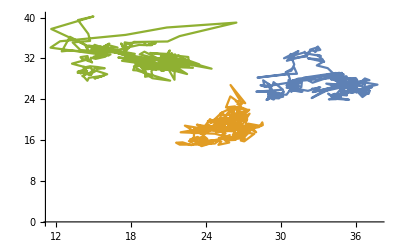

```mathematica
ListLinePlot@myRNAfiltered⟦All,All,4,1⟧
```

### Fitting Particles directly from 3D file

```mathematica
myRNAtrackFiles=FileNames["*myTrack_red*",DirectoryName@analysisFolder];
TableForm@myRNAtrackFiles
```

C:\Users\Tatsuya Morisaki\Documents\_mirroredX\collaboration\Stephanie\20170324_U2OS_G3BP1-GFP_Stress_Experiments\SM_KDM5B_MS2 Plate\Post-stress\Analysis\MAX_Cell05_nopreImage_Crop_x279_y309_w50_h50_myTrack_red_1.dat
C:\Users\Tatsuya Morisaki\Documents\_mirroredX\collaboration\Stephanie\20170324_U2OS_G3BP1-GFP_Stress_Experiments\SM_KDM5B_MS2 Plate\Post-stress\Analysis\MAX_Cell05_nopreImage_Crop_x279_y309_w50_h50_myTrack_red_2.dat
C:\Users\Tatsuya Morisaki\Documents\_mirroredX\collaboration\Stephanie\20170324_U2OS_G3BP1-GFP_Stress_Experiments\SM_KDM5B_MS2 Plate\Post-stress\Analysis\MAX_Cell05_nopreImage_Crop_x279_y309_w50_h50_myTrack_red_3.dat

```mathematica
myRNAtracks=Get/@myRNAtrackFiles;
myTrackNum=Length@myRNAtracks;
myCenters=Ceiling@myRNAtracks⟦All,All,3,1⟧;
```

```mathematica
my3Ddirectory=StringDelete[mymovie,"MAX_"|".tif"]<>"\\";
```

```mathematica
digits=(Last@StringPosition[#,".tif"])⟦1⟧-(Last@StringPosition[#,"_c"])⟦2⟧&@FileNames["*",my3Ddirectory]⟦1⟧-1;
myTnum=Length@FileNames["*z"<>IntegerString[1,10,digits]<>"_c"<>IntegerString[1,10,digits]<>"*",my3Ddirectory];
myZnum=Length@FileNames["*t"<>IntegerString[1,10,digits]<>"*_c"<>IntegerString[1,10,digits]<>"*",my3Ddirectory];
myCnum=Length@FileNames["*t"<>IntegerString[1,10,digits]<>"_z"<>IntegerString[1,10,digits]<>"*",my3Ddirectory];
```

```mathematica
channel=1;channelString="_*c"<>IntegerString[channel,10,digits]<>".tif";
```

```mathematica
pad=3;
myParameterNum=6;
myEmptyFrame=ConstantArray[{0,0},myTrackNum];
myEmptyImg=ConstantImage[0,{2*pad+1,2*pad+1}];
myEmptyOut=Append[ConstantArray[{0,{0,0}},6]//Transpose,myEmptyImg];
```

```mathematica
myFitAll=Transpose@Table[
If[UnsameQ[myCenters⟦All,t⟧,myEmptyFrame],
tempStack=Import/@FileNames["*t"<>IntegerString[t,10,digits]<>channelString,my3Ddirectory];
Table[If[UnsameQ[myCenters⟦i,t⟧,{0,0}],
myTrimStack=ImageTrim[#,{myCenters⟦i,t⟧-pad,myCenters⟦i,t⟧+pad-0.1}]&/@tempStack;
myTrimData=If[UnsameQ[myTrimStack,{}],ImageData/@myTrimStack,{}];
myTrimData=Partition[Flatten@Table[MapIndexed[{#2⟦2⟧-0.5,2*pad+1.5-#2⟦1⟧,i,#1}&,myTrimData⟦i⟧,{2}],{i,1,myZnum,1}],4]; (* {x, y, z, intensity} x and y are image cordinate *)
myFit=NonlinearModelFit[myTrimData,CC+A E^(-(x-x0)^2/(2 1.5^2)-(y-y0)^2/(2 1.5^2)-(z-z0)^2/(2 c^2)),
{{x0,pad+1},{y0,pad+1},{z0,8(*myZnum/2*)},{A,myTrimData⟦Ceiling@(Length@myTrimData/2),4⟧-Min@myTrimData},{CC,Min@myTrimData},{c,1}},{x,y,z}];
myResults={(myFit@"BestFitParameters")⟦All,2⟧,myFit@"ParameterConfidenceIntervals"};
If[0<myResults⟦1,3⟧<myZnum,
myShift=Ceiling@myResults⟦1,{1,2}⟧-(pad+1);
mySmartCrop=ImageTrim[tempStack⟦Round@myResults⟦1,3⟧⟧,{myCenters⟦i,t⟧+myShift-pad,myCenters⟦i,t⟧+myShift+pad-0.1}];,
mySmartCrop=myEmptyImg];
myResults⟦1,{1,2}⟧+=myCenters⟦i,t⟧-pad-1;
myResults⟦2,1⟧+=myCenters⟦i,t,1⟧-pad-1;
myResults⟦2,2⟧+=myCenters⟦i,t,2⟧-pad-1;
Append[myResults,mySmartCrop]
,myEmptyOut]
,{i,1,myTrackNum,1}],ConstantArray[myEmptyOut,myTrackNum]]
,{t,1,myTnum,1}];
```

```mathematica
myRNAtracks=Table[Join@@@Thread@{myRNAtracks⟦i⟧,myFitAll⟦i⟧},{i,1,Length@myRNAtracks,1}];
```

```mathematica
myRNAtracks>>analysisFolder<>"_3Dfit.dat";
```

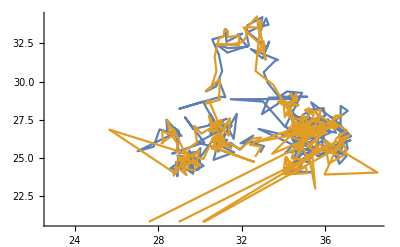
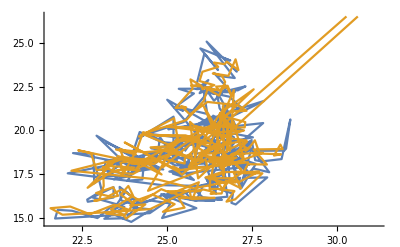
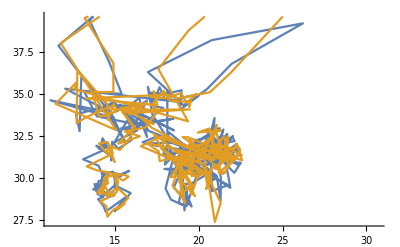

```mathematica
myRNAtracksNoZero=DeleteCases[#,x_/;x⟦3,1⟧=={0.,0.}]&/@myRNAtracks;
Table[ListLinePlot@{#⟦myi,All,3,1⟧,#⟦myi,All,4,{1,2}⟧}&@myRNAtracksNoZero,{myi,1,3,1}]
```

```mathematica
myRNAtracksNoZeroAll=myRNAtracks⟦All,;;Min@(Length/@myRNAtracksNoZero)⟧;
```

```mathematica
Manipulate[Show[ImageAdjust@myColMovie⟦1,frame⟧,Graphics[{Blue,Circle[#,2]&/@(Transpose@myRNAtracksNoZeroAll)⟦frame,All,3,1⟧,Red,Circle[#,2]&/@(Transpose@myRNAtracksNoZeroAll)⟦frame,All,4,{1,2}⟧}]],{frame,1,Length@myRNAtracksNoZeroAll⟦1⟧,1}](* plotting initial guess in BLUE fitting results in RED *)
```

```mathematica
test=Table[Show[ImageAdjust@myColMovie⟦1,frame⟧,Graphics[{Blue,Circle[#,2]&/@(Transpose@myRNAtracksNoZeroAll)⟦frame,All,3,1⟧,Red,Circle[#,2]&/@(Transpose@myRNAtracksNoZeroAll)⟦frame,All,4,{1,2}⟧}]],{frame,1,Length@myRNAtracksNoZeroAll⟦1⟧,1}];
```

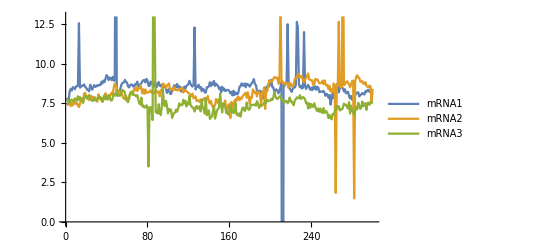

```mathematica
ListLinePlot[myRNAtracksNoZero⟦All,All,4,3⟧,PlotRange->{All,{0,13}},PlotLegends->{"mRNA1","mRNA2","mRNA3"}]
```

```mathematica
myRNAtracksNoZero⟦1,1,5⟧
```

{{32.4804,32.8167},{24.9113,25.2486},{7.73513,7.94683},{0.0371162,0.0451532},{0.0263456,0.027339},{0.83819,1.05643}}

```mathematica
idxX90Conf=Position[(Differences/@#&/@myRNAtracksNoZero⟦All,All,5,1⟧)⟦All,All,1⟧,x_/;x>5]
```

{{1,233}}

```mathematica
idxY90Conf=Position[(Differences/@#&/@myRNAtracksNoZero⟦All,All,5,2⟧)⟦All,All,1⟧,x_/;x>5]
```

{{1,233}}

```mathematica
idxZ1=Position[Differences@myRNAtracksNoZero⟦1,All,4,3⟧,x_/;x>2||x<-2]
```

{{12},{13},{48},{49},{125},{126},{211},{212},{216},{217},{225},{227},{232},{233}}

```mathematica
idxZ1=Split[Flatten@idxZ1,#2-#1==1&]
```

{{12,13},{48,49},{125,126},{211,212},{216,217},{225},{227},{232,233}}

```mathematica
idxZ1={13,49,126,212,217,226,227,233};
```

```mathematica
idxZ1=Thread@{1,#}&/@idxZ1
```

{{1,13},{1,49},{1,126},{1,212},{1,217},{1,226},{1,227},{1,233}}

```mathematica
idxZ2=Position[Differences@myRNAtracksNoZero⟦2,All,4,3⟧,x_/;x>2||x<-2]
```

{{209},{210},{263},{264},{266},{267},{270},{271},{281},{282}}

```mathematica
idxZ2=Split[Flatten@idxZ2,#2-#1==1&]
```

{{209,210},{263,264},{266,267},{270,271},{281,282}}

```mathematica
idxZ2=Last/@idxZ2
```

{210,264,267,271,282}

```mathematica
idxZ2=Thread@{2,#}&/@idxZ2
```

{{2,210},{2,264},{2,267},{2,271},{2,282}}

```mathematica
idxZ3=Position[Differences@myRNAtracksNoZero⟦3,All,4,3⟧,x_/;x>2||x<-2]
```

{{80},{81},{85},{86},{87}}

```mathematica
idxZ3=Split[Flatten@idxZ3,#2-#1==1&]
```

{{80,81},{85,86,87}}

```mathematica
idxZ3={81,86,87};
```

```mathematica
idxZ3=Thread@{3,#}&/@idxZ3
```

{{3,81},{3,86},{3,87}}

```mathematica
idxOutliers=Union[idxX90Conf,idxY90Conf,idxZ1,idxZ2,idxZ3]
```

{{1,13},{1,49},{1,126},{1,212},{1,217},{1,226},{1,227},{1,233},{2,210},{2,264},{2,267},{2,271},{2,282},{3,81},{3,86},{3,87}}

```mathematica
myFilteredRNAtracks=Delete[myRNAtracksNoZero,idxOutliers];
```

```mathematica
Length/@myFilteredRNAtracks
```

{292,295,297}

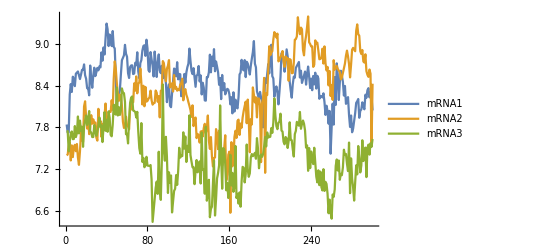

```mathematica
ListLinePlot[Thread@{#⟦All,2⟧,#⟦All,4,3⟧}&/@myFilteredRNAtracks,PlotLegends->{"mRNA1","mRNA2","mRNA3"}]
```

#### taking time-points all three RNAs were tracked

```mathematica
myidx=Intersection@@myFilteredRNAtracks⟦All,All,2⟧;
```

```mathematica
myRNAtracksAll3=Extract[#,Position[#⟦All,2⟧,Alternatives@@myidx]]&/@myFilteredRNAtracks;
```

#### Filling missing points by interpolating the positions

```mathematica
myRNA3Dcord=Thread@{#⟦All,2⟧,#⟦All,4,;;3⟧}&/@myFilteredRNAtracks;
```

```mathematica
TrackFiller[tracksList_]:=Module[{filledTracksList,myIdx,missingStart,missingNum,missingStartShifted,spotEnd,spotStart,fillingNum,fillingPos,fillingSpots},
filledTracksList=tracksList;
Table[
myIdx=Differences@filledTracksList⟦i,All,1⟧;
missingStart=Position[myIdx,x_/;x>1]+1//Flatten;
missingNum=Cases[myIdx,x_/;x>1]-1;
If[missingStart≠{},
missingStartShifted=missingStart;
missingStartShifted⟦2;;⟧=missingStart⟦2;;⟧+(FoldList[Plus,missingNum])⟦;;Length@missingNum-1⟧;
Table[
spotEnd=(filledTracksList⟦i,missingStartShifted⟦j⟧-1⟧);
spotStart=filledTracksList⟦i,missingStartShifted⟦j⟧⟧;
fillingNum=Range[spotEnd⟦1⟧+1,spotStart⟦1⟧-1];
fillingPos=Plus[#,spotEnd⟦2⟧]&/@Outer[Times,Range@missingNum⟦j⟧/(missingNum⟦j⟧+1),spotStart⟦2⟧-spotEnd⟦2⟧];
fillingSpots=Thread@{fillingNum,fillingPos};
Table[filledTracksList⟦i⟧=Insert[filledTracksList⟦i⟧,fillingSpots⟦k⟧,missingStartShifted⟦j⟧+k-1],{k,1,missingNum⟦j⟧,1}];
,{j,1,Length@missingStart,1}];];
,{i,1,Length@filledTracksList,1}];
filledTracksList]
```

```mathematica
myRNA3DcordFilled=TrackFiller@myRNA3Dcord;
```

```mathematica
myRNAtracks⟦All,All,4,;;3⟧=myRNA3DcordFilled⟦All,All,2⟧;
```

```mathematica
myRNAtracksAll3=myRNAtracks;
```

```mathematica
myRNAtracksAll3=<<(analysisFolder<>"_myRNAtracksAll3.dat");
```

### Plotting the distance

```mathematica
intervTime=2/60;(*min*)
pixelSize=0.13;(*nm/pixel*)
```

```mathematica
coordinate12=Thread@{#⟦1,All,2⟧,#⟦1,All,4,;;3⟧,#⟦2,All,4,;;3⟧}&@myRNAtracksAll3;
coordinate12⟦All,{2,3},3⟧*=500/130;
coordinate12=DeleteCases[coordinate12,x_/;x⟦2⟧=={0,0,0}||x⟦3⟧=={0,0,0}];
```

```mathematica
myDist12=Thread@{intervTime*coordinate12⟦All,1⟧,pixelSize*EuclideanDistance@@@coordinate12⟦All,{2,3}⟧};
```

```mathematica
coordinate23=Thread@{#⟦2,All,2⟧,#⟦2,All,4,;;3⟧,#⟦3,All,4,;;3⟧}&@myRNAtracksAll3;
coordinate23⟦All,{2,3},3⟧*=500/130;
coordinate23=DeleteCases[coordinate23,x_/;x⟦2⟧=={0,0,0}||x⟦3⟧=={0,0,0}];
```

```mathematica
myDist23=Thread@{intervTime*coordinate23⟦All,1⟧,pixelSize*EuclideanDistance@@@coordinate23⟦All,{2,3}⟧};
```

```mathematica
coordinate31=Thread@{#⟦3,All,2⟧,#⟦3,All,4,;;3⟧,#⟦1,All,4,;;3⟧}&@myRNAtracksAll3;
coordinate31⟦All,{2,3},3⟧*=500/130;
coordinate31=DeleteCases[coordinate31,x_/;x⟦2⟧=={0,0,0}||x⟦3⟧=={0,0,0}];
```

```mathematica
myDist31=Thread@{intervTime*coordinate31⟦All,1⟧,pixelSize*EuclideanDistance@@@coordinate31⟦All,{2,3}⟧};
```

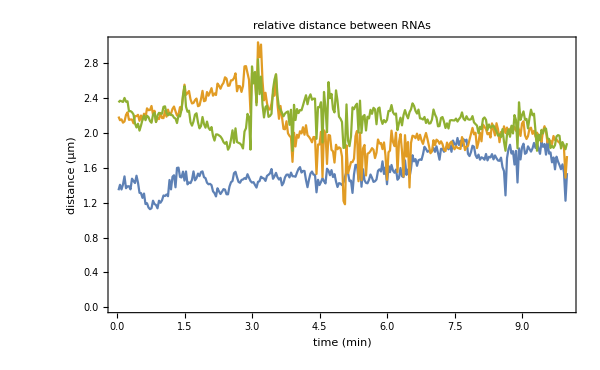

```mathematica
ListLinePlot[{myDist12,myDist23,myDist31},Joined->True,PlotRange->All,Frame->True,BaseStyle->{FontFamily->"Helvetica",FontSize->25},PlotLabel->"relative distance between RNAs",FrameLabel->{"time (min)","distance (µm)"},ImageSize->600]
```

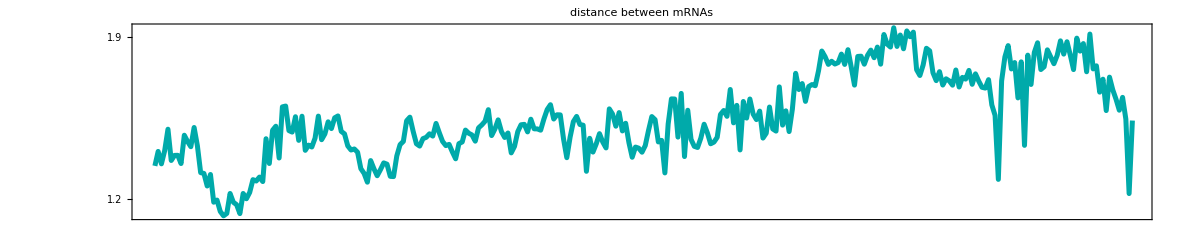

```mathematica
myRNAdistance12=ListLinePlot[myDist12,Frame->True,BaseStyle->{FontFamily->"Helvetica",FontSize->40},AspectRatio->1/5,
FrameTicks->{{{1.2,1.9},None},None},PlotStyle->{Darker@Cyan,Thickness@0.003},
PlotLabel->"distance between mRNAs",(*FrameLabel->{(*"time (min)",*)"distance (µm)"},*)ImageSize->1200]
```

```mathematica
Export[myDirectoryFig<>"RNAdistance12.png",myRNAdistance12,Background->None,ImageSize->1200,ImageResolution->300];
```

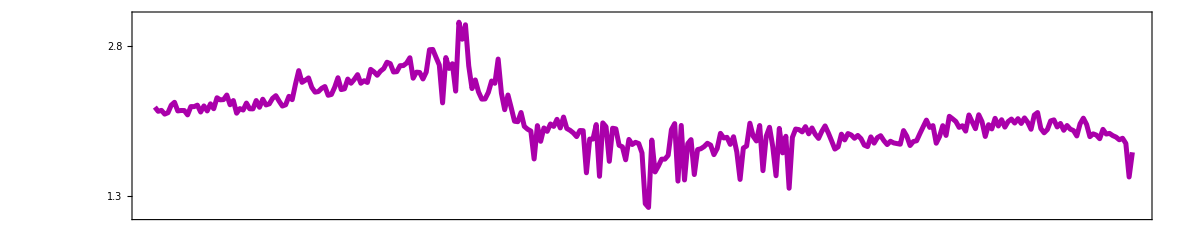

```mathematica
myRNAdistance23=ListLinePlot[myDist23,Frame->True,BaseStyle->{FontFamily->"Helvetica",FontSize->40},AspectRatio->1/5,
PlotRange->{All,{1.1,3.1}},PlotStyle->{Darker@Magenta,Thickness@0.003},
FrameTicks->{{{1.3,2.8},None},None},
(*PlotLabel->"relative distance between RNAs",*)(*FrameLabel->{(*"time (min)",*)"distance (µm)"},*)ImageSize->1200]
```

```mathematica
Export[myDirectoryFig<>"RNAdistance23.png",myRNAdistance23,Background->None,ImageSize->1200,ImageResolution->300];
```

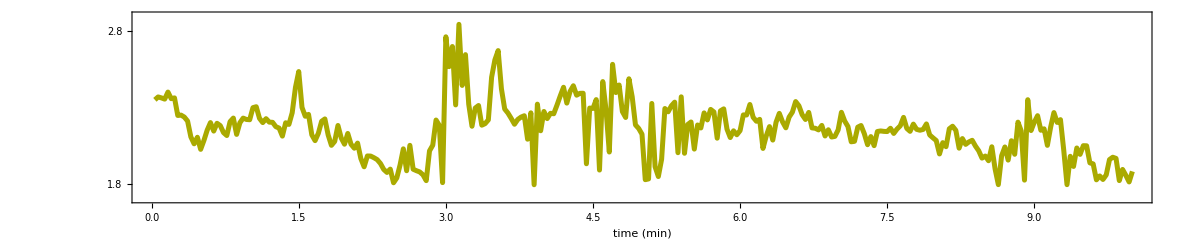

```mathematica
myRNAdistance31=ListLinePlot[myDist31,Frame->True,BaseStyle->{FontFamily->"Helvetica",FontSize->40},AspectRatio->1/5,
PlotRange->{All,{1.7,2.9}},PlotStyle->{Darker@Yellow,Thickness@0.003},
FrameTicks->{{{1.8,2.8},None},Automatic},
(*PlotLabel->"relative distance between RNAs",*)FrameLabel->{"time (min)"(*,"distance (µm)"*)},ImageSize->1200]
```

### Plotting the angles

```mathematica
myRNAtracksAll3FullZ=myRNAtracksAll3;
myRNAtracksAll3FullZ⟦All,All,4,3⟧*=500/130;
vector2and3=Thread@{#⟦1,All,2⟧,#⟦2,All,4,;;3⟧-#⟦1,All,4,;;3⟧,#⟦3,All,4,;;3⟧-#⟦1,All,4,;;3⟧}&@myRNAtracksAll3FullZ;
myAngle23=Thread@{intervTime*vector2and3⟦All,1⟧,VectorAngle@@@vector2and3⟦All,{2,3}⟧};
```

```mathematica
vector3and1=Thread@{#⟦2,All,2⟧,#⟦3,All,4,;;3⟧-#⟦2,All,4,;;3⟧,#⟦1,All,4,;;3⟧-#⟦2,All,4,;;3⟧}&@myRNAtracksAll3FullZ;
myAngle31=Thread@{intervTime*vector3and1⟦All,1⟧,VectorAngle@@@vector3and1⟦All,{2,3}⟧};
```

```mathematica
vector1and2=Thread@{#⟦3,All,2⟧,#⟦1,All,4,;;3⟧-#⟦3,All,4,;;3⟧,#⟦2,All,4,;;3⟧-#⟦3,All,4,;;3⟧}&@myRNAtracksAll3FullZ;
myAngle12=Thread@{intervTime*vector1and2⟦All,1⟧,VectorAngle@@@vector1and2⟦All,{2,3}⟧};
```

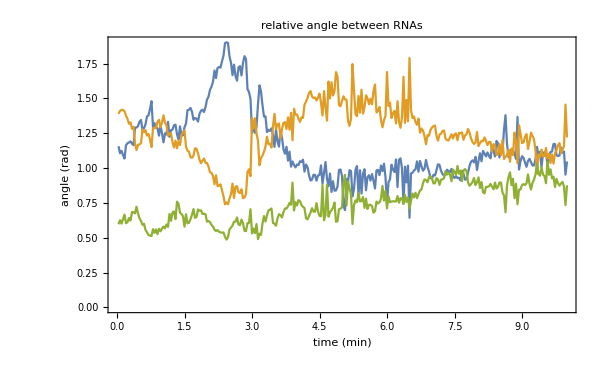

```mathematica
ListLinePlot[{myAngle23,myAngle31,myAngle12},Joined->True,PlotRange->All,Frame->True,BaseStyle->{FontFamily->"Helvetica",FontSize->25},PlotLabel->"relative angle between RNAs",FrameLabel->{"time (min)","angle (rad)"},ImageSize->600]
```

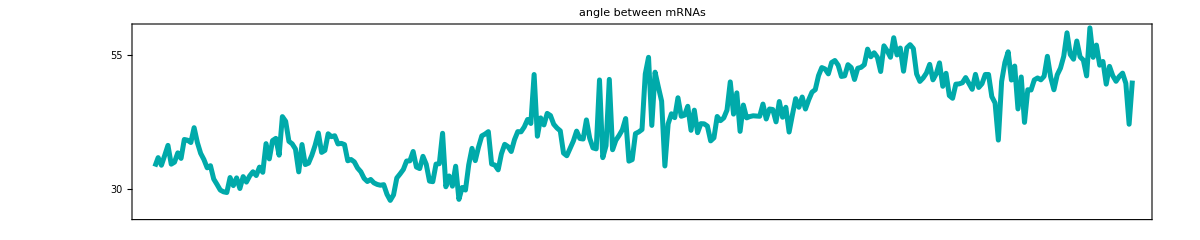

```mathematica
myAngle12Degree=myAngle12;
myAngle12Degree⟦All,2⟧/=Degree;
myRNAangle12=ListLinePlot[myAngle12Degree,Frame->True,BaseStyle->{FontFamily->"Helvetica",FontSize->40},AspectRatio->1/5,
PlotRange->{All,{25,60}},FrameTicks->{{{{30,"  30"},55},None},None},PlotStyle->{Darker@Cyan,Thickness@0.003},
PlotLabel->"angle between mRNAs",(*FrameLabel->{(*"time (min)",*)"distance (µm)"},*)ImageSize->1200]
```

```mathematica
Export[myDirectoryFig<>"RNAangle12.png",myRNAangle12,Background->None,ImageSize->1200,ImageResolution->300];
```

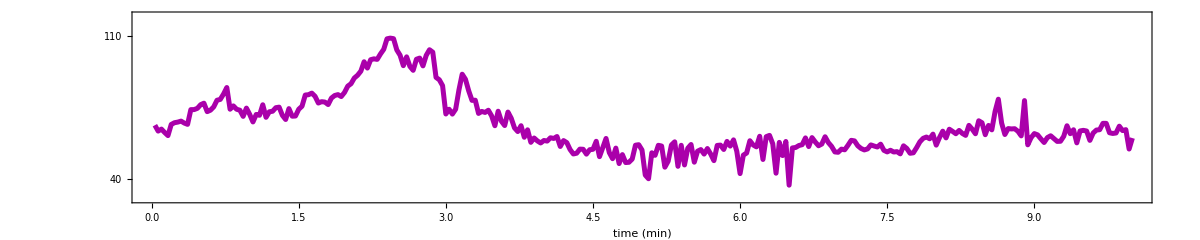

```mathematica
myAngle23Degree=myAngle23;
myAngle23Degree⟦All,2⟧/=Degree;
myRNAangle23=ListLinePlot[myAngle23Degree,Frame->True,BaseStyle->{FontFamily->"Helvetica",FontSize->40},AspectRatio->1/5,
PlotRange->{All,{30,120}},FrameTicks->{{{40,110},None},Automatic},PlotStyle->{Darker@Magenta,Thickness@0.003},
(*PlotLabel->"relative angle between mRNAs",*)FrameLabel->{"time (min)"(*,"distance (µm)"*)},ImageSize->1200]
```

### Plotting RNAs’ positions in 3D

```mathematica
(Transpose@myRNAtracksAll3)⟦All,All,4,;;3⟧;
```

```mathematica
myRNA3Dlocations=Graphics3D[{Red,Sphere@#⟦1⟧,Green,Sphere@#⟦2⟧,Blue,Sphere@#⟦3⟧}]&/@(Transpose@myRNAtracksAll3)⟦All,All,4,;;3⟧;
```

```mathematica
Min/@Transpose@Flatten[myCoordinatesNoZero,1]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[myCoordinatesNoZero,1].

Transpose[Flatten[myCoordinatesNoZero,1]]

```mathematica
Max/@Transpose@Flatten[myCoordinatesNoZero,1]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[myCoordinatesNoZero,1].

Transpose[Flatten[myCoordinatesNoZero,1]]

```mathematica
Manipulate[Show[Graphics3D[{White,Opacity@0,Cuboid [{30,30,2},{70,70,9}]}],myRNA3Dlocations⟦i⟧],{i,1,Length@myRNA3Dlocations,1}]
```

### Length and vector

```mathematica
length1and2from3=Sqrt@(#.#)&/@#&/@vector1and2⟦All,{2,3}⟧;
```

```mathematica
vector1from3=pixelSize*length1and2from3⟦All,1⟧*AngleVector/@myAngle12⟦All,2⟧;
vector2from3=Thread@{pixelSize*length1and2from3⟦All,2⟧,0};
```

```mathematica
length1and3from2=Sqrt@(#.#)&/@#&/@vector3and1⟦All,{2,3}⟧;
```

```mathematica
vector1from2=pixelSize*length1and3from2⟦All,1⟧*AngleVector/@myAngle31⟦All,2⟧;
vector3from2=Thread@{pixelSize*length1and3from2⟦All,2⟧,0};
```

```mathematica
length2and3from1=Sqrt@(#.#)&/@#&/@vector2and3⟦All,{2,3}⟧;
```

```mathematica
vector2from1=pixelSize*length2and3from1⟦All,2⟧*AngleVector/@myAngle23⟦All,2⟧;
vector2from1⟦All,1⟧=-vector2from1⟦All,1⟧;
vector3from1=-Thread@{pixelSize*length2and3from1⟦All,1⟧,0};
```

### Plotting RNAs’ positions 4D in 3D

#### Plotting raw projection

```mathematica
myViewPoint={2,-2.5,0.5};
```

```mathematica
vector1Raw=Prepend[#⟦2⟧,#⟦1⟧]&/@Thread@{(Range@Length@myRNAtracksAll3⟦1⟧-1)*intervTime,myRNAtracksAll3⟦1,All,4,;;2⟧};
vector1Raw⟦All,{2,3}⟧*=pixelSize;
vector2Raw=Prepend[#⟦2⟧,#⟦1⟧]&/@Thread@{(Range@Length@myRNAtracksAll3⟦2⟧-1)*intervTime,myRNAtracksAll3⟦2,All,4,;;2⟧};
vector2Raw⟦All,{2,3}⟧*=pixelSize;
vector3Raw=Prepend[#⟦2⟧,#⟦1⟧]&/@Thread@{(Range@Length@myRNAtracksAll3⟦3⟧-1)*intervTime,myRNAtracksAll3⟦3,All,4,;;2⟧};
vector3Raw⟦All,{2,3}⟧*=pixelSize;
```

```mathematica
vector1PlotRaw=ListPointPlot3D[vector1Raw,PlotStyle->{Darker@Green,PointSize@0.01}];
vector2PlotRaw=ListPointPlot3D[vector2Raw,PlotStyle->{Blue,PointSize@0.01}];
vector3PlotRaw=ListPointPlot3D[vector3Raw,PlotStyle->{Red,PointSize@0.01}];
```

```mathematica
myTriangleLines=Graphics3D[{Gray,Line@#}]&/@Thread@{vector1Raw,vector2Raw,vector3Raw,vector1Raw};
```

```mathematica
Show[vector1PlotRaw,vector2PlotRaw,vector3PlotRaw,myTriangleLines,PlotRange->All,BoxRatios->{4,1,1},ViewPoint->myViewPoint,ImageSize->600]
```

-Graphics3D-

```mathematica
myShiftforRaw={1.7,2};
```

```mathematica
vector1RawShift=vector1Raw;
vector1RawShift⟦All,{2,3}⟧-=ConstantArray[myShiftforRaw,Length@vector1RawShift];
vector2RawShift=vector2Raw;
vector2RawShift⟦All,{2,3}⟧-=ConstantArray[myShiftforRaw,Length@vector2RawShift];
vector3RawShift=vector3Raw;
vector3RawShift⟦All,{2,3}⟧-=ConstantArray[myShiftforRaw,Length@vector3RawShift];
```

```mathematica
vector1PlotRawShift=ListPointPlot3D[vector1RawShift,PlotStyle->{Darker@Green,PointSize@0.01}];
vector2PlotRawShift=ListPointPlot3D[vector2RawShift,PlotStyle->{Blue,PointSize@0.01}];
vector3PlotRawShift=ListPointPlot3D[vector3RawShift,PlotStyle->{Red,PointSize@0.01}];
```

```mathematica
myTriangleLinesShift=Graphics3D[{Gray,Line@#}]&/@Thread@{vector1RawShift,vector2RawShift,vector3RawShift,vector1RawShift};
```

```mathematica
myRawPlot=Show[vector1PlotRawShift,vector2PlotRawShift,vector3PlotRawShift,myTriangleLinesShift,PlotRange->All,BoxRatios->{4,1,1},BaseStyle->{FontFamily->"Helvetica",FontSize->30},ViewPoint->myViewPoint,ImageSize->1200,ImageResolution->300]
```

-Graphics3D-

#### plotting normalized position by mRNA1 (Green)

```mathematica
vector3from2withTime=Prepend[#⟦2⟧,#⟦1⟧]&/@Thread@{(Range@Length@vector3from2-1)*intervTime,10*vector3from2};
vector3from2withTime⟦All,{2,3}⟧*=pixelSize;
vector1from2withTime=Prepend[#⟦2⟧,#⟦1⟧]&/@Thread@{(Range@Length@vector1from2-1)*intervTime,12*vector1from2};
vector1from2withTime⟦All,{2,3}⟧*=pixelSize;
vector2from2withTime=Prepend[#⟦2⟧,#⟦1⟧]&/@Thread@{(Range@Length@vector3from2-1)*intervTime,ConstantArray[{0,0},Length@vector3from2withTime]};
vector2from2withTime⟦All,{2,3}⟧*=pixelSize;
```

```mathematica
vector2from1withTime=Prepend[#⟦2⟧,#⟦1⟧]&/@Thread@{(Range@Length@vector2from1-1)*intervTime,10*vector2from1};
vector2from1withTime⟦All,{2,3}⟧*=pixelSize;
vector3from1withTime=Prepend[#⟦2⟧,#⟦1⟧]&/@Thread@{(Range@Length@vector3from1-1)*intervTime,12*vector3from1};
vector3from1withTime⟦All,{2,3}⟧*=pixelSize;
vector1from1withTime=Prepend[#⟦2⟧,#⟦1⟧]&/@Thread@{(Range@Length@vector2from1-1)*intervTime,ConstantArray[{0,0},Length@vector2from1withTime]};
vector1from1withTime⟦All,{2,3}⟧*=pixelSize;
```

```mathematica
vector1from1Plot=ListPointPlot3D[vector1from1withTime,PlotStyle->{Darker@Green,PointSize@0.01}];vector2from1Plot=ListPointPlot3D[vector2from1withTime,PlotStyle->{Red,PointSize@0.01}];
vector3from1Plot=ListPointPlot3D[vector3from1withTime,PlotStyle->{Blue,PointSize@0.01}];
```

```mathematica
myRNA1Line=Graphics3D[{Red,Line@vector1from1withTime}];
myRNA2Line=Graphics3D[{Darker@Green,Line@vector2from1withTime}];
myRNA3Line=Graphics3D[{Blue,Line@vector3from1withTime}];
```

```mathematica
myTriangleLines=Graphics3D[{Gray,Line@#}]&/@Thread@{vector1from1withTime,vector2from1withTime,vector3from1withTime,vector1from1withTime};
```

```mathematica
Show[vector1from1Plot,vector2from1Plot,vector3from1Plot,(*myRedLine,*)myTriangleLines⟦;;All;;1⟧,PlotRange->All,BoxRatios->{4,1,1},ViewPoint->myViewPoint,ImageSize->600,ImageResolution->300]
```

-Graphics3D-

Shift Green from {0,0} to {18,0}

```mathematica
myShift=2.34; (* µm, corresponds to 18 pixels *)
```

```mathematica
vector1from2withTimeShift=vector1from2withTime;
vector1from2withTimeShift⟦All,2⟧+=myShift;
vector2from2withTimeShift=vector2from2withTime;
vector2from2withTimeShift⟦All,2⟧+=myShift;
vector3from2withTimeShift=vector3from2withTime;
vector3from2withTimeShift⟦All,2⟧+=myShift;
```

```mathematica
vector2from1withTimeShift=vector2from1withTime;
vector2from1withTimeShift⟦All,2⟧+=myShift;
vector1from1withTimeShift=vector1from1withTime;
vector1from1withTimeShift⟦All,2⟧+=myShift;
vector3from1withTimeShift=vector3from1withTime;
vector3from1withTimeShift⟦All,2⟧+=myShift;
```

```mathematica
vector1from1ShiftPlot=ListPointPlot3D[vector1from1withTimeShift,PlotStyle->{Darker@Green,PointSize@0.01}];
vector2from1ShiftPlot=ListPointPlot3D[vector2from1withTimeShift,PlotStyle->{Red,PointSize@0.01}];
vector3from1ShiftPlot=ListPointPlot3D[vector3from1withTimeShift,PlotStyle->{Blue,PointSize@0.01}];
```

```mathematica
myRNA1ShiftLine=Graphics3D[{Red,Line@vector1from1withTimeShift}];
myRNA2ShiftLine=Graphics3D[{Darker@Green,Line@vector2from1withTimeShift}];
myRNA3ShiftLine=Graphics3D[{Blue,Line@vector3from1withTimeShift}];
```

```mathematica
myTriangleShiftLines=Graphics3D[{Gray,Line@#}]&/@Thread@{vector1from1withTimeShift,vector2from1withTimeShift,vector3from1withTimeShift,vector1from1withTimeShift};
```

```mathematica
myNormalizedPlot=Show[vector1from1ShiftPlot,vector2from1ShiftPlot,vector3from1ShiftPlot,(*myRedLine,*)myTriangleShiftLines⟦;;All;;1⟧,PlotRange->All,BoxRatios->{4,1,1},BaseStyle->{FontFamily->"Helvetica",FontSize->30},ViewPoint->myViewPoint,ImageSize->1200,ImageResolution-> 300]
```

-Graphics3D-

### distance red RNA from SG

```mathematica
myRNAtracksAll3fullZ=myRNAtracksAll3;
myRNAtracksAll3fullZ⟦All,All,4,3⟧*=500/130;
```

```mathematica
myMasksSortedfullZ=myMasksSorted;
myMasksSortedfullZ⟦All,1,2,10,All,3⟧*=500/130;
```

```mathematica
mySG3DgraphicsFull=Table[ConvexHullMesh@myMasksSortedfullZ⟦i,1,2,10⟧,{i,1,Length@myMasksSorted,1}];
```

```mathematica
distanceRed=Table[RegionDistance[mySG3DgraphicsFull⟦i⟧,myRNAtracksAll3fullZ⟦3,i,4,;;3⟧],{i,1,Length@mySG3DgraphicsFull,1}];
```

```mathematica
distanceRedFullZ=Thread@{(2*Range@Length@#)/60,#}&@distanceRed;
distanceRedFullZ⟦All,2⟧*=pixelSize*1000;
```

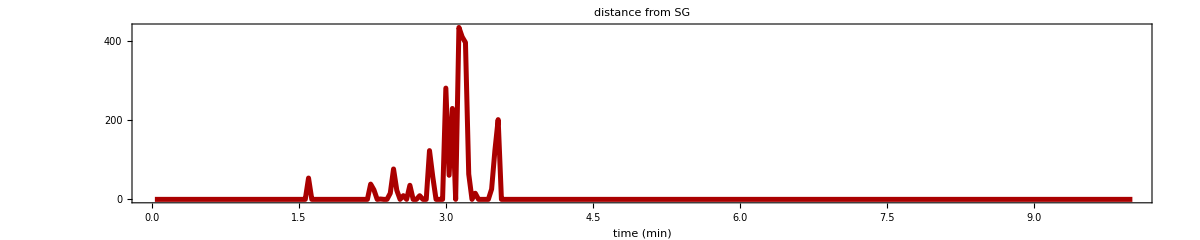

```mathematica
myRNA3SGdistance=ListLinePlot[distanceRedFullZ,Frame->True,BaseStyle->{FontFamily->"Helvetica",FontSize->40},AspectRatio->1/5,
FrameTicks->{{{0,200,400},None},Automatic},PlotStyle->{Darker@Red,Thickness@0.003},
PlotLabel->"distance from SG",FrameLabel->{"time (min)"(*,"distance (µm)"*)},ImageSize->1200]
```

### Distance between each RNA

```mathematica
myidx=Intersection@@myFilteredRNAtracks⟦{1,2},All,2⟧;
myRNAtracks12=Extract[#,Position[#⟦All,2⟧,Alternatives@@myidx]]&/@myFilteredRNAtracks⟦{1,2}⟧;
myRNAtracks12dtdxdydz=Thread@{#⟦1,All,2⟧,0.13*(#⟦1,All,4,1⟧-#⟦2,All,4,1⟧),0.13*(#⟦1,All,4,2⟧-#⟦2,All,4,2⟧),0.5*(#⟦1,All,4,3⟧-#⟦2,All,4,3⟧)}&@myRNAtracks12;
```

```mathematica
myidx=Intersection@@myFilteredRNAtracks⟦{2,3},All,2⟧;
myRNAtracks23=Extract[#,Position[#⟦All,2⟧,Alternatives@@myidx]]&/@myFilteredRNAtracks⟦{2,3}⟧;
myRNAtracks23dtdxdydz=Thread@{#⟦1,All,2⟧,0.13*(#⟦1,All,4,1⟧-#⟦2,All,4,1⟧),0.13*(#⟦1,All,4,2⟧-#⟦2,All,4,2⟧),0.5*(#⟦1,All,4,3⟧-#⟦2,All,4,3⟧)}&@myRNAtracks23;
```

```mathematica
myidx=Intersection@@myFilteredRNAtracks⟦{1,3},All,2⟧;
myRNAtracks13=Extract[#,Position[#⟦All,2⟧,Alternatives@@myidx]]&/@myFilteredRNAtracks⟦{1,3}⟧;
myRNAtracks13dtdxdydz=Thread@{#⟦1,All,2⟧,0.13*(#⟦1,All,4,1⟧-#⟦2,All,4,1⟧),0.13*(#⟦1,All,4,2⟧-#⟦2,All,4,2⟧),0.5*(#⟦1,All,4,3⟧-#⟦2,All,4,3⟧)}&@myRNAtracks13;
```

```mathematica
myRNAtracks12dtdxdydz>>analysisFolder<>"_RNAtracks12_tdxdydz.m";
myRNAtracks23dtdxdydz>>analysisFolder<>"_RNAtracks23_tdxdydz.m";
myRNAtracks13dtdxdydz>>analysisFolder<>"_RNAtracks13_tdxdydz.m";
```

### Polygon

```mathematica
myViewPoint={-3,-2,1.5};
```

```mathematica
myi=1;
my3RNAinSGt1=Show[HighlightMesh[mySG3Dgraphics⟦myi⟧,{Style[1,Thin,Black],Style[2,Opacity[0.2],Blue]}],myRNA3Dgraphics⟦myi⟧,Graphics3D@{Black,Thick,Line[{{12,38,8},{12+1/0.13,38,8}}],Black,Thick,Line[{{12,38,8},{12,38-1/0.13,8}}],Black,Thick,Line[{{12,38,8},{12,38,8+1/0.13*normZ}}],White,Opacity@0,EdgeForm@Thin,Cuboid[{10,10,6},{40,40,36}]},BoxRatios->{1,1,1},ViewPoint->myViewPoint]
```

-Graphics3D-

```mathematica
Export[analysisFolder<>"_my3RNAinSGt1.png",my3RNAinSGt1,Background->None,ImageSize->300,ImageResolution->300];
```

```mathematica
Show[ConvexHullMesh@test,Graphics3D[{Red,Sphere@{38,29,8.4},Yellow,Thick,Dashed,Line@{myRNAtracksAll3normZ⟦3,myi,4,;;3⟧,RegionNearest[ConvexHullMesh@mySG3Dgraphics⟦myi⟧,myRNAtracksAll3normZ⟦3,myi,4,;;3⟧]}}]]
```

```mathematica
myi=94;
my3RNAinSGt94=Show[HighlightMesh[mySG3Dgraphics⟦myi⟧,{Style[1,Thin,Black],Style[2,Opacity[0.2],Blue]}],myRNA3Dgraphics⟦myi⟧,Graphics3D@{Black,Thick,Line[{{12,38,8},{12+1/0.13,38,8}}],Black,Thick,Line[{{12,38,8},{12,38-1/0.13,8}}],Black,Thick,Line[{{12,38,8},{12,38,8+1/0.13*normZ}}],White,Opacity@0,EdgeForm@Thin,Cuboid[{10,10,6},{40,40,36}],Red,Opacity@1,Dashed,Thickness@0.01,Line@{myRNAtracksAll3normZ⟦3,myi,4,;;3⟧,RegionNearest[mySG3Dgraphics⟦myi⟧,myRNAtracksAll3normZ⟦3,myi,4,;;3⟧]}},BoxRatios->{1,1,1},ViewPoint->myViewPoint]
```

-Graphics3D-

```mathematica
Export[analysisFolder<>"_my3RNAinSGt94.png",my3RNAinSGt94,Background->None,ImageSize->300,ImageResolution->300];
```

```mathematica
Export[myDirectoryFig<>"_my3RNAinSGt94wLine.png",my3RNAinSGt94,Background->None,ImageSize->300,ImageResolution->300];
```

```mathematica
myi=170;
my3RNAinSGt170=Show[HighlightMesh[mySG3Dgraphics⟦myi⟧,{Style[1,Thin,Black],Style[2,Opacity[0.2],Blue]}],myRNA3Dgraphics⟦myi⟧,Graphics3D@{Black,Thick,Line[{{12,38,8},{12+1/0.13,38,8}}],Black,Thick,Line[{{12,38,8},{12,38-1/0.13,8}}],Black,Thick,Line[{{12,38,8},{12,38,8+1/0.13*normZ}}],White,Opacity@0,EdgeForm@Thin,Cuboid[{10,10,6},{40,40,36}]},BoxRatios->{1,1,1},ViewPoint->myViewPoint]
```

-Graphics3D-

## Cell02 - Fig S4

### Reading in Images

```mathematica
{FileNameSetter[Dynamic[mymovie]],Dynamic[mymovie]}
```

{$CellContext`mymovieOpenAll,}

```mathematica
myColMovie=Import[mymovie]//Partition[#,3]&//Transpose;
If[DirectoryQ@(DirectoryName[mymovie]<>"Analysis\\")==False,CreateDirectory@(DirectoryName[mymovie]<>"Analysis\\")];
analysisFolder=DirectoryName[mymovie]<>"Analysis\\"<>StringDrop[StringDelete[mymovie,DirectoryName[mymovie]],-4];
```

### Reading in Parameters (if parameters exist)

#### basic parameters

```mathematica
myTfFunc=<<(DirectoryName@mymovie<>"TransformationFunction.m");
```

```mathematica
mymask=Import@(analysisFolder<>"_mask.tif");
```

```mathematica
avgFrameN=<<(analysisFolder<>"_avgFrameN.dat");
myMaxN=Length@myColMovie⟦1⟧-avgFrameN+1;
myColMovieRunAv=If[avgFrameN==1,myColMovie,MovingAverage[#,avgFrameN]&/@myColMovie];
```

#### basic color parameters

```mathematica
thred=<<(analysisFolder<>"_thred.dat");
{mymaxred,thred2,bandpassred,dotsizered}=<<(analysisFolder<>"_thred2.dat");
```

```mathematica
thgreen=<<(analysisFolder<>"_thgreen.dat");
{mymaxgreen,thgreen2,bandpassgreen,dotsizegreen}=<<(analysisFolder<>"_thgreen2.dat");
```

```mathematica
thblue=<<(analysisFolder<>"_thblue.dat");
{mymaxblue,thblue2,bandpassblue,dotsizeblue}=<<(analysisFolder<>"_thblue2.dat");
```

#### processed data

```mathematica
myRNA1Track=<<(analysisFolder<>"_myTrack_RNA1.dat");
myRNA2Track=<<(analysisFolder<>"_myTrack_RNA2.dat");
```

### Make Mask

```mathematica
If[FileExistsQ[analysisFolder<>"_avg.tif"]==True,
avgImg=Import[analysisFolder<>"_avg.tif"];,
avgImg=Mean/@myColMovie;
Export[analysisFolder<>"_avg.tif",avgImg]];
If[FileExistsQ[analysisFolder<>"_max.tif"]==True,
maxImg=Import[analysisFolder<>"_max.tif"],
maxImg=ImageApply[Max,#]&/@myColMovie;
Export[analysisFolder<>"_max.tif",maxImg]];
```

```mathematica
Manipulate[maxImg⟦2⟧//ImageAdjust[#,{0,0,1},{threshold1,threshold2}]&,
Button["Choose threshold such that the shape of the cell can be visualized and CLICK",thtemp={threshold1,threshold2}],
{threshold1,0,0.2,0.001},{{threshold2,0.1},0,0.2,0.001}]
```

```mathematica
ImageAdjust[maxImg⟦2⟧,{0,0,1},thtemp]
```

```mathematica
mymask=-Graphics-;
Export[analysisFolder<>"_mask.tif",mymask];
```

```mathematica
(*mymask=Image@ConstantArray[1,ImageDimensions@avgImg];
Export[analysisFolder<>"_mask.tif",mymask];*)
```

### Running z-average

```mathematica
avgFrameN=1;
avgFrameN>>analysisFolder<>"_avgFrameN.dat";myMaxN=Length@myColMovie⟦1⟧-avgFrameN+1;
```

```mathematica
myColMovieRunAv=If[avgFrameN==1,myColMovie,MovingAverage[#,avgFrameN]&/@myColMovie];
```

```mathematica
Manipulate[myColMovieRunAv⟦channel,frame⟧//ImageAdjust[#,{0,0,1},{0,threshold}]&,{channel,Range@Length@myColMovieRunAv},{frame,1,myMaxN,1},{threshold,0,0.3,0.001}]
```

### Setting Threshold

```mathematica
MyThresholding[myColMovieRunAv,analysisFolder]
```

### Setting Threshold for Binarization

```mathematica
MyBinarization[myColMovieRunAv,analysisFolder]
```

### Tracking each particles w/ Click-and-Track function

```mathematica
ClickAndTrack[myColMovie,myColMovieRunAv,analysisFolder]
```

### Fitting Particles

```mathematica
myRNAtrackFiles=FileNames["*myTrack_red*",DirectoryName@analysisFolder];
TableForm@myRNAtrackFiles
```

```mathematica
myRNAtracks=Get/@myRNAtrackFiles;
myRNAtracks=DeleteCases[#,x_/;x⟦3,1⟧=={0.,0.}]&/@myRNAtracks;
```

```mathematica
{myRNAfits,myRedCenters,myRedCroppedData}=MyParticleFitter[myColMovie,1,myRNAtracks,4,avgFrameN];
```

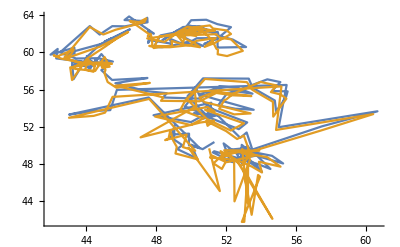
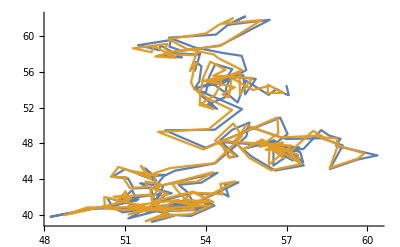
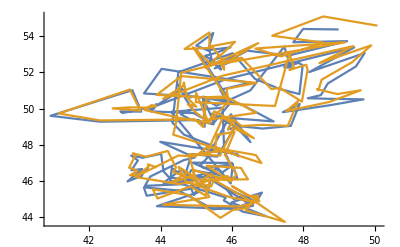

```mathematica
Table[ListLinePlot@{#⟦myi,All,3,1⟧,#⟦myi,All,4,1⟧}&@myRNAfits,{myi,1,3,1}]
```

```mathematica
myRNAfiltered=FilterFitOutlier[myRNAfits,5,20];
```

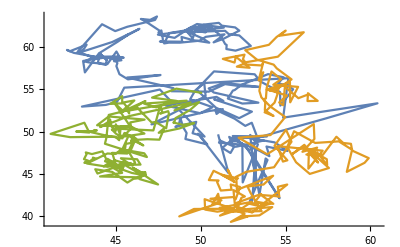

```mathematica
ListLinePlot@myRNAfiltered⟦All,All,4,1⟧
```

### Fitting Particles directly from 3D file

```mathematica
myRNAtrackFiles=FileNames["*myTrack_red*",DirectoryName@analysisFolder];
TableForm@myRNAtrackFiles
```

```mathematica
myRNAtracks=Get/@myRNAtrackFiles;
myTrackNum=Length@myRNAtracks;
myCenters=Ceiling@myRNAtracks⟦All,All,3,1⟧;
```

```mathematica
my3Ddirectory=StringDelete[mymovie,"MAX_"|".tif"]<>"\\";
```

```mathematica
digits=(Last@StringPosition[#,".tif"])⟦1⟧-(Last@StringPosition[#,"_c"])⟦2⟧&@FileNames["*",my3Ddirectory]⟦1⟧-1;
myTnum=Length@FileNames["*z"<>IntegerString[1,10,digits]<>"_c"<>IntegerString[1,10,digits]<>"*",my3Ddirectory];
myZnum=Length@FileNames["*t"<>IntegerString[1,10,digits]<>"*_c"<>IntegerString[1,10,digits]<>"*",my3Ddirectory];
myCnum=Length@FileNames["*t"<>IntegerString[1,10,digits]<>"_z"<>IntegerString[1,10,digits]<>"*",my3Ddirectory];
```

```mathematica
channel=1;channelString="_*c"<>IntegerString[channel,10,digits]<>".tif";
```

```mathematica
pad=3;
myParameterNum=6;
myEmptyFrame=ConstantArray[{0,0},myTrackNum];
myEmptyImg=ConstantImage[0,{2*pad+1,2*pad+1}];
myEmptyOut=Append[ConstantArray[{0,{0,0}},6]//Transpose,myEmptyImg];
```

```mathematica
myFitAll=Transpose@Table[
If[UnsameQ[myCenters⟦All,t⟧,myEmptyFrame],
tempStack=Import/@FileNames["*t"<>IntegerString[t,10,digits]<>channelString,my3Ddirectory];
Table[If[UnsameQ[myCenters⟦i,t⟧,{0,0}],
myTrimStack=ImageTrim[#,{myCenters⟦i,t⟧-pad,myCenters⟦i,t⟧+pad-0.1}]&/@tempStack;
myTrimData=If[UnsameQ[myTrimStack,{}],ImageData/@myTrimStack,{}];
myTrimData=Partition[Flatten@Table[MapIndexed[{#2⟦2⟧-0.5,2*pad+1.5-#2⟦1⟧,i,#1}&,myTrimData⟦i⟧,{2}],{i,1,myZnum,1}],4]; (* {x, y, z, intensity} x and y are image cordinate *)
myFit=NonlinearModelFit[myTrimData,CC+A E^(-(x-x0)^2/(2 1.5^2)-(y-y0)^2/(2 1.5^2)-(z-z0)^2/(2 c^2)),
{{x0,pad+1},{y0,pad+1},{z0,myZnum/2},{A,myTrimData⟦Ceiling@(Length@myTrimData/2),4⟧-Min@myTrimData},{CC,Min@myTrimData},{c,1}},{x,y,z}];
myResults={(myFit@"BestFitParameters")⟦All,2⟧,myFit@"ParameterConfidenceIntervals"};
If[0<myResults⟦1,3⟧<myZnum,
myShift=Ceiling@myResults⟦1,{1,2}⟧-(pad+1);
mySmartCrop=ImageTrim[tempStack⟦Round@myResults⟦1,3⟧⟧,{myCenters⟦i,t⟧+myShift-pad,myCenters⟦i,t⟧+myShift+pad-0.1}];,
mySmartCrop=myEmptyImg];
myResults⟦1,{1,2}⟧+=myCenters⟦i,t⟧-pad-1;
myResults⟦2,1⟧+=myCenters⟦i,t,1⟧-pad-1;
myResults⟦2,2⟧+=myCenters⟦i,t,2⟧-pad-1;
Append[myResults,mySmartCrop]
,myEmptyOut]
,{i,1,myTrackNum,1}],ConstantArray[myEmptyOut,myTrackNum]]
,{t,1,myTnum,1}];
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
myRNAtracks=Table[Join@@@Thread@{myRNAtracks⟦i⟧,myFitAll⟦i⟧},{i,1,Length@myRNAtracks,1}];
```

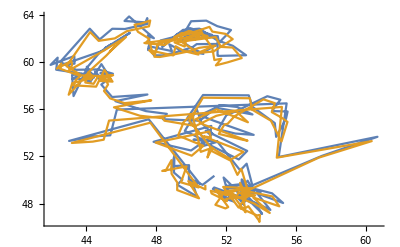
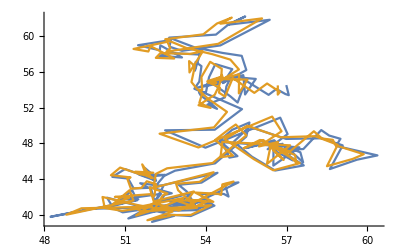
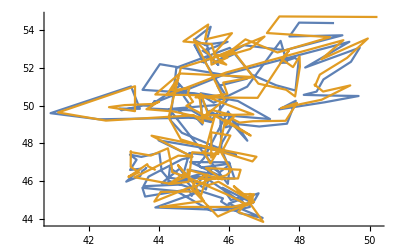

```mathematica
myRNAtracksNoZero=DeleteCases[#,x_/;x⟦3,1⟧=={0.,0.}]&/@myRNAtracks;
Table[ListLinePlot@{#⟦myi,All,3,1⟧,#⟦myi,All,4,{1,2}⟧}&@myRNAtracksNoZero,{myi,1,3,1}]
```

```mathematica
myRNAtracksNoZeroAll=myRNAtracks⟦All,;;Min@(Length/@myRNAtracksNoZero)⟧;
```

```mathematica
Manipulate[Show[ImageAdjust@myColMovie⟦1,frame⟧,Graphics[{Red,Circle[#,2]&/@(Transpose@myRNAtracksNoZeroAll)⟦frame,All,3,1⟧}]],{frame,1,Length@myRNAtracksNoZeroAll⟦1⟧,1}](* plotting initial guesses *)
```

```mathematica
Manipulate[Show[ImageAdjust@myColMovie⟦1,frame⟧,Graphics[{Red,Circle[#,2]&/@(Transpose@myRNAtracksNoZeroAll)⟦frame,All,4,{1,2}⟧}]],{frame,1,Length@myRNAtracksNoZeroAll⟦1⟧,1}](* plotting fitting results *)
```

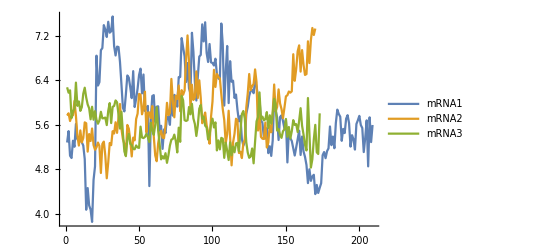

```mathematica
ListLinePlot[myRNAtracksNoZero⟦All,All,4,3⟧,PlotRange->All,PlotLegends->{"mRNA1","mRNA2","mRNA3"}]
```

#### mRNA1 at frame 16 was misfit. Refit with using a different initial guess for Z

```mathematica
t=16;i=1;myZinitialGuess=4;
tempStack=Import/@FileNames["*t"<>IntegerString[t,10,digits]<>channelString,my3Ddirectory];
myTrimStack=ImageTrim[#,{myCenters⟦i,t⟧-pad,myCenters⟦i,t⟧+pad-0.1}]&/@tempStack;
myTrimData=If[UnsameQ[myTrimStack,{}],ImageData/@myTrimStack,{}];
myTrimData=Partition[Flatten@Table[MapIndexed[{#2⟦2⟧-0.5,2*pad+1.5-#2⟦1⟧,i,#1}&,myTrimData⟦i⟧,{2}],{i,1,myZnum,1}],4]; (* {x, y, z, intensity} x and y are image cordinate *)
myFit=NonlinearModelFit[myTrimData,CC+A E^(-(x-x0)^2/(2 1.5^2)-(y-y0)^2/(2 1.5^2)-(z-z0)^2/(2 c^2)),
{{x0,pad+1},{y0,pad+1},{z0,myZinitialGuess},{A,myTrimData⟦Ceiling@(Length@myTrimData/2),4⟧-Min@myTrimData},{CC,Min@myTrimData},{c,1}},{x,y,z}];
myResults={(myFit@"BestFitParameters")⟦All,2⟧,myFit@"ParameterConfidenceIntervals"};
If[0<myResults⟦1,3⟧<myZnum,
myShift=Ceiling@myResults⟦1,{1,2}⟧-(pad+1);
mySmartCrop=ImageTrim[tempStack⟦Round@myResults⟦1,3⟧⟧,{myCenters⟦i,t⟧+myShift-pad,myCenters⟦i,t⟧+myShift+pad-0.1}];,
mySmartCrop=myEmptyImg];
myResults⟦1,{1,2}⟧+=myCenters⟦i,t⟧-pad-1;
myResults⟦2,1⟧+=myCenters⟦i,t,1⟧-pad-1;
myResults⟦2,2⟧+=myCenters⟦i,t,2⟧-pad-1;
mytempResult=Append[myResults,mySmartCrop]
```

{{44.3586,53.2522,4.14926,0.0301298,0.0225533,1.10593},{{44.1667,44.5506},{53.0601,53.4443},{4.00838,4.29015},{0.0267474,0.0335123},{0.0220942,0.0230124},{0.957983,1.25387}},-Graphics-}

```mathematica
myRNAtracks⟦1,16,4;;⟧=mytempResult;
```

```mathematica
myRNAtracks>>(analysisFolder<>"_myRNAtracks.dat");
myRNAtracksNoZeroAll>>(analysisFolder<>"_myRNAtracksNoZeroAll.dat");
```

### Plotting the distance

```mathematica
intervTime=2/60;(*min*)
pixelSize=0.13;(*nm/pixel*)
```

```mathematica
myRNAtracksFullZ=myRNAtracks;
myRNAtracksFullZ⟦All,All,4,3⟧*=500/130;
coordinate12=Thread@{#⟦1,All,2⟧,#⟦1,All,4,;;3⟧,#⟦2,All,4,;;3⟧}&@myRNAtracksFullZ;
coordinate12=DeleteCases[coordinate12,x_/;x⟦2⟧=={0,0,0}||x⟦3⟧=={0,0,0}];
```

```mathematica
myDist12=Thread@{intervTime*coordinate12⟦All,1⟧,pixelSize*EuclideanDistance@@@coordinate12⟦All,{2,3}⟧};
```

```mathematica
coordinate23=Thread@{#⟦2,All,2⟧,#⟦2,All,4,;;3⟧,#⟦3,All,4,;;3⟧}&@myRNAtracksFullZ;
coordinate23=DeleteCases[coordinate23,x_/;x⟦2⟧=={0,0,0}||x⟦3⟧=={0,0,0}];
```

```mathematica
myDist23=Thread@{intervTime*coordinate23⟦All,1⟧,pixelSize*EuclideanDistance@@@coordinate23⟦All,{2,3}⟧};
```

```mathematica
coordinate31=Thread@{#⟦3,All,2⟧,#⟦3,All,4,;;3⟧,#⟦1,All,4,;;3⟧}&@myRNAtracksFullZ;
coordinate31=DeleteCases[coordinate31,x_/;x⟦2⟧=={0,0,0}||x⟦3⟧=={0,0,0}];
```

```mathematica
myDist31=Thread@{intervTime*coordinate31⟦All,1⟧,pixelSize*EuclideanDistance@@@coordinate31⟦All,{2,3}⟧};
```

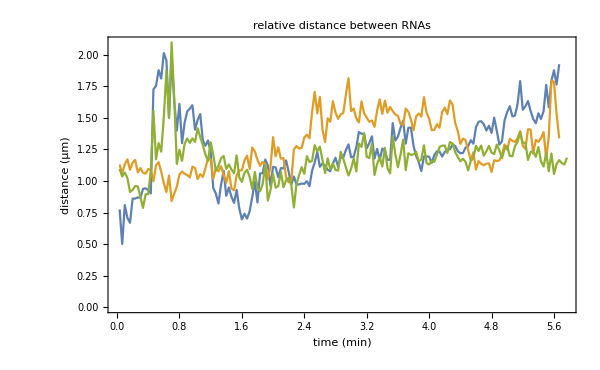

```mathematica
ListLinePlot[{myDist12,myDist23,myDist31},Joined->True,PlotRange->All,Frame->True,BaseStyle->{FontFamily->"Helvetica",FontSize->25},PlotLabel->"relative distance between RNAs",FrameLabel->{"time (min)","distance (µm)"},ImageSize->600]
```

```mathematica
{Mean@#,StandardDeviation@#}&@myDist12⟦All,2⟧
```

{1.25074,0.291818}

```mathematica
{Mean@#,StandardDeviation@#}&@myDist23⟦All,2⟧
```

{1.28968,0.217385}

```mathematica
{Mean@#,StandardDeviation@#}&@myDist31⟦All,2⟧
```

{1.17028,0.162068}

### Plotting the angles

```mathematica
myRNAtracksNoZeroAllfullZ=myRNAtracksNoZeroAll;
myRNAtracksNoZeroAllfullZ⟦All,All,4,3⟧*=500/130;
vector2and3=Thread@{#⟦1,All,2⟧,#⟦2,All,4,;;3⟧-#⟦1,All,4,;;3⟧,#⟦3,All,4,;;3⟧-#⟦1,All,4,;;3⟧}&@myRNAtracksNoZeroAllfullZ;
myAngle23=Thread@{intervTime*vector2and3⟦All,1⟧,VectorAngle@@@vector2and3⟦All,{2,3}⟧};
```

```mathematica
vector3and1=Thread@{#⟦2,All,2⟧,#⟦3,All,4,;;3⟧-#⟦2,All,4,;;3⟧,#⟦1,All,4,;;3⟧-#⟦2,All,4,;;3⟧}&@myRNAtracksNoZeroAllfullZ;
myAngle31=Thread@{intervTime*vector3and1⟦All,1⟧,VectorAngle@@@vector3and1⟦All,{2,3}⟧};
```

```mathematica
vector1and2=Thread@{#⟦3,All,2⟧,#⟦1,All,4,;;3⟧-#⟦3,All,4,;;3⟧,#⟦2,All,4,;;3⟧-#⟦3,All,4,;;3⟧}&@myRNAtracksNoZeroAllfullZ;
myAngle12=Thread@{intervTime*vector1and2⟦All,1⟧,VectorAngle@@@vector1and2⟦All,{2,3}⟧};
```

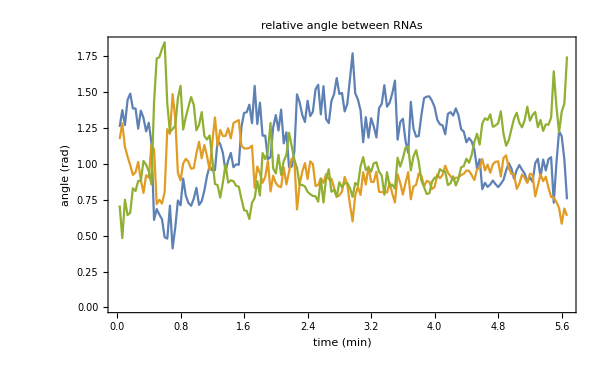

```mathematica
ListLinePlot[{myAngle23,myAngle31,myAngle12},Joined->True,PlotRange->All,Frame->True,BaseStyle->{FontFamily->"Helvetica",FontSize->25},PlotLabel->"relative angle between RNAs",FrameLabel->{"time (min)","angle (rad)"},ImageSize->600]
```

```mathematica
{Mean@#,StandardDeviation@#}&@myAngle23⟦All,2⟧
```

{1.15024,0.269402}

```mathematica
{Mean@#,StandardDeviation@#}&@myAngle31⟦All,2⟧
```

{0.939641,0.149056}

```mathematica
{Mean@#,StandardDeviation@#}&@myAngle12⟦All,2⟧
```

{1.05171,0.255051}

### Plotting RNAs’ positions in 3D

```mathematica
(Transpose@myRNAtracksNoZeroAll)⟦All,All,4,;;3⟧;
```

```mathematica
myRNA3Dlocations=Graphics3D[{Red,Sphere@#⟦1⟧,Green,Sphere@#⟦2⟧,Blue,Sphere@#⟦3⟧}]&/@(Transpose@myRNAtracksNoZeroAll)⟦All,All,4,;;3⟧;
```

```mathematica
Min/@Transpose@Flatten[myCoordinatesNoZero,1]
```

{41.1347,39.4066,3.85347}

```mathematica
Max/@Transpose@Flatten[myCoordinatesNoZero,1]
```

{60.328,63.5086,7.54356}

```mathematica
Manipulate[Show[Graphics3D[{White,Opacity@0,Cuboid [{30,30,2},{70,70,9}]}],myRNA3Dlocations⟦i⟧],{i,1,Length@myRNA3Dlocations,1}]
```

### Length and vector

```mathematica
length1and2from3=Sqrt@(#.#)&/@#&/@vector1and2⟦All,{2,3}⟧;
```

```mathematica
vector1from3=pixelSize*length1and2from3⟦All,1⟧*AngleVector/@myAngle12⟦All,2⟧;
vector2from3=Thread@{pixelSize*length1and2from3⟦All,2⟧,0};
```

```mathematica
length1and3from2=Sqrt@(#.#)&/@#&/@vector3and1⟦All,{2,3}⟧;
```

```mathematica
vector1from2=pixelSize*length1and3from2⟦All,1⟧*AngleVector/@myAngle31⟦All,2⟧;
vector3from2=Thread@{pixelSize*length1and3from2⟦All,2⟧,0};
```

### Plotting RNAs’ positions 4D in 3D

#### Plotting raw projection

```mathematica
myViewPoint={2,-2.5,0.5};
```

```mathematica
vector1Raw=Prepend[#⟦2⟧,#⟦1⟧]&/@Thread@{(Range@Length@myRNAtracksNoZeroAll⟦1⟧-1)*intervTime,myRNAtracksNoZeroAll⟦1,All,4,;;2⟧};
vector1Raw⟦All,{2,3}⟧*=pixelSize;
vector2Raw=Prepend[#⟦2⟧,#⟦1⟧]&/@Thread@{(Range@Length@myRNAtracksNoZeroAll⟦2⟧-1)*intervTime,myRNAtracksNoZeroAll⟦2,All,4,;;2⟧};
vector2Raw⟦All,{2,3}⟧*=pixelSize;
vector3Raw=Prepend[#⟦2⟧,#⟦1⟧]&/@Thread@{(Range@Length@myRNAtracksNoZeroAll⟦3⟧-1)*intervTime,myRNAtracksNoZeroAll⟦3,All,4,;;2⟧};
vector3Raw⟦All,{2,3}⟧*=pixelSize;
```

```mathematica
vector1PlotRaw=ListPointPlot3D[vector1Raw,PlotStyle->{Red,PointSize@0.01}];
vector2PlotRaw=ListPointPlot3D[vector2Raw,PlotStyle->{Darker@Green,PointSize@0.01}];
vector3PlotRaw=ListPointPlot3D[vector3Raw,PlotStyle->{Blue,PointSize@0.01}];
```

```mathematica
myTriangleLines=Graphics3D[{Gray,Line@#}]&/@Thread@{vector1Raw,vector2Raw,vector3Raw,vector1Raw};
```

```mathematica
Show[vector1PlotRaw,vector2PlotRaw,vector3PlotRaw,myTriangleLines,BoxRatios->{5,1,1}]
```

```mathematica
myShiftforRaw={5.5,5};
```

```mathematica
vector1RawShift=vector1Raw;
vector1RawShift⟦All,{2,3}⟧-=ConstantArray[myShiftforRaw,Length@vector1RawShift];
vector2RawShift=vector2Raw;
vector2RawShift⟦All,{2,3}⟧-=ConstantArray[myShiftforRaw,Length@vector2RawShift];
vector3RawShift=vector3Raw;
vector3RawShift⟦All,{2,3}⟧-=ConstantArray[myShiftforRaw,Length@vector3RawShift];
```

```mathematica
vector1PlotRawShift=ListPointPlot3D[vector1RawShift,PlotStyle->{Red,PointSize@0.01}];
vector2PlotRawShift=ListPointPlot3D[vector2RawShift,PlotStyle->{Darker@Green,PointSize@0.01}];
vector3PlotRawShift=ListPointPlot3D[vector3RawShift,PlotStyle->{Blue,PointSize@0.01}];
```

```mathematica
myTriangleLinesShift=Graphics3D[{Gray,Line@#}]&/@Thread@{vector1RawShift,vector2RawShift,vector3RawShift,vector1RawShift};
```

```mathematica
myRawPlot=Show[vector1PlotRawShift,vector2PlotRawShift,vector3PlotRawShift,myTriangleLinesShift,Ticks->{Automatic,{0,1,2},Automatic},BoxRatios->{4,1,1},BaseStyle->{FontFamily->"Helvetica",FontSize->40},ViewPoint->myViewPoint,ImageSize->1500,ImageResolution->300]
```

-Graphics3D-

#### plotting normalized position by mRNA2 (Green)

```mathematica
vector3from2withTime=Prepend[#⟦2⟧,#⟦1⟧]&/@Thread@{(Range@Length@vector3from2-1)*intervTime,10*vector3from2};
vector3from2withTime⟦All,{2,3}⟧*=pixelSize;
vector1from2withTime=Prepend[#⟦2⟧,#⟦1⟧]&/@Thread@{(Range@Length@vector1from2-1)*intervTime,12*vector1from2};
vector1from2withTime⟦All,{2,3}⟧*=pixelSize;
vector2from2withTime=Prepend[#⟦2⟧,#⟦1⟧]&/@Thread@{(Range@Length@vector3from2-1)*intervTime,ConstantArray[{0,0},Length@vector3from2withTime]};
vector2from2withTime⟦All,{2,3}⟧*=pixelSize;
```

```mathematica
vector1from2Plot=ListPointPlot3D[vector1from2withTime,PlotStyle->{Red,PointSize@0.01}];
vector2from2Plot=ListPointPlot3D[vector2from2withTime,PlotStyle->{Darker@Green,PointSize@0.01}];
vector3from2Plot=ListPointPlot3D[vector3from2withTime,PlotStyle->{Blue,PointSize@0.01}];
```

```mathematica
myRNA1Line=Graphics3D[{Red,Line@vector1from2withTime}];
myRNA2Line=Graphics3D[{Darker@Green,Line@vector2from2withTime}];
myRNA3Line=Graphics3D[{Blue,Line@vector3from2withTime}];
```

```mathematica
myTriangleLines=Graphics3D[{Gray,Line@#}]&/@Thread@{vector1from2withTime,vector2from2withTime,vector3from2withTime,vector1from2withTime};
```

```mathematica
Show[vector1from2Plot,vector2from2Plot,vector3from2Plot,(*myRedLine,*)myTriangleLines⟦;;All;;1⟧,BoxRatios->{5,1,1}]
```

Shift Green from {0,0} to {18,0}

```mathematica
myShift=2.34; (* µm, corresponds to 18 pixels *)
```

```mathematica
vector1from2withTimeShift=vector1from2withTime;
vector1from2withTimeShift⟦All,2⟧+=myShift;
vector2from2withTimeShift=vector2from2withTime;
vector2from2withTimeShift⟦All,2⟧+=myShift;
vector3from2withTimeShift=vector3from2withTime;
vector3from2withTimeShift⟦All,2⟧+=myShift;
```

```mathematica
vector1from2ShiftPlot=ListPointPlot3D[vector1from2withTimeShift,PlotStyle->{Red,PointSize@0.01}];
vector2from2ShiftPlot=ListPointPlot3D[vector2from2withTimeShift,PlotStyle->{Darker@Green,PointSize@0.01}];
vector3from2ShiftPlot=ListPointPlot3D[vector3from2withTimeShift,PlotStyle->{Blue,PointSize@0.01}];
```

```mathematica
myRNA1ShiftLine=Graphics3D[{Red,Line@vector1from2withTimeShift}];
myRNA2ShiftLine=Graphics3D[{Darker@Green,Line@vector2from2withTimeShift}];
myRNA3ShiftLine=Graphics3D[{Blue,Line@vector3from2withTimeShift}];
```

```mathematica
myTriangleShiftLines=Graphics3D[{Gray,Line@#}]&/@Thread@{vector1from2withTimeShift,vector2from2withTimeShift,vector3from2withTimeShift,vector1from2withTimeShift};
```

```mathematica
myNormalizedPlot=Show[vector1from2ShiftPlot,vector2from2ShiftPlot,vector3from2ShiftPlot,(*myRedLine,*)myTriangleShiftLines⟦;;All;;1⟧,PlotRange->All,BoxRatios->{4,1,1},BaseStyle->{FontFamily->"Helvetica",FontSize->40},ViewPoint->myViewPoint,ImageSize->1500,ImageResolution-> 300]
```

-Graphics3D-